# University of Cagliari, Italy, 6/22 Exercise 0 A_LLasymmetry Semi-Inclusive Deep Inelastic Scattering Formulas from Bastami et al, JHEP06(2019)007 are quoted. The pdf can be found in Lectures subfoder author: Alexei Prokudin email: prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/tmdcollaboration22

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1.01 (06/05/2018)

e-mail: prokudin@jlab.org, kemal.tezgin@uconn.edu

https://github.com/prokudin/WW-SIDIS

If you use this package, please, site Bastami:2018xqd for this paper and https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

Contains the following constants:

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

```mathematica
?wwsidis`*
```

## Asymmetries SIDIS analytical calculation of all terms in SIDIS cross section using Bacchetta et al JHEP02 (2007) 093

## Definitions, Structure Functions, Convolutions, Etc :

```mathematica
Format[PhT]:=Subscript[P, hT];
Format[kt]:=Subscript[k, T];
Format[pt]:=Subscript[P, T];
Format[f1]:=Subscript[f, 1];
Format[hh1]:=Subscript[h, 1];
Format[hh1L]:=Subscript[h, 1L]^FIRST;
Format[g1]:=Subscript[g, 1];
Format[g1T]:=Subscript[g, 1T]^FIRST;
Format[H1FirstMoment] := Subscript[H, 1]^(perp FIRST);
Format[h1TperpSecondMoment] := Subscript[h, 1T]^(perp Second);
Format[f1TperpFirstMoment] := Subscript[f, 1T]^(perp FIRST);
Format[h1perpFirstMoment] := Subscript[h, 1]^(perp FIRST);
Format[D1]:=Subscript[D, 1];
Format[MBoerMulders]:=Subscript[M, BoerMulders];
Format[MCOLLINS]:=Subscript[M, COLLINS];
Format[MSIVERS]:=Subscript[M, SIVERS];
Format[Mhadron]:=Subscript[M, hadron];
Format[NBM]:=Subscript[N, BM];
Format[NCOLLINS]:= Subscript[N, COLLINS] ;
Format[NSIVERS]:=Subscript[N, SIVERS];
Format[kta]:=Subscript[k, TA]^2;
Format[pta]:=Subscript[p, TA]^2;
Format[ptC]:=Subscript[p, TCOLLINS]^2;
Format[ktg1]:=Subscript[k, Tg1]^2;
Format[kth1L]:=Subscript[k, Th1L]^2;
Format[ktg1T]:=Subscript[k, Tg1T]^2;
Format[kth1]:=Subscript[k, Th1]^2;
Format[kthL]:=Subscript[k, ThL]^2;
Format[ktBM]:=Subscript[k, TBM]^2;
Format[hh1]:=Subscript[hh, 1];
Format[ktS]:=Subscript[k, TSIVERS]^2;
Format[ktP]:=Subscript[k, TPRETZELOSITY]^2;
Format[ktBM]:=Subscript[k, BOERMULDERS]^2;
$Assumptions={z>0,Subscript[p, TA]^2>0,Subscript[k, TA]^2>0,Subscript[k, Tg1T]^2>0,Subscript[k, Th1L]^2>0,Subscript[k, Th1]^2>0,Subscript[k, BOERMULDERS]^2>0,Subscript[M, COLLINS]>0,ktH1>0,Subscript[M, BoerMulders]>0,Subscript[M, SIVERS]>0,z>0,z^2+Re[1/ktg1T] pta≥0&&((Re[Subscript[P, hT]]==0&&Im[Subscript[P, hT]]>0)||Re[Subscript[P, hT]]>0),Re[Subscript[P, hT]]>0||(Re[Subscript[P, hT]]≥0&&Im[Subscript[P, hT]]>0),z^2 Re[Subscript[k, Tg1T]^2]+Subscript[p, TA]^2>0,Re[1/MCollins^2] Subscript[p, TA]^2>-1,Re[ktS]>0,Re[Subscript[k, TPRETZELOSITY]^2]>0,Re[Subscript[k, BOERMULDERS]^2]>0,Re[kta]>0,Re[Subscript[p, TCOLLINS]^2]>0,PhT >0,ptC >0,Re[Subscript[P, hT]/Subscript[p, TCOLLINS]^2]≥0,Im[Subscript[P, hT]/Subscript[p, TCOLLINS]^2]>0,ptC+z^2 Re[kth1]>0, Re[kth1]>0,Re[ktP]>0,Re[ktBM]>0,Re[pta]>0,Re[pta+ktg1 z^2]>0,z^2 Re[ktg1]+Re[pta]>0,Re[pta+ktg1 z^2]>0,Re[kth1L]>0, Re[pta+kta z^2]>0,  Re[pta+ktS z^2]>0, Re[(PhT z)/pta]>0, Re[(PhT z)/pta]>0,Re[1/ktg1+z^2/pta]≥0}
```

{z>0,p_TA^2>0,k_TA^2>0,k_Tg1T^2>0,k_Th1L^2>0,k_Th1^2>0,k_BOERMULDERS^2>0,M_COLLINS>0,ktH1>0,M_BoerMulders>0,M_SIVERS>0,z>0,z^2+p_TA^2 Re[1/k_Tg1T^2]≥0&&((Re[P_hT]==0&&Im[P_hT]>0)||Re[P_hT]>0),Re[P_hT]>0||(Re[P_hT]≥0&&Im[P_hT]>0),z^2 Re[k_Tg1T^2]+p_TA^2>0,Re[1/MCollins^2] p_TA^2>-1,Re[k_TSIVERS^2]>0,Re[k_TPRETZELOSITY^2]>0,Re[k_BOERMULDERS^2]>0,Re[k_TA^2]>0,Re[p_TCOLLINS^2]>0,P_hT>0,p_TCOLLINS^2>0,Re[P_hT/p_TCOLLINS^2]≥0,Im[P_hT/p_TCOLLINS^2]>0,p_TCOLLINS^2+z^2 Re[k_Th1^2]>0,Re[k_Th1^2]>0,Re[k_TPRETZELOSITY^2]>0,Re[k_BOERMULDERS^2]>0,Re[p_TA^2]>0,Re[p_TA^2+k_Tg1^2 z^2]>0,z^2 Re[k_Tg1^2]+Re[p_TA^2]>0,Re[p_TA^2+k_Tg1^2 z^2]>0,Re[k_Th1L^2]>0,Re[p_TA^2+k_TA^2 z^2]>0,Re[p_TA^2+k_TSIVERS^2 z^2]>0,Re[(P_hT z)/p_TA^2]>0,Re[(P_hT z)/p_TA^2]>0,Re[1/k_Tg1^2+z^2/p_TA^2]≥0}

#### Moments :

k_T and p_Tmoments in Piet' s definition are

f_1^(n)(x) = ∫(k_T^2/(2 M^2))^n f_1(x,k_T)ⅆ^2 k_T=∫_0^∞ ∫_0^(2π) f_1(x,k_T)(k_T^2/(2 M^2))^n k_T ⅆ k_Tⅆφ
D_1^(n)(z) = ∫(p_T^2/(2 M_h^2))^n D_1(z,-zp_T)ⅆ^2 p_T=∫_0^∞ ∫_0^(2π) D_1(z,-zp_T)(p_T^2/(2 M^2))^n p_T ⅆ p_Tⅆφ

I will include -zk_Tinto the definition of Fragmentation functions

```mathematica
XMomentTMD[n_,func_]:=∫_0^∞ ∫_0^(2 π) kt (kt^2/(2 M^2))^n func[kt^2]ⅆphiⅆkt
ZMomentTMD[n_,func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt^2/(2 z^2 Mhadron^2))^n func[pt^2]ⅆphiⅆpt
ZHalfMomentTMD[func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt/(2 z Mhadron)) func[pt^2]ⅆphiⅆpt
```

#### Convolution is defined as Eq. 2.17 (compare to formula 4.1 of Bacchetta et al) C[wfD] = x ∑_a e_a^2∫ⅆ^2 p_Tⅆ^2 k_T δ^(2)(p_T-k_T-P_hT/z)w(p_T,k_T)f^a(x,p_T^2)D^a(z,z^2k_T^2) fragmentation functions are defined with respect to vector P_T=-zk_T , we will also use the following: k_T=p_T so that, for example D^a(z) = ∫ⅆ^2 P_TD^a(z,P_T^2) =z^2∫ⅆ^2 k_TD^a(z,z^2k_T^2) . Convolution can be rewritten as C[wfD] = x ∑_a e_a^2∫ⅆ^2 k_Tⅆ^2 P_T δ^(2)(z k_T+P_T-P_hT)w(k_T,-KP_T/z)f^a(x,k_T^2)D^a(z, P_T^2) which we will use in the following

```mathematica
(*Eq. 2.17*)
ConvolutionTMD[weight_,f_,D_]:=∫_0^∞ ∫_0^(2 π) kt weight[kt,PhT,phi] f[kt^2]D[z z kt kt+ PhT PhT - 2 kt PhT z Cos[phi]]ⅆphiⅆkt
PTConvolutionTMD[PTweight_,weight_,f_,D_]:= ∫_0^∞ ∫_0^(2 π) PhT PTweight[PhT] ConvolutionTMD[weight,f,D] ⅆphiⅆPhT
```

#### Distributions and fragmentation function:

```mathematica
f1[kt2_] := f1 1/(π kta) Exp[-kt2/kta]; (* unpolarised distribution A.1 *)
D1[pt2_] := D1 1/(π pta) Exp[-pt2/pta]; (* unpolarised fragmentation A.1*)
g1[kt2_] := g1 1/(π ktg1) Exp[-kt2/ktg1]; (* helicity distribution A.2*)
h1[kt2_] :=  hh1 1/(π kth1) Exp[-kt2/kth1]; (* transversity distribution Torino notations A.6*)
g1T[kt2_] := g1T (2 M^2)/(π ktg1T^2)Exp[-kt2/ktg1T];
(* g1T distribution Amsterdam notations B.9.a*)
gT[kt2_] := gT 1/(π ktg1T)Exp[-kt2/ktg1T];
(* gT distribution, using directly WW relation of gT(x) and Gauss model B.9.c*)
h1Lperp[kt2_] := hh1L (2 M^2)/(π kth1L^2)Exp[-kt2/kth1L];
(* h1L distribution (Kotzinian-Mulders) Amsterdam notations B.9.b*)
hL[kt2_] := hL 1/(π kthL)Exp[-kt2/kthL];
(* twist-3 function hL distribution Amsterdam notations using directly WW relation of hL(x) and Gauss model B.9.f*)
gTperp[kt2_] := gTperpSecondMoment (2 M^4)/(π ktgT^3) Exp[-kt2/ktgT];
(* twist-3 function gTperp distribution Amsterdam notations using directly WW relation of hL(x) and Gauss model B.9.d*)
fT[kt2_] := fT 1/(π ktfT)Exp[-kt2/ktfT];
(* fT distribution PETER VERSION, using directly WW relation of fT(x) and Gauss model ZERO UNDER SUM RULE B.4*)
hTperp[kt2_] := hTperpFirstMoment (2 M^2)/(π kth1^2)Exp[-kt2/kth1];
(* h1Tperp distribution Amsterdam notations, assuming the same width as h1 B.9.g*)
hT[kt2_] := hTFirstMoment (2 M^2)/(π kth1^2)Exp[-kt2/kth1];
(* h1Tperp distribution Amsterdam notations, assuming the same width as h1 B.9.h*)
h[kt2_] := h 1/(π kth)Exp[-kt2/kth];
(* h twist-3 distribution ZERO UNDER SUM RULE B.4*)
fperp[kt2_] := fperpFirstMoment (2 M^2)/(π ktf^2)Exp[-kt2/ktf];
(* fperp distribution Amsterdam notations B.9.j*)
fTperp[kt2_] := fTperpSecondMoment (2 M^4)/(π ktfT^3)Exp[-kt2/ktfT];
(* fTperp twist-3 distribution Amsterdam notations B.9.i*)
H1perp[pt2_] := H1FirstMoment (2 z^2 Mhadron^2)/(π ptC^2) Exp[-pt2/ptC] ; 
(* Collins function A.14*)
f1Tperp[pt2_]:=f1TperpFirstMoment (2 M^2)/(π ktS^2) Exp[-pt2/ktS];
(*Sivers function A.5*)
h1Tperp[kt2_] :=   h1TperpSecondMoment  (2 M^4)/(π ktP^3) Exp[-kt2/ktP];
(* h1Tperp pretzelosity distribution Amsterdam notations A.25*)
h1perp[kt2_] :=   h1perpFirstMoment  (2 M^2)/(π ktBM^2) Exp[-kt2/ktBM];
(* h1perp distribution Boer-Mulders Amsterdam notations A.19*)
```

#### Moments of distributions and fragmentation function:

k_TA^2 = 0.25 (GeV^2), p_TA^2 = 0.2 (GeV^2)for us 

Integrating over kt only :

definitions are such that

f_1(x) = ∫f_1(x,p_T)ⅆ^2 p_T=∫_0^∞ ∫_0^(2π) f_1(x,p_T)p_T ⅆ p_Tⅆφ
D_1(z) = z^2∫D_1(z,-zk_T)ⅆ^2 k_T=z^2∫_0^∞ ∫_0^(2π) D_1(z,-zk_T)k_T ⅆ k_Tⅆφ

I already included -zk_T in the definition on D_1 see above.

```mathematica
Print["f_1(x) = "]
XMomentTMD[0,f1]
Print["f_1^(1)(x) = "]
XMomentTMD[1,f1]
```

f_1(x) =

f_1

f_1^(1)(x) =

(f_1 k_TA^2)/(2 M^2)

```mathematica
Print["D_1(z) = "]
ZMomentTMD[0,D1]
Print["D_1^(1)(z) = "]
ZMomentTMD[1,D1]
```

D_1(z) =

D_1

D_1^(1)(z) =

(D_1 p_TA^2)/(2 M_hadron^2 z^2)

Integrating over kt only :

```mathematica
Print["h_1^(0)(x) = "]
XMomentTMD[0,h1]
Print["h_1^(1)(x) = "]
XMomentTMD[1,h1]
```

h_1^(0)(x) =

hh_1

h_1^(1)(x) =

(hh_1 k_Th1^2)/(2 M^2)

```mathematica
Print["h_(1  L)^(⊥(0))(x) = "]
XMomentTMD[0,h1Lperp]
Print["h_(1  L)^(⊥(1))(x) = "]
XMomentTMD[1,h1Lperp]
```

h_(1  L)^(⊥(0))(x) =

(2 h_L^FIRST M^2)/k_Th1L^2

h_(1  L)^(⊥(1))(x) =

h_L^FIRST

```mathematica
Print["h_1^(⊥(0))(x) = "]
XMomentTMD[0,h1perp]
Print["h_1^(⊥(1))(x) = "]
XMomentTMD[1,h1perp]
```

h_1^(⊥(0))(x) =

(2 h_1^(FIRST perp) M^2)/k_BOERMULDERS^2

h_1^(⊥(1))(x) =

h_1^(FIRST perp)

```mathematica
Print["h_(1  T)^(⊥(1))(x) = "]
XMomentTMD[2,h1Tperp]
```

h_(1  T)^(⊥(1))(x) =

h_T^(perp Second)

```mathematica
Print["H_1^(⊥(1))(z) = "]
ZMomentTMD[1,H1perp]
```

H_1^(⊥(1))(z) =

H_1^(FIRST perp)

```mathematica
Print["f_(1  T)^(⊥(0))(x) = "]
XMomentTMD[0,f1Tperp]
Print["f_(1  T)^(⊥(1))(x) = "]
 XMomentTMD[1,f1Tperp]
```

f_(1  T)^(⊥(0))(x) =

(2 f_T^(FIRST perp) M^2)/k_TSIVERS^2

f_(1  T)^(⊥(1))(x) =

f_T^(FIRST perp)

## Omegas from Eq.(2.19):

```mathematica
(* *)
Clear[z,M,Mhadron];
omega0[kt_,PhT_,phi_] := 1;
omega1A[kt_,PhT_,phi_] := (PhT - z kt Cos[phi])/(z Mhadron);
omega1B[kt_,PhT_,phi_] := (kt Cos[phi])/M;
omega2A[kt_,PhT_,phi_] := 1/(z M Mhadron)(2 kt Cos[phi] (PhT - z kt Cos[phi]));
omega2B[kt_,PhT_,phi_] := 1/(z M Mhadron)(-kt PhT Cos[phi] + z kt kt);
omega2AB[kt_,PhT_,phi_] := omega2A[kt,PhT,phi]+omega2B[kt,PhT,phi];
omega2C[kt_,PhT_,phi_] := (2(kt Cos[phi])^2-kt^2)/(2 M^2);
omega3[kt_,PhT_,phi_] := -1/(2z M^2 Mhadron)(2 kt Cos[phi] (kt PhT Cos[phi] - z kt kt) + kt^2(PhT - z kt Cos[phi]) - 4 (kt Cos[phi])^2 (PhT - z kt Cos[phi]));
```

## Leading Structure Functions and Asymmetries

Phenomenology of unpolarized structure function F_UU

## F_UU analytical result:

```mathematica
Clear[x,z,Q2];
?f1
?D1
?omega0
```

FormatType::ftype: Value of option FormatType -> FormatType is not valid.

```mathematica
Print["Eq(2.17 a)(*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S<P<21_HVX:?3`P;dIYK7AULR0_AVaQM6E4
IF=_I6DP;daUKVMdJ20h=34d83hn2W=dLVEQK@Yh0IfMfk9L]g66knLYUW=@3B_F
J9d?5kj@K</^UibbbeCi8/X5CFf9]2WBh/5BfIEgc1?T<I;KO0fP/H0e?@][MY`Z
KY4KP`Jjnnon6`g<mmG_Znn[n]9<hcaGMCD/oFEYfk6JnnHb;mGKQnZ?eN_ZTino
Jj[WkoS5JJSN?JlnnAGooNdk=gAIUWUR:?nkQ9oehdk?_j/nNlZoO=cE5Oo?i`me
=KIemOBkjY>Wci^ZZIinDieoln]OoZhN_cZgMK=lmJB^YbOEdcmG_gb:L4hl6KP<
UgIB^Di1;SjlHMIjJFCjn7=CMiMaK:^Y7bmC=hGIFSoKOeCWYblNWU@O]l]LWMnm
Oo_QnO/?KanNW?R;YCYoln7eloL_gkanYkoal[GkRGmjn?kMAOofZo>CjSn[YklA
:MVMe^f>R<3fW6j8e@kSINS7`IK[g5kJIk[`/>6WFWKke/M=`fGYjlWn>9KieI>O
9^:NKXUklo<Ge5e?aSJNA6V8njN=^:co][PMVY[ZNB_]bIV0TeKgnAWJ2>[in^7M
lkL_VNOS5VDmO:eo_b[UoJ[;cokli^eOWYcLKdJU_G[igL_g>^bIo`UMlT=CWMe4
o<Ul^S/g=W_^;Uf7l1e^dGDWKkn[AKejn=^CbTglR[VjSQVLR>jWm`m__a=cL_oa
iQ_mjOTKQ6cWdcT<OO?ZPa[NiSNOo_HGLObcek89kQLnomcIHcnbPSlnZNK^90_a
ooKe`onlS_oQmlR=nO3JkHKkFDEno_k=fn86m?edJHJA7NP_Dm?T>g3nGkF46m_G
hhW3X]/G7;9c3WTj_bP=7ZI;GN<fO_=cMckoK1em//2P7nO;f6;5fFPoMgGngCZj
VRk;E7/T2Cof4f8g3:d_mC24=OLNAlh_WRIScIUW?VKIbSf4EGnb?oE@eiMnj7C^
/6Q[KW?EJZo=29k?nIKQK6Y5GGGnl<kKBHmCh4/Wk8NooNK=ZeM__4Wol?;e]lj/
n6]_/e>e/EWmIk5ilH;g3mnnOOKZWO/`?_N[lk/7?`TOlNb_OnGG_I=noO;7eO2f
<7X;UkYQ^Bb=K8eOg<HD?k/dZYLH]_IPJEX^a1Gc/mRXKl@ef19FPMmiZ?RH?mho
NhVWlh<h9WmlmFAMb0dO04jGZAZWjM:f@NHaV=;?EN9K@jM;=eCSdUk6^Pg:W<?H
Wc`inF39f?[B=Ggem7V<Q=^Xf030GX;`:D_l50Via>@Q0[80eLCBOQ5FA]An;^7^
QXa=AdCHb^Pok?a?QODe?G]30Y:95]0e>_R]/=X<kFFX^gb`mk;ZS7g5gK5l]1W[
b`2/SOSZ089jH=NmoNMTm3Dj=>=hJFK6S_eUW=QgUmBXRci;m6;>?<dGm/`F6fn9
HQ/Chme]db1dLiWJ?PSMB?KQ8_>a`E=o6MX^ToYdSQW8;BeSaCGiXMQR?BZ`j7km
bcZcRDY]gI91gU0Eo[Fci[JN;gegJ<gFK[M=MfW6cL`JP?jb?g<3@_@;R^X_OJmZ
K]@lOk8>]]OLSZ@<_JgW`YYaZH693^SIG7<7e21`iUFji_gXdoI3<<j1=J^A75oc
@;KN:mQ]X2H5Pf_KK/DQ1JE/fhHT2=A6@c7G?I6T]I_If`15T[PGAXlGT^Y/daA=
oQk6gX:R5Z57O2XK[:U6`L[VnM;FdL[DY`d[<l6mGBKB/XgHO_3Yo6n59GOheRQ>
kF9CD9N:WAS:jEYM7C5hJ8Q=ANL`aNi`S[YE4mE5jmB9JmVS>k8K/QE3kU<Q/n_j
7Q/1CS:i5K_Ce<idjPhZei6BIS>[[S83g@g9gMQMQTWSGUSnMDP>^4i0aW:C<6bX
HfHnTB_c7UeF2MbkNF2dK8[T:<4>e8R:S]?=2oAFMAU6ZnOl21EE]c=g]2OO7KM>
ZhJ`kcY`h4/_=YP]nV0hU<44QhdQ1:@kWD/Vf3OmA@X9aYKiY71odFd[]I9l]6hI
NIL>]ZP9M6JhbP6>J[[7LhH]bYVJ9]a;c;=CbYjlSHY@]WPEonloM@U@HZhFE_M3
0jgLV9bZOAmjNR;5=<OX60c^Z=XQ4CDd?ORo8XnjL57]T_Y5g=YjBRU0mA?EQ<P5
=YiBM9BiQhb:i5M>:T`;PaXc0;9f?K334BhomiXoj]YoN?4PMI5XNmH7=9PmJD7h
P;02P<]EQTZKalIM9WQa?SY<3nMjjF]_[L]6ZLZeeOV7D5einBg50/L`QD?:_fRm
SVfSbUScZbmN?_No`jojgh6FBWD?;_?]`n/7V:Wn`mL?2AL=/eIWZL/DbT4M]UM;
PY?]X=[]?Uaef<hXDJ_[B:6e>WTHLCYZ4VSOCiaIGZ3eZSPCIS6kbbSFTheG`A>7
/b2W7P1hFK@Co6jOJJ2_@WRbZ@?XX?H;FY4<?iIWnG5FCKejN?HeMHR?ZM^9nWmh
nHjO2TYB:bMoGcI6cWA[iEOh_I@lT/Z_8ob^3UVHXaf`iGJYQ[Vm;<<BmT@al??4
SBRb0kP0jGGDKTMh72Pk4<08PH57QXCebboMQaA`]8E=m^a<T6=S5cl[L=6Fd;gP
coWXXmF9MR4I0Pb7IKid_IH6UA>Fd81diM9PoOWL?PW:hnoeaWFHE;^8g6@0/3^o
LdA5ChCo/Fko[MCEKETfF5Ud_@hfE=Je11n>6<;<jP/jlglUPbglk5XZ>UN;mVIc
>_]4ciMJS4G32TM8]5Q;5m>d6?MRmN^cYcH2`0Y9m3Kk[AJkWgAdU75kF4JHFUN]
FiI<KNO[>4^3SGXk2M[bMW8ZeXPjLA8Z=KVMZ=c5Z8UoS;FhV??CSGnh/3Tm:lK=
]R?5KI21T]>dJ1E?IDRmoEY]KClC<V@/Og;B56cEkmd9@7[na]DB9jZ[KHI]aVN=
0mW;mZ=llYOk34M44`VV>g_c?kHCXF]T9j0`8khCi=159<GhdaiTBD4O/1kjQM:T
eX4doKc2;=<B8fKigMcX9:W[VlHD<B_CaMfHaNU04f]gJX^7<B^C?2M^cWe=f0VH
QAd<_K8/2k</f16j;ISU1flM4;_Aj6l=E/bbISjMDlbj=[V^JCQX1O0bQDODnOBc
MFYCfA7a/Rdc[<hBW8@3d63EY;c;Z:_FQ3GEUR5h78cMTgGVOWL^HUI?3HjIWL>7
`B[e[mLeFe8cYQmTk6>TQQL=8gW5l3RYAj@6Y`g[[U:T]ED5@S@>ZJa59dQ[nVD?
;j4U@;L/:4]eiI7fCfFTQEWf/P8Hl]RZe/;Qa;V<]=:C<11T5a;>C>>EY7j>43Cg
86gnDHYcc_9>?U3_82e5[X7bfVfTU@h<Ua`JN44MmM9c2Sn@aSI`6?lY:/6GGcPK
?9XMn]gLj>@`dVJjl4Qk>YO>[V9ff17gI97^U<C83VeKe>``Vm]0F//1=C]/bD/W
?Kjm5fWmH5EN2=LBXHlPKCkHb0h=QDNTcAA^8ZgYP15Y<fD[IRGagMXb1D_/_H7F
19<=92f[Q^dP[A0^PU@HK6B7eZY9BfNLELal7JaVkZglm^6SU7=[nYD2G0@3ecFG
L9Za`[hN]NJ1LbG1ZDc/Z:`T^]SVcM5Q@oXdV<jAWYBH;8:33_XaKZbj3=@;UDlM
7;BUV_HhoKb<de88YhSALakHaca@=okcQ7MNfd];mK^SP=M;Xa6a;TNf;dXjeo@a
C?e8D</5_a_DZ1k?NRAh;jKUDmn7JCfLNaVEPMb9JF5`kZ2Wlc76^aU/HIYYZgRG
<=ildFXX=9S/`JTk1afMXG1X4cA]>IT=R>hLM3JW?TUk`mkDl1bPC4aDSX]^@iXm
<hBg9/NWe8jI1;WEC8[N3N4MXL_FSYg>INofJEPn>To3_/JmenHABf]]:c:`lnBC
DT3ejeN]5M8`^ZHTSI@6[3ZFQJ;FX;_ITI:13h3ja>UHn03Mo3hDa]:dgdRnh2Vc
f9^[]VX2bBVA;`eY69BCG6=Vm3KfEc?[kZFJ<`JS]aIDgZaK@eU1K<A]jJ/@/JDI
;ARL5o]do/>^/KK4Pi4DJk=Q6X1C<3LRL4^b<T;YPO7;C4SK`76Yfbg2/CNEal9a
IVSg`[5`Sg7BVXHjF[;SMQ2VGGQQde8C?h[63FT7FiJK^69RDWldS:a[>6ee_^Gl
@eF]6FJB>YR3ZD@=>[6>eHU;E9jSEQK/mKa5dhC8fiP6Vi4EYk^UiUV2LL`C1^i/
NfGRjUFYVZjmZ^>l/j?VeG=`AiNj[UQ]^k1K7BLG]>n6`F79jY4UbnhX0CBP^;gV
@_b@ldgZBg9H>@ikH]^VBB?=DX>QYV6W>6BQ]k@Gm99PIBjY45R>82hoc5NMihL?
:JBHe]92@RR0E3dQG0i<]`5T3CoG:VmAN@f?khDJa1YM322`n3B0F8RV0BCo0=Ek
HW3ECP3QZ1coESOAgM<08^f@Q^PJ@?:IeKOCQQaS/0J@O;0Qm/T@F`>8W?0CQK80
DQd=87iVGK<jFJI];EUHZfoaDDXF74QMAUSIdnm>M9JZo5mjOc]H//P=1o=cAla7
BaKij6ean6HKEcS@TYkgPFhJ_hM6>35=GPnd`]aQ4hl655lLgYRlaoGC^AA@O75h
<eReUd2ThB]jX;DIO3BRn>9`D?SFKSi=/QHCYi@K622AG`nhMQJ>KUe]^2OKk06;
H>oFX/fY8MhLo^IfXSiNZ1]`X==bT2Jm=2?g><;<ASPcG:C3]3ZZY3f^d/Lcgh1]
Yg9EV]SMLHST;EA;RfZQBEb`X`[7A`]m>oJZSlB5VMYYK]mQfEAGONV0<lb?bMf?
=<K7655SAH>FmeD99I8AHP@<Rl]:^OY?D^U=HhBQ21YT?LW8?d31BV>4@8D1]TXb
JVT7g6C[EGJaiMYbYGG0T@`olmIn4REJHV^</<@^7P5ZS12ae`hDgO64I1Q04DU6
?[<jg;da0RNP>:j53=gf>f>4=ibPO>gd?A`S/]5IS0RUO@/h]:c=LKRk6GI_S:1m
GXQ3I_:d8GYfZUIgjjj5m3ede9g2l;1`7f9biEnKGDNULQQ9:G?m:M0W8LI@O]Mf
5d0[7jZZC`:<HK4MbD3=;IH`F<eMibeA5Pho@:aP;E/g;g8FFXh6PNY<eF[_@9EF
P:`ULa=F52EIH?C`Pb1?^l32`@m83JWG5AoL;W09L^R7Q_FZMc`]E6dj3PdWkYWJ
bbdA5Vhkd9/XoKRM^VG<^E<EFehQ_Ff4]/[bRP<]7_A5;[C?fg8WLLV<J[fd@=4G
ThoNaRFib/HMZARGmUbl8LPRCRMUMYO6^P]B`DL;LDU^OB1<1g4K>^d;Ro_XhU:g
fYgQ;aZH`RNXbMmGoI9V`NJJ1BQifJmnKFIFVclBV?3DO>5Z^RVb6O4d12HA>ikK
ZY_n8K7jJeSC/;@AFYg]>RbMk5JlUZ8<UH:>RTi7PLG3^TYoGeP:MQ?lG[O_F5SZ
=eIgKbF/Xb>^hOKNcK1T^Y1BUmcRkj4^8SNjRofFMii<Q<5Zk5ikYo>nYbQef@`f
8X^mj<0nlTF[eJV[f3aOfLMVdJ[[e=Z_CCH>7^U5YiLi40QMM8ZeeV1oG]YUPmE@
bbD]jMlV_7QX2bJZJbk`7_;FS[>0cGKk=ANc3li;QE;WHTMLC=I/jh[cdX5jV6gN
:C:IdFVB[:^m/F[jScD=<7Vm=[KTMZ;;mZcWAHHcUPb^:GVY>VWRS7@ef0_TjE?o
O/5kXYC[@GkghDo^VW7Jodb3X>momWg;fQ^_@ehllcgBO`]?8KRoYkmIG`4Pn>ge
?QLJWZDdP]`L1T4Q=JjYhNc7a:KVLA6jAnF^F/^mfHfm^ok7Z85[Rfo8]4OHbVJh
VWcRJdII[:4>:NLY;Nn8L=4hC:ebYdjnDmNBMdEjN^1Jk^X=_CJDZ01GCHnV5CEB
e2@g2a/H93W:FIZnPjf>S9JfBcdbEkQaCBTk2Dd3GJFX^QV]Vo3Ka?j=gJO^?Y<h
bNj?D`0<GOZoje1Z<5b=h?nZ7gPL9[c:DZeB`kGaGYj5THKDkbX^PSCeb2/W[jXo
l=C;[C_7dP/WM/?=UcjN6jSH_mNiKhfVVfeNI<_4H[E<Tm6l_E_]Y37bkT`7i@4_
dg2J@igUjkA[8ORRDhOAASPeJ4L3;oJf?Zf]=1[B4Y9VIHkL/UiPF^i>j5ZHdU@X
`EQc<8T3Yd=Q/7Z:WkWD92Y2MeaRm@hBRlljljN[ZTadidhkYae4U^_=[/ko^Phf
7J^E3QaWg:VNPiF0[3oRi1lgh<NIl9J0g;FYBnKMLUHQ5;n?K`9`UWa=cZg1oZDH
JDoV>[3^WaGD;I=YRHlC1LUP[F6hCYfL6mPK:2lAL5:ESeI?NI_/X24hRLA0GkPC
_5KVYajN8Z@Y=nA;K[9J<iL^=;C4a<Fi2IAckHQFZdW/eEhd[DLMSN`MI]m0VKf?
jYKmGk9XDg3d=<=H?J8Z?>RFkG=U6M=8?T5Lj02X45Gle0Tl[4PXVn]Wfb0QOMdm
Fe10@XUNX440`TgFYYOCKl6XN1F7NIIgWLhO5KJ9iJ6SR::jE:=PINY8RSlcUI3L
?0`T=12YXkh^SJ<K>3^6QAema:gc2>[3:i1JkWS]4]9Eb1=0>[<^FVM>BUH6P7NL
>D_[c0d/;9J/95Kc3X;7`Z1Z;O2G/;2CUW=HK;kMgZQ?ianCPYNeg`21?<HBh4mG
[@jEiUVF@`T1[nW1/>IfSlW/Y7SMC;T2M]3BKPDBQ5EKk<0<0J00MCK9Ke`829:[
>bKPJHk^BDmMMYX>ER18/=?@MEmk1QN`<dal53]kjTbT@B[faZeCi;dfdIhDZX<k
V/Y:8<PlYHj3[EQEYHM@YU?gdUF1Ccd>N>GhJ>B@f0INH[BgTaDke`4Kk<ALZMB/
d7U3F>hjReVJBF@9>gT31OaBk=ahhdLUg/U51Z10mA^/@kda:F_JIQU^[UU67@kK
I[Vi]WIBF5i9ePh6Eo:jBX^YnDRUaUfRKE0VFW]KCPf7AYm8RThYUbUFhWa]XI6f
nN5QJYS4mFGajh9PY6gB9`dJQPR[PZ]_f7E<hI/M]e[UgLD9Bo>3eB^ol?MZKoND
AjKVmb`XGF6`E<J;W6NDQjEdaaF;d^/3U[XlDf?;dl6jjXBX6ESD:55S_fM>V?=E
AjJfn]DZZM26CQk]C=UIhURVOO9jPfMWLTDZ_RNUeWfHWFF6JK0cdjVi`^?HFL]C
V4>TmAXUTdQUBjkd;5?`/J@Td3<iB>M>JS1;C@cnTCSS]D?88eR>W^F3SGCG2<h]
BIbSIgj`ATRM>DU9S<6AWVD>4CciA>eYmF?;:9FNfK^Mi2AbLEB>UNe7@b9Abe@N
S5^86Xm?L?FO220/SN80Wn>me=Q;<[BI5eiKl25F^nmPJU@CF/1iZ;FB5F4]HAfV
lLSYOMLc?5^5nWLYea0/iA<fXmG1mi<=^L0[SlJ8h?5Y;TDeALAK9:3U^D>iAAK4
g^@JnhVQQ4jilm_:oM78MUJkgHm0_=J1fELR?GUeL1U5db9;8b6TNA>a7B1^a?iE
H[R6SL3BJ[4AJ]eDkMAIEEDA9EI4U?CCcnH@LJeGdK4[k`Z_ZHI]6[2d@DYU7Q4g
`YIB3NXW7=UQF0JV7N5Y/7S>:Rfc[=:7`4`lkJB9RYRAScj6R1dmPcB^RfF_CCa7
SglhHemTaba8c;^Q[_D[Sa8@;kN33DPdXZE8CMJ>[]8L8J90TJEadSiCi@W:2Z[F
09A0XVTXG9aWfM4IPfEZj?bad4f=8dfm32i0WjeY8^O<_MYLd`Y0nfD?HFUb@L3S
@5Qcg;8BL7Hl<EhkGJNYZ7YS2CR5Y4V;P2gg?W0:Bi/5/Ql3W4;BIXM0C^b=DjN`
NffQ?HO:3IQgBeD[L>j<mF5:dF]5gOfH;NfLdPXBH3N8OAAfQN6eTT4KNNSYo4^5
gADie`4Ki9A6h29`BROU;9FNA`5W;fmF`RM]g2ac=7`AQV4KET;BC7OB/l5l]6jc
>a^LbiONUJAA;>/k_BjV?WV@Y=4>:jP@<U:]LadVJOU`cBYRS>A=VAfB1Z>WjZEc
Zn2YKn`N[PFfeUhM[7gQ32e91:g/==8e_g]1R[/?e[1h>NKbnjL:M7B]N;1F]MUP
GGm2ejbLG>TJ;F[=eM;gj1X7R@eEQM]dcKCDB=Mh36CQhCfoD9Ge<5g;C=BPJfJl
RgA=ZRVaD^nSIEj[<QF/M2eC/96L664nd3GIhgQMmf1^4^VJ7k`GkZkA>m8eJnK3
YfWaoH/HI0mC=KoC@NRSNDUTJ=U>Na^QO9`j];5TD:0O`64jh:JHKR^BN5MfM<hd
Cj[F716CSaUC>djhDcfF5iI6GP5[TF3Ym2SW<1/TD=;EgQ:[enl<2A^NYj2FLD[n
f0VQbnAFo4Rb6W_Ea5M^`fm6Ze<VFHd182e=;@fm[B;h>>RZMKmCGIUblhQH`dF2
G6iEmGh6BPn7KhL@CLM:DkCA916d5ddR>4];1RZGfd8ii9HIX@@KQMa=>[I?27TV
TU2?ZVW?WN9]dF0W2@j]JHe`EcOI1W:?lT6:[di33W8g/QkRPg8LHh;VAiZ3gNQn
T6i_Mb;l:;/D?SP@97;[<23G/4]QE^hT>lM=YFGk;@`l8lSc1Z:R3;4eWDU<biYI
k^`k`lX6jla9SLb852:f74;SC/4RXd4O8H<;cKI1DgN2[R>3L_jNJDXm/GAV9gel
@ZXlm:WTRSmYoWJ=f1e<dT5GRW`:80UPVc6mhgQRFP5THm`U8RTmS:ch1Wj/_<R2
;SW]LjG@K<<>gj4@9UU;ah8O_Q5l7g=QTV8PP[MQZgFk7=k^I8Y28agkcHAFY4oA
nUY?LUc7JITZ>DQl<;k5`NGhI/d<A8]UIh=ecBDCj@7hFEc:0gf@Fffc1?A2:AL>
D:cTnRAEh^]c@Qf`@N_]>J5Ycb9/8`f>?SoNV4D9[=fg9=4WMP>/RbBDH_8RWDNV
MOaDeg[SILnNfRi_U>B3MI/m1bdoj1?j>a_nY=BiFGj9PhKnC[UU4mocRBWDhOk>
O;QJFHYQ>abDf3j/;l4NLbc]jfbTOb0fc>W4aHN8U7V6?L/BVE?lnYYK5OUho2Ih
5;^OE6f>NO[S3c>9dX?2K;2^nR3ci3bZ6oALEeNm`cc95lUWU/LbchI^PfKBgUFE
mBScc0gcK^K9aCWgWWgb25fBlMe8XQXJe6[P;eN`5FU/7@GRVPloUTD5hXZ:nTJm
lEkRjPM[CW0/Qh[4=Aml;8OBLlKPCoW<d^>nGk><ihaNF@63kRF_nFik<h>lL[Rh
Ab4YZ[BlFMC8mf16JZ0nT@@jDm4]^J=l4iDeMIVlLYXWAGG@SbnF2X/n6=`A6@Z5
LP2`QF[_Y_ZGY/]F9RGTMN5:J2kgHO^Fj_3<iLal^3[fORHUk5F^6h[Tljc;ePe?
lb5CL=S[;>kPXeEH]nZja5kYDi?gX3R]ZjnCoFC?K5dc[9N38bj6B_ik?g^E1mMK
Sm^K<5_8VW79ERXEO6]?3Ld9b_HA8`6ckf?o_C]j9KAL0OOA[U>j^SU`3/2m4KJD
4/WgO_9LLMFJd5_T[ca0EX/GI1XnK9[bJ]12CY@??`JmO4LV?DNRXdN0;ge7E0a4
BFj`:^THn<[S4>;>Vl4/`gfoFhW0@/SLS[UT9Yni>YM9;=T03jD7MMd9__:m679_
:Mm_MLSRRBJE;:V2N@QDbCDEBQ?0Jh[RKVEAALXQD84T@FhcjnlTMNK1]b3ga/@;
oRSOg2E3Kn18RLF28c26O<MdcDWQd9AK[ZE;5hX]mckdm]bf0;XIjj0gK;O^f8^T
QlV2gQine7:TUl_]=EejnJ:7l0mBgGU<[=?1^J8SbdQ`fbP=bB/aDW?<1n^JBeKR
_^k88Jo3o60UZZ/bTLE>Y<iRi>Xg3U?mP2_H?WRH:QNf/4^OKVm<^XCJ?KEdN8g2
@30>Wh?AQE8V/];@0LiV/:gFDBJbn3L5iGbdk[=W/_9fiI[9FAK:e=;Qd=0O<F]k
UdY@8[9L0ZN][i5>:i:CCCYei32EFKO3eLYB7;>9;?TcHZN_<<Ig:i>gFMbShO@N
F]lX8hbF[g3WDaZbbVeJMN`JNjBeKP?39]akW]Z@glGWSEB3BVY__KlEB6dfESEg
S=>:i_RBTV3d^_=kW9HLMZCkoi6WZC`1cE68=X:Z[8LiKFZRV9f;lZEgeOD`]N4[
ofQ]fgQXHVAVh=2[RMhk`V0S;c8Zi9jBDWWUhX4NU=m9BL?PX9iHH=moP5PYZCUc
OYIZ`H5l0n`TT6C/EgJkd4kgbD>5hZBnX6X^e>IKNRXj1d@TI?GF9T/gmNF@R[I9
Ln9O937j>R>Bhe2NR6HXlo8DBHIRfNd>dd9J6Q<JBHUBhk@BKg/d3UQ3I`fiCnOm
_:CU:cViF/i@^LnW5ZHnG:J4]2cQRIWHZZUd/;5Qe6UjNV?=3B/O0L/eV5YDA@=B
OHEiBGIP6aQ5=NX7S4h0DnDfZ]abKLKm_PN^]F_oD9FKal[8>U6^PE^WLbTi44XW
S`3H[YA@>W>U/SobN9G4UoE9d<>FAG4NhXgXLZX@[j<Hd6FTOe;FTHbG[_6TB:bl
J[m]Gf1_PAQ]1W]6ikjbJJn^A3a^n;[9<5R1CfM>6=d=ZNWKI/E/G2bLaX`g<[[_
8n5OmhPdP5j<=JZ9hXYmN:kjaK26ekk6n7;g=W[O:VSc;LJlL807BU4ZaT@DAUPk
7KS6CEU62T:IMJPSY;dWAVQZNDeAXSQOGN58UHLlQHhbe79^;<D2?oDVHhhnJ5jU
T`ZL=>F;S/Ik_cQ3_VfK<HfLnVc_Z1h1JZJT_B0GFkEEHY0]Cbk9Nl[FOYNAFZkn
/6P4knS0c[Lk1E/c8<_9/A@Zc>d^5NmX5QBDOmAf^o_VK5Qa_bdCPne;]gTnn:R9
BN^9G<a]j6mXho6JjRZ94GI@YD5d4_bBPmCh;ZggSM>ie?@B:PDlIYelEJ9>7O?5
5DCLOF/gV`>A=L8LjgZAL2QG9P>81>=@HL/Q1QR@KLiP`0XBIXbAkl1I:3[V`ogT
oRV87K2F>n<l9ZO6YF1m]EDV4<C1VG5incRMBa3T:WnD`6bi4`Pb;5<^OL/c:JI?
E:G_k^48@1ko3fJ]JmKXUUIE;5oV5E5b7_77=:Kk7C_`oO=LAY0KLOUXeEJB;EZ[
iP/MiC;2hc2XhjI?CFhLI]i0oSM9QN4jGN`X<?05JoIn9gEhfdbX5PYmbV4T<Z5T
_jdeTo_ah_1Vl54<T[[O97WZXc18;U6h4c8CPoH[YM;l0R]WiZ<H]<jfaJ13kfG8
]k>;QW`NLbL4BJ5a5_iTi35EEP8c8JQgRaCcB5e2SCXYPIU@7gXiL[]D1?8E/?ca
OJVk`o5^G;VLjF[WViLi;H]?kHH?hl;UObob<PioQWMa]=7nmol?<[YI]PYUKVAc
M79UHFd:IFiTKf9Z2S4P<21_HVX:?3`P;eAiL6DP;e1QIfDP;e1QLVE^M20b830P
DR0_DVEcKgEbHfEc83@P<21B82m3KfidIFidLb0c830PDR0_CFETJF52KgPPFc0P
<20e>CD^<SLf83Pd<Bhh>Ed:;d=bKg12KgPPFc8d=bhe=S<e83Dg<Rhf<34f83Da
=bhb=S8c83H`<Rhg<SDiGB0_@VaUIFA2KgPPFc0P<20e>CD^<SLf83Pd<Bhh>Ed:
;eAbJFe2KgPPFc0P<20e>CD^<SLf83Pd<Bhh>EdP;d5bM49_N21K<20`83Di=Bhb
=cHP>3@a;SPiGB0_DVmdHGAU830P;d5^KVmdL`Xb<R0`858P?Sh:IFiTKf9Z2S@P
<21_HVX:?3`P;e1bKf=CIG@PFb0_D4A682mDIGQd85dP;d=_K6mbDg1QHfDP?3`P
;d=c<B0e830PDR0_@g<b83PP<21B83hn82m5N7A7DgAQM6D:?3`P;dMc<B0b=R0`
858P?ShP;dI_KW@P?3`P;eAS<B0f830PDR0_E6<b83LP<21B82mDHc<P>B0`858P
;eAS=20a<20`858P;eAS<C@:<S0P<21B82mDHcDP<C4P<21B82mDHcTP<CDP<21B
82mDHcHP<C8P<21B82mDHc4c834i830PDR0_E6<h834d830PDR0_E6<a<0Xa=R0`
858P;eAS<C4P<CLP<21B82mDHc4b834h830PDR0_E6<a=B0b<B0`858P?ShP?Sh:
IFiTKf9Z2S8b830PKf9Z2U/P<S<P<21B838d830PDR0b=B0`858PG@YUKVA_HVX:
<SHP<21_HVX:?3`P;eAiL6DP;dEhM4MCM65dIB0_Ce1=834P?Sh:IFiTKf9Z2S8g
830PKf9Z2S`l82m>834P;d5/M6EbKV5dIB0_A6EfJF=UAg9QNB0_C6E^IgAX83<c
>3DP;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1YEL7G5=GfclgmfJ`
`Yhb`TJF0FG;R<`0/XOP8RJ1Q15R80R8Re:/H=gR`57AXZQ5ZaF1>U6;E^[6[BoD
DT6YaEYLF7fOVh32fokNko]nGnk_L?oW>N=Ioo?L0d;JFgQBJBh58I@W:IB59g3B
YZFU/nSg4@<I8TgTRSAio08Y9bh^6ZHPBKi4B;k7oUkNA1PY^Ni2kSEfk7o/D@G2
0Sk<>PF]A530cd<8Vh`@`h@_UADRY38=i=Kc2ZDT;P>/Ui>D40ah5LaA7eh;HV@A
;Y@8IF8n:ec6:f65lo;bN2agEgMFW2`oDick3eJCRoho_kaL>FTgnK>0YUj@TaP5
KeN`_d;02b6a;n13O5iX8V1_`?e5hY@H`448DFbTQE<B04L25/QcTSV0W@4gI/[2
TP470;h[TTN@N192^56Y:2TE/0WPj9cl:7:]5N1<bIbHF<2P2on2Ga2L3]P1L9]8
b2EcIP?hRB`oPIcSR13150Q3@P637HBg^92K=8`[2hXBBCWHBM`X5@FCMX8^ZWXf
;c8>/1eP>f5^>:TGmZ56B`_Sb3fQCbfBi<J@^X80WaLF:?b5?XeA:4Z:0;Tkh:A2
FA:i5^bQEFJ:`kR0``3_5LTRB3WhBa^@iRYh1S6Q^o9TXN4PQiS@RfGb138>h2=m
Ue2BC<HC>49oR58`7Q:RO3@7o_:A17DS5RY0HUBT@5V8Qo:P/L02IfSQ<4/2C@Hc
2U0>b;<0mg`L9o_T2W:=2i;2F3k:Q;Vi/794cT82f46iT]`U7a[I8gO^ENc<7mKX
2QZ3cKm6LQPGXGhH5`6JR[XDTV:`<0oj`B2E`ePFh=5Jg859kRQ>HJgB1W:Le=8g
[2DOEPPD^YC[B3nE]PF3cA9D2V>TK@[O2D>2CDb4iTM44oh4Fj5=1S=:T8]2?UTQ
6m7jbG?B]kj?F^N2[J>m7afaTBROQWPE`/jih:5T>3h5H<dk/3]WN?FWJ2Xd[S:A
>dRU=B_R^K?Z`Ek`_5`fFlbo_7:P_NbH4F;MG7kZ0V;]efXi[o27S0b[TfRNLEfm
_NboI?EC=TM/6i_Ef=6lDC19l3ONP2kZ=NXEjT?Z3LB2mboDCVX_X7_Dno3LnFS?
Yab@W1:3G<T99M_h6:jHBK:@0i79EHcV@CC8C0TEN@Z7MCb8K`54C`jl8g?]0P`H
WH^a325g6ce><T:Y?@_fEOHn<Ij_T90<8OFCK?UkO?h_9fCDnLRD[3:ABVOEU`d9
YL[lTKTC;Xei6H?:WMT7fOg/GNcmk1O/QhXX:?;7_/GnSMg9gP4SCo6en17l>=j2
]n8MR0FmE_`dgZ90no5Sl7ckLMgH4j6<lMPC@O:C?g`2B>l;QcThnZb<[PYT?/Qm
b6b@ldMRV3el/TMcUHchJ0jA/OcOFC@jeV<[R3;kRU?:]6Jj<NU<AjH7Tl?4V9K`
^3>305Tc[ISAC4<HSF3J<d>Hhck6HbAS^B0Q6D@bka<GUGD_3J`LHA[YW`Rb;e=D
>Mj`_ooY8f^<Uf@558lnIiP6W6BU9VD=6M4i4UM5Q/MDd6C@94Kc`0hIa9F/3Q:X
?J`aLlSJCEH]H3`fGI73On0XcIMVC`^UfL=JIKERdD9X4K@`a::iTG;J15XTH1mb
5V5>^15LZ7ZaR4E`20lRJ1RCUG0b?6@ME<K8Q@R4d@0RQ?0VJnAXKl4BIFc9J_W?
WXhnQG3G:1@F`gd5XN1lJHU<W2DZI77PIRATLBElEfNF>m/=_XST?H^LPm2;N<Gm
2C?Xh<]UADXI@KjXB1G^H7[869TSJoRZ^h2]G/P?_[>QL6n8ADTX3Ld2jdB@BaW4
]P`]@IFX6Ze2jm5V]1g]@PfX4Ae2Am4aM1[mP2jR:jPCgH<_D0mjRPK@BcB4HAPM
dl1d<F?<0[?5W31gc1/;`4:aJ2`1Bl<b/2a<P/Va<^`c[1YKPfg6MV0=f;MH2gHJ
^h1MaNiPgEPOmPOfUX9Ce2Uj53>:7FD2aI_2XDAATRPc:EVD^IABBPEU1FDSYHjb
Wm94>DfiB>VTM56NDPIaQ:_Q1[PUkX9khl5h;9j>In8bO25NQMOPMGPSE85fo3[N
QOOSK`PJXD^`21O8C@BAC?29^LA2HSVaVMQ3=15WRN]4=c50_:MZD4fYCUAO:YLj
SIY5WDN]Y=I@jjU7Z>NPJ_M@Gm9X=0?PQAO`9HfFCI]?FdkKBS]0>dFkBW]46jCC
jLId9kXo?IK>XaOB:nVKj?_Y9nWGj3gde``eQPG3WA76B6M86>F<6/INaPW6=LIS
aY2:UXZ]RZm:[8Y0YDAUYLX^UEJEbbXm:T>ZfZ[fZ_jZBJ[IZT]D=jXfZYiC_Joj
@Te=cD[=AbeNCJbfF6fSfT6elf[MJVoDMM@MeH?EIjS;eENXkeHoYGi7oHF6QXJM
AY16^TJQaPZ=1Xdc6PleGS=eVJi<;U?0G<B/ICHa[c6OJJYXfVYb=6MYUV[FJ1kF
_:cI[jFRIJLE[<GCFZQEZmFRMD][D5]GfddkES]?NkWfG^d;f[djM1dkWE0MPDj5
cTjM<cZ?M75MJmePGKk^IkZkM<oYm^SAm>ce^7[IN]EjgnQMdQ_@em6OY9nRGjaO
ZgmL_l/0=k0ch1[T6Z`d>6A`dn2]XITQae1X^<b`dO2JhB^SLDI1AT:S:Z<3AYe6
KheIaZ76>LJ[SHlJ?c0QC1a=hTgVVF`c>FOB?di_W=lho[RZLHO6gCFUV3ZJ9YS>
=meYfV4jJ6I^5VhV=M]TM/J/gmc0?<PlfgbMn@Wc?P]MR`0;/LDjRi<FCeSj;0h[
UkFAMIHeH6UZ6F4Y]maQNLUbb<[N:]VZg>Z0e@=[EF]_jdc[MMI]eP<f5SICKLY/
m]WL]EFamKHEfFj`KKMmIFM_UfZge>jXGJnmTCgG_]AnWoem1`f7@8Ni3WD>=lKC
aW^?caVoMO`EAhZSQj?8/MKa/Q?5bM=9k;CEjJXceMW7FN9Ligc;AMf5he;T//nU
fmG0=MZeg?FXjk<9=Q?B9jbNd3kQ?M^3W@_O]g]^>VjAK^E^[Fio^3^jlme[gFm<
e9PH=W7Aa>J9cbLiCA9>fSKY]XN^aeB?YAi]7WmiNWW:?1/mnka/_3:l]WSMl]Kc
S_=NkWgNQnXcaFNAcc6O=kjN_XFnQgaomg?abo7KjmLkfGjbL?:^bHol[OaioS_l
^`9H0AT1G`Ed1EX6lP;[0Wl>/PhB1=D7?NJ<ifAcmW>NCF5?TDdi<^EE/6o`P^1C
8GQ8N4QEb:E@WM3Td<fQ3l>/`[;2mXD=Q7^4c`lo5D6=R8YH7G6;JlKULa^h0i5N
T@/RcdJYAbE6KHkj>MXaFQKM>YDb=G;ZfZWgHfaS9357He4/=gI]k8<hnkRiLMo7
dn;ShV_SOde`BbQ;J4oDCIbM^3OaIM:DY9E9mi8MT^G9KBVJ:C=B6U9NYHJT[TW]
VSIQfX9Y5m=<d/AYcNWdm9Cdn_C1jJ7Cedo_VN4aXg;6cIWf<h]WGYQU<R]ge_7I
V[=i/`mWD3=B<oIV_>?5l^YhPg>hLkK<6N07lcO`W`Z21>/4OD9ohA[Qhdcoc3FI
_EWnFF^cnTB1XQYA_cQH_5Wl?3/RNg_fZicHW=di7g9CL`oT<O8blUXT>Y8LbMUl
locRo:]B9fVU]6^^kmceL`MTDK;j0ZaPIT5cXAklDmXQMi1o;^l^2RRZ;GXm;fGN
hF;]HTUaAhUSbK:BajEQYEo?9nKcikNEFIH]:N]N`5V`Hb6fL<k2]TGFRbXFmB`>
GkaWRNZBW2DoUK?;eiConEWZIjdEIQF;:aim7_ki_TYVYJcbeU:oYM^o8;h@Og5Y
fLAUViJm[a9DoES=[ZjYO[NL_oc7;mfng?SUQaFI:bj]m5biKAE]UFCEcMF1ZoN/
dEiC^^KAfZU[VmJaeUF]ng?mk?DGJRKEK=nP^T6nXF]Sm<KVCCJKEVej]eVd^K=f
B^f1;JIKUVei]EF`mMZfX6f=flffEfmoniGhZm/k`WLdeMWEeNbTkBcJnN^^U5g]
Gg]ogE1_DUmMomM^bNj^?@UkcSIh=CC/=MfkLQmUWgaOgohInjml4o9=Lj=;hhh3
1PNZ3j:3lX=?_/ghm^JQZ4=]Qkd?=giWnmfF8kY7ZYZ`YY:VPJ>RXeg=JLeGFb9K
fU[mFXmlko[mkV>FafZ?jamOND;eA<F93bM;C`jNTYkZ?ieenU7Kk;IkIjJM^G4f
o^bULe7Wc_l@m/>IMTkkbO?nihmMl;g@lZ?gSdL_NUi/j_3X>?:Cadm7;WUNJ[[/
MKWiR/nEeZ^C[ijh5WS]m?F@jcoLh=jhf1WCNOEVl/gK]fKLj[X]^=ek9oO>lk]5
MhO^;HJ;OMD3[@Le3ddOe_e[o;l>M7Uf7Nl>jNkh>O7WNhohSiknD_3;^ij:GcEn
[GU/lKRQekggF5mHgiDWdiod?9Dn7NZ_o4gk]bg?79immg_@kad3d`IjW/^NOoQS
n@_S5k_oW?AWff3Lh<>GNBn7GUFm=WjmihggVoJgZFlO3lekAgnglJoaOkFnSgYo
od?NQ`oo1PT?n68:IFiTLgAbIF5]2VE^I6mRJPXe830PKf9Z2U/P;dU3@d9QLfET
838g830PDR1M2VE^I6mRJPXb>20`86mRJPXl?20_CR0c82m1K7AULViQM6DP;dAU
MVUSIE97@R0_C6E^IgAX838f<C8P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAb
IF5]2WP1WIIgE5?I5XO?_CNmd18R82Gd6WX98=8kB1D4DHU9P502QX@VMT@5AQ@A
:EITE<01AhLRHdDD2h>2H]L9lQ1@a/5AA4GUgHa[2Nn]=O?NV_g7FMoIikOGfFO_
OMNj053lPPC2M5P1P3BQF1C^jl5L4Q?;a?L261013UP1`>5VIPA7n4@2e?bm?IVI
Z4S6/oK^;X1T^m//_e0VLmKoOi4R=d<T1P0:AMDf?7hV5nD2U5>caATbo`C:m9DY
<XHa<QJQ2J:/8^?4[fcfYnH[^lVHUbKTXAYIcQVl=9j<^e3NVRGQXh`4XEbH9N1W
Xg`7IKeDBIX0iOLXdm?hW4`0<1BIGlcW9Z5/RC9551W^RO8200RDa3VlLPj;nCUX
WP1hYVOTRPB9BF:V4MNHJNGXb6KjlK=CnF8a:iC3CN68N4c?m;@<SS0GP:m_UTD1
9EU]VFRAkJdLkNeIe^IXnKoIgainDodmb7[kEO4Vk<nN@HbNFMm/k:`__AH0mRAJ
Vafc_YEE0;A]1T3UhJa?kb00lPD0]=jLlaj6K5jBa>8<9`^;k>a/L`6OJbh[j3Ok
Wh9_b[n6>ONIbnkkES^V5cn18dTE<fE5iJJWYT]4c<`<3YO?I?gg4?oS`3UYcLW3
;9bO`1OaQNQEDNRD2HB9J;^5?85HT2iT2XAoeN5o63HW1aUnWF/DJ7EO07f5>E2h
B@O8Kcd0@b<396hoNP9mje/@<@[8_[aX[I6_LhlbN_kWnQl;G8Y^hDa18U?VmPb?
I78UXR`IXmn4K<424Y07M:0:=84^<08/H0dLP3=`0mhP08B0B103UP<^B09Y@0Bb
@CkH00Y1<MP1MX=ZL03DPG[@14j2=W06G0AG`0e`2`b0Ad0:Q/5;<07NPFT8P_0@
5J91ZY0FY0nI@]H@6eX8ND=1D3PD0lE3RI0@TT3id2JX62Z3ZZ53D3gd8g@J^PQM
PoZP1m0P=0Km0Gf44IP2df4=f02fP=V`>a`8Al;;h4Ah5I`75l3KhDZh5Sh>]l8G
hA_`02b5Gl:C243820?AAUP86o54@Y1H904A8F^A8Z@2ZDFJT0jT6kV=B95ai0<6
Qj5QV1PFaQWSQeV<hF9FHMIRBS3EV6>HET`GiSIV43>1nH:UH]FaYUPW[3mf2CHA
Vhd]a5IPSf1K/9Na0mQQk3/L3/O06N8LL7jh65`bKSF^1;L?ehbkP>_33N4VlGRl
:]hDkh8?`G?`HW`Q_PYo77lNghlOa[lWT0UJ16^23b6F82A/95@@6PSW2?f44L8d
DH6XCg@RQQ1ia5aR:K6>f46lBA`VCY<DBHHT5e8T:IVdPEA9JR9M9SdV_B6CbCYT
Ag8HFD1NCjhTWb1O9@nB?e2D:2HDCdXLAD;ICSU:^D1i@7U3YE8=Z6kDF:ZH^YeJ
Cke4ODYm;dNC<iOcUn?9[I>[TF^EjiMk9DnDeiMgUel^WbMO8Gm:oZKl^09A`D31
Dh6S/5JQA^6d`Sf5BDFJXYERR6:JHXURPn8eaE4U_9:1T[LBCjU0jK3B9JDQ6T;C
YGWB^;A=]3[JIMX`7DLgY?_CTnW5m1oX_O@9IBEUFnDXiAcU6^FcbU86`S1Pn3=B
6JF<ThbkS8oc=>Jicn??fcJ_JEko_2VEnBY^:WbE8YEVU@6ESjY<EFoE5=FMZVfZ
Cm@`JRIZHF[IJ__E;Z^=cjO?Mik?WEldonClQnZ`^XUj^?YZmL?Z?NZC6YXJ_QXI
6UDJUcC6=AVJKY[9V^FJicC7]6QJ2kD4F^EJikEN<9FIk/aDIRFcRcVQ[Jk]YbgA
?ZCMZcf]HjRcF6NSC[?>4efB;U/g@KML]e=g@Tm;;eP_GjmAkj4nDIn]WjBoAkmK
Ol[0d23JH8]1Vl6XXHZQ_f6NHJ?QHb>ZTJ_A:Z=JXc_6>6>fLH[a?^=K9[29WDVB
BHg9CE?He=iDH;[?]<l<JnIX9SB[=K_7X[3LFEV/A]JP>L<lb7bSNI_i:`/mReR;
WAKM5Ul/kBaC;N//7eTYF@EHKKCZ/?[3f/BJJeeSOLN6J^=S/ljVgNJe[JT]ggJo
kGdkVUf`gAJkC[_?mPkf8_/Vnc47?HMhQkd>mmQdMRRkQ7gE4N_XhKS>lHcS1bMk
9k7CBJOOWEW>:Lh=cZ<;31O`5m@]67;ALN6h77:A;V@^S5mhL:7DEM^Ehe[[n/a=
ehgWM/A]a=gH?MWm^?/[3d/?TDN;aiBWTnLJc`]NR9N_Ei5G[kNBmf;_J^nW?SXn
RCj=?Q>nM[j[OBohHOd2oGKjgO?Gl>Ojeo]?13P4[0WX2Z@4APAF1ch;<PTB1GD4
`l41`K^27boBGbALe1H2@_a3MXDl2CD<GAGjLaP^;3B/9^ai^5EhOWQg12eRADA3
a;]8SlSBb4N;SAI;5WM6bDO5AME7CDEkAIM5BiMH;5Vci4J<FX`PYSdF7a/ENbAf
LZWgd]e;Qn?/hP[SkRhcG9Jck=Yb]NFYbln^T5o1FG4Z7Q/O7Ml@ohTC`ZWUC:kd
GkUgi@CGTk^7ni;WaR_WSO5Mn6GlT@BGQ;:4dDBGa5f9HdV^BAE9h`9?@KGPMK9O
lX7TZIB@U:<Y<jWAZLeYQ;Ch]==29F6:/2]M<cdW_Bo3=:<`@k[:JMG^EA>R@=6A
C2QcFFJkV8knC?E8S2BK9H=I2k=Z/]iWAfFObU7<4NKdi9[TK//MbO?9ngheISEg
MFNnM_j6o<4ekV/>[HGF[UcK^DigGL6jhOFnjhm]86e8fO3;A/^=IA_OKX[Ne56P
DK2nH6RcknK6@[U2DN6m;LiK3Vc5K1E/kMeV/jeZfiLRG]7eH/_RR^9?9MbBjmmI
OEOigLcfQ>fmYOJUngOPMPQgg=gY^_=HVF9IG]W@[^1M[NG<lZ;b]k]Gk;iFHE]a
H0mYSfB?]3:X/[e:[fY7eJOZY>Z16XnJi[gZNkO]WM[7fmNogfeod`6=0lD7?QhD
7;aob?M@Jje1KLEQg>6/`lo[X^Zj_fMoGgm4kDSaTLm7QDNUal:?MMDke=LgZ3ND
=/:=T/Jahg77KogPmD=k4j_YD3>S^OP4>24ilN;7n1o_WP`lfGV:OJ[Y9ofOm[K@
FXYJXMKLeXVfY3IYNdakgnV0didMcQd]?i_oO?B<mYVJ/lYWBlnAcQFLVcVOMgkb
@/J5lH^95hLjEg@n^[CTdYf^/:kNbh6G[eka^G:Yfkgko5FGZfN^>EdkOIem_Nf6
oHgF7[^NUUo/OVWY]Nm]_NU`/ofFhjf>_PEmioYMnboNm[YmiHkoWA/3R`KjkRjn
NomNg3gYOMkmd@NY3ehoc7XhoFSmHncSXRL:CbZNZSn]oMGhefJY_OC/X=MPck>8
Ihn6^4<_oiGi[do31LnYcb]6]4KZAje7chciS=ej/OC5l<^<Um?SQKlYo[KgUM6[
WgignkeWH/W4l6_AjiToB]jX_SWje_I]ifCXi==gJNnVYh[NZkhomX7mXO]Sm<NA
jNa?n4nEWhdoMg`9o?9h9VeVi]ogQ??k2VE^I7=dLVEQK@YUKVA_HVX:>20`86mR
JPYK82m9@d=2HG=UI20b>20`858PG@YUKVA_HVX:<R0`86mRJPXl?20_E7U`IB0_
D65WIG<P;deUI6UQ@Vmh85/`830P=S4b83Li<UdP;d=_MFid834P;d]YI7<PFb0a
830PDR1M83hn2VE^I6mRJPXb>B0`86mRJPXl?20_E7U`IB0_@f5dHFa_Ib0_D65W
IG<P<R0`858P?Sh:IFiTKf9Z2S8e830PKf9Z2S`l82mDNG1U82m1KVi_M20_A6Ec
M21K83<`830PDR0_F5UJ83Pc;S<c>20b<CH^=cTg86ieK6`PGB0_@U<P<c4P<21B
82m1D20c<R0`858:;d9_LVAULR1K830P<20`85dP;e9UHg@PFb0c=CP^>C4h83La
<bhb<3DP<cLg;S4b<b0g<SH^<C0f85dP;d<PFb0a830P<21M82m4@@XX;dQUK7IU
M6USHB0a<R1DIR0`86LY82m683@P;d4P<c<P<21B82mCMF9dNG1U82m<JFi[83hn
2VE^I6mRJPXc<b0`86mRJPXl?20_Db0_AfmDKb0_A21K83<`830PDR0_F5UJ83Pc
;S<c>20b<CH^=cTg86ieK6`PGB0n?PYUKVA_HVX:<c8P<21_HVX:?3`P;dhP<c@P
<21B83hn2VE^I6mRJPXc<B0`86mRJPXl?20_Eb0`83hn2VE^I6mRJPXb=20`86mR
JPXl?20_E7U`IB0_@Fi^Kg@P;dAULg@PFb0c=R0`858P;eQIFR0d>3<^=3Db83Hd
<Bhi<c<PKWE/K21M82m2Db0c=b0`858P;d5@2S<h830PDR0_@VmbI6Eb85/P<20`
830PGB0_DVESM21K838h>Bhg<C@P=c@c;S0a<b0c<C4^=c0g83Le=Bhi<CDPGB0_
@b1K834:<20`85dP;dA182P_B6E/MVEdJF=Q834b85AV830PIbTP;dHP=20_@B0c
>B0`858P;e=eHWAiL6DP;daYKV/P?Sh:IFiTKf9Z2S<i830PKf9Z2S`l82mC82m7
KeA_82m485/P<cHP<21B82mHFEXP=3Pc;S@e<R0f=34^>C<c86ieK6`PGB0n?PYU
KVA_HVX:<cPP<21_HVX:?3`P;dhP=30P<21B83hn2VE^I6mRJPXc=b0`86mRJPXl
?20_Eb0`83hn2VE^I6mRJPXb<b0`86mRJPXl?20_E7U`IB0_@Fi^Kg@P;dAULg@P
Fb0d<R0`858P;eQIFR0d>3@^<3Di838d>2hi<C@PKWE/K21M82m2Db0d<b0`858P
;d5@2S@d830PDR0_@VmbI6Eb85/P<20`830PGB0_DVESM21K838e=Bhe=B0g=3<^
<34c838g=Rhi<cHP=cDe;STa=B1M82m385/P<B0`2S0PGB0_A44P:2m8IFafIGAY
Hf4P<C8PE6HP<21W:B0_AR0d82m183@e830PDR0_DgERM7U`IB0_C6U^Jb0n?PYU
KVA_HVX:=3DP<21_HVX:?3`P;e<P;dM_E6lP;d@PFb0d<R0`858P;eQIFR0d>3@^
<3Di838d>2hi<C@PKWE/K21M83hn2VE^I6mRJPXd=20`86mRJPXl?20_CR0d=R0`
858P?Sh:IFiTKf9Z2S@c830PKf9Z2S`l82mG830P?Sh:IFiTKf9Z2S<d830PKf9Z
2S`l82m6JFadIG8P;dI/HGAUA6ESKfAU82mDNG1U82mHCf9ZIF=d82mCMF9dNG1U
82m6Kg9]82m6Kg9]E7U`IB0a82m2@Vmh85/`830P<20`G@X_DVEcKgEbHfEc83<e
830PDR0_C6E^IgAX834a83hn2W=dLVEQK@Yh0B]D20@00NL0h`YUKVAcM79UHFd:
IFiTKf9Z2S<e830PKf9Z2S`l82m@LVmSDfEd85/P;e14AR1M83hn2VE^I6mRJPXd
<20`86mRJPXl?20_AVU/M6Eb82m6K65dIDAUHfmTIB0_E7U`IB0_F4mRJVESM20_
DgERM7U`IB0_AVmbKB0_AVmbKEAiL6DP<B0_@T9_N21K<20`830P<5d:;e9ULfme
LV=ULb0d<B0`858P;daUKVMdJ20a<B0n?PYcM79UHFd:N04[E0P4007W0><:IFiT
LgAbIF5]2VE^I6mRJPXd<B0`86mRJPXl?20_D79_He=UM21K82m@A4HPGB0n?PYU
KVA_HVX:=3HP<21_HVX:?3`P;dIYK7AULR0_AVaQM6E4IF=_I6DP;eAiL6DP;eQ?
HVYUHg@P;e=eHWAiL6DP;dI_LVdP;dI_LVeDNG1U834P;d92KgPPFc0P<20`831M
2RmBIG=_MG9SIG<P=3LP<21B82m<IFiWM6PP<C4P?Sh:LgAbIF5]2WP1:e@81001
i`3S2VE^I7=dLVEQK@YUKVA_HVX:=3LP<21_HVX:?3`P;e1bKf=CIG@PFb0_D4A6
85dP?Sh:IFiTKf9Z2SHP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAi
L6Da82m2HG=UAVm^M20_@D51@D52:diVHViXLT=_MG9YIG8P;dI_KWA4IG=SLVU`
M6mb2S@h830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQ
LR0d<20_C65cM4=XHG8P>30P;eMYI7AXLb1K83H`<0Xf<30P<20`830P<20`830P
=S0`83H`<20f<30P<20`830P=S0`83H`<20`83H`<20`830P<20`830P<20`830P
<20`830P=S0`2S0P<20f<30P<20f<30P<20`830P<20`83H`<21M83hn2VE^I6mR
JPXd>20`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1
@D51@D8[CVIRKVQb@fmeLVUULR0_AVaQIg<P<c<P;dI_KWA2@Vmh2U/]=cTP;C<a
>B0g<CDP>3LbGB0_BGAQK6US@FiWK6DP<20_@G=SIFid83Pd<B0_A6EcHfE^M20]
<SPh82m3HG18IFUWJ7@P=c@g2RmCM6E]ER0e<20_F4QUJFMXM20e=S0P;e=dIFe8
83@g82m=HGQGJFAdJ20g>C@P;dI_KWA6JFaU<b0d>B0`858P?Sh:IFiTKf9Z2S@i
830PKf9Z2S`l82mCMF9dNG1U82mDNG1U<D<P;daUKVMdJ20a<S@h82m6JFadIG8P
;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0HeCODbEEAPo;mcgW2=N2NnkZlkh^94R
LXD16@BI6>0/AB=SR/2U[/JGZ?O^JR4VS_9[m/1:D^ML1Xdk1:d]2iVlhb:8QZGU
`/@nH95cZc7KD:_WYG<g>QOYWmHOoO6NlnhicnoioIkONHi2C<54DAC[fPf[e^D_
]jlYgKR]g9?UN/eCDN897>@I5V8lZQQA@DIT/377545<M?><L6Ga8n7:o;1`iHFI
A[RIe9TE<0L]<0Okc2H`ZhFROGcIn;0JCZ;2e@i;I5SCY@V0ZLg<R:XXAO^PXBG;
iJkfE9BEkk35KUYXNcic]Bg;iG6k?<hM5Ji]]ZBd]<A5LTU:V3ZJ56F[f6icf_8l
cUM;]SXmUCIGZFe7NLVo`@Wo]oADZe?KOkY0b8cHQHU9bBVYJL^OFiTKCLPd4T9V
4P_Ab6`bQl`U<F@Q/I<TXY3@8;VHB0KIBDHDRo:FhPnb1cD7Q`BG1WmUbSJ]`6>Q
N<`nGV?1coZe7R=a?<:jE;124@N2L111?Q4g:4blVcYoO1I]P8/hH?bg6=Tac??Y
?m062LDGkMK_<DC76429_>O4NDnQa]OCmZFgA3B815T]HJVH_bVCG`P0JlhKiliK
<:P7FgZd<N`IEj`R5M`R5l@/VFY]4KVH2Uan;KP6L;KTWNG6G9W3PAFKL3ZL5>W`
68OXJ[54V86;4:S6Yn4?3PoNabDX8l0T3nS6@9D5?o5Y8`n<=V_SbbX^_ZWjSc>A
BH^H4DEe9S:X<L0ZZBQh@Wf8J?9IQ[l^^X0WN`]ekJka3<IHHiUXYOE<n`kWoXUQ
67:VVcNO?MX67E:HJ[lA3o`=B8AWToU:MX7^7akml2c`K[QM0]8aAfeIHB7GkZBW
R@@AoTXYGlN<^AASF=6T4cjY3QdnbkdnK>[E36=G`8]YQ`]fKg^CRnaENd@Ui4Q;
b]6lNPShOKQi1lHhS2go=AYh:SSbMUOa@oEZ6kIRk;/H]hokV1Sbae_??AQiYa7h
3NQJ0ATLTW?cE`7?QbO?k/G8Qmhd_FkdjIKA;]Amf]RXLMlZXUPGoHFQCTFa_dnm
C76MdJOZc1la9M@Ad6ZigH]=OIXaE6?5JO^kC[@NiIQmmCQF`YOBS79QoR8Mn3cY
1LA`R?TVhGOP?d7WaA>=_?j@^UFdR]P38Zj1Kf0hI<AKWHnW7:`2WPD5en4FQc^O
Mel=>?McbG]RBRKXF:GSN]f2dCi<jAcYVYPH[2DC9;6FJ7mM<_Z]AFb4nR]HB^12
Me;<H@ij@4BXXY]R5L<DV/Dj:NK9J2HC:ACG<lf?kOBXC>VT1c57mK/2kDTJ]hk5
TXKjd>_CS4lWB`l6BRnCYK58c/XbRVj6GR[L3f<>6I?SDl5^1@K98M<6YGM<N2TF
belIVkcSGCjSB[M<T8b0kXAJP^NUhnRL9<0=E5aST?ifTPP3GP6>QY9V_ZWi@<^Q
KWk`[UY0ShP]jPMkeEk?mBdo0>n0oY=W>WU;NodE^<Sa6T==d_Q3YU[8e;5>][38
QjOU;0e<<P`5FTP?]70jX6P1aDcFAnDCnKRnjaC_J6jk;2_1UO;no5>l[77ShFci
VZXYEQMI1l2k[gT?KjWiZ0aNhU2hOG=e3BmgiMC96ei;/Hkm5Z0=eD=ldg7D2^I@
SmOXmhYT;mZU0g^>g0IAk6Eo0hE5RfL:IFiTLgAbIF5]2VE^I6mRJPXg830PKf9Z
2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;d51@D51
@b]GLWMVLWA3CE8a<20_AVm^M4AULf=bJG1dKg8:=C0P<21B82m5KV=_I6U^Ib0_
CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b83@`82m<HG=d@fQQLR0b=3LP;eMY
I7AXLb1K83<h>0Xc>3PP<20g=cLP<SLg83<c<b0b=cLP<20`83D`<20e<30P<20`
830P=C0`83D`<20e<30P=C0`830P<20`83Lg=b0`830P<20g=C0:=c0h830P=cHc
830P=SDb830P<20`830P<20`83Ta=R0`830P<20`830P<20g<S8P<20`834`<SLP
<20`830P<20`830P<20`830:=C0`83De=B0d=3@P=CDe83@d=20c<3DP=C0`83De
=B0b=cLP<c0e83Db=b0b=cLP>3<c83De=B0e<30P=CDe83Db=b0c>C4P<cTd2S<h
>20e=CDP=C8g83Lb<R0e<SLP<20`830P<20`830P<20`830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20`830:<20`830P<20`830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P
<0X`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P
=C0`830P<20`830P<20`830P<20`830P<20`2S0P=CDe830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20`830P<20`830P<20e<30P=C0`85dP?Sh:IFiT
Kf9Z2SD`830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP
;d51@D51@b]GLWMVLWA3CE8a<20_AVaQIg<P<c8P;dI_KWA2@Vmh2U/]=c4P;C8h
<B0a<3@`83Lh<EdP;dUdHFaYHd5^IfaU830P;d5cHfE^M20g=C0P;dAULf=UKW@P
;C8e<20_@f5`B6EYIfQd83Hf=PX_DgAUKEHP=STP;eQ8IFUWJ7@P=C0`82mCM6E]
B20c<B0_CF5hEfUTM6PP<C4a<B0_AVm^M4IYK6Dc83Da830PDR0n?PYUKVA_HVX:
=C4P<21_HVX:?3`P;e=eHWAiL6DP;eAiL6Da@b0_C6E^IgAX83Ti=C@P;dIYK7AU
LR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1]G]gO5CEe_H4>7>FU8PIS`eDVU:T
5bV:B544@GZ_8H@4@TRMm=iWe/bT5m8WY349BB09CB0P80YbAFb0E2l8Ee6:hSiQ
AnnkmP@Do:j_mkfono57P9UCeUkeFLmJLM2dJj]aL73@cGmW`Y`5Kkbd`3M`SJoo
a>VcQ``F7dmE^fSD[PiZmcKZLfgE9m]eMASeJ5N7YcYgMHQh33/jH<Lf_C^fgM^a
7GJDG;SUKWacS=AEdjO[balh?MNin=0o4NomeE7Fb0h>X0laF58g3AhlK>3P`D<W
NWT7njieLoO_e/NUKkLQXdN?k=m]j>31Xk^=mgCeGN_R_:7KM6MoMeM?IgojcoY^
LkaLe[[j1gO[ljZk_kogV4630P<31cYknPgdlWEk[FooKX5[oMfkcGKeLoD=L5gM
kDf_3OkMgW7fM>eV?l]0nln9GYkNNWmGgfkC_EJknVjHi;[NggVVnmYoLGB=`j<>
6]1dJ=]IXm<lXNW^l4:kUcZ?eHcCS7oF^D^4@cCY1QdLfV/dWPh>7CBJE8dVG:>9
dVSJJ3B16XffWJISIlec6TdgSJK7<iZe6/e[6Tf4AS?QJHfGAV?@J28eVUR=aT6S
LFi3?m]ZUSTldjI3VloJ9[I[K<NU@M8DZD:kF5h;Zn3`8`<ObGZTYOgRm_[fe_KG
>PAd>=IaHJO^WLb>;XlnlFQBii6M_go/]LOf>3gU]5/gEjLnWZadEPZNN?69:dnF
?bDo5OWde:O[WeWKAM_5_d];e`_?kWl^ioUWWZo^=ZSK[me?m`SYLKjW]^O>WQMk
MNSed@_^;gckX[5gYmhION[kC^VkXmnHO]nn=;SoHof[1k`hh=Q0Uh7G1^dH[1/L
?JC=T8n7iPjK?<`fk=2`2l>738lN7YOXb<kQUlf?1c[]KPk@GECOJGi7RL/aY8@P
Q:0Q8Bh2n3NoS94BH]20A/3HE<a3J9jZcL=Da7A04iXC<^RJiS7B[=4:/kKDBBfe
FUJReTV>K0?JORaAfiGL]STM_<66WfMSK^QnEG^b;PXKU<gJG/>KP3mbkCNlOcHL
U74;K_`FXEY[TmfB1^4ZQ5Dh4=d//5j^eWj;687^<4OV0l:j3L8nP;eHfj6/KaQm
Q6/a_3o2>^ej^MIb5A/@6_0JeRJ1CEjWkHnHPcGdn54U2^mA67`;?`A/bVC]F;lR
J6T[WeOK:Nbid8Y1>0i`AUPgoU8`Z9;/N0I]ZVAS:EJW>lOIV^?G_]JeZ7?EGPZC
BCkNG/]0a/__k]j9H<5Lc8f3b<CP2?@5m<l;;4NXa=`Rg0AHjkiU3/9<G>6JT0PK
j^JTN2?dA`h;T6^0JnEGBNPcFWi:a^EAn1J:/i[fVd/ABW6?XLi8AgP;Xa1g0S/U
/cD?GKS=]=]LPE2?^k5NW3E0>ah=FEP;k0^IEmTD9/UhoEcSA`Qk/2;8Q62D@`b1
4NP566ob;Hn1Y0R<`DSP//cGJQggR@=_GfUS^/^emT=?^c[e^>hL>dn7gXEY4KP:
N<UORZVfUKUCS1AZY3l8^Wd6X`734HC2B9`O;]EoR;0IJj>;o66E8Mh;@`7GUDDD
8YAPBAi^1WaoK^=hQ878>ba4k_1oE]7@N`LAUX/:5;Ic>jhkZn[X4?n6T]EOIKMh
BGLm4HfVA3=hK5a5bXLN9<PLk?UoU/E=Jf_7emT?O^g;GIlSI60iE/A0C69X=?X0
1ZN7iLL37bF;6;b_o:_EM^Fk7FMfoIn?DWol_aYPMI:d>34FUbB2[TWc7aYP6<if
2@h3oa[WXTD80i0olQnI`ndQSoeOG7^XU__KU7_J^_7e]_LA=V5=@[TG[3K4n64P
X3hk]201n1>b8`lDfVYdHVf?jbjb=mAg5=h]BUX_Oh@IlKPH^?Eg;jdb7C1_@ZS1
6/<F4DaC<345]`5iZF>RV/IV>[5Ek1gMO[E3LdLU8bdm2k<12h8;PQ72<2XZTJcC
T@n@lX<UeYliBWC?@I_C2OH;gC51?JQ@8_R5hYOmXQDbgKTEX9H5>Ufj<gVcCVD3
V:^bCEdZHKEgP@n23gX7hc[He[94<XFIH[<A<]6BH/X7U;Oa`@YFnVgJP;01oOa`
0n26CGjE8XM/fXBEM0FmmgWFa6d1K=hMYf[FDFomG?c@oLX6Z9LD?>:gLbF2>`Ik
2jobbON^ABS2SIVYZF0bVd`DnFJT84`4m8RK>6djA4IB<Tl2S4/QID0FW_lBFG]j
3I_oa7o]FNCBLjb<Fm7:;=J_[Dh7?fBcBmTHlE?gcjSVlLe;UM@</`EC0K=R<RS8
XS4Q;Sh>5Tenbg/2`Q/h_GA^4`CU1nAj88c3BB?90`5iYdo7O87`6AjjS:`Mh4KL
7M047jgIVd17oQ;gfE:C`FBDF^Km<TB:RL04=016ILIT2VfKTm>c@;Ddad/]N_jM
4XQCLY2=0FB_O9ACS;0Omhg77_@:cH:92i2dXLiXjOgGEc65CEJ@bC>oW_Bob4TA
GZJgZEe/;<oZe7Qnje7FYI@MZM3mfSb=ME:BGWekgG:4NKQPWlMFf;Foo^=MIf3K
lN:JbbIbfCF6NLIhQ2PLJO8fDggHQJE1X/i49l@ITf1^_nFCElj7R5c^`9iM`F@h
L>CS;o4hh:k@lbCAM1`o5k/3>ZM>[1T:Po]9biOiN><l`>7WY_f0L17OgeiG3BMV
_1oj[U3PdD?VBn2[KIW66QC_[i8>X`g`@WeE3L8Aa9i2Ve?63?LS9i=G_Z9HUnIj
KYl>QEje2n[F`=^cYlMi8Ha2on]h0?3/U]X3CL9eNN03_W_9k[HZFoGOM5]73S`h
h6iHX=<?QbTOG>1a2U[@798?o37Vi<5V8A]0IYj`UDePSk;782LKcFP1C4^dT5jS
LLSTVE`72gVKB=hFA`:>cN:Mg^<B7>6?GYY:[Y>:bAI</ioUoX]HZ7QC8k<XN3Z:
MI[;99S17QgaDCA2?2HVHSaP4QX:Pn7k?XOh<>B^i5OSe_19_3=gPXQkhANOW9PZ
7??:anlc7NaSK@PBh@Ga7UHf?H0M[fO70ieDZEigDag0@QAFYMf8QHQ5P4E1mYYJ
YFGE</E0HB12829m2;aJi]GJL?ZgB9V1QO@]/6X]ODag11F9_43?f4RO2L_`NJeI
IAeU;OH89ABE[C0YN<b_`NF?nB@?/e<cdl5/UTaX<]:Kl6f_MeH/QOQhZ_>DFEYc
BCJN>D?1H=OE>3KS/5<F:m3]IiE/QW9HiPGJFC8[J<fEU2KYRkWkoc;cgC?]@OE9
@ZMC:FfTi0S[gTlKU=JRTj:1on?G2E92Q=0jAGa6C1K2ATc>]6@2nlOM2IBhmMKV
Yja>fljcm?>TciG/<`FoB_S:oG=Hm]gX?6N46CS1ImE0l7PcHBbn0_QjlY26LK1m
c6N1Na0>h9O5>kj5ZQ<YYo4<WHfklLnDeCRc=?PkR3Z2Eo5m`6=h??d05;8>Gf@@
N:_6hl65OB1c3Xk3JO@dW1ce=XCeWne9HBkB>MF_>]^a@2OVoKW^9]_Mo;R2Vm3/
Co7jmS2TQ;MN;/;g/JT<FW9UM4^:78;P@HFVa_8eeP_4mcGF2<CWXAf2BEUH1nYQ
lM1Ck:NOK]ZLm_k4EWcSFd[6e9eBk]bFf63fg943N8=R@3_T:ni8J4c2lH=`:>2L
_JA;b<NJK6`0;0/^LdN85LG122DO7JPkS?0=KQn3X`5OFOCZg>W0io9eDU@DGN47
^YmDFE_19TRnfPC?^1GAHA0G>`Gem?Bg]:C_RY<<F:lBe_kVQjE>SJcMbkOH:eO7
gMIa3M_>OU;>UAonA2Scg;23;b6lR>=V2?bmcQY4MLn6AEIAmoH^aC3jgikS>ICM
6o0m?@h1S3C<lUT1WT_F9_TJ8MKXIhPSTHeaAX`6GD/DAZEQ?/8>kCV/Vham:Nbj
_[UQ1L9:O3gOoGfXBK1ILB^QL^nR3@Qnj16>:`07Gi_272Q>7?6KKo0FT8QhK][Y
W/GgC<FN/JUj/]G^Dl9FK;@bW6aRR2:D6T0fJK0dHB=28nk7QXM@n=Ob3NXDNV_E
9C8FHFXX@PbiIbcQkB<]J`V]/49]:R6N92e;DQnAFQhQ2nX[F9__fC@[No:ldmhO
U]QHd6GMcnXl]X`ZC8OA=dP^F88[@mgLPBf@Rn:[hjY8jTOaTfl`1c0e:HEDHBCK
92A1H<cR@>XVG71If]9RR;DHj6=:MAQ;P9__TC4HHbTcY:7ITY`:FGUe1lhR=67Y
/_APb5]SGXf;@7LGgG66Wc?h[EkS/`aQ0/kN7o8nF8`F8`EG=NJGR_IVDdSY>XA`
M8o3IH0SC_ASk@Seol`0Kgf7U=F4/n/[e1hUiknY9cNh`UIOWGY5el:NHVNECC:b
E=JiMYn0NXgae[F4^E`@U`>^gaAVAJ1f88>`6QiIlNhXlZ[7TGOQ2W8O8AX_HS3Y
6Yfn;Gkk3fA?TFo[QWi7nI^LH3:^FARhQ5k=>_0_U6WXNB@n5h9gheMH07Rjj/HE
lNQMJ9/>1F]`8@56G8:;@]c0LlJb10Y18K8a@;edb^UPjKMG:EUhZgND354cRX4W
JRUn33V9QE@Ueo5EDZWFTYMa=2LKdU9?Dil9c4DK5OXZMm2_Pb6lbc[n?;i0UAZG
kd;HAEdLI/8n6Mnc_4Ni8[UThjDM7`;[`VJ;o5C1oWJ8iI>>m_[_H6Dko?OZ[[>A
jS9UfNK4;DP`lH>?6Tl:i7=/0Dh4W;ejb@agh9foT]R;oIE?joHdRIYoMNRQ`@Rm
LLah74S]QGUihe;8RZcc;@d1gNeI6dK<4Gecme]_oDB2B_S]NObI@R5ZYf/S11F7
I[iMCfO_kJb`AlM:5D6k?O4M`?6_;aR=<08WOXSW0@mG7K^hnii=JjmN:55k2I]>
_LYFGb4oKL]>:QhblXRNbfH9mV2NfG/;k<3dBR6ncBnGDT<XN/KPJ/2g3ZbjB3:@
Fc^b[/PlQ4VIUL/O3dFHRh^3Ebj7EL_mWO5e2^37o]jgeJTn`8K6T/?dN]ki=BDD
Un7jXa1LQg]a3n01g5eL1nEk]nH@E]V5eF_cUd>fAo8dhIFSe_HKISN[`>S<jhhX
?AOIG=Ga;fX??mg^;f0iEM3G1BI_OFR@UO;3GcmFMbfXYJf2GSSfkO6D<TFf_Eln
/o3C[i01H:GQlgUo[<0Yi84V4jBI//cYMSC2b]SCmFaP_M?1iP6jRldCfEM:kT<0
XNFk1i50;X;j3jf9ceLNP16DGe_nX@ek22nXgfTM?D@g`jillc4Qmj_5MjJFGSn_
hbbBVLUTC]M?eYA1NE5a;CJBCkRLhWdY?3DhOC9>1EaK4Uj2D845AEP6^==I81GK
o/>iU2<YbN9THOjIXL71`C1UXWh@nMQbTHgRZB7:@LbP4:fAMKoDlhEoHAa7IT@K
FfACU`DjECF?Yc3]dCa=BLPaY56R3LFTn0@2@bh]gd[12eg2iQVYXYJH]Y^YS]R`
bE0UF/55j5/ZA;BH<TeVf<FNU1QZme>gAidoPCQ0ccU8I8gPU3k1[@SKLINadD0g
1V]WH7QJE3G`mLfB=9lCObCada;GJhUD>TfdedZBk;REKK<i/NO?/l?G9mbPF^b[
]U6HDLIZLmY^DTEWkGF/NAWW4hiJ?5;T;Oj2UTG5:=L;Cac3c`6o7WB>?d76JD<U
IY?f59ZSd0eJ=/VjWdC]NHf:5gfQM]FbYo7:IO`7gC3j2mjF^UMi>SnSl<NdBm6@
Q]G0bV@fDo/3=Pk4]`0W;ASMbah:K8?NeSb0J;WKZTL=HHE[1mVgU5]Mf<]l27^7
i1^9gk?WkKjH:KPOJSl`gQP=/KaW]m6LR^Dkb1M^@KH?M3NA=K45Fcj`foObh2;n
8YS3<HW:BahB^RP65ReCCDjS7RlA4dD1G3ANFU>kL2oEOMde?P?i206AEhZl`[;A
e^a0NW_^TZZkXK]Idca>NOSl3ijnSIJmR^`iePOIC2X0/gTG=XB?/b^=aOcBCKVW
0WG[OJgOd7j89oCk9/7fVATSL2`UUkI1<m`F@j3gk5T_4P[A>[99I;/S=UJmaHUe
_L`FUk:GBRfUe6Qg?Jdln>[?]Hd/Ri2?;aoX?h6oC^IknSN=5lUGb;QI7_PbU6YI
PNb[aA5Ajo/Q3=6b^?^R<4G;1V3ig3cn?5gUaOABbi67C5e<f^Q3`^bf/Ef]`/`]
ICe;RHDldobZd[;[3aLo85b=iCA^4h3YVcm`X>AnUkCOHNJ3TXf<GTMf6:5UZKm9
eU7;nV7YW3cng3g975VegYHE`19]jP]fUgWi/W^=;TbmLUC9dMNk41c882hHLh5=
T75KLPXaS]Bf6^LJ?0D2NKVE`ZgBGT5;55:S:>]f8fo7MC5N25>A;jhAKRBLJ57e
4HBOlI/QAKcg_n537UGc3_@QcI<[_/b78WLVNcZchG`HVdfN5OHIOUFfQI0ijE6T
RPm]K0/i5QVejK9>EI_EF`[FV[=>4OPPV>JN=1iM4E`9Z[/;`_VgT><A<VoB/PSi
gkVHh_<Q>g`^l/IFo:8E[O]YGk_7cnK:[4W;1KCo;IA[;7mb/KZ9>[FNml:RjfFZ
G7Zkj9J/<`QUM]5O5J:_aUMKABoCWQ6:]VL;jQfRGRGbRIbUaW96B;<=ckA:hj=m
EO@>]B1NT:6g7VK]e02KD`?U/;jG:5nmaoXX>6SAW?VRYIf<KXL97fI_5PVceZ^8
;:O7]GK`??kTS</8]o2cCk:n05<j5JT]X<jD/F4S7QEn/<;PJUb:h8c3d5EX]UKk
OB^Egk9D=;X?74c]YHiDf5]/_9BN_WoOFL5mn2AiR1c/Q[=a[KRigYSZSc60XM7A
/G70So<VRIgl[iYVXTa]Ba^9CN75DVY<APCahnRi6ZW35RZd5h8Jg=YJ2>IQ@;;W
3^2Qk1YUoDkTI841j[1F9k]8oIMjQVDY_]ZX5l;iHg`B`^Sk:D;Mo?2`Hk0HMZc6
/Go`_HOMBBfPKR];LU@7gm=I]`YedeV27?7=OIDHJa8BM^ES7dX;BC9YKbUUO9;M
]<ML;G3k7T>=Z7jmT<H6iJ3FbRH]RonUSI@BTB9h/RbdY2MW0C<fMi9<fQIBk^ln
FVOiF2BFKOPg[1>]cVl>CBkd@7R@43j8a[QPh5h]AbC^ZAhRmE0<fS=ke`YeM0E9
7MHlE8W9=YZ2B>[GB>Y:KBhF6G>YlD`ROR48FP[oF_Ql>BG1I4b>1kEobgDY8m9T
C1=m?jIQ8JSDiICSk]_21mf=R`gDYZc3aFIg4bWS=^9Bm8JFLC:oXnJAL6Gj/^JA
IJ8J[[R]^mW/bZhBcUW9Gj9b>9GTVhal01n>O9Dm``cTPmVKE>fV8W^93D=63H_<
;o:o:blQOnK_b3IB</]V;gil7^5[I3dW8LnPn`[h/b<7]MINDF>fU[6SX/iMI[]_
Dk@5/Q<:6j]U7I5YcXYFoO/nOnO?dZ__?6C@Oc>oa<Q9I@ZSHDd[f;R/9C6a^nQd
UQ:oBMDFn7=Djl[ho=/WB]VSE[FbE0cXnU]IkhKK=ga]^WmZf1Mib[`Rg^hcI25d
WQcFkNaEQ>_8^Xi0CW>o/I6lNoNaX3oX/GLV`T9L_i;V@nRM4f@R0TIVPc:E]D4N
R@Ci5f;/;RX=F5ULCKic0:g>FK?XRXHPQKGOOi4mCTZTiom[GBmW;e4f9`_H/2Je
<P=d_dKUm]lhR?ZnFeQ8b8O:ARIV4K28@F</XI?hNLjN:a6FX^lF_f?fc1nV]i:b
me]ITaeD<2>Ca]gn[TagUoVc>`[;U[44/jdFb3AGDY<>EhQECTCn0^2KOV>h:2i]
]L`]@[VnjO@7N1[`>jjm`7_CagokLk?DFTjfA/U9]8lPOh/B:[4d?=CmTTMl@LeJ
f>Z6j`DVVhX^3Jk@h?INo6J4diQo3R^XVLN/E]0EHhb3n4W^`Kh8Rc5fGoPeR?Q:
2Sjf^7Y^XCSP?X9aPb^L3Qik^hcM>CJoC7NIgE:OD_SS=VUjk^X3N1S`T`<OW2I_
O@F]O5CZLS35HcaEK0;K:A@UK=UmK1J7AV=L9;S?US`[EcD<5DO7TL<4McaZohCC
gY2E^2ob4nXSCiG7KHj[F0?5?YW[J:21TaI=72T65n=Bi^n1F@NBSQU[`IPIBe@7
A2368FF1YC:6H1bm=0e=i[@/6QYK;=Gk`KKfV1^E3_H8O_Dm/SJP^h`gYY`KFF@g
78f>eGL2fK`jYmYBUWjIYA?bJAkH?5YYHMXP[ZO6Nb<KTE_=2;`DH1UV6Z0hTFIe
oP8SRgU`3h8NI:<6bbeZmJTS_=g:c[QXNb1aXUBRj3:JTA@T@iJiW;XVX2OU[]_8
Aa3V2B8dAPV;E?]TJc9_]U5oLHJ54T;^dNnEo/;3N?]B@YbP?_IPi_]C5=7BRO[R
kPb8Y>m:[i;ab[ElYPE;4GDlmL0nXdS5WKM5ZW8c;S6/AG379FJg1e8E_b5PS36P
nFFKDf7c4V[g7=Acb/Jjl/Z?AIeLKg0anR1hhRbcSkR[bES/@k[0f:Ah0lf`gVh9
T?PLeBc5KjCjC=aYiB4/]Kl]jDf17HQDJWgKAh8LMPDFeW9GBP]:BB968ao=:BU4
6?^Y5jWf5;F:D73GCgOaKWLBXN3@m/a]hU6NQ_E6`W/Kl>eF4OiV;5Y7JAcSTf:5
2?eJETUl^1XQ6I<=ZIP2^?T`VDdL>6Ub:o9JJEhUA3n4aIS]1]Hg9?ilbgR9Se2S
9>:LdPASofOgO8792MU[P2e]JIH/<IIX4Y/>VYJL0fbdVR:a<BfYOoalSW[Qmj:d
ZGTfTL/_ZTlXk5VfC;9FKJVbSeiF6iLJ:?1LR21bJHDOE[e@JkC141M5hf0nE^8:
VbLI;0WYV0bDBO:g2g>h9dd@IeZ?dde[a<RVD?/N5/HENP6KaVdB7lDCY?10cfGD
LQ0N<SF:`Ub7kkFVRfFVT791E6EHTRUDF0nfAV93NJaTC[@T2ZHPDQnbD[Bc=IK?
19i[_=nE1VTGH41:P0fh6o_dmj>a2iOXJ3n[5iBj3mi?9[j`eEU4Hg_OFAX`;dQ<
2j;R8lC0Lc@Q7cj5_B_5dLa<F:Zh=7UWZjDVh6Z1i9JIW<FY2[@OHgYDWPn`=OaK
RBmh42[l<@Wj4oI=bR@fSlfCfCcf=lWaImbRoT[3e59eNRU5ehkV[TYJ5ZfC4;FA
5bo`E/]LKI@md=>H]?T/6dEa<dCKlW@;Un:Rd8RaP24Yi2^P>V_cFA7eH[7lnJ01
O3YU[U5JmBWe[R@V79Kj^og[WESkNP;>jMbRe<_m]7OkbmNemC9oE_][V<bN9KIJ
ONi>MmJ4A?;f]nYIalo53f[jB]Di2YJ5U;^9nDYhM7`l60gf_@J3B29Tl:ZdChmn
2=Wg1dX9b@VRDaheS]83;I=/F[iMS9h;bPEZ]TmGoe_?N^1T7LC9QSG7:7@L5c[G
[ogYQ2kRF7O3R<UD3`OLJW8RC5]4UeVJYb[l6MiE:Z21=]bBV?b2E50PlJMIEj8P
Xj`Q=^IQ;K/jj<Zk=:Dl]N@Z6gWR/e:MOSnkm:FBk5;^C<A5<Gj`4LoB>Xf_UQI_
I_W6DoEMQhTkbE4HiOU6g>IF1j^g;LYK@WPGgeb:D`Po5hE@Z=nWQ;8CZYNIX;aV
CaIihahl]9X64F]TGLgnQDU_94gcQ=OGnRh@[?bHjki7ZHoCkcn>^nX;Mi<6hmPX
YKN<oBN^GBjZhJXJg0_hG^=i=S[EGP^S[9T1jRP[Fm?XM>L4bc^_2f>_ZidDmXW<
NhWmP4l`?Hi0D</e^EA[<ZE_;=l=^SfioXf;?ROOjX0oDQEB28_Xn_k0]J:378/[
UhH6dj<]?4mQZfA:SZJ/?=Qfl;edfRWHRKDnVebQK9EU]X0nJ``c=Rb7P?F^jnHQ
;4NgCGie45i<10S5/^`h8jZDEEn]:gGJLYh]^1X^QS>?/0d4<TNNJm`_n^NSaQXg
F9DDkhTA=<8_2:bPiPj;l/E6c<OS][e6C_dH3R:BSGNV`@_bagoX@a`k/6N`RS1S
9^6PJ55aJD/[TK;]QX5C8mO@2MCi>6`k/Q6]fVUd]ZX3k=XQ8O9>j?JXWMmCY/R/
MiITTmo0f3@RDZV[oo5QKO7elXKJUFEd:=hNNoA5CR[R^^ok<:6R?LM`iiKB:WXn
:fk7W@FCIhP:0LlUboF4`dP;IGiK`JLQjI0H;mFISeC^Q6;Ke^X38R`J`fc;8H^F
c0PRg==@C22KKgFZ><mRS]_WEneHRY;:nUhXgH9`6c=i5b8?NKCF6226XEKB;K5;
n<>ljj@Kh823NQ5KK5O?<coeXb8[9SXkJD90B2TceTbQBNZ9=lB2NjlQa<W38WCI
k5l7W^oRLFZ3B@BnA>bEf=S`2nUF9mK^n5GJnF8CeHV:f?Gjnk__k_R;GJnj=MGD
;Kn1;llWf4AKEOo_K]Oo][;5]=C<ldLX6o5E9Fcfh@/U34^L:YX2_f0C_ZQYFW5H
mg<DlfF_:l<AKf09H;VY:[LDd[=;:VPVn3ERKe6J_8dNHKh@6nW_AB=LjT]P]H;9
F99O1=^l6Y88iec34bO`55TS]<jg16Zge:HDR?f@5;@H8BXa8DXd_24iTGUR<UfH
9]jC7eU5JCl@El@k[`;WJVL;XOZ1n>JKn1[P2Z][J@14Q0F_XnDlGK<6enNhfP9Q
AXS7BW@1W?S3G;81/?Khhcj1Wf_2mbf/P?TE/i0hAUmLRG4Vl4P>/:7MQG[a4lZ;
n>Hng4o[2e_[MUSPONdU@^B8i<7c9RdRVUU0GS;BdgHgIVe><=LC54Y]_UAnFin[
<NdS@4O1dmBjlG=oOFjJS3nN?7P<hBQVcL?I`<=oga;jhcd;d1N=Vh5AQ[^4]_Fe
49jo[VPF`TQL<B>4h=7]Qd>T9El<dhG_=;9>Mibn^??6LMfeog@_BGLcVDe@/<Zg
V4RFmJRgkoAhFge/8X>F5]/eAIk:WJeiOeOmk2md^M[d4jgZgFE[a2YDOi7ZCV66
?MEeXd?6S7PK8H7X0IlLb4d^fTQ]?hej1HOSQL61HVEX`D6_@`QOh8O7l1]@XhQT
IQ?nJ_IAdQX[?YA[Sn]^gWW00]FdUePY]_cZSOF2;kmWPM_b/ONTDmdKihQh3`Y9
31;XYl;d_YUZN2EF6R_5]F]XP>bj7kR>CIJ<iXADPOZBCajQcH>Sna[=a@9LKDRR
5DK12DdgQ`_0F6S<S199<c0lDW12gKVSY?[oJ`<e>obf=2HZhD=58OmgMoRC=CEJ
3[bgZ=NXYoaPMckQOg]H6gIMhLFo?n2?o_BOn>1oL/mOn6ghen>cZ79>`:D[_JJ3
k^a?<^l^W4FgieiU_1MMd^oWdnglog:h?a?d_VRWOQ=]innR9DJEZX?]iF6cf>7`
H>^XOSkNn`k_I:n>oFP/@NVO2]B?;e5?2DC8gJB:;VK@g8L_EEKRRV;_GN2k0cl@
jGhK7]Rd0lYgkBjVk;T3]n_;ET;IBYb5[X1^>4no0_C;EfaHe9Ybn7`K8D?ejDKO
dW_@hSY1Rhk:lG]nMQ;ChPVcj<jf^?o^1E]<CFK2?NFh[iEb^foAEnD<>BFdLMjG
9><3Z:?O3k`MUMC[Hm5iAJ2NY;K`G8GibIGkmUC^4i?O3fQ:8]7i>[daL[aXBUb;
_1/4a329UB3I/NBNT?e:2LNfE_RcJ^L?53ki;dEB3lUj[N]PFWb=Z5Qem1Ek<NgA
3oTCm;K7[[lXT8K^k2OH/=eJ:NARjaGNGDJ?H2nm7dB4NgPC_c/1gj6E?=[lHAdn
>DmhjR]/72jVFi@I9G]VY92iLoc>9MdYmPZkZ;0f<Won0DbVfoUPo?aiVAa8>lB=
UdUc];Z0IR<T6@<SA@Kc:QHK0`EHVRdBI=GjBX8O^U<Cd>f]L?]PRKN9/ZX_5cYE
UoZnbh9;oMlUXV@eVjmH4ln5RWWj@WNG/B:o^ad:^PQ9>LIT`POgjH^Wk]<G:CAo
;BbT7BPd5aC23^NMATYMQ3=fo@do1Mc_^CTb6mIE[DigCZMgclUj:dO@;cEU3IOX
ZSJH</Bl7T`a6BChOOKUiWgbQAHE<B8BTQ:SHa:C`;ERUEQlXDd3ekM`3Z1kWUNi
W^RA:Yn:n4o3kCX5`Y>_1;0h6i/Fj?CS2OH<dB=/?2d:/ih2AOCD/VV4d8fS?K_e
C@BmO57;:hV1N?AJI2g2BJ`hRLOP45d`EdKjS@f2RVlQCH_bPMVX_TH9X?PdIL[F
l[YCkG966B:cGPo2a236I=kk0@?b=fDL_V@b[Fj>a<CMf0C/h[d;CR<Qdj740<Q4
L0mVa9kXMQk47AFE7mZmUR3k8>8de71ZDhNcBdY6BOkfhb;?na/f68WBm/=UiQ2A
in^<FOj2D8Pa92I6`@/lGN;]F9DDWm=:JIA]@`8ba4<HiaSX=Vmd<GV:;_DX9/OW
[:ME9<jTe71c0W43>IRLTDbKHDoJYkDKFRDXX27bAOFOk;9B/=NFDb<Td9<4Q7Df
h79cT92PeVP=5]^ilOB;4A4`V6M8ODR0a6bS_Dd^gbHHA:Y?aXD6?l75K6PEX0kc
39TAT1:OiITF12>Xmnm?kFZ2j1VC2LCM^n^Nf8Thgn@Va=j;fDWI7/2Ln<mBB[PU
eRjf>IFHV9^/E[[5jjCTZ7^OF^b7NHBMUAaKRk9C]VZRKZnNABZK]fkM/jT<K;D=
^K_5TG`<WZe4dGacQ3QB/B4m@^cPQdI79<C3m;7Bf9/BS@7<HRlg=cNSb7j?LHXQ
U9JML6W[0^XW]02hN`Kl`1EY0>lP;ITeda0PJWVIfFJRO5N9SHI=H/BP]lCU2>KG
FUWm`JO`IFlY?BXWE:a6a/B4N@/:Hk?YX9VR]Qbg6CN;hSn?EUKl:h4o@b<PBVO>
eX8;ZYilh`9Unf5TV;:Sndb4BgmcSF1LJ]J;DmR<NB7fUERS8B4BG^A6RKMUERTa
di0/M5aF9`Pn>S`M9>@1egQG/5fdBmF_aH5f1l?GaDN0OZkGVoO@DU01f9;C[IQ7
3`S:8iL:A7d4NP8^KgCK:f1T`j5=Qh1=D/M9SS>`E7fLN^IBmZ4P<iiAGe0b/UX=
W1=;CA7`chS<646/INZ]`SY:1T1XWeNeM99Ra39M0]12PI2AWBL^H`Ia6C6lOL0:
JVW/_cQQDc]BNljX:D4eTEK?jIn:EFi9e>YU=E7[Z<KI_kXKZ]]o=mCneJnQm=GM
D45/O7Y]nDjWldb@@<>K^b^Q^A8JGIOBAY`on^J6I89gGW0JjL@EPo@;id1NV8BV
[K^YdBW1d[3lJ2P?;HS;5c?<@^^nPb9N4mGS=ia^gkQfPaa/QOY?fU/<;?<DB5:_
5kmHhVGEDnNj6H_:a7HHDCe?H8GNBW3=4`=mJ6T@oHYl=P/TJkD:VU]fK34if]ZO
j:2JU>NVS/`Oe?4Ak>RX]jXClmV6[5B[UZo:UZdI7C^N:>[HjGl0V8K^/0YUKVAc
M79UHFd:IFiTKf9Z2STP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAi
L6Da82m2HG=UAVm^M20_@D51@D54:diSKFYSMd==CDU2<C0P;dI_KWA4IG=SLVU`
M6mb2SDb830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQ
LR0h<20_C65cM4=XHG8P<C0g82mGJFAdJ7<PFb0g<S<:<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`83Hf=b0`830P=S0c85dP?Sh:
IFiTKf9Z2SDb830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQ
KFDP;d51@D51A2]>HfeZHgM3CDe9@S4`82m6K65WLb0c<R0_AVm^M492KgP:Fbdd
=R0]<SPa834b=3LP=cPaGB0_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P=cD`82m4
IG=SIFid82db=C0P;d=QL4QUJFMXM0Xf=SHP;e=dIFeF834a<b0_F4QUJFMXM20e
<30P;e=dIFe883@`82m=HGQGJFAdJ20a<STc82m6KfidAVU/IC<P=C<P<21B83hn
2VE^I6mRJPXe<b0`86mRJPXl?20_DgERM7U`IB0_E7U`IC5382m<IFiWM6PP<c4a
<B0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06]Eg]`DmNMU/1GoT6<
B>`ZVdh8jhBBQ:H50nVbBE/bH18P`Ba?lhY9S2fol5>BKDVFK<VF[LMgmO1K/RcI
UXfaSF>KlTSG@6`N3J7Kd9:DY9]V2LUV=m?]k6bHKG_T_Ik]WV^PWNjSdlj/om2I
>cjjioOkc_Mm_dm:AL9lQE:Ye>cK^>FEPk^NfIiCDYACWIjA/GGSjSCi7jo47eG4
UbSSSln;;idOod[24^Fg5RmA?_7P4^GnQi2TG?[Ybo=38GoB?2@95/Vg965jYUiH
XURnI?7Ei:D?mUki;G1_BDYD92ZEE5g[mGN<Y:F]GIVF]RJm[=bT:l`_<:@nWK<R
MOEccjgkA^ZJ];CWDSNDJ7F5>MVUZAWIQP9]BKJ1?aBWkRk;:M@JC:U?OjO0H2Qo
O]FZj^[ZUMTUnYEU^_ce:kjAFUeX:4SMYME[MEGJg=BGbTX=ZM^cBkBYmmYINFm=
;b/Y[cAXMJTIIKUJGJVa/5ROXb//=ob_42PD3cgbk@fKG]ZbHoO[NOT5Al^=IX]2
2LDRaA>:iHZW52/DZaG?:TG5I/DFaEK5=/E>a@758HEBTCb?Ob@XSbQ?cZ^LokF4
IhDgENi46cfo@5S`ThFa1oZCVQMIe9_DVbF5nRWYl7SlFn?mhbbMOmb^C^koQ6fn
N6LbiKLfIVFOJA[3[PRj2M?37ehlBGdU@nP73N9Sh2;Qm5ha6fB73VE>4TNJHo2B
]aDRO8BNJ]43:P9f`4A`X5idT?A@G/IZ_41hmIQfd4Q?K=:]Q9K`g4mcgZhRUYP[
33BL]K@hZMDIZ4L3`ND^;`DehZ1h^9lLO[OX15WAF8M6P_hCo@G@gn?<niPTW2gY
[fjUf/0gCnSJJ6^OD=2i/`OW26mol5h@9?:B0VhjKcj1@M08oV6^nS<I:08IDHb/
FT8RDk86CDmK125iRllCKRB?AoBhW6BgJF47eJ06mEelicYY@7>l_@oMX1?g=gZL
7PoOV8LjNF<UC26nDBfMTCID/DbFU_`anfk:KEKDZg5]:mVl9h^/MAj?g8JSXjhE
5<:_?`=KB[RAOfTg:0_51GRMT7=Lbg_/AkBm/d=n7@]QTSdc6Ln[CTji?O?EVODJ
id2CG`NZA8?CFTFcSlgnZe1W[3=]m72LC40YXJ75gPTJaQ^n4M04C[[6@BgX0HH8
4A<J@0dX@fD7OL5B1AICaJ@W1J>cf6<1EL<lmh[JSZH>d2Q^nDI1<L@l<GWYMo>U
3M6kKk9`4_0cKK2:E2MjA5LgOC<^2M8RJHGVCNVd85UDK0Lk;JSI;Dc6?im<WXVa
[g94eUgG>6/l7Y>Kc9iZ3S1E`0fWVnXLo<59<4D@1/DOEK5CH<lb6mQ[1;I1B[TY
[@3=;U?M;m8Da12X5e5?[hNTIK?G1GH/oYK6gbF:cB:eRBgP?C2EJPSGGNNdM26K
4m=0N35?FUZnVgI:2iIUBHTPjD6EQEOP48T]Rml@e3oWR<LVFMldAc`nSmg@o4Qe
5Mef515/;Z>[S]`>Ca?L14_@e@j:@V`>A>Pbd`_n8;`@>LSEh;@e`^eX<U;e2lFF
M=1^eK^/A`Qj>l2o`ai@<AG6B[6F/mYI8WM]S28P=b>fNb<DHI/5<B`PHYKaVAeC
EL7SJG:BXlU]PXM3599IOKocafOO4OhXXQjHnd03>>HMT9Dl:?8_3f?H<``J`Y3k
>:PCTK^G>WMPTDX;RmO^YN//:ZSS2cTPgi]TWI<LT?mH=[=HdnLOTj4=LTkiOMCN
8TKT[X?f05N23QE^cP/MM1jnE:12W5_:_AFPNUC?/N/?;^hEZEf@?U;mT;D:ojo_
WB?4W`h;AdOTj1c3<LoL<^SVBc]J4FPQOk<ga7d>4B_:@ED`RUDR_LLV1?JAJX/D
oC?0ok=?HDo6Kg459O8[J3g=cW<A7F2Y:EnbofBG=>a55M/6U/`B`1HBkZbJTQkQ
K=6XS?N<P=>4gnemV/P2nImh^5aDf`P;VPQo@9?oXe:^oN>4J1fhBml3hXN/FKS9
g_m_^_]geFElH<M;Q;[JiGV7Z:[lL=UZ;[K7E3OHR:3na3`i/o1/<]_65<c<52UO
cQbLBM>8?UnG37C@iWF075bE]GFd9d_8?IDIfL:oW84dJAVF4c;k]Od66R_^KkYY
YUSSH>?aA^YfG[<RWG3Xb1?B`b0m]_Zb1VWG6<jQQoQ5QP9APTl<b0N4[:RGgLkS
i0[M;nD:/;Fi^2^g0F976oVl9dO3@KYlh7K3>JkFoOR<[L<M`/G:DhHHiHo[0n^R
m=f8l5Ykn@RnAcSgi^M/4NPF?Rb0971m^Ta`LH<8bF;W1^4=m=0i]T=@BhoFSLll
?9klbgmQnMm?nO8>BmI4_ok>TN^bCklM_355/JPXXXG@G=O;aNCT2=S]Y2gNUId9
fPWganPWS?YSPF5ZJNf=];CBm1AKbmJ2LE0n?=:Kcd5J2BU9nPSBOS9K3^NIJjSf
g^1YjZcTZ^Gm8aBTBi<2BfCOdIaQg`i4^jNXYGN22Fo:;]5JSJ>4?=_VCLm@k]im
Nn]/lR3:TE?3eDVV6dnnaQJa3mRRU7Ql@oaa3E^PR_kN?LblP0CE:=/Zn2;`][MA
/;=3=[H@f]bMCJB_<eFPW53BGl?UMAXShcQ9N6_OD0KXEN`f5^`V@eiS[S6EEW0F
gie5YVii7WbQNV5f_N2^]fe[/Y:kZBK[Z>b`3Cj7S`HjXlMTEPk[`ma[SZ0hGhhH
NjmDC84n`=C=eR2MOCO6DWcMM95M4]B_l5KHln?a1lNCcc<QiL_hH5bYlHOA33oQ
A4EWUL`<Dgf]QJaMALMfl8iNa39Y3JBo84P;?col:FP:YgXR7MBXJm@iM>@XMI@D
U55f@I7/3gZ^_PXo3OEjAnDGmYWkNNHXP[H<FHB]onQl3oA?O?;g3[<TnTel_B2U
B`6=d`XW1c[cd:/b<G=AfXMYcZ]AU]@e@F>OGPUa[kj6_X=`4>N4ffGSll/RZ=m^
68lo</kniU9bO?]_^2glI>HYSImkeI`Of`8fVD8N^?Uhe3@:EXo9Pk:i0L^Yg/4_
;NPVjF^c=`F?dfFAQi0nF/DWJS>nSm1U^/[/@R0:KeL?QO/^o?RFK8kmMQ`Tk7a=
FV0lB;IbU`=Vo_R3XiM0_lH5]TAFF/PR]e370j2cUXi:loOHn@acl3R5GXi6af1c
V:;WoiH]`6G25n_knFb/a7I/c^3CYTm@=of^8oIg;:6?ZE?ROf9GDKCl/JhR66X;
SI2_;OB38DHDMGmFQnebC7Ea<5fe72HkhNE[fWM1ohH9mSAJkkMRP]_MI::6D_eO
kINSW[d=`hAfKk@iA[h>OR[GjndW`nT]O1CfQbm=dlln?=?9kh/GI>?CnX33V0<M
XK9Kcl=D5==1_4NH:QYn7K@MNekK/H^Wb4=IfR[jIOaQ@MdPIDjb_iB_=CUN8]=c
B]9`NWSh7cFjKC:fI]WOnDGJFQ^hX8L`j^>WSO6PmhHLm>k6/nhJT@MH:ll?]B:M
IA^5;^]XiC@g/hgPU[/6k34NZQJ_>_?GX4gHUe]S8Ng5[Cc<DAi:Zj[bBIMC^eLN
2]H^]<V`nQ48T=L;Ko<0mO`le/?Ufh5>Yib:;6j[dd[BPUV]`<aaPfKXSLTAKY_G
4=R;B/:n@VUaCBhEKcbX>`;J0OdT>/PK4]iQOT7me]ae9imTJVhYJZk5dOQbCKkM
E?Qka<H`<HCco?M8i]Qfd2kT_Ei[8]fIgM5MG9W9f2`]UX^hFfLW_`eoT8KnnOgQ
dj2CL]cUGVJdkZW?Yd;Y<L6b?KnT4=@40jZkJ;`mlPH6kT^d07VU<[/cY`_N0Eg1
a=UPQ0Jb;a^_L=BBlF>f6:?g:G6?gJEYjBFl9jfLFDl@NX?CKA?DLRcfRd2H^Zj>
SHc9MQ]3SdEfd<`6=YoMhCUnVSFbGfQ2H]0C4^VDmkc_U4QUiCDeCki0dV5YING;
/QB]g351HHQRBc^=GiQXhAhhR9RibdHSU@>VTkbV1?bDZFGo39TiSKW4K73EDkgA
[]_B@8dNJEm3YHN>3hK3Mgi6k31KfOLSfHo^SShilCKJBEmP=>SUV5HI=XA97m55
lT1[/F/=RWT9HChenDS/P2m8XIHFLMQ;?B[ek:oDYaHbhH7h[cA;GcHM28V[TQJ8
BFYcMga7:j_YDDV7Fa?7oDU9o`DKDU]Z2VE^I7=dLVEQK@YUKVA_HVX:<C0P<21_
HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAiL6Da82m2HG=UAVm^M20_@D51
@D55:eIgMVa`JT==CDTh82m6KfidA6EcHg9YL7A_LPXe=20`858P;dE^HfmTJFiW
82m=HF=BKfeQKTE^HfmTJFiW82m6JG9cM4=XHG8P=cHP;daQLgA3J65b834`=20_
EfUTM6Qc85/P=c8b2S0P>3@c830P<20`830P<20f<CPP=c4h830P<20`830P<20`
830P<20`830P<20e=S@P<20`830P<20`830P=S4b85dP?Sh:IFiTKf9Z2SDd830P
Kf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51@D51AB]F
MgI/L6Y3CDe9>20_AVaQIg<P<c8P;dI_KWA2@Vmh2U/]=CDP;C8h<B0a<C@a83Lh
<EdP;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3
HG18IFUWJ7@:=SHf82mCM6E]ER0g>20_F4QUJFMXM20e<30P;e=dIFe883<b82m=
HGQGJFAdJ20a<CTf82m6KfidAVU/IC<P=CDP<21B83hn2VE^I6mRJPXe=B0`86mR
JPXl?20_DgERM7U`IB0_E7U`IC5382m<IFiWM6PP=cDh>B0_AVU/M6Eb82m6K65d
IDAUHfmTIB0n?PYcM79UHFd:N06]FPMhU6FfWP3oi4R9V^aHF@`PcH:8GL17@56A
gS^441;BbfCBboAbY_M<NYfD2KegjB2XP69OGI7EZjkUNWNo`Co^g_<Ua8[?k_F^
?0ll<Oolligf_^liih^@m>/[RHR8R9TgJnkLNK?^GIBWB<e<WSYciP^?lolm9gbW
93`h8SbZCgQ8go2]o@I7[;]aL<AC=`f>Z;`I1dH<nO?d_QDE]X5mAPg/Nf1P?a`X
i8SFkcjkZQ86BnhI?>Jkj24geAgk9n:eO`I6BPI5A41^XM7Zm5De]KAf71PgkZ6a
hlJ=WiZAFI2m8C597S/jOTc/PdlllMQm/N?7SG/RMW9J@_J6n;Sdf9UalZB4]3Pi
oI0J>clSOT>2_21fm<@T^Cccb@LNb<_;6a^GUS<f8c_aZC7gaNI]T2O5cT_8BLQF
9:b;WIJA;XnM5INF4=]]emS^_jMVY6GVbQ>bHfMV[4_8CXm;cDb:Fi/PSd^<Bd^;
FiN@:Xm;b<cIT9ZAoV3nQ/`=VDTK[^<PBDCdP7jgB6j;629i<V:BI7;OJI;W9C?j
c97<kk>TCmbPc8RL__UmR/V?f4oRUdCHndQ^U4P6BB@gBBC3nTY6BBAS99;kndPN
U4PNkR=iXXmTbR39g0S9P[jBYGdT4A;98oc__Y:m4M_j?=OWL]ohOQ<5Yo@9jNG8
Vb?GA0IQo@fSKcSO?g^0L^3;Pg:SC3LVg7C?cL=_I]4GoS14=Uafo1KM[DoMN^Rf
^]]7glk^f7]WgN2EOa`di?HQ[GMm6o_Nd5?30/>O6Ok^gAdSWQ_if:RKAWdijY/5
DBa66@cO5HcNmAhkLbWVjk2CaLXnoBK4KT4GX5][Db6DXTV_ED36R=VC30Q6a2J/
12=kAYA^NPi178[RGN8ODA`:>?ZebGm3>8m_=;ec0^XW7]ME8ac3d46/0OBE8Gfj
78d6P`J:hSHHM@PUF8Aj5PDHnGBbk9TG7l^NRk0HEkGQ^h0K:omkkb^`kNQ;SM/A
SV3k>_l/23bWW^2HBhm7KALW:mSd8?/Vj0TbHc3jWgeR=cNNSnT:Oa4n9l>oC=km
>9e<Q_N:8c?4?R2>ogj0H=BhM0h45k[@hXAGFIg@/71_hTD4=PCI_Gm5mQ3P^NaM
BkN3`ec]]m_P@>O6HgR:_TeL:ShU:c0D6?>i0OC71SGfFZa1l:37i37@8n`>=UN6
Bg?W92F1CZO8eiXP`ik[C4O8`QTFG0NHM/aBRm2>[MIF;kCU159`:N2L_1OBhf7m
XYW[WdIh0ALOa?>0O[?OjX5c[4JX_o`Q6lGj8Ac4_MWh8SML;BiBQ2nm7Aec>3bF
?B8[HcL^OLmTQ]c>mM]O89=_`LWR24`2E;T<CWhnZmGZP[H[Go[Kb=17d2M>`LL0
5aQD6SWT?Y<Vm/Ed@:<i[a;1Rnj0Z`UJ?gFOLn`6JmeA=^5C=QElmFQ1:j0I_LD8
N]BK30K@6bJ:XiJ:@l1@;d@mFQJl>WY;m:kcoaGjWkMR`Z`Yo9a<_3On:O4f704X
m_]PeTOdiOga2[/KfDS0ceLMg[0ET[Lnnck^1Zb_Z`lQQ;2nY:D86X^[eCh4b[16
[09/;;<^lL8lGcZJ4=KP<`Yl571aL=hVkX_:C=W6>@e;LBKPY5GRl4LAhW5V<gh2
N:R=cF1gKn7n4Z>E@AHOH[6Qj0?_aGc=;[9LFBEF8gmkIBTFT<lVB`=k]gg:KT;X
U5IS9F8eH:24obYN:]j<hYP7DAa?M_Coj6TFPO0ZG]b65N@?DfDImhOAY3M0@OW:
S2D8/g7N=_`;X1f3WYg0YTVS?Z1h/KQPN49NM<b7C<On9[?G^49X1j`[lQ@RK41e
/[h4a;^j3PWj8]BQ4C2kET/n/6>3fMl<EUL[6e3k;UBEMQHMA7POGg[5JX?ZJJlJ
jITmf;35E@FeVbZ>X`g@XGOBTL[@Z=EV@lV2o<G[4>BXZ/4PH9EgYk<EV[lA7<gf
>ULKf>/mFm41f9CWX<lTXCJkO1DX7QMBaI/5IKaPe6HVb?>Q/3@mOcg22TaY`]>0
cJhfAb?/H1>5Z8O4=L7`BUinbXkglZ8KCmCnnN?fd>VHOiJceFbOK7?9IZ`WSn9I
a4f0K@]a0d8NY^:jD/R]D`GiTHi^_O3jAZRG=f<M`QHlI/7>kRNC40Za43?dH7@J
?>P7[;1ED@ZJcFQ3<l6BaZ51b4ELQB[0O7^Qf@QR_oAY4g0Rh=:F3E]b8GKFnY6h
4W3L9lTMIG1DHL7mQM2XfUK/e4>U4T]@2eQ@VYj2X<JeU_Q6D3Y=IT:TLS@XD@mH
m7;:DHAc^?d<kP6/e]BDED1YAJUmORdlg3jmXLP=:EF:AP`1K]oleYlXRb>IW6fG
:He:@b:20_EHiX1:VhLb3E[@J@XH`1Ci_5P_Dm4C59ElE6:A7N[]?_i4:kY<5Ob9
Z2=NAGS0^FSFMHBbIG<h@/HRYHYa1I=a<Z06egPC`AoWDM=7j[6Q1Q^1GVgA^d6a
YgPO_PoHP3/2[`<K9:e4;gYLh?=JoCc8`Fcb9hSOBaFHP<^F@f9RaT[D44Xh3Bj>
4QJ[``Gk;ijP5l1aJO[@AN:PmE=0Djc<haiFE2T97[JPId_Mno0:L`UAKhX_:]R2
e_2`5VK?Rcid<Cc^0V7_fZ^CI>P[ighTc]3ZRf2NF228cj[5hN;]:=h2>>ZSBFb0
3]BYVQAe:YB]D:e7@TlCUPL@o6Rfff^jTh/mjfK3f:g8j2</L^CIhCHh`MC22f:=
k0g]:o4h5_2nJN8XlNU2n2XlC11_jaX^Bk684IG81P7noEgfAoI`04Ig3A>RA3nb
_]6O/;haQmWZ8c;/c:S?A4S1W2`>O1^2^Bd87MSHS:gMJ>7W_;:8?/5V1bT2/`<b
W5hbKnI<0SbS4GF0JYNFL=F7OgX7f@f0;nO/F/f[9bl3<`4cJS8f8cARX8:WJFAD
SURPn:hh;oY4N5c<Qn64Zd]TSXXN<?D[?JD8a7iUNRF8hSlV2]XB=79WU7ZDOXA:
]?U/7V3RMeAZC8<Q]R`DG]B=8C?I0=W::F^ER@I@V/Y<F0QX/9@C6;SAHCg?lJW1
H>O`4D3>^oiB7Pn5FN72N/8eUknVULR_Sl1JY7GR905;2XYG81AS:F8nQL9LBZ7f
h1J;f`aWY5N`RRN8SJ<R_J^RU0PK5Z39KFR2RN5o28IjTi<BZ`2eBRgIlGgGAH55
/a4b5/oN5gJ8k`^RAA[5C7ClDd7F6HZnN_/GQ<6CgY6Y4XcZbK`<b[Zo]/B?E@SQ
B2Uk0]V=k0Kl0_3e6BM6NH51oEM_hVG0Be?>R]6D`mm82jjM]LC7?aC2E/@R85Xb
6DY1_:>[Df3Sf4kI:FH@g9eV:jT7M[Od[eSo8Zh5O7CL>?4?m9H7YM?4SfDZR`7A
2NRb^2`>><oJ1;IJnRVfcl3iP6?^7BL>Y4LWT`F[5:6[Xd;AQcn;nO3ZiZ]?b<`f
Rh=S^5=[9bCBX<6PE/6cC`TZoj8gaA_X@lDXUXXY:59`a2W/]Z7/8CX69GCOMemj
6d;koO]hEOK8:h9[WJ4Lh/@QhYd?lflLPK4WTMd?f>5U4eQOMS=Ln^2K;No@2j;a
d4Rl3k14ChjSE?4C7U;MF6bfJSS9E9@Y[f4Xo3gifG25/WO2KoRIOB5URLSF/eG8
LZS2kQoa?n8H>_Aooa^^c@Zgbg[M>TQ:TG[WNABS09=;a<LN5__1j_V?_2SfYiN=
TOkL^fa8N0lMl0K:QEdQ]W<CYl?Gf5^bKjG_Xjf85j<6UIX/<>U=jQi@:2E@l:7E
HoG3HIH/V2f4IEAF=P<_7O:JbU06NI?T1N<AkY6NHGK1_LU/hN4N9FD3/3<K7b7X
dVGa]2icjRR=ZB[MURZXITl9IS/jN@0[bSS?MgUj;2l0;>i>:RMFH9DAjXaF8bX1
MDCaiB3Ng]DZo29amEIN[GGHJ2FbHd>T=JI=A]:5o??M1E>62Th7JYAK8==Z/::?
2bV7;@2WVHGLLIkLLB;4fT?TSZ_K`Uo:?5/]KR[R1_Ae_l1/lU?5iF>><Ml4<jCg
HYJE4Ti?ILS=X[:QJ_ei1L`F3H9hBGZLUI0o;>kG4FYomk^jZnVj5Q?gF6[<l;;d
LfcV@]?AJg0Y9aX3>KG@0PZ;dHY^DT<FQmU>X=<R/4_BM;7o>W4LbCUEJP7>=U4P
Ni2Wai>ohkg/SW0WNG92CnJC;[h]o0fUZ<Gk2D8@?Me^]1QmY5dEV6IDV62ZM3SV
o2/gG/odJbRE9fe2/mUE0ikPjf`>NZR@eA`6Z;OAJ8XQLN`J/Io8>j>HGiK0h?0F
8BZLd7_BkeKo>^04/EbCbZBIe2jEiT7GX:iGQO7QDh:nbFA9XmoLnF>AGROjHTbG
@bQKVYGk_16dB>a0:JfeZcdL`a^/5a7N`H31cGoZH@MO^HE>WVQ>Ln162YBE4aLK
7=hVV:EOM371FV@^[n25ho@jg11nh:YD<9/4LFSGVN/GPQoK;1Dl;Ck5aWlc;Jj5
Kg^_Djj6`QMT__geSAN]a4<^1iMo3Ye;bF4fgd2L<@5;[MBE5Z6Q7=DL14eTcbTS
IV89EB[ZB7J8OKZV2j8fG2>XZhfH@ejkiDN_nKSJM64K=VQkj>;ojjiKjG_<D]KN
mKWP;38K_Me0Hk=E0K/[O80b/coEN4LK>dF`?9gCgj_/[8a=Uo9Vj9j_T?D7o732
ZmB/PWSUae=N;kJLfeC[SJYW^:X_kdJ0gedeYaP:[k>GO/3b?PC3Ig:hc2cESIno
08Z;UbM`C[Q?nRY[5:;n@PAhCe/dVgj1NBo4O7geXN^@X=5HGPKUYETYm<njHc<Z
Z1lBkd9a016R:0FLfkk1[X5@DZ_jHR5/E5V`E@>]VYN;l770QalI>`aQ>SeLRn`V
@2_FDImQmPQLC^YkAQ0j>J`E7a?daAXZ3A9R3QgQSY<ZdN^7ODN5Q[ASlElC1Xm0
=X0ckD30?LFK<X>@5TYf[O11^W>MFnj0=>OlF]iT_og11mlPG<7C:e2D0>KXBK<C
CkR=m58OVVffBSS8EPYAIbP_okj=]m];>:cd<<bKdVoAUl`Kn6c]6Y<>S>DV5FoL
B]d6VS1hdNJ`eT0;Vb?dl/^OYMVTkS@:V2E>5XS^eKcoD3^eA4YN]=PMEG2<?McZ
HoLQK9FfDF_9<m^Pcc?YPLA]?AFKXG`hUjg:7YF6YJAlF_0e:jWG3jE1?6l8lYc^
ZNV:LZX5b27BbK90RUE_hbET<m]XZ<1^3kMBASi6dH`>AEolP4SWPNibJfRll<]b
df6^HNZo:3N]BFOBPU7c^7QIG`Z9h]eRm<CA2==`iWKNQeMIFlR?GhG_o_m@TEJE
Z<f3g8N4aF:BD;90GlbE]WS39a>9i0V[T?f1AGH`6EaVgi9Y5gYa95`CSYK]fdmm
a<Q6jRXjVZX_fVRbhk9cKkQEMQ;5B]@J9R4lSIUFnZVGE4eH5S21dmARA3V94Wfi
FPd6WF0`X56Y0W42RNHA;4VXJ6bcn/`T/b_<O9I0?BV1TQ8CS8ADF]=jc_]S/H`S
ENn;NmSj0;ZEkWb:Q1PBa3Pa@IPmNdGB<gXX<i4DoP6]WNRe_XU`4M/=9?5j]Kc5
i2df@kjia<UW59DnOb00ECF73VgJ20d=Ahlge0>;5=F2GDT]UHVj>dEQ/Y5P/kBK
1WZUoFJ;Qb?d9eSaDb8PgR66G8QJWbH0hUQfBHPjfN_:ZcN6ClZL;[O;iH;=WJ6V
XcI`VggMIS/eC^:?<[@HY_01U]bZiOHFMfNYbZUgVj3=J2kWfIjOVT9W4PeRYB16
/of2dJKgl9U5kEhTo?ILd`mf_I^V4BFHK2`f`DcY0eSbDj`W3a8K_HCfLQMiL9Ch
YK1:O54XFFPb?6DR@^SY9GXQ/L5BBe`F8`fH>XfTdAbmeM6]D4`DWb8;i5Y=5TkP
;]mn6Xkhm[U3WQePmI/]KZXE;n^PQ7XL=hFo8gUfn6[QeM]U;YO3bCFLEhgiY1_W
B[?@I=;V`gaaVV3B6kFlACBJbnRDE=LfAbg/Hh?OkVAAU:VCYEf_MXD5]DY;a0aH
k^JMOgR]]9TPc553gDN6H2<]cbD^ZKhBbR9Z:d`V<=9o9R?@^hgZG5PUgSUg[TRB
EgaA6ShKoY/@iNhIh>ilVe[<`N6KIJZZm9fcj?L3D;bEhnmX`>6_c7h;hFDlL[2j
m_N<S]bMSRI`=0E>DYmAnjIPKoC^h>:i8Mm5B[`H/iFjE6YgWa>KID^W;EK@D6DU
bWOP8L2m;Gn_g`F]YoK_f8=`5V^VL<_efF>dFE2jP^YY3NnBAgHK`19fAnmoUAWO
YP6RhNYm/Ujigi<ANT`eb8d`GboT6YGMjEaB@K8FmR5ZnHQ2ZhcGb^5QlF]1_H7B
SmZ^^lo<8I_ISA`OQR6S@NBG;ijMP30OebCVi/=[[5eHl?dM/TA<3>;[P2ff9]ln
L;HjPjiF/5NSaAN0cQfkfgLP7<2JIKP:L7e^K=XLb5ZhO?D:i>NnSbJ;CIndMlo>
2cn;2HO_3lO8e^Y:Dc4?<;eICDUWah<f?T8nmD;CK0[9<:@VK`R:/CBo>3^9mJGc
SLLoOMf=B4XWU@h?^Dh;4lN:oKP<G8Q[@_PVh:kJ_ndm3K^>7ZSNb]UYSjVIfZG8
:=D?SZ?POagNn7ogVSYIU`O;a<G2OciYJZ`dNn8Bj;0P9WLMoUfI<H<l_3k87Pa6
kgn7=FfSc5S9lVGeN<Ul^0HnJ[>Na01=4AMeC2OO2RPn<Qk5I`57W7jLmB7GS/<?
_^:3F_N_G4/]bQC<?He7JMcXgTe:kJAdLE3F`J;n/_4P`SKLTXOaP?N8Sf<LiK8d
JQG=>P>G`bTQ=^ab81Qmi7?fk^Lao`S7Q8O9?YGf]UN4X?CNlM;::iiSW]ePZk9j
0ck`NedFDX@1[3CheJ0cJPdj0aBZbPYhT/R[Bn[im:nURJ___L/KUo>1l8bRU0M0
9DMS9RG:dm:lWle8;TRWM]dVi8l/OW@Akk<DV>n3?EkL`F6SXJ0R5b4CdnFH01Rg
<n<02F?LlK:o2CJMJf0gFca`W9dEXYJB>NbIH5PFS7jC9hhV;<Q/0GAd_j>kY^EH
D:1GP3Z@]Y?W;D79;Gb2=i:8Eg9QhA]ll;bm:M@:^@l:iG6Jm7G949NHP=T8fIQS
cZ6iY/mCecfo;o0C3fISJ[M3ikf]?dUa6HHGgPbL0QHAOUh@kaBE<Te6KYhR7eBJ
Q;BeO8RO7/:CP3^JF4C;@NPh]SNd3N4E[9i<QFhX4EJ:<hBXHcnT?__f=O]5bXcM
onO/9d;G5E1AMYdSDDT`@XaIF552gG/UEWQLOZ2IJ8Nm5QXn5Z`1caI[00;7dE;O
0Igkmnij1F4CeRU`1NeBhTAYoS8XCJIGU0;>fi^a4n6_^9g5l[[fZ7VWBM<:SD49
>Do@UY6g;]B@=E2lG?FN9PQ/fLDRNBYNF[b9m=IlG9BcLQ6l`@kCl79ASiVbCj8_
_aHjCeHN_=Y?Q_E5UG:nF4[?`CC0g<ZR1P@JH3IR6j62>;:[[fbQ>4C@5N_:>10^
fi9h6>6;jai8?V7]fWQn_38k]]2jaEW]K`M?RjO5f`;]k`W^1Ulk3n>1n8e;J<R2
LF8/=i68WH@[3F<L92V3WneYJN<]SdN76H1:DhTb3C:WdN6SnHKPcd56YbonS<TY
B>47nO5[RV^X9D_3[0c<8Ud@b6m4J<?V83KchbMlojR/N=JbjDAQAEQ/<iZQ?F1[
hF>4a^iTB/O<K4`6C=RLOHbW=n^cYHg4oQGfWF3eFDP30aiI_GD^`U2LnM?SN]5/
M@JPkKF31jT/j]178X<V:0Kj0oMgmANRS0@f>jl4PYb8f;4gSghNdoFOC:Y>M7GH
:/2cXoU_gQe`A?]:?/k[kUN=BS2D6T^hLYRcJleaQ1gHg>j_PLK=UBOiU?273=;Z
2hPe/ihWm/U2KCd?V=o//cL0keK@2oSngME;W;2i_[?CihLS;ngN_8m7bFM`:F6Q
1UO`1<n]:RK4JL6fN]`>f9VcJBW2G5blN]hlV3/_^ka80en6Qe?/R5Z^3]`M_O/R
CNT2_jZ/TFYQ_D5m7AZnEU8gMFWh<Z^HOn?<PbWTkigHd>V]QnY@h0AG3Pj3TiB3
2PdjN/AXd1G@N:ehKWiL8^mK=0el/O4CoXP:oj6k3Z:_?/U[oF^fPSd^^eJCEXnS
TG3=HPnMgAF2c^J@RcZQcERKbkLo>EXi;KDdFHG?Jc>QN;JP:mBTLCo;JcPiEf?0
ioCa<^ndeofTc2]N@W=3R:Jd_bccb?cUX<`bd1cRGiCihg49oj[<Yn6la5Dc@Og^
RmF;^EjJEKAP:VQ>;PmBM9<`Fe6h0G9F:9Oa[_:7L[<iVl6g_oX4JI9VM6AS;^f`
M?WZI32ZRnO@4W6mN0lQVCJKMk:oHF;DacfN3<OlbY>oJOIo4]fNa<G;dQ=0LfAe
1b5:8VK;Re:iXD_ohhHZa4DQMVoggHK`;6:i@n8PVC[5Z2Jh:kW6Z2ZgSQHUe8EH
RM4^HQfOF?D>aR[h@k0LRAD9NYcE5mYXgN>G]bNnM3eA>A^G[de?0lF5ijU3kcE;
_ZYl2ImDo2anoX?EakKc1KMCSSAkEnYcS6YJGWK=5MR<l6BI_@X]PF[H/W]W`jKO
D9k?HM7KO6UQ/GS=E^X_iPYACoiXJkLBc0b?XaF5^G]5hM2kE1cQejh[bX3bn[CM
<joG6ac0kJe]cF0bY8[AnT:ZACC=n74ffc=1m6>3aFn6`m9g/KYW:gA]g_0cEiWA
C]=]MRL=ILGAhWHIDJ^Q<1lFceZ]9RU`gLKP5JbJa;NANZ>6QRT[a3U2e8_:h:i?
f=e_K@U6/l6Wf4>WJKdh:Sa@9]L[2S2Kl]iGBSPF`7H__d9`NWXC]nX>S;/?Ui1C
<G5c1S@DE1T>:F6SiYPB5`=ViBMWi<?jW6FV8PhbcmVb]l51Rg<kknKJ<_WN_0SG
U^42@^7C2ImBT:OPI^XNMP1N6E>cgPW;gN^Lo:OZZW=Ol6GXe_80/AMM<7RJ:^ZV
4:?Ug0F>CETT2_lZ[KTfLnlAQN>TVmP`PBBFWD^/g/Fo9Y?0:EF<4^jEi_N^];[g
H5NT/dF=X<eF9O6Ai^cm6hRoohjWf=3^cU=UXDJQW>kTd:`iKoWBIhPX5DPMIjPG
<emW>jUikjUceYl@?3b0ALQdnB^V?Xn`30/gLINMf7RUoRQhVZcDQW;6K5^9<1[G
dVdNj]1nb5Q>l<dOk`Y]i;if:oU0A:jBUbI1g53E6TbT9MTKFBL@;^6NTcHkE:kH
GD1I^aLK]Q7Co^YBPXigOD/;iY76nn5B`RljBdN;Knn?Ua9:<5NUbH6YhPhQ:^6J
?@<^/[R_BK=Z`a8I_[f:5^dDc8`/[RB:G1Zg6Q[b:S8`1G3U2f::6<U_SB@eh1Tb
/NfMaY?Pjk2j^<4_[FkoKH<of[VAc223EKa4bF1U=SE9dOYTC2D17?5a7PT?mRBN
H`MiLaHI]E<I35aQ<dTkA7M@Jo0IiJXa?5bf^]bhST=a3nOFHfLEkP@l=Z=b?Km@
TI0/G`NiQaOGT3_429a5=de8?_EhgTLc@J/?6Uho^Nl@C@Ba9X?k>Zm/YCX5=>Vi
hgGiD;8`<FhEWkETXJ;R=cZ0UO^cZ9diS9^gEGM0oK8mL]83M8?U9;^Igkkh@EM`
II[go;b5Y9VB<JNN9gV]Xj7R:3SKjRoCA[kRd<JM^gT_BoLd:1lSXm98f8DnfMj=
[JLo3ke6mPK2Pf@f_]/VH>ZiDJ93^JTd2h`jEJ9>0CbQCHHeCdki<@>?MgkLL?cO
bl0O0]:MP@ZeG5<0JhLF;^7b^bL3mf9WGF<3U<aG[T]H3/U[hk?8>HFHH<e[Pl<f
ffjNE3gj<ANC2W4Ih8ZMlAL@_Z7k1NngdJf1cl9A@]@/[n92T;EMh[_94Ao9=Vgf
NRno3UkgnN<]cG3Vm=HSG6Fi^aDmSMR<bV98GIV[YTJMe[6^_5[8J/Z[Y^W715cj
81mBd[f6B/h_]9oeP[meYhMd<VTKKJ<6M]3hYh4:=cLShjTI49LD]b4c2bI?BEW6
ehdog/Z`>j6f[Kem2onLAeFC3afYeFF]2=oR6KZ_e<k7SSIemnI9BoL8lYL^b2@m
UhnimS@Ga7VEO:A7@diDThZ8S>Xj5=GAond1hD>b8M<OZgYPh0g>POg=0`OP`2Q5
GGRZan]UVGEBLHdW<VPK>?1o0C?0j`h:IFiTLgAbIF5]2VE^I6mRJPXb<20`86mR
JPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m1@D51
@Dl[EWMfK71Z@de=BCPP;dI_KWA4IG=SLVU`M6mb2SDf830PDR0_AFiSKfAYKVLP
?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K83<c82m`J6TPGB0n?R0_
E6mEKVUSKfAU2SDg830PDR0_AVUbLgA3J65b83<c82m<HG=d@fQQLR0c<b0_EfUT
M6Qc85/P=S<a85dP?Sh:IFiTKf9Z2SDg830PKf9Z2S`l82m<IFiWM6PP<S0g82m6
JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Ef@`F[3<114koZ:?JJ78:MW
HbPY0AnBUS[m04DJ6d6l4V_ih;n_Y9@DN]11/gXc/m;7o[eWWdQoB[034XfNWF09
ZeS@3I=WMGPUifgj_EG=cRHZWN5QFa;VW/M0KJ^8m5M6UR@KkMiL^>6UJ1oR89hW
fWdOQjX<Jhagc>14SNXjLQRcgMW4RiU1^Z;kg^FiCm/nDgl_[U/4iDJI>3`ZfN2`
A6<QQRNX]VVjmWCZ5=Sm6aFU=7lVfEDTQmCeJWkamHcW3l@@Rdlm?onjHlL:IFiT
LgAbIF5]2VE^I6mRJPXe=R0`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P
;dI_KWA>HFeU82m1@D51@Dl[EWMfK71Z@de=BCPP;dI/HFMc83@P;dI_KWA2@Vmh
2U/]=CDP;C8h<B0a<C@a83Lh<EdP;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Le
<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@:=SHf82mCM6E]ER0g>20_F4QUJFMX
M20e<30P;e=dIFe883<b82m=HGQGJFAdJ20a<CTf82m6KfidAVU/IC<P=CPP<21B
83hn2VE^I6mRJPXe>20`86mRJPXl?20_DgERM7U`IB0_E7U`IC5382m<IFiWM6PP
=cDh>B0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06]FPMhU6FfWP3o
i4R9V^aHF@`PcH:8GL17@56AgS^441;BbfCBboAbY_M<NYfD2KegjB2XP69OGI7E
ZjkUNWNo`Co^g_<Ua8[?k_F^?0ll<Oolligf_^liih^@m>/[RHR8R9TgJnkLNK?^
GIBWB<e<WSYciP^?lolm9gbW93`h8SbZCgQ8go2]o@I7[;]aL<AC=`f>Z;`I1dH<
nO?d_QDE]X5mAPg/Nf1P?a`Xi8SFkcjkZQ86BnhI?>Jkj24geAgk9n:eO`I6BPI5
A41^XM7Zm5De]KAf71PgkZ6ahlJ=WiZAFI2m8C597S/jOTc/PdlllMQm/N?7SG/R
MW9J@_J6n;Sdf9UalZB4]3PioI0J>clSOT>2_21fm<@T^Cccb@LNb<_;6a^GUS<f
8c_aZC7gaNI]T2O5cT_8BLQF9:b;WIJA;XnM5INF4=]]emS^_jMVY6GVbQ>bHfMV
[4_8CXm;cDb:Fi/PSd^<Bd^;FiN@:Xm;b<cIT9ZAoV3nQ/`=VDTK[^<PBDCdP7jg
B6j;629i<V:BI7;OJI;W9C?jc97<kk>TCmbPc8RL__UmR/V?f4oRUdCHndQ^U4P6
BB@gBBC3nTY6BBAS99;kndPNU4PNkR=iXXmTbR39g0S9P[jBYGdT4A;98oc__Y:m
4M_j?=OWL]ohOQ<5Yo@9jNG8Vb?GA0IQo@fSKcSO?g^0L^3;Pg:SC3LVg7C?cL=_
I]4GoS14=Uafo1KM[DoMN^Rf^]]7glk^f7]WgN2EOa`di?HQ[GMm6o_Nd5?30/>O
6Ok^gAdSWQ_if:RKAWdijY/5DBa66@cO5HcNmAhkLbWVjk2CaLXnoBK4KT4GX5][
Db6DXTV_ED36R=VC30Q6a2J/12=kAYA^NPi178[RGN8ODA`:>?ZebGm3>8m_=;ec
0^XW7]ME8ac3d46/0OBE8Gfj78d6P`J:hSHHM@PUF8Aj5PDHnGBbk9TG7l^NRk0H
EkGQ^h0K:omkkb^`kNQ;SM/ASV3k>_l/23bWW^2HBhm7KALW:mSd8?/Vj0TbHc3j
WgeR=cNNSnT:Oa4n9l>oC=km>9e<Q_N:8c?4?R2>ogj0H=BhM0h45k[@hXAGFIg@
/71_hTD4=PCI_Gm5mQ3P^NaMBkN3`ec]]m_P@>O6HgR:_TeL:ShU:c0D6?>i0OC7
1SGfFZa1l:37i37@8n`>=UN6Bg?W92F1CZO8eiXP`ik[C4O8`QTFG0NHM/aBRm2>
[MIF;kCU159`:N2L_1OBhf7mXYW[WdIh0ALOa?>0O[?OjX5c[4JX_o`Q6lGj8Ac4
_MWh8SML;BiBQ2nm7Aec>3bF?B8[HcL^OLmTQ]c>mM]O89=_`LWR24`2E;T<CWhn
ZmGZP[H[Go[Kb=17d2M>`LL05aQD6SWT?Y<Vm/Ed@:<i[a;1Rnj0Z`UJ?gFOLn`6
JmeA=^5C=QElmFQ1:j0I_LD8N]BK30K@6bJ:XiJ:@l1@;d@mFQJl>WY;m:kcoaGj
WkMR`Z`Yo9a<_3On:O4f704Xm_]PeTOdiOga2[/KfDS0ceLMg[0ET[Lnnck^1Zb_
Z`lQQ;2nY:D86X^[eCh4b[16[09/;;<^lL8lGcZJ4=KP<`Yl571aL=hVkX_:C=W6
>@e;LBKPY5GRl4LAhW5V<gh2N:R=cF1gKn7n4Z>E@AHOH[6Qj0?_aGc=;[9LFBEF
8gmkIBTFT<lVB`=k]gg:KT;XU5IS9F8eH:24obYN:]j<hYP7DAa?M_Coj6TFPO0Z
G]b65N@?DfDImhOAY3M0@OW:S2D8/g7N=_`;X1f3WYg0YTVS?Z1h/KQPN49NM<b7
C<On9[?G^49X1j`[lQ@RK41e/[h4a;^j3PWj8]BQ4C2kET/n/6>3fMl<EUL[6e3k
;UBEMQHMA7POGg[5JX?ZJJlJjITmf;35E@FeVbZ>X`g@XGOBTL[@Z=EV@lV2o<G[
4>BXZ/4PH9EgYk<EV[lA7<gf>ULKf>/mFm41f9CWX<lTXCJkO1DX7QMBaI/5IKaP
e6HVb?>Q/3@mOcg22TaY`]>0cJhfAb?/H1>5Z8O4=L7`BUinbXkglZ8KCmCnnN?f
d>VHOiJceFbOK7?9IZ`WSn9Ia4f0K@]a0d8NY^:jD/R]D`GiTHi^_O3jAZRG=f<M
`QHlI/7>kRNC40Za43?dH7@J?>P7[;1ED@ZJcFQ3<l6BaZ51b4ELQB[0O7^Qf@QR
_oAY4g0Rh=:F3E]b8GKFnY6h4W3L9lTMIG1DHL7mQM2XfUK/e4>U4T]@2eQ@VYj2
X<JeU_Q6D3Y=IT:TLS@XD@mHm7;:DHAc^?d<kP6/e]BDED1YAJUmORdlg3jmXLP=
:EF:AP`1K]oleYlXRb>IW6fG:He:@b:20_EHiX1:VhLb3E[@J@XH`1Ci_5P_Dm4C
59ElE6:A7N[]?_i4:kY<5Ob9Z2=NAGS0^FSFMHBbIG<h@/HRYHYa1I=a<Z06egPC
`AoWDM=7j[6Q1Q^1GVgA^d6aYgPO_PoHP3/2[`<K9:e4;gYLh?=JoCc8`Fcb9hSO
BaFHP<^F@f9RaT[D44Xh3Bj>4QJ[``Gk;ijP5l1aJO[@AN:PmE=0Djc<haiFE2T9
7[JPId_Mno0:L`UAKhX_:]R2e_2`5VK?Rcid<Cc^0V7_fZ^CI>P[ighTc]3ZRf2N
F228cj[5hN;]:=h2>>ZSBFb03]BYVQAe:YB]D:e7@TlCUPL@o6Rfff^jTh/mjfK3
f:g8j2</L^CIhCHh`MC22f:=k0g]:o4h5_2nJN8XlNU2n2XlC11_jaX^Bk684IG8
1P7noEgfAoI`04Ig3A>RA3nb_]6O/;haQmWZ8c;/c:S?A4S1W2`>O1^2^Bd87MSH
S:gMJ>7W_;:8?/5V1bT2/`<bW5hbKnI<0SbS4GF0JYNFL=F7OgX7f@f0;nO/F/f[
9bl3<`4cJS8f8cARX8:WJFADSURPn:hh;oY4N5c<Qn64Zd]TSXXN<?D[?JD8a7iU
NRF8hSlV2]XB=79WU7ZDOXA:]?U/7V3RMeAZC8<Q]R`DG]B=8C?I0=W::F^ER@I@
V/Y<F0QX/9@C6;SAHCg?lJW1H>O`4D3>^oiB7Pn5FN72N/8eUknVULR_Sl1JY7GR
905;2XYG81AS:F8nQL9LBZ7fh1J;f`aWY5N`RRN8SJ<R_J^RU0PK5Z39KFR2RN5o
28IjTi<BZ`2eBRgIlGgGAH55/a4b5/oN5gJ8k`^RAA[5C7ClDd7F6HZnN_/GQ<6C
gY6Y4XcZbK`<b[Zo]/B?E@SQB2Uk0]V=k0Kl0_3e6BM6NH51oEM_hVG0Be?>R]6D
`mm82jjM]LC7?aC2E/@R85Xb6DY1_:>[Df3Sf4kI:FH@g9eV:jT7M[Od[eSo8Zh5
O7CL>?4?m9H7YM?4SfDZR`7A2NRb^2`>><oJ1;IJnRVfcl3iP6?^7BL>Y4LWT`F[
5:6[Xd;AQcn;nO3ZiZ]?b<`fRh=S^5=[9bCBX<6PE/6cC`TZoj8gaA_X@lDXUXXY
:59`a2W/]Z7/8CX69GCOMemj6d;koO]hEOK8:h9[WJ4Lh/@QhYd?lflLPK4WTMd?
f>5U4eQOMS=Ln^2K;No@2j;ad4Rl3k14ChjSE?4C7U;MF6bfJSS9E9@Y[f4Xo3gi
fG25/WO2KoRIOB5URLSF/eG8LZS2kQoa?n8H>_Aooa^^c@Zgbg[M>TQ:TG[WNABS
09=;a<LN5__1j_V?_2SfYiN=TOkL^fa8N0lMl0K:QEdQ]W<CYl?Gf5^bKjG_Xjf8
5j<6UIX/<>U=jQi@:2E@l:7EHoG3HIH/V2f4IEAF=P<_7O:JbU06NI?T1N<AkY6N
HGK1_LU/hN4N9FD3/3<K7b7XdVGa]2icjRR=ZB[MURZXITl9IS/jN@0[bSS?MgUj
;2l0;>i>:RMFH9DAjXaF8bX1MDCaiB3Ng]DZo29amEIN[GGHJ2FbHd>T=JI=A]:5
o??M1E>62Th7JYAK8==Z/::?2bV7;@2WVHGLLIkLLB;4fT?TSZ_K`Uo:?5/]KR[R
1_Ae_l1/lU?5iF>><Ml4<jCgHYJE4Ti?ILS=X[:QJ_ei1L`F3H9hBGZLUI0o;>kG
4FYomk^jZnVj5Q?gF6[<l;;dLfcV@]?AJg0Y9aX3>KG@0PZ;dHY^DT<FQmU>X=<R
/4_BM;7o>W4LbCUEJP7>=U4PNi2Wai>ohkg/SW0WNG92CnJC;[h]o0fUZ<Gk2D8@
?Me^]1QmY5dEV6IDV62ZM3SVo2/gG/odJbRE9fe2/mUE0ikPjf`>NZR@eA`6Z;OA
J8XQLN`J/Io8>j>HGiK0h?0F8BZLd7_BkeKo>^04/EbCbZBIe2jEiT7GX:iGQO7Q
Dh:nbFA9XmoLnF>AGROjHTbG@bQKVYGk_16dB>a0:JfeZcdL`a^/5a7N`H31cGoZ
H@MO^HE>WVQ>Ln162YBE4aLK7=hVV:EOM371FV@^[n25ho@jg11nh:YD<9/4LFSG
VN/GPQoK;1Dl;Ck5aWlc;Jj5Kg^_Djj6`QMT__geSAN]a4<^1iMo3Ye;bF4fgd2L
<@5;[MBE5Z6Q7=DL14eTcbTSIV89EB[ZB7J8OKZV2j8fG2>XZhfH@ejkiDN_nKSJ
M64K=VQkj>;ojjiKjG_<D]KNmKWP;38K_Me0Hk=E0K/[O80b/coEN4LK>dF`?9gC
gj_/[8a=Uo9Vj9j_T?D7o732ZmB/PWSUae=N;kJLfeC[SJYW^:X_kdJ0gedeYaP:
[k>GO/3b?PC3Ig:hc2cESIno08Z;UbM`C[Q?nRY[5:;n@PAhCe/dVgj1NBo4O7ge
XN^@X=5HGPKUYETYm<njHc<ZZ1lBkd9a016R:0FLfkk1[X5@DZ_jHR5/E5V`E@>]
VYN;l770QalI>`aQ>SeLRn`V@2_FDImQmPQLC^YkAQ0j>J`E7a?daAXZ3A9R3QgQ
SY<ZdN^7ODN5Q[ASlElC1Xm0=X0ckD30?LFK<X>@5TYf[O11^W>MFnj0=>OlF]iT
_og11mlPG<7C:e2D0>KXBK<CCkR=m58OVVffBSS8EPYAIbP_okj=]m];>:cd<<bK
dVoAUl`Kn6c]6Y<>S>DV5FoLB]d6VS1hdNJ`eT0;Vb?dl/^OYMVTkS@:V2E>5XS^
eKcoD3^eA4YN]=PMEG2<?McZHoLQK9FfDF_9<m^Pcc?YPLA]?AFKXG`hUjg:7YF6
YJAlF_0e:jWG3jE1?6l8lYc^ZNV:LZX5b27BbK90RUE_hbET<m]XZ<1^3kMBASi6
dH`>AEolP4SWPNibJfRll<]bdf6^HNZo:3N]BFOBPU7c^7QIG`Z9h]eRm<CA2==`
iWKNQeMIFlR?GhG_o_m@TEJEZ<f3g8N4aF:BD;90GlbE]WS39a>9i0V[T?f1AGH`
6EaVgi9Y5gYa95`CSYK]fdmma<Q6jRXjVZX_fVRbhk9cKkQEMQ;5B]@J9R4lSIUF
nZVGE4eH5S21dmARA3V94WfiFPd6WF0`X56Y0W42RNHA;4VXJ6bcn/`T/b_<O9I0
?BV1TQ8CS8ADF]=jc_]S/H`SENn;NmSj0;ZEkWb:Q1PBa3Pa@IPmNdGB<gXX<i4D
oP6]WNRe_XU`4M/=9?5j]Kc5i2df@kjia<UW59DnOb00ECF73VgJ20d=Ahlge0>;
5=F2GDT]UHVj>dEQ/Y5P/kBK1WZUoFJ;Qb?d9eSaDb8PgR66G8QJWbH0hUQfBHPj
fN_:ZcN6ClZL;[O;iH;=WJ6VXcI`VggMIS/eC^:?<[@HY_01U]bZiOHFMfNYbZUg
Vj3=J2kWfIjOVT9W4PeRYB16/of2dJKgl9U5kEhTo?ILd`mf_I^V4BFHK2`f`DcY
0eSbDj`W3a8K_HCfLQMiL9ChYK1:O54XFFPb?6DR@^SY9GXQ/L5BBe`F8`fH>XfT
dAbmeM6]D4`DWb8;i5Y=5TkP;]mn6Xkhm[U3WQePmI/]KZXE;n^PQ7XL=hFo8gUf
n6[QeM]U;YO3bCFLEhgiY1_WB[?@I=;V`gaaVV3B6kFlACBJbnRDE=LfAbg/Hh?O
kVAAU:VCYEf_MXD5]DY;a0aHk^JMOgR]]9TPc553gDN6H2<]cbD^ZKhBbR9Z:d`V
<=9o9R?@^hgZG5PUgSUg[TRBEgaA6ShKoY/@iNhIh>ilVe[<`N6KIJZZm9fcj?L3
D;bEhnmX`>6_c7h;hFDlL[2jm_N<S]bMSRI`=0E>DYmAnjIPKoC^h>:i8Mm5B[`H
/iFjE6YgWa>KID^W;EK@D6DUbWOP8L2m;Gn_g`F]YoK_f8=`5V^VL<_efF>dFE2j
P^YY3NnBAgHK`19fAnmoUAWOYP6RhNYm/Ujigi<ANT`eb8d`GboT6YGMjEaB@K8F
mR5ZnHQ2ZhcGb^5QlF]1_H7BSmZ^^lo<8I_ISA`OQR6S@NBG;ijMP30OebCVi/=[
[5eHl?dM/TA<3>;[P2ff9]lnL;HjPjiF/5NSaAN0cQfkfgLP7<2JIKP:L7e^K=XL
b5ZhO?D:i>NnSbJ;CIndMlo>2cn;2HO_3lO8e^Y:Dc4?<;eICDUWah<f?T8nmD;C
K0[9<:@VK`R:/CBo>3^9mJGcSLLoOMf=B4XWU@h?^Dh;4lN:oKP<G8Q[@_PVh:kJ
_ndm3K^>7ZSNb]UYSjVIfZG8:=D?SZ?POagNn7ogVSYIU`O;a<G2OciYJZ`dNn8B
j;0P9WLMoUfI<H<l_3k87Pa6kgn7=FfSc5S9lVGeN<Ul^0HnJ[>Na01=4AMeC2OO
2RPn<Qk5I`57W7jLmB7GS/<?_^:3F_N_G4/]bQC<?He7JMcXgTe:kJAdLE3F`J;n
/_4P`SKLTXOaP?N8Sf<LiK8dJQG=>P>G`bTQ=^ab81Qmi7?fk^Lao`S7Q8O9?YGf
]UN4X?CNlM;::iiSW]ePZk9j0ck`NedFDX@1[3CheJ0cJPdj0aBZbPYhT/R[Bn[i
m:nURJ___L/KUo>1l8bRU0M09DMS9RG:dm:lWle8;TRWM]dVi8l/OW@Akk<DV>n3
?EkL`F6SXJ0R5b4CdnFH01Rg<n<02F?LlK:o2CJMJf0gFca`W9dEXYJB>NbIH5PF
S7jC9hhV;<Q/0GAd_j>kY^EHD:1GP3Z@]Y?W;D79;Gb2=i:8Eg9QhA]ll;bm:M@:
^@l:iG6Jm7G949NHP=T8fIQScZ6iY/mCecfo;o0C3fISJ[M3ikf]?dUa6HHGgPbL
0QHAOUh@kaBE<Te6KYhR7eBJQ;BeO8RO7/:CP3^JF4C;@NPh]SNd3N4E[9i<QFhX
4EJ:<hBXHcnT?__f=O]5bXcMonO/9d;G5E1AMYdSDDT`@XaIF552gG/UEWQLOZ2I
J8Nm5QXn5Z`1caI[00;7dE;O0Igkmnij1F4CeRU`1NeBhTAYoS8XCJIGU0;>fi^a
4n6_^9g5l[[fZ7VWBM<:SD49>Do@UY6g;]B@=E2lG?FN9PQ/fLDRNBYNF[b9m=Il
G9BcLQ6l`@kCl79ASiVbCj8__aHjCeHN_=Y?Q_E5UG:nF4[?`CC0g<ZR1P@JH3IR
6j62>;:[[fbQ>4C@5N_:>10^fi9h6>6;jai8?V7]fWQn_38k]]2jaEW]K`M?RjO5
f`;]k`W^1Ulk3n>1n8e;J<R2LF8/=i68WH@[3F<L92V3WneYJN<]SdN76H1:DhTb
3C:WdN6SnHKPcd56YbonS<TYB>47nO5[RV^X9D_3[0c<8Ud@b6m4J<?V83KchbMl
ojR/N=JbjDAQAEQ/<iZQ?F1[hF>4a^iTB/O<K4`6C=RLOHbW=n^cYHg4oQGfWF3e
FDP30aiI_GD^`U2LnM?SN]5/M@JPkKF31jT/j]178X<V:0Kj0oMgmANRS0@f>jl4
PYb8f;4gSghNdoFOC:Y>M7GH:/2cXoU_gQe`A?]:?/k[kUN=BS2D6T^hLYRcJlea
Q1gHg>j_PLK=UBOiU?273=;Z2hPe/ihWm/U2KCd?V=o//cL0keK@2oSngME;W;2i
_[?CihLS;ngN_8m7bFM`:F6Q1UO`1<n]:RK4JL6fN]`>f9VcJBW2G5blN]hlV3/_
^ka80en6Qe?/R5Z^3]`M_O/RCNT2_jZ/TFYQ_D5m7AZnEU8gMFWh<Z^HOn?<PbWT
kigHd>V]QnY@h0AG3Pj3TiB32PdjN/AXd1G@N:ehKWiL8^mK=0el/O4CoXP:oj6k
3Z:_?/U[oF^fPSd^^eJCEXnSTG3=HPnMgAF2c^J@RcZQcERKbkLo>EXi;KDdFHG?
Jc>QN;JP:mBTLCo;JcPiEf?0ioCa<^ndeofTc2]N@W=3R:Jd_bccb?cUX<`bd1cR
GiCihg49oj[<Yn6la5Dc@Og^RmF;^EjJEKAP:VQ>;PmBM9<`Fe6h0G9F:9Oa[_:7
L[<iVl6g_oX4JI9VM6AS;^f`M?WZI32ZRnO@4W6mN0lQVCJKMk:oHF;DacfN3<Ol
bY>oJOIo4]fNa<G;dQ=0LfAe1b5:8VK;Re:iXD_ohhHZa4DQMVoggHK`;6:i@n8P
VC[5Z2Jh:kW6Z2ZgSQHUe8EHRM4^HQfOF?D>aR[h@k0LRAD9NYcE5mYXgN>G]bNn
M3eA>A^G[de?0lF5ijU3kcE;_ZYl2ImDo2anoX?EakKc1KMCSSAkEnYcS6YJGWK=
5MR<l6BI_@X]PF[H/W]W`jKOD9k?HM7KO6UQ/GS=E^X_iPYACoiXJkLBc0b?XaF5
^G]5hM2kE1cQejh[bX3bn[CM<joG6ac0kJe]cF0bY8[AnT:ZACC=n74ffc=1m6>3
aFn6`m9g/KYW:gA]g_0cEiWAC]=]MRL=ILGAhWHIDJ^Q<1lFceZ]9RU`gLKP5JbJ
a;NANZ>6QRT[a3U2e8_:h:i?f=e_K@U6/l6Wf4>WJKdh:Sa@9]L[2S2Kl]iGBSPF
`7H__d9`NWXC]nX>S;/?Ui1C<G5c1S@DE1T>:F6SiYPB5`=ViBMWi<?jW6FV8Phb
cmVb]l51Rg<kknKJ<_WN_0SGU^42@^7C2ImBT:OPI^XNMP1N6E>cgPW;gN^Lo:OZ
ZW=Ol6GXe_80/AMM<7RJ:^ZV4:?Ug0F>CETT2_lZ[KTfLnlAQN>TVmP`PBBFWD^/
g/Fo9Y?0:EF<4^jEi_N^];[gH5NT/dF=X<eF9O6Ai^cm6hRoohjWf=3^cU=UXDJQ
W>kTd:`iKoWBIhPX5DPMIjPG<emW>jUikjUceYl@?3b0ALQdnB^V?Xn`30/gLINM
f7RUoRQhVZcDQW;6K5^9<1[GdVdNj]1nb5Q>l<dOk`Y]i;if:oU0A:jBUbI1g53E
6TbT9MTKFBL@;^6NTcHkE:kHGD1I^aLK]Q7Co^YBPXigOD/;iY76nn5B`RljBdN;
Knn?Ua9:<5NUbH6YhPhQ:^6J?@<^/[R_BK=Z`a8I_[f:5^dDc8`/[RB:G1Zg6Q[b
:S8`1G3U2f::6<U_SB@eh1Tb/NfMaY?Pjk2j^<4_[FkoKH<of[VAc223EKa4bF1U
=SE9dOYTC2D17?5a7PT?mRBNH`MiLaHI]E<I35aQ<dTkA7M@Jo0IiJXa?5bf^]bh
ST=a3nOFHfLEkP@l=Z=b?Km@TI0/G`NiQaOGT3_429a5=de8?_EhgTLc@J/?6Uho
^Nl@C@Ba9X?k>Zm/YCX5=>VihgGiD;8`<FhEWkETXJ;R=cZ0UO^cZ9diS9^gEGM0
oK8mL]83M8?U9;^Igkkh@EM`II[go;b5Y9VB<JNN9gV]Xj7R:3SKjRoCA[kRd<JM
^gT_BoLd:1lSXm98f8DnfMj=[JLo3ke6mPK2Pf@f_]/VH>ZiDJ93^JTd2h`jEJ9>
0CbQCHHeCdki<@>?MgkLL?cObl0O0]:MP@ZeG5<0JhLF;^7b^bL3mf9WGF<3U<aG
[T]H3/U[hk?8>HFHH<e[Pl<fffjNE3gj<ANC2W4Ih8ZMlAL@_Z7k1NngdJf1cl9A
@]@/[n92T;EMh[_94Ao9=VgfNRno3UkgnN<]cG3Vm=HSG6Fi^aDmSMR<bV98GIV[
YTJMe[6^_5[8J/Z[Y^W715cj81mBd[f6B/h_]9oeP[meYhMd<VTKKJ<6M]3hYh4:
=cLShjTI49LD]b4c2bI?BEW6ehdog/Z`>j6f[Kem2onLAeFC3afYeFF]2=oR6KZ_
e<k7SSIemnI9BoL8lYL^b2@mUhnimS@Ga7VEO:A7@diDThZ8S>Xj5=GAond1hD>b
8M<OZgYPh0g>POg=0`OP`2Q5GGRZan]UVGEBLHdW<VPK>?1o0C?0j`h:IFiTLgAb
IF5]2VE^I6mRJPXa<B0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`
IC4P;d9QLfE6Kfid82m1@D51@DH[CFeTMW1^@de=BC4`82m6KfidA6EcHg9YL7A_
LPXe>B0`858P;dE^HfmTJFiW82m=HF=BKfeQKTE^HfmTJFiW82m6JG9cM4=XHG8P
=3@P;daQLgA3J65b834b<R0_EfUTM6Qc85/P<SLg2S0P<SLg83D`<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P>38g83Lc>20f=3<P=cPf
83Pc<B0`830:<20`83Tg<20`830P=S@b83Li<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20e<S0P=3He83@h>B0d=cHP=CLf2S0P<20`830P<20`
830P<20`83@e<B0`830P<20`830P=CLa830P=3He85dP?Sh:IFiTKf9Z2SDi830P
Kf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51@D51AR]=
KFAfL6i3CDe9<C0P;dI/HFMc83<b82m6Kfid@T9_N0YK;CHc82db>34P<C0g>B0g
>35M82m9M65/JF=1KVM/IB0]<C@P;d5cHfE^M20g=C0P;dAULf=UKW@P;C8e<20_
@f5`B6EYIfQd2SHf=R0_DgAUKEHP=c8P;eQ8IFUWJ7@P=C0`82mCM6E]B20c<B0_
CF5hEfUTM6PP<C4d<R0_AVm^M4IYK6Dc83H`830PDR0n?PYUKVA_HVX:=S0P<21_
HVX:?3`P;e=eHWAiL6DP;eAiL6Da@b0_C6E^IgAX834`<CLi82m6JFadIG8P;dI/
HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Jek1gRDIMIf0[c34C1XL5`;^P4K:0S8RP]B
19@ZdY_DT1kBNlmTn/bIVVWYHM8c8HdJVXCNAJ@XjeX@EfGGMG7EOBJnLOLocbB0
^^anggkkGaMGLP7_?>mcfWg^DlKO[emO?gmoo`MNGKid`OCIcbf83De;R9^iH<7L
LF?i_bob?^[W7N[_7M?7ngQOkjoj3ODg3QkZWgcOD?mmmn<PolN_cN]KG6`Ne>NI
@Gd?3>Z7PhC=X^V7[EebHJSO/d=OLPLnO]nFXom0k?deZ;nOe=lOdW;@HRn^Z6]Z
gkjchd3WTI?W[m`H>gKllf?7_S0c?R4c:BXR<REXA<S8X74C9khd:^R5/F<W1Tf?
3D^:2PV>2eX@W18I5Q^L@Wn92EXJ7a8EUY8I=69bI4Y:`Z@aHm;Cdil?STen?ShY
H^[8DD7YDBVA@D_2T/>Bd/92PfK5ajD4_A4L6aKD8n3c?KmVa/LVY:J49@D]R0l=
BhX;STV83=hDUQ8L4A`K6a`J5Y<B79J@71DC7cM^Lg12@W1<L>bVd>2<Z8BXY<Sh
i:R8f>24b2Qj83hf;>;FTc798DUA2BUgDjZOoj21oAkXle3Oaof2nTcZ=kgojgdF
3MPXCNnK@oY6REnAWgmQOko1OWkgn_Tmi^MgWioO[oglQ_Og6mg7Km`0oa8o_aT?
n:dRVoWicNi3?o_jkOM_kC>cclMmeoEkYMmn`B;i]3o2He1bcm81K`c/=o3l@77@
bT6k1_ehkmZ0a`:n6VbiKn[m2`?G35Wf@;EdcH>a_e[`d8<?mggTjDL7??ZgXILO
Tcn^nOGAX9?3ePioJ?R7CjRO_?O9jdm5?cgVjKlmLf64JNCDInLoNoJi7dMm>7[^
la>NmhjY6S][k7_SFUmX6VojCNZ;RemLUQc0n/_Lg]7^`1fGfMjgQmcd9S:I5=Vh
ioM?Aa0O@o4Ql@TDQ`4nOf;J=`RWlF;ENbNQJ<GFV0j4C_@LaU;0@YE9QJ14[EJ[
Q<`g8e2748=h5J/1]j3AhH8KK<0F1VP0=>Y]<X@2A:dj4c9OSijfMQ6LjSm7O4`j
O^YDF@S2@Xc]`3>0nf^IGm=K/?OBXHXFQ:lAaEoQ5<1`G6c<0^`O/4>LW/KV^MTo
g<E^IW47oZ??h8ljCPoYmUkdWY?RUFFW9R4/a_S/b4AH5[;/fHaY88koLK2PeeQD
=P@KVX`64eaP3D;5`]gQUa0^hIFFS]f`KdoC6K`<N37lH4@=7=]jm1ANY=N9LlA9
dSbeC9N<T8_YnP8;61f]>RO25[ASTIXNHONaaE9l;FcVbQQ8L:@KHa7BL:T1Xd4O
Om1DS]269HI65kA7F68<jl2h>?VEn508GChWHPW2=0`kQ^l2>[34DP5WV5E`Gk_8
a[=12<N`9@HGLY6EhXXdkhLG0mWOJhIl/X<EB[Nao/cO@9MPcj5CW8VC0Mm@IbWC
8GE6[0RH22Rc:4WJ8[BiWNe@mK7SZ=T3aR9STKT8V[hn`dI^oadD^Ua^==>[2kSM
]:Q2/^;:DB7?Q3`=NXon_M2_8?UTb?iIi0oghf_R:8`1;;3CCL5/4@9NcWMgSF/:
g7WZ;gEoNFN8UiEiid[5nf>O5Am4lEk0ilk<_47G^`LoH^>@?@khNLR1Z0j8j5Qd
1GL3^R^[bKR=F9Vg9ALZlb_cBQ1Z/:BJNiDkfaAQPiG>G<a6V88A6kTBUSL/mKa1
^W2UBV_F=Bk7VH1c`lBGWdMHQY]fhW^0Ym_H8_IX:mNG>53VIY/mk0U?h=h[@fjb
]eRJ]1C;4L/0Ro<aRbBJ8:Wni<Raca4lTS8/kOVO??hoTA8^`B??X3PJD>acIO;g
26Oak7Id0Y[dCSV2S]@UEd5<NWQF>7NeeC_a>V2;[MgT0SIA4W2@G_kaIh7/jo>f
;hKL?;i=Z/VUCbP1<h_U96HSFZ]]CN1XEFG/HY?QHnfWFCP?D8UZG@5X/_DbE00^
fQib4:49Jl/[Vj5VYn/H6/U@L]Cb4=9[];V@<B]UfG[^JK8RK04/<ENKbl1X=aGa
Rmh@7bmLJXB]iDeeMEF`Ie]3mOHbd:VenDP>VenHh^5W^a^`1]2^ZHe0N0<G[Mh@
3[<G9nM4i8?9jCYP:@=[[F/_FP3;lQfT62g6Xc`2aWCg5@:>fm:jEZH7MW[U@ciQ
GJa3^V?h?W5dJ@ZDYSZ`3/4]LAP<ESBAbWA6[AT:W:XBIBF86kgWQ;ASbh_F8ZPa
3e46Z;3Y30QKEHFZV]W`UEPSR0eRWI2O[e9Q7V1FLGhY@RWJWCH7<1E[4`:^RR_C
F;3K>c<mT5jNcKjEF[HhfWmfCkdl4/@W^mlCB62b5V2><kn<Ajb[g6P2/kgXH3]k
7YXB>SBE21M`FdMe?MSG]lG_AVS1ZZ[B9RQ[;C[iCb[?VYNiJ1=20VY[/I;le;GG
eP;ec4l`UCSJcBEPZJ9kF07;LndiG<14_B8:eXX;QOcE/V1]0NSEJlI>@UR=bE_a
4613HGeQ?NaTThF0ghPTD0`7]6SjLCDm/?Z]nPlnKJ`n?>@OWNaiMU`Zn/m<7HdA
P6_ZhXeJJ8ZfJjk40k]g[D1jEF8LH4YVK0c21Xb^U]U0IMHK=0P:e2UA@aK_S3R2
L0Yg7/?mP?_2bfDFb;E45NEI8=fFKT/[Q8GE`_[bf0KL2KQSfjLOkhBf_4J2L7;F
dhPN`9Z=aU24C8c3l7a8[=E/a@[08jg_GfV3l]@Z[>;ANlKgI>d60cfIQlVHZ0J]
GEOX2cX;Y@=0VmZRi:OP>]@2YU]c31X8RYgm<ThUO2l?gY/0N@D2Vl2fBD_Y0`A_
cFSFUj]1XBe@Kd38`7bDfBW0YhRedRZ[6egLGSe?J0Xdja1BD8jI=Ph1NaaYgPN>
1K;?mY>CU7__TC914Rf>T6o4>N@>V62;0/L6lTZ4B]aBc/eYAJ>Z6>8^hUV/1n`/
?>@l24`R:L9Fa6K0jSC<8=bh;TW5<=b`5R934mOaJ=:SW:iQ@j?IJX?mkam3LZVS
T/gR_L_5Nh?7PR:W9oHcBQE5G9ffNULK5>m1Hm41><8B1L;f7WNVE>bMLG78cJgR
M>UMgMIRKf:?e34oZ0aYB]S[`eHVIL>@S@ClO^kA6@S?h_1WH/D06=WmV<2Bf>_B
ec3k0bB5VBfEYR;be7j>E_Mff7GYP9/0X0fKhW0Fh;8h/Eo2Va3mnY[=HLQE]iO`
jno70]]?/OXcA0a:B7ToDD8V:B538Sj7HUma8XX30LLOOhe`U0e0mS2k5bV`/0cg
aN`6eTLRORSnGOXVQ[CbG=[Xn[3U>>alidAa<l;7J9_;4l[Jm8UAZb1ddO94lQYj
nK_RjfU/LiYgMCZ[B@oLOmKkn5U:kG>kGY2RdNCTA<:0mW`O2VXeFK1Hc1K4lF[a
6O5Q58L2S[X`V@DX@A6Sg:b8PObe1F7Ld`X:mAH42e;V=h7AJ:df5D<k6bV`5bg/
:OHX/TL0OkOR2o7G3[99^R0^oG64M:5YIP_n1I0=^/J2f<PRN;9kS<2TgS7BmcA7
en5hBPh3GQBO49o=Qkmja`P1K0Ron@[>ZIPU?I3e>fLi`Mjj<NC_g[B^/E:3fFSU
4>E@6]Bnbn/dVB1>nW6T<<dNeXKWP=bVmQ0;0[>[/8akHlOV]]D8Xc1LO0[U9843
S@P>=1P]YE3gand=Y48KjATgDkH_B<Z;Q3ER82HR<JAAEcOmB@D:8V>i:d0[Bio4
=M3SYDHT7IS1I;CFm6ZP3JoSSKo1SSeKMS/K`EkSoYAWib<9aET8BIRDR:V0NEJE
G@5>FDdR[P6L_g9RI0B<Of4nD]YP4k^N4P;n;;_X3D`?;6YRBNn`EklLh_Enh`DY
MVCFY28THT8bYY045YU33VDii@TH31RB/BAV7LA^38nRE;04He[UQl1IFgF6Qii;
kLSSf2GC:G90UYhoSg0_NVg8n]LAiV;JLCa2A[WoVnn`2=2Yh:@b3iEi:SV/VQhV
3/BaP;>ZYWn8l2k^?M1j6>b;]jdmQG0Emie/_@;Enm_ID3c5?FeajQjfV4?^d3f1
MKDe=D>jfC2F;]fJfh3E2;Ehf0MWeI4VRXXdS=B5Id6::j/2j`1?o[We3c`[]N;f
N70ZS0AbA;F:j@mPaA_]/bU4nZ?X=`NW0Fi/CC9[HE7diZFh3W3NdCN8Ck27l<Qe
;27<DI^9@:]AZm5Y8CLU>E`La7?aQ19>2I_[>dlfdTfg5TV[K5/<U<1ZN/0^AjWC
djEB2@hcb:N8kb1n7gS]nb6MK5VW51^BZn<@hS0iVNN5^>[T1PBBZAXKNYhEGdUS
bkl?I7?M18dK358lUkB=PRlJdi<`7S2Q<W4[PP^;c0hk^H[1H40`X46?^H3C8aM6
Ah=<AYQ6CZFdJ2R/W?S1nlS^hFLcJfJJmdYjh4MN=^BC[YNlJZW;FVSQQ<@Y]i>Q
]?Bi?2Ed_bDF2c:e@XgiU9]/JZLJ_?bORYA6=?43kGKOIiBFO2]d^iU1l?8O0LUR
I]X?>NV1Akbo6_:9MgkGFZVU2<dL4gZ>Ej9BZeF1n9No;a3DNJQ1?O5P^icbB16J
2ZeU`?kh`eB:e9oOTVE8WAJK1EgTN@X;ILK^]eRaT5M88R;8D2kW;4E^DAD[`N/F
3D8goi6[E:]hG?HLKj;P;2XT8NR30B`=?FbMQa2<li?I[;ldI4iXkPH]i>_UR1V0
:X^JZ7TMNTceA7b`AM^4H<DRi2WE:CM@QT`a9]/h=g=IWKIRN8lm832ca9QF;0k5
0/3HUMYdGXa@;IE>=g1aI=R1^d`k^8>Le]K`dec8@LAI@2@;5R0FJQ_PSBi1d5FR
VB8k6cE:E@68=k]o;k11k1TYFldn4Y[4S`@aDa;0lTR0LfjfcA?XoNi;X/no^BX]
2=DY9R=TgGZYWMPd/2h9N`7I08;n?e?Q]?SH/dkh]^:kboQ7`<]ccg1O5SnCI=ci
C0F24B^`C0OU>[^Nlc^=GZ_=1o6AkVJ1?LMfB4nAWNd]A]<^>UdZ^HiK5^46bS0_
SQ83j;2W9N_5je;>YUD6:31X3DRiWYA_:HMgF9?05T_nQ1GCLB?PR1NN5@O@9hJB
>4]B?EfS?H5_ODhnJNRJ;bE>FTPdGX]j_D`6[ddEi<G[[XQmjNUT55?5A1Ac2=`W
/P6R?a^=l2Vn]kec3gciHMWWW=3fE4/ZH^/j1LSSDUjM]AQV;GdmJbG2>1af41T1
d=4]K<9O:2A>_W_S`6L8gn3aZBP2XIiFc`eHh2B_9IodGO`d/i7?745?UklW/6_S
Yn@chgnRKiW?IO;]Y3IP7d]H:9:]8Y1AX;9Q4ePolMUN9MmnT?Q74IK[GGXXeEVe
g7UoZ^@HkeIY[h;o9_TcO[B2:Wg0=m?5gdh@nd1Ln>AYhV0jDI3LEL_/<NlN^Vdd
>LP93m_JC1kN]H[UBXdFDb4WN0IdD6jFXdjUDl4lLDCh774JWOKdgDlkcfZ5[bFO
8:IQ4Rn0lYFaE:CX]AaK21S]_V[M@/Cj:</C22/iNNAWTlNTCL]<6H<`FW:2ZLQQ
3>KMY9iQ4QJ0SG4h4HQmjS@956Yj:Z_X<9>B3R?fH3EF@2FK;YSZe9R4d6fDY?o<
>m^`7S6C=8HjjU:83gGG2[LmokJ2bA;NDTTE6Pb5YO05Rb6532B5k?F`?E`Qk0Rk
:_e:LPE]fAaoKh]5Ie:eHmEHNAi74oW/HAH[4:LQd:?fR<iNh2<6JTdfY4e9bIb0
<5IbQQGNU^hQ2A^<EM6L:jNPAY/0^[`N6?jGd^Gmim:i>00gh6DCiHb]n96F<X6M
P`U1TdeU9:SE6WCdN/XmY40Sa9VdIYj7SFPU<ieRA]95BJZ7iGZlCoTRk^Io477S
FEna?b>iMf>7_KD43UAFK2V_17]BKKS3ami<m7jSdM5^f@8Ek`_V<T/IUKc>3X?a
Z878WM?0KeVX=R]h7K18BkN<`BVV6>hcnCe@JD<gcfD=F:F3FZe5ba58;U]O40ka
HQoa@ETT`W<ho2RbdH0N1i_h7G/@3Ygoj^CGoj/H?T5>L<[3VSdl:/cN_d[][DK7
9DhUK3eX;><I9AiWJ^=iNWkE5>MS>CeGl`Gh?h6SCY/72dF]81jC76OiP[gEi;Sh
Gaeh6fekgCZC2ZHkFJ@NgnDiJ@^jmECk^M6]XenfFlU4cP^PL>X2H3Ta5j?5H8Gc
[4iPabC1hZBDDIXL:=RLXEn0T??O7LXNmE:IclKf@>:@C^l0kcNTBi>C6TYD@?VL
dBDS1bC:<U4KSA2;<dba_0oIJnJkjo:GX_llUgU39=D4Gd@BOTLAKNIABKc2[>FI
@Xij]C8KX/I/42DR]DM7gag>N^k]GG;[gSnld>/3Ea2ZZ5WHVi4YohX?BA:9T^MW
@;Momm_25>mY@E^U8oY>WEO:UkNAiUm2nI1^Ze0@T[EiTYKgDO@L/^AF;K6:9V`a
DL`fHb/?G@]W5I`7b0R6H8U1EXUE5286RlT9K:QgYf2@G?_ACc3V6hQ543iJWAIR
<B>jkZGo49oX__1?h>N3QgXlckf4:8MfAbmchNohVG^HOKV=?Na]94/fgM98UmIk
AN[HG^ki`4AgLoT2UU86LIAXS>BFS<984oeBgK:TPl`=AoG>=5j7J7DiNRf8oKXG
2f:R]d9@U>/=5>CR8`Ac_Ek//kb5mbcT?JBREdTZU>TimB;6nRnEi90KR:8^=R[L
G6FmBW[8Fb<@AMMI2X0I^jl9QETVWIf[bPOP;<QkR>@K@87OG/]>DohN`OWB4OJ>
U4fE/>78O_d]/Wj0klnmC5e/4=ooGeVG/j5OYYeNcMlU?P]_6OUW1^R9ce?<95aT
Kmg:n7nBO8BM2KcX3deo<C@2EZmOZ=Q0eaXV>LmZB90:LLEGEf[HH;NgXBK``?G_
g=h7[e<1>llZIF>>/fOH;6C;RGNl>8ciRB?YLc4X9XSY:59U84iRoIiVCg8:fVcN
iPC=0/ke0COSU8lX=@o4OF`n9oF5BY?6eiQB4d=8OWEa4V7^>/bY:j0>KWma/Ddj
aA=e5Ol0n4h]6ohNMC/^OG=S3h7XGo3B56[;0SjcB/`C9hl6MD_19NYi[<0gEn=:
gTbBLK[OoiB<n>5Va5f0ffUXQK0C:i;a3N[ij?D56TRDaBX9OGV]TYoZ9[]e^]U1
h[T=7cAoBGf6PMhOY=@ML5BH`6iXhZfLMi7eAA`169Dm:c@D4Q=GK1i7T_NCW2F^
cihDjj@ggFcP1K`9N6gL6InAfgoQSon4j[m4XUn2l0DNGXC5F_[ekm3g72/Gf439
ieRn52=9@TF<:PFDlO9`S^RR7ld@Z>Gd2KKLi7DY8JKNAinD>RDTCMnHAJ4CSDXg
KZ=LIgg;g0C6HV<5Oo;m>Ih41eOAIdBLamH7/]TGF<j58CNk7[i3W]E4W_=cHLdB
8G7_bYYiY94Q:0kRENnmP9<jekfE0gn;5m[TQg<h6a/gLCBibgaZ6KVAgDNm=4/e
9@n3VDY;8Xdm?A4ejZPF08eVZIS12J3:`YVBQERFZaSf7aEf;CjONh`lJBP_>1kf
7O=>E7=><JADiIQOZ89DJhA3KX@4Ne@3MP;noX=?oXS`4IkLR285h6I=9ZY^]D6X
SF8RiW28a@/1U;BmHU/PIIUYgVnUQOEVZh]/Kmc:Vilg/D?3AdliVU1=8^Pe^WcO
aG[9Y=5V;84j=T<P>AbL`U6eAMSNOE2BC<YAIU3ROUG@jmA4Y7de7oD8j<DFJbVm
N4a]>A^1/4e2M5?3nog4JCVf?M;]4NCQFUT@@PC=HcQTiA</lfZagTQmmGY/<?Ql
Xei?Of_0AQgmcG4[@B]h1TVRTRnA<c>5R@mC3<P9=05a?LGg2fC@GgT2ckm?16D`
Qn8MiHegQN8X3/GQoa<DSa>kQ2Sa4K7oKii1V8g;Mn<eCPFKW;_Q:no3a5Kn>oZS
TPFC?jN>5nBQJlC5VPabKN[Ll]X/h??G_R=G22@_H<9FmQ1laQP=9OAYGA>8O7Ef
0Dd2meoMJFXcP/]0SA?:i3HO;dc4>6d2mo/XdfJNIVP4@BZFfOETW3YMA@6VTKEc
DPU9a1?M>L9/Kjf0IEE5Na2:ZAg=lh9MHJB>C@Q^e6kRWN`<0oE3jINA;>oS7maR
MQXX`A4db4e9l;_^7`EC^UU;TEQ:OEQK4K1^k`DQ`?_KW]]jlMZ@CghHjCdS[MUM
gG[J@[Q3e@4AFK>VT8Q/</I[ZE2iKHcK5bJOZ=Jg:32F[ZmF:791[>[N;8AkUH:n
DUMkb@1U=:SS5gK8n2@P18>e8CiNK::hm`W>N`L>;>Id^e1Uc03[E46dMRl@`[aV
PCbZjSd3NEJ?d4hnA_6M@D97HXB9o<<g_kT]k@6BeQP?7Me<<6@J57@Z9Bb[WCa_
[kM@J>/f2/HdXiY8AQ5J7AHk/=mkgbJ7?7Z;6GPcZK7j4U/SJ6djGdO7FUJad``>
Pl?0i`L^RSb4CJCeH>kQ2dbTTin@15;^2K@Ff5>Y2bdf2F:4V2kTbH@gEjc=GZF5
_=jn2mGNm60SKSEiN?MkVkKeCZO4DD1e3LP=<DKNPB`]:GDE`CLdfOW3WhFKXT8`
bjSoaL^gS:a@3LSdLSg_]59XVWU<n_2j1TobeT]QKkGT:T0bgab3cYBe7D:oW<?6
YYb0laNnH`>KjZ6Q^[gjQ0V:34@:bM@m52PFXkED[8ASV2WRSXVD5VfQ7^ajShkg
iW9UN@YR=Q?46D90Kl^0T>/6^G]a/M3H^;Gi_0FLo5ARj;o`n<RONKb3=l@;/D77
?Ch[9E6S1S57[1C4?^b0X2[^HKoEnoV`]kSGTLP9O>G;Jkal^Fd3L/PNAo;I`2bg
9`4K;7hX6;@V:WN8]8F8;e8YWKM<[geICa<LaLo:SMi<Mi5W>YoVKQ=97ADKFDI8
<e;EjB;JH6nQZZn53A</5@JCSAc8`=XiXV6cmnnnV0o]NXIgfBel06MGHcXQlB@O
4Z/bH9ThAj36PY:KT;b0g=2>aT8J1KJc0@O?DJD1k2E9mi4O1H5VZkWlf_92g^3b
c^I5PL5J0NoBZ<IPYRJ76I0BDdmAX56V`@Iaj9ZIhUA:P=<TgR?DHP/@oFPboZ8k
l<^c;:Ijb<gB[jDjfXoPHcReEN5;JBICOCgH2R/[K3I`C6jHC_AV>kIDKBV1H/ON
KDRiejBedb]hQdZ^P?V_QnM@ZKPN/`oREEiikC7A4P:e_BX[hONoIl?I56ASn=3U
i2:4gn9dLF912Xd3o6?4NoQlI^X<PIh9TQZM^eSBDNY:eAgJ/YeJS/e87Oa/@]>G
aLWRc3F[NLHgmnb4K7nGnZ_gN0>TVFeaMN]9=S[X?Y56hTl3SShlmbXOVQd`WgPG
K<4]dO_n/j6YdDKY`KWCj;2g@b/;4P[[bMU8Zce3iVC<BMDBenloCgA9eIVXblV2
3L/fII?;[LKL`ib/76QRPj_fP>MhAm]f?YX_W/Pc>cFLm6YH;JhB0TKiQ63Q>`?g
WV2bRkBKX>RJ9^f=/QBLXDSDPD9?1D6V3j];4?JQDLTKLdYiU3X=9XZoXhV]9Y]c
ZU6M2bjCMm1/Jc0KRNa9fV=HlLk;W;9^RX^=PL_/T32j>d1:/dRSg@WkcgJDe2:d
HUd/cZLQO[CH?c<<X^N/R`SU61iMaaM<:[2Rm3Bh_a02a]2P[OWjM]l>CQ`OV`Ai
ki=VHbkViT9fSRj;k``TUl/ZN:J_ZlK]]1^c]^eE</NS:3kL^ihck]STKnV2Cn37
go<h/M8LWF>cCZMB`>@AXSmED_0j9^c74cCI[ObZnAAhSQkNMIRK_cf_V5YTo@<d
]oE5M[oY;KZS[1`L9LoRbU8Af_m2FMYdHJ5H8?comi1ZHb6A<oJTmhXPQWJOo;mj
`B9BKX:K_N`>g7>AUFdU;eS8/ZGDfS8Nf08G6Rg7>MGM7KIS5^Vc;h[??H_RC<2W
STonlonTcRTXoaRK:2TI?2DWXE>beTgk>:?nbRfo5n_R<0[`2O4gB:UbTb@PTRKk
5MNm2Akfe6OUk/3>;mSi;jRTj^]mDWY=DWT;FWg<lKNB;D`RV;LD_f]ePKfR[8@X
Z1U[/B8C=VP:8SWcBBW?9fnXa@Hg]P?^FEM5;hW2ec=SAh0ZCE^@;0K2[9nFV?C`
>LT[gKlF<Yo=6[/B@D=Mchabf6>b]o;aDeFV:h=?j>9XYPfhOWOb3XC3^?ehNC/d
WJiRmaX:h@@S/[:6Q71mL/g]7Nh>_4@1iMg/_EM:cE@;5]h:g09<D6XR8;<]/YIh
QRSQP1648PG<R9>;;R8Lakek7Dh`j8Fd5o8g4A1[i54SQ_6IO[@QgPj=MVL]CoBU
/P[RIjVh>A=303NeYOn9[74oG[aJLP9HGnlR@Ga@=4YERBU9ZAV@UQVCBL2h6W<>
l^3Hel06e;d5MO]glK[_71I?l_En2APd18M;1KjH`jNc10c/fXVB<n@Bfnohn[l3
1_9elJW^Bh9_THO09ZEBKNMl[]AU:HJ:m`Cg7`B[fnZfE87AJ]]:YHg9kSWBG0O^
DTl5CC9fXC>:kfh/3a?mTml0AHXjWbO=]BfANa5^H1]kV/laKVggd89L3^B/f?cZ
<Si_DCYhbjK6GVeg@nV^3RZTS`6N3MWi2Po[=C7Qjn0ZNiNBcY`NfAkl;?234k]>
T6Q]GH8D:g=;DoS2BP9=H@4cR[>ZNB^ZTOi@h4o[7RAe=M2JGQgH:Rg5W8WdC9e7
HmSMY/hg]SLfgiTjYbWC=0FPB5`_@_I6:4S<RnIDHVec9>D3;]=CO?7PIc;Ad]lK
ZghRTkFhjRA/nhh^;i1o>CkeV]b<kYog1H_Sjgc3^00E^FG9W;K6dQlZlX^cZgP]
E5O;Yk3maGDo_RC=V;IVbE;>Ug8`TobXT<:@B4B?7bEQG1YGO<SfE;[E1Obb/nI[
n<;KAk1D4_6UT^eXL<]ZQ:M`bDoU]E?:]eE0cLTm9`TWRk5L`bOF:EXIkA^<k[i7
h839C_c1eN=9^mhnAYf3oljCR[34CS5_/GN`1MHJJ=InV8ecnNQ0@e]3^WbZ>fV:
dk<BeXQeYNhfZ=W]??a?ndWY<e9FDC/W0o>Lf4Z1JJhbUh:iS4PZDHZc[cM<L8:W
_:VYZQ[fMNkI]IncGb[0mN3BdB1=1DHmjXdjF:>EQo;1K;HcPfY<7mI@eVe<fDY4
81kG:FJn355QXB5Q>O2]Ma8I;dgVkY;^3=acVTHOc[_74jnaJ<6A9eZ3W<YM7Tn1
gEY1:m<Y>@EI/Y]7`UJ/ZBa[QO;f^fbkILg;F4Bh4X_Ha76kfV2QKDUOSPQPOo>i
OV3GH1kC=jlOUfYcE2Tlm7_fkEaHCU`;34KGG];]WE0eUmTJ36HXlGAnCYf23[B7
dlHV9RWS5K4d3P0QOIZPBIM7gCW8PmHJFa<D7j60]Fl3De4WcDkmkhCgTV1AT[h2
i<TJfOlY_2/>kZANdm5KhOd:[]X@_P;dAM[Vn6Y8f[;I@TG?>7acOUH:Z8l6=i8i
eV56Z9bfJB?c5W7BNW]9a61e@mVkUO^X`2W54PD7mcB];6nUKedVh;dNOK4OoWoX
Jl6KhP<Doo8D_Lm9oafVYLn>G_[VCn;OQfTEWC]I7bkdfa^gck`Sgi5=7U[Wh_8E
I49fE>hRcYo_9UlU>_>hgGhRGdR?O;CHg7b9n4`DZiGR]jnM7DMYjA5Z8H[3DAa>
JNW]ekjTg4:MY4OIhlR8fOHG:lDBjDKLh>4d^gL=nL3kAd^X>3V6SF_h6VYXn_2`
NA2iN5TDGHnhDiZh`/=6nAJY_A=XNj]3390ZXWA:2T?BQjnkX?3eW>^`PGOe]V8c
7oOOK/`G4=^S18J572eM>mU;QCE@55LOnAIMSJniD6YPcm0nii9cdoQcJb:R@j7P
d<H]hGN<7iFgl5lI_`b;OLK_`BiOiibmjYdU;Jb[Zbl_PAI?0bdKDNeA7HV;K]?E
Z=OFA=?aLc7_8ei;6FW_bPGk6A7[:GN4mC75EMjIDSA[[DZn9a4BTQD7ZHM2BcNC
WPNP>5PLPN9CP2>?;kS4HfAKMF/[b2>SaDNeLU34:cA;mKBhdk?3d5>Ioh_IA@5O
0ekCZj92XmE8aMoSgTi1K>cn[G@QJ]kW_85b_goIC_1L?[QcQjlXV<C9/fZI6:oE
@4kld_VD8/QL<aaYk<??R]b1k4oDZ?mGD64d=k>QiW:`KBfoH:d3Le7mgVXg5F`=
]IC<Jk4Tgd18Y4jU3LMK:4W]^BX>^BfK6bW3cL<=KfK4Pj8SXVW]OfBWWcSaDYVk
lcXKLFT_gOGQXfcTDLZ8SgX7B>?ejJUl648[YVhnXZ/^hcEAalHMi1oR@aSn5=nG
V78iYd451`/>bW0IkHNU_<AG<G9a:ZId@[^jYY7g>:ZbGFVLnlFVhGY2h:<QelSU
9^0fF^7[06c=Z<Ug@D9mW6F37B9/8HGl7a^ZCekW3Oh3bY9@[Tga9HZdQcf<=X7?
W:JiabHR]CMnBVXc4LI;F]U`B[OTBKOGR?UjKZPhGQSM<ioVCB@KkkEOUl`DfcAI
_2iKgQifR0mMSoIb8`FeBOTLCZ^F`LHWERAC0bZ=]g>fDRk`e@^GfChQH5l_/_VM
LIjPnoceR=BiZBFAS?K_]WYcUfK<3[icg?m^ZcMSaPIaISjQ/bKTiAT8:k6P0m]X
LJknMkG_P:_aYfcZkS]l=Inf]kGc?TBY7SMCVBN;DnE0n8Rd1OPVEIg_997dik2e
Xlc=5Lg86oQg=ISoFO^9Klj`ACO86cJa;j@F]j?]c/Ia?VHZj3/0F^EJLJTb4IBa
^Tb^Bm[F<ZPQIDE/35FQ;b=NiP7CI=VfU`d6Ij>eV?>US^PfP^JkGkG^bffNUS]G
CI;5:jTX5`OT[n>9INcKTEN@^XekLO/5Z9goSZXAPEKlCmNNP>J[];6:n`0?9iAT
lIkAgOH9Xn969Zj2a1FATGB1]IS@b9=1OJ77G=bc6TgKZ4FO/F0N]0eO/;No8:ke
:C//]MIFOG610fTeK/V3N3G][RGORTHg=YGcP^3PXV;bTlDH^B8o1I;>;GM@/O04
LCdYGcOYBBKljb04:<gOWj/QKU^1;G9L31RC=BML38;/1I711>@ZFWQ8:h8JRg/;
3ibjE5/>Ib8T31U^gH7dgCiCGC1I`AGN6WX2hJoT]U:n_mE3OfUUAD<cUnRPfLV4
SJ6HgLCgRJUNX4I8<g]<28PRn[_cn/hN4o]l]m^KiKeOJ^Im^<9KnnB4PbYi3Rg8
:69XMeBIZ4a@9L1jjVaYLSJn=QMQ5LYfLaoLDgJZnCZDkZ0I=SO/_m/SoCVSCbY8
Y:U5b;3<9KPFl8GC/LMY@X7=IMB/bU^IofK82TR<2X^S_9N;jdeIfhQJd<:S2aaf
Aa6_7C`9iP9>eJ>c^@^_gQenRV_R[ioG<`7ni0dD0QK9g[JiVL]]Nc^@P_?QSjB7
SSGD]7ZXogVZTg;37kmdko=m7HGdiO]BTDh]QmPeJMUD02ASOTU>6FADIEE68kb2
jikWaHKJa7N4Z9EW<EZQH/laPhg_;U@XZaB`?LM9UC=4K7aYITHfS7]9V3dWLPU?
2KO<CU_0CZQZJJbSK5a5QZZ9Pk:dl^`6oXfSHf`8[bmX^e7QViRYj7/a:O?VIm2[
dc7CB^_bDDDiIT9?7JDV>A6_oP7MF`8l0bh>m6jA?Sk_YK8aPnhY73C0<6PP3PY8
YFlZ>9e5;=H]4H>MoF^/P`Km?n@HXkL:IFiTLgAbIF5]2VE^I6mRJPXa=B0`86mR
JPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m1@D51
@DX[CFeTMW1^@de=BC4`82m6KfidA6EcHg9YL7A_LPXf<B0`858P;dE^HfmTJFiW
83`l82mDNG1U82m5KV=_I6U^Ib0_A6UVIVEbIFiSIG<PFb0c<b0_KfeUIf4P;fAU
K7AQ85dP?ShP;eA_EFiYHfmTI@Xf<R0`858P;dIYLW=d@fQQLR0c<b0_C65cM4=X
HG8P<c@P;eMYI7AXLb1K83Hb<R0d=3@PGB0n?PYUKVA_HVX:=S8P<21_HVX:?3`P
;daUKVMdJ20b<3LP;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1GI31
J/<`44C_nXXmYXLPYfMS:2T17i:F>_d0AAXK@K`BJoWP_jnTU1Ajd46cNS>cd/On
_FNOB7m:/0<BSIjMH0V[F=0=TfMeN2GWKOZmELg>9RZMhF5K4^JNad1]ZhSdEdJF
91_]gUbhhJEX7n8PWROJOAn7ZPa[S7O<h4B=jSYb6;?MfLB;VD6jX__NiKU?fciC
Obn^F`CUAYTh?2[Ih;14Hb669jRfJK[fM>XDf?dK5JDdObKIEBB7e?EZO_7eS>L?
a12;CcdookYSa`YUKVAcM79UHFd:IFiTKf9Z2SHa830PKf9Z2S`l82mDNG1U82m6
KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51@D51BR]=KFAfL6i3CDe9<C0P;dI/
HFMc83@P;dI_KWA2@Vmh2U/]=S<P;C8h<B0a<3Li83Lh<EdP;dUdHFaYHd5^IfaU
82da=20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@:=SHf82mC
M6E]ER0g<R0_F4QUJFMXM20e<30P;e=dIFe883<a82m=HGQGJFAdJ20a<C@b82m6
KfidAVU/IC<P=S<P<21B83hn2VE^I6mRJPXf<b0`86mRJPXl?20_DgERM7U`IB0_
E7U`IC5382m<IFiWM6PP<C0a=cTP;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAb
IF5]2WP1[G/7N9AUeWH2_<<A<6Q`G0^j0A/X2<R:2e84U2[BVmB@7]9kcfCjc9VJ
JNUQdS<QSAZJQ=i5Y2S[FQ1GIMMeLMEm9[iamco?982jk7kOO_]O5eMb0Nllkg?J
ONiCa]n_GeloOgoo1eiM_WC1m=W?;HP=CD^8VkUP`MaaHoVo;o8nj^LMj^lMdlOk
N5o_[oX=mCL>7^ZOO=m@oggghb3oajo=je]LK1kDiiU1O@l<jXN3Q<fRjHN]GG9Q
Z=nc@emb1cingiJSod3/oCFX_ioDgaoBL]1R;jjXJf[O_[?S@>NATnN_g1PkM_cc
HlNn<3<n8C<Y:R8b9FQ4b<RPLA<W_S@Zj8FaHbL6CHl=BhX:2Hh;FQ2L4QTF6ia2
OhT9FQXO4QFFTQTdHW9TBT[2Y35Sd]?CW`n>CGhn?RURj/QA@NUA:I51Bl:B`i;B
`T:3I/G7Y@Bm4A`K5]@Sh?<m_fK6abJTYX@U1Bf83`e;RP^>BHP<gQBF4Q`A71/K
71XFTa8LUY0L5A<O=ficL492L4a`k:K@h8bXQ:RTb?STZ8SHh8C8:7XP?SH/h]JC
<LTQBE49:GMCZYooX87m7^ScD=o7oH;jC>Xg_Oo[OAH=f2Q=ki]3nTJ9Gi6OOf5o
_l5nO_OjnCgVigNOWmn_oOb6moLKgLM_g03o4Sno6@oh[B:KnOW=kT<ono[]mfo]
<k??aggGmG^Uggk18_Vd?l9SD7;?dP5_3>`gl?a0LM3:@K/6oGS_fX370[hJK;U_
j_d;0mL<FOI0]GC=Pk6oF_3@P`ogONCYA`Lln[NQUanC?jkimM6PTl?F3WmXn8M?
Z9nlmlW[CdDo?NKY_cecHHAYi=AWicmkm[TOAgdhN^kc4ikgSZTJ>f_/Nn=JGfPJ
KoY=jX^;GebF7<3jbmcNdNk07IOIg[N7g?@V<YTDfKSWmdm741m3lB7a2AB70Cio
H]Xg2:OaH]Ek9j5XaMJH3XA>m1c6D/12UDV5X4B]EZ^4c3LSD8L@PgPEZ`6gX=7Q
PQ]/`1H6J00djVdbQ094[CXC<Un?W[If4IcZ?dMlC3YnjUAI2<92S>g0<h3kJiUO
de^`mm:QRQJ4[a75Gn4D`71LK<`2k1n`@ibNa^JifCoLaFiVL@OnXloPScY>3nWf
G_BNTn:EIJLV8Bc6n>c8A5PF/^cIS6TPS_ma/:3GF5@f11^JS0HCG60=@/G2gN6G
42kQUIJ>gK1_Cm<I_0ah<OaPA0dLfg[d55jTehUca4WB?;E<Uhb@RnWj0P/H7Jdj
9l8F]6>AVQiQmk75DW`]K>K:64Q`Y1]S4M9`Z@6S@Amod5B>d8HUQTHG]4MHHPc[
`;PhnIGhD0QM?RMR2L8d33^6k`8j/<AB0FNHEG1O^lS6/d48ak0U1QMbTIGRRSC_
QaL3fMm[QWbbPaE:]k7nc=m0Uf3?XE>LRI<1ge1W:M<QMDJ/29P8:;<XBMXR];VM
kE3e/N>Xf@?68V>A^@RJ_Sk3AVko7ABjG6hddj/;^=fdZ4:bh/YA8Ln4?0ejSojm
d:lPnFC8oUWT3oOSJn8XS04//===`F`A0Uk>MgN=J`[LNNX_MGmiIhRGUGWWB/Gk
HilE7dCaG/3Wc/bl@MNk1cmRhi0m3_Qib86X3XSXF7@5M`>j:j_9^8eHVKLU5b[c
:o=:46Z`Y9YkUC_K5663ULiLc4JHPQ4K^A:F=bce_46jL:E:JmHe;/NIP7?3a9NO
AeR6VgKRNh2WfmPRmVP[eiLhD>IVVcg/2DoPgR]3K[:gF9Zd5</Ab`2;lc6;99XP
ZOkTb;7?4CbB<Rc]nIlloSnA4Rk18lnP>1Y@k7=Ul_L8Io7/MW@2V_A>>H:>e2EG
@DajN5HhMkGE>o4jH8^]gN@2=U4BL91No_5WPNc[lkH_Q]`l_TfZbJE?:04cRnDT
IR=JZfe=h6QEINaRTn5SkJMI>0m@RFYM0FRbmC9D02kJ7W8@X@U[bb^KXFJWjaPJ
bE1be?8@dV^d^I0a:fGIN^iY/R9/0B`aEi_;`6Pg5O6;gQ0O;eaZQ:gUCGEeEK1W
Fd?emS;@ZKGiB0jKGiSRhFNk6k06d:jYSD1h0aN]gQ0>/aLWidCTPlWY>V0Y0f^]
JbmJ0<_b7J@H;LJS?0;6M?LE0XkKd[YFYPMfN^E3?V5M[4>jHoPnLGAY2YBV>[0>
`Bea60aF=97:M4J]6@ZLZQ9U9HPK_NN4]6?;RmHRZ34?D@JX/>T<25]EQJZJfO2E
F2>83F:MT9n_DV4NH5IaORU2:MZM=PL`5F/C0Zj::m=H/=/k<cf@GYk=_YEJ]SSJ
OgI?_C`Ba2Nkga=8H;8FH8hc_ha7[:_LJ0:c_NQP>g/NVQ8j=9D85g1KAgDmf=Ng
aNm6J<6ZZ]8V:6/]>_U?:/nJUkUX4d82JV^aT_cD]MOF0_G<Cc2E>=[=9F2YXW]H
0L]ckCUL`4Bm8P[FRP^5o=FbH6d1j=E[aTi2F8g9Fo4@H4=QOF4mk6BCQH3OR2A@
30NdJ?Ya=Cf`nZgj3ci][3hli1nMk7UfG2[jcd`MSA60Jn[RSEYXR[I[[/@3^gN]
@7YEHQaPBVI/3<86S:jFfD1UeQ/d20[D:E535^n<>89`2WLN`of0nl;;IAK8]D@E
iETPgII^Bb^4QMG2n_;H1]`9^6?KYao_Q;JlAX9`L]KCR1k0VXg6D8A<S<?`O4R/
eFc52/0S[NmOJH?be2Z/h]5ka_MTk@H3?IV7bIRX1ZeMEnP;>P^U0d2KfZ;TYn0j
e0:VFg<<6PR:WOdbCREl;`oNV`1i1@:K`;I9BnT316o=J=JGZd6Q;E1_@<S0O9CI
:L2WR;GB:Z/KGMaN?DmX2SC[459@SYTf3P5k76WN1hh5//ofTi>DNnnA<T4B;Hj@
Kl@ii0jHH8/2a`KbBXA:g5;>cFU5XjXHhRkRFJ`7k2`li3`8C28Y`UK4I/3Z=<`P
g;P^BLD`g;0F8T<Ceo5XdZ>L[V53XmUZPog_7d=bZJ>BcN:mblEkPlN28ZLWmS=:
5DELWKIjEa/Dkd5Sd@4h`Q85`_HNMjIDk9eaLLS=[N9djEgMeV9_HXoD<CnX36U:
f>_3ERIU`i2=1?ank]4I2<oRl6MRa@0HfOfH`9;Hjm;G<?/398FI;IFV8_;DOXiF
mgKHMNV0V`2P3I_RL1KP/SRaGl:K4?gjV/eQb5FgUo3[klL2fdnanS=434Y8NCmA
@RHY8D<R?XMRGg4RRP<1aamoSG2D3D3f<;/G:K2`3?O5k0KFAb9n:?iMnRJ6]?9L
f^Sj/>Dhk7cWA74c`/MXVl/Cb][dRE6[87CAlTCb6W[i^n;[JFacVWMe>Z]93mao
e__hFD[]Lk]NT:;Ai>A4`X3fO1l:JSEI/5S<5/CaJ_4IlF4DQ`:>^S2I1BQ14J?L
[8R1o;D5HMcC2P[e5P@;D^HgPM5X[CHE@c/K:K0G;N`YmRRbA`1o]n8;lML>/TVj
82kmLHAdXFUV2oh5T0fjaX;Hb29h/W^<`:CN<M;g=4OGhGQ:3P=N59l@Wlf7_g[7
205/2;oi2/jYV2DmT?DkIcW1g[Xai>oN]:jaDX?IJ>D@iE0Je;k;jcBI84kjLJ@`
cAkFQ^N0g:Kf40/2/j^`S7]SanJfe@RS<5al2^DTP@>=20hd62fUD?O7k@fT@Q_Y
6CMC]Rm8bX^4=F8P9R8aY55G=oe91@XRHkT[@2];Wl@ed>>UAR@MV<5T]=KdJZ0=
[n>=_l6>?E]f>a_1G^?nU6OW8`W5F@Q9V9B8ZH1iEYEM0DiICB:^0IboLV9T18ao
HCiBfV0C^ihB0_h/^nP=C0l/JV99kk1G_acRmGkS1BUfI=JT8RAR@S:VT0@FVD<>
ICWU2AP<69:a96HMa6h<Sj9D/0ASF^F7`5UKMHJ7WT_]b>?H9M<YLT2FWSn?L2mj
KLSjea7VH]Ya?496^OnKkk08d:WPY38?UGTZ>JbJ7RH>a;60/jZVOhS`;^hmd7XH
k8^g[Cf5L1GgWFbm0]GkfmU@?<DmKG7Z7[JH@nk@?H5e]CDe@k[I<9H^gI[KP=D8
]GSH1fOETBJ:RSB<e8EW@HX[Z`;[04on^OD??2^eh_IhL2Z<1794]H[Y3f356nfc
:DCjXnPg1jL1KVa=<V]QDOCVYKP>L=kA=hQ?/8O`b7D/8LaAVhU0Ze6[dFTQ=bDi
G1c4Lo644Th9Vn/kCcKBCKLFBJ]/F`bD`6Yj`2i7ZM?CYE893S?8YhS_87hON>gk
8Ie/FJLD6i:[ha3R<3VIihFhj^@619:Y6Q]jWQEOBF?;_`mTLmd4SA/<DSbG]8f2
;a[CTc0N<:4bLB^22h_<3S^iR/5P@32P@HniP=<S5dI7Pda6V4I>YKAX::bLn<7k
b>kQIc=[IY[gBW[PAehfi9>^UkaZZL]JJ>64a2VgTj6dm;Tl9GBo9AH;<[E2SOVD
VfaZYaZlo9n:U4Hdl@?]M]mWU9Il:gBkVD7`lQl1bF9VfPlijH57_;lJlXUgO]MJ
ZJD8cA`CNXiGXU:[EH7hUkl_4=AiZ44mlF2kW?984IX:[FG0o_S3E8[DWmnBIDRM
5Y/5GNAi2P]Ua^jgF;6@EdPR8/Q@;^L/AFiA5B_1jaH=@SOoTJ]DZgQLmQa_X^0/
:R@Qj8<1;0dmK9f748ccTmV/_cATCVS^1RgTjnF86H0ZRiZXNAejC?E4O;15fhAP
aB;T:MDY=e26C34VfcPgLeVM]V9hScdP<;?4V5H/3/D2`=REfWANS50]UDhgL75T
f86kC3^hPicFe_3CG<Q1a5U090/F81IZ6n2=;T7@EJ:I8S/K=DYE0HPg^gl_/47/
6BUKcChBV/B?135C4/3bB81cK[K=4nSmkT^Rckni:Rd8eBTV8fCMNZVMf3B`;PUk
0MT0P_hoDn6dn=RcC_Rfh[_;n4O0bg??L5lF?i=Tg?U<1H8A:k1<1nDj^ikc>heN
Zld7lI7^IX4magI8Ci6MkBe6dbhjGBZiSU/Fh@K:<2n>4P?X/:LUjlG[D/jVE@HX
<6P=B;VNU6lYQgMHTl0FBoj45M=a8n285ihE1m0WQY8hBe8mGJ<mPFmmCSiYj9X_
9DiJB3ANRgZmC0J_CAGTaN^^R7gYjF@DDlE457<8g2Nb0J8o6hg`:Kjg_G<?O?UQ
fNNLd?IDBbYRjcX5b>=BGYfe66H]OCe[9L8h77H@6@7@dBe/`UlX94jnNn?0I`SO
h?6Y:0:QWUK?3ESP9:lUWoAMo3BcTLlL@DnG_bN`Jn>Wi3?SOj9_VLmUl^fT=V0O
BePXTZdRT56P/V4CF3oafEhUggj@n4LAU^]MNRSEFKGLNGnZi1S_EVV_P_lVnC=n
]88ZOL0gdlGOCQ3k@5chi6WRH3YAT=aEbn`akajjKC@ib0T?fmY<7]jeR^E:SAIC
8BMh1WA@KYJSCZEC`CaaA?PLLAZMm_CMCc_?JXF_9IlPYV4B;h3bUK5DY>Re75/8
6>fnJ]e2a?XXba<8:cUii6NCajA=bd`IPc1JLX:Yb64<i]fTWV4B5X2=LCPAR7gZ
=0TDJWXZZnP`Ti8>8oIP=EI09I/^V>[DV8C@KIBTol`kfk0N<I<dQS[ZDXP?MML:
]cgo]X;94]iBBADJ38FUl0F;8HD<98G/mK0mG27/2;/ZoDYb1FgI77m_RdEWD[ES
eEQi7TLCnNaQ5R/@Yb7@XoJ8cUkP8`IZCCJTCDW9W80`EW:65MjFkR496haEdI`[
Yj16V`2j_1hHoYOBiOgWd[Th03OPIA?US:ghTIHbPIf32D6CCFDTZ=DJM?AjbSfT
@2?4VKAVWXN=J2DcWF96dTE9ZXOUN[a?nB;^iWl@LN=IGk4o8kUgHhNm]@@>E5I/
:Jl4Ne9]^<?7gTcdOZ?AdFkI0QG_2nHbBaVE_<h>Po6XPLRMdl1_FJPf:gPM/4Q;
]hc1:JHHkS?i?E1Y@cO?I@eHYH=J[DG;4DP^Fel@3_5R7o51FBC2LcSl:;;AP1h7
VoPMNa0>WOoZi=OoZaPn@Di`b/>J?C`Zc=joB^f]A/LUCRE/?FP/haTU7VMZhgUj
O]DDif<i?EOc1OPoPJ=>V`L;AJdP7Y<LIoV2_MGT^?QO7GPKKG_M>Y<:YS]IY1kO
iCUY2k[eE?^idJfSGkIKbDC>2j1`jP9P>C4GXlEPQO>/CV379<7RY9AAVQ`Xf9bQ
Gh2@lmlMbQkeDYW?a_I0hY1>k`3_=jA;Ti<JBUA0nIcA9B<79<XbDA^=48/cC;6l
3mU[i[_[lYNRocbGND<Te@AOA19nAa5]iU59_<:/iIU2SWZe<Q^RaV`@9B:eAdOO
7Lijk^eML^_N?kc@j`=G4:ZXFMRKTBWoRPm94XVBifM0]gogfl8DkfU1FjDSnTjM
ElZG]i7VGd;iT6j[D12B]GVBU_MAm1bbi5H]/HXVK35Ac3IS:`mM2fLEW0O828IP
RD5FREDD8PJ;b@U/Z7NWH91Lnm5?<>HKR4D@?UZM5V8a8k[^YOl@WnRnl4oPih>7
NSc?_H@XQgI7;g?QkoRINiQm^Hdmk6dTBcKMdTRGeW]5j]QNk_W0A7Mcn@:FDPIa
U6R<i9J<`TPCoE;M/ZB3c0e7mLhdGXMXMCUj;HSm^QL;HZ:g@U2Dj`dDi>8S17>m
G^bc_8Gg;>@mY:9GBBZDjCWe8/Kj;iGTT1^8XRhf:]aLIKe:N/QK8a15eeT:P1Vk
[`V5FBJMWJ_:1n0/b7^8i1]0PMmNbdiCoQk1nM8AmXjDCIF`hLQnoBfbOX3_cke<
GF`@gomOFINcXEnVWEk=gbDn2flInFL6j8W?Dl`TG6A_gL[hOi9lQ9d9_>P?CGla
=09F[enXf43G6RHicfY8T0YaaEMGJ]QP]kNQ9_30mNoLgPN_D`4kcbYUHhjcImP/
I<^9Mk`hS?V98nUc<BPVR>TXDVDPCV;mWVI?LP[JK=kV1<d2c_D1=n>DSbPe3lAm
K3hWmHE:TlKGV58C@dQnMG4BHNhjc:T[X0i^Og6aCC[54gDEo`3hCRdKoQie>bim
Lf<?PNQOl=8DJ//2?[=:c1<WS`IeBl4UjWV/`3MGhd[NC99a^]ooU8chhFK4GH3K
JFR5/1<[T_4=j_WXm@DJB9C5:PUmNJfBWnXV^gFjfD7R^@dO=7m9OHJ1gQnTe1e`
E9S0KVSR[IagTOE5704HUCd[=1@B4eM/7TNBmi>L9Jk?WQC[Y3OMK>05_0UhKM`I
Wi7KOn6?ohCZ_dBRGh;`1AiNQ<EJn_G_d?LL:aOH@<WWF;hD8dU2AH`Z1ICalW2>
j:8OcA2XiO@9]]cTMBTQY]i7Wi@j9BA=giQ5XA>=BSM^XeaWOL_L1<IRH`Eol_di
WP@7Em5WA9c7ePNbfAMHcXDQ=k/N_T>NeDBNlg=QcA8QLNo:VWVTTB4X3^9Ekkf0
Tc[G_ID3Oh/Gf^B7LcPK6cMa=;W;O6XI^I7MAkddBcDU3h>IBT/RSCdm4CGZZ1H0
SFJYV<49X<[2VI:5F9J[6?HO5GH]?YmkS3aY:2lh7_HMldiDLdhaY5CUV5nXPUA[
Q4=^Q0AkE0=f0_knPdonR?0AW]b88PGPITdVZVje@JR=HR;VL8S52`6D];eRFb1U
VFWNKjF5mFJ[Rfa_g<ZKWcNa@l=7CcVJD4dRj3FjO=o5N/VTdFH/PCXf@b0i79c2
DKE5f=imD99<bU5VD>9nEM3[e4BTOCDOm@SXaAI[:KehC6di6h6`CD9dDl?koLAY
>KHmd^dAi>5JFA121<eS>6CU4bccJ[7NB7geNV``n7bSGTmoJl167Og=LB]1:gP6
BJ:B;i4c<hF93e<<b0Td0G4maOL;I=1ON@;?_dl4IC27hQgUSGN5hRP>aN7o4aB?
4k^4:?4A/Om_WT6HSL]ghcE>1I^L^n4[kl?4E_hknZ>B1I<oYhhGi:5[a<FJ379]
j]cbfRcPlmNn8eL892mP`UKf47c660dUm6UM4hQlMGH1C@;gGmeYJS>2bd2=4l[T
=Ql_C<@hK@;gnbSCIYiVJ0A1:YKImFBL>Ue50JJA]G=B2DW44mdi`Va_[H1UEDEk
48ZY7LgcPUeQY8i=26kDK^:Mk0`3mD?YUi4/kn<Og69f6RS14CC8CDW`^nhO1E>j
FD^AF4YmF5/A/6k_1B70nm^Nfg[afY1?OQSY?B>]fEgMN]Y2^4?E0A5I/jJ@R6`b
aV^YD;U]S=/G9YnXe[LX<9J^[eHXLT6/j]h/Q7^EP[iBEg_906DdZ><GM/Sh9204
PkDQ?Ui/X[Sg2Lik1`h/iWBkD6G<0>]D@KAf;a32_6J1?:[Z?@=iEXo@CSi6lIe1
@TMRQ8Wl`cNo^Bg]0I;F60lMgD``I1XDM2XU;:^M?6n_]e1XjcH:aSBSVTQ64EXM
5S^`gg_O9XLlNX/IN3>Y/OXBFb=XKCYOAlMJE[7C30j3`l3W1bj:?8A=Y?EPk^4;
C:BCWi04D^h9]1KHDjT;;CH9HXBH;^C9Q3MG[<eNYHFlg[h;eMkdH2=^=GUhmg^K
]_E>YlAA@7D=b0daA]j1;2dYMAG1=cCInL>OQI^R@S3;Z?o5bkN<[50=b?Ab?Nnd
DVRJNDcjl;X6Co;FBf5_]N@Z@3;O78?>U;DM@[nL`lJVW83c5kiS0i_ZXJ6j_OZ4
2HX<A0[9e3dD:1JS]EB/Q6>H:N:>RI@FKJ4Nk7Z?S_OVLVEi2V8f4l@I@T1_bh2@
j`JiNg6ad=Rh]OVl1IclE6;X_o3hb9mi_8<ga0^a@LLm?R/UDJ<6<DN/5<@nk82P
:^iQ_mGknK2g^=NAb0UliL][_7biK@=bb1i7l]W0;;LW0A//ORPH]2HZMhRdQHP_
DRVM]db_OEU?4ac5clZ=gTagTFLjWnI^4dTM5A]IATPcD]GY8]YPKj6Z[hD=4b`E
1Y>=7<S0fSVRHK?gkkjH3nejQWOI;G`0IeMS>R7a91lBZc9PVCQ7X<J2TY^@_83L
d8k6@QX5][<11lmAY@7/9DWgTAl5PFJ[^OcJlT;Nh?;>iTF1`EX1km:XaV2V9XLI
T19CCe6PDJK11W7XVYWRE4Z0dbCN8mAR2a3mJ3;nXS_`bk</YW[8cM:_YC[JSn1S
>;EEhD]Y9U=m?MP::b]/=W1<KYQ>m6Hk]UA]:H5Rami]B;WGY;GC:gR7BZj0nJn7
ie2Y^1jc3n9EGWW]<M4B0[Fm:R_QmkmW`mTDI6?hd>GT8XCOhWAaHT4:S@?lHlAk
n7aVjPb1WPVB6YfkF=9AjT[E7MZbWEZ>cDPMo6a2diO5bN;<=J]iaSOgk8A/OiOj
ZoMh0jBIKG5ejdTf>^PnTDKRC`>>?Scg:QnJ7C2ON1M/`BgAnojcXJWAA^W1^M?X
/;M3:`/B2^_9fDR[?D?VI<a9eA;Gkcm?M4WEVJS;bH8=bcIUTl^]a]c3W:`LJ6:3
ZoJ0igQ7fgHnVRnNb3<k=IcdJUP][Q82A_V4H>4k0oNNH;:;]9^Pj9XVkHfb59bQ
B=B1@Tl5@JH?Zd/@mZ5AbA]cBWVD>PdVR[nSRJdVVg>ZDId;;Y=gd6a[<1^9k4WJ
HeSac/^L/Vj:Rhf1bnb@<;Xk@4ZcB:?M2O_?MYCD8[ARGBc>Yb5n]=Po<`bRijb;
2>DH7Ug75d`Z/:;d=;Ro40;6d:2]nOYfg`i>71nK17W_TfIS;^KV@WJ>;X__32BG
bbYhYZn[a^fd6k>fkEDbaj<X?]bkWS?^f>A_jH9?h<OOlcRadQbMHk=>Ye;0i16R
?eEBl3XVk<LC==V]o:[i57R>7]ieV9^o?JnHFVCm0cBgmDEf_nT]^Z>/71`Ucn;:
DQ7Jod9IfWAQXEPPo?ogT6YS8I4cmZCgRR26MYol_g[18U9^PY^mk0kLLi6EKBD_
F<RbYMCJ<QkH0QLJ;LLieMdM]V<FjK<_R/lmRn9<`:N>CokcojC>:BSo69/X:ATl
9BNQDk;FCO/hXok:;KlGjn8`2_09lCM8ZG:C922B9_/Eekd97_KDInG^`<h_f?T_
Z:CZjgeBNTeBN@]JOLca]i8]C2:H]aBoJgF1_J:/Q2RX6F^a8Q<fJ0XR>O=9:LlW
KjS51SNf0niIEdD_RL;G<f=7P2Y=Fi0/1/:/WiJHm?0ibB_M_aHbWldJ^a91@eg?
S7;HHk:gl_5CEJH[PdoXhVRV3KQnMo8>Q<>hoGQi>cBM[V;g6P[Q12>b/XJ4L7eb
cNdMkPjlA07UgNbmEd[=E0/FgP[L0Ta@JR8P/bfbUWR6:>604H@R1Lb8Th/^8Qc7
_G/MCS3XQK@GlSLA46_TDB>6lIUn]27N3XefIbe?m:Fb2^9WZKPi4d<0=kFUohV/
LCmN_5Yb0UQOkb91O50dBUF9:DVY6I2F6I=9`;PJL`kbh=SG`0KD_@EengOa^^lL
5TobmGh963@4Qd/5_YS3Yk<43>cJRI8ci1;KkoSj_`<6lWGaZNi;PVnAQl0VYE9]
igb^e6DYQX[g1?LO1:_Kj[IDPM5ZfdZUSLW^>M9L1niBC`E=<WJQ<h[_KR`?4ofC
g`15RSZO9lfe;I5k4FiP6g^Jcc5^KOO@PU`>i:cHo>Xb?VmA>WS;Y/INKGM3jJh>
:ZB?0Ih=fOT:3n/e<N7[h2YkUi;>W1kI7_`/l8<C^dj@J6eMPQ@[Ld]Cn<9:0TeQ
0C>:/jYi:jZAoU3PCn/N97Ded9YN7MPZ;LFLROA<WDMSf=fVcSNf=cKOVCZW:M<d
1J18G2m2mTHXB<b;iUARKG<Ti@<^de=llN1W<]7Bga^[OR:C]KSZ96ckSRh_T7li
?_FJg8c^WoL5Rn?[O<>h01FiILVL]/KB7b[bRk>[N2eDEl^W/?g5MCnn9<fH]VK9
D/jGLS2Co:R@`Y18A8lO9F5L6UMlb?ID^]D5o;:ciV_h`]]7/5@BlJFBkFQ`bfZ4
Yg39CnFeDlZgED3=bCdW2BN;/Ec39mHYFQW]6hc^_TOPP<U>o<7EhdVkgSi6WH?o
cY>:/<A><FnaMk05eQYXeWjHSG?ij413Fd>jO:XkJH[C/a;FR7FUkSJXfNdlo4ok
BNTcDUIA>bL3licHBX5Y[S:GP[V<B2YAR[>_=da`PZNlZJVZ6_Iek]VeWk=O:/3e
h=;A84d5ASgZSCYHXiF7l/5/]S>3JT`OeU3FKDcIBT@P7]LYI[h<DF6Q8F4il:eg
4QT_CNK^T^h<g7>JAQo>^lLC[k5X`I4WFX>LbUdNCh7MFT4[dbTi1EVbVdO2EZbY
;6^5l_JkK;]UcL]HA;PBRmS4LK_JH:5]BEn>261olkUnH=MP7]<g[anGJW=D:Ccd
NoK]G5Q>G0/<A]MNd^fMD3FGfAX<IRSaM7i>WH8>]8OCaRHV:N<E/C@>025mVZ19
UdOM>LR3eQYK4a@OXH2eK`=CDBO=C_g_Q?NBH56B_P;TbA[IobVl:`k^Y5kCdE_Q
o@Z^fQ2n0_A5f^KhJTSJ/]U2ALlhO7=nEPZXS`HgTSWFHDJXW;IY8o<FLM9jNdW4
H7E3fK^EnjS0:LDB1@Og=:d/KjE_GBKP_Aim/AonOnQ[`I_R0aColQBmcdWo7JJU
chiNn^I?h]n7JAFM>eTO;_CK6kO?_2?OTDdNF^ORlQET@WIDkR;>WnlVGbDjlkSM
OR9OB8ml]=SLO8WhC1B[UN:g[idMAfWY4FXQR/=A74iYjNgG_ZCL@YfTAmWSb8SI
mQL[aA;YA]cPhCBkM`gi`?]7BjPh>HJ=JoPJJVSjl;1i4;UhFAAMSkQCV[S2`dKi
5ZVm4fQkZd<<T2ZRM4X:@m:7[k^Pl?FLjk21MoFfHS<Ommm^c1L@fj<4QXDL;Edk
fD^5=E0DEaoi5Uf=[kU@JV3?d3kWTW?Cn7=[8Z93XN3@aRgQMh`OUKO`GaVo38]m
a^o1;UoWW;gZWBD][:^[;bn15Tl3;A]AkE4MRH]^dmFXemI4do5c<NlSGT/IJNo:
1O/I4N/YMhCe<LEEgYUB=6^]B[hW4A:B5@NYQd9;=i>N1j0hF1b1hU>08hl_^<AS
I5]eJb_88j?5AkEbD<@[=4_e];SC/l?@DiWoRmU50El3G]>[XT:SeDS5gn?NCT5/
k?j]M25Zg^NlPG:oOmU>l5`n^7>7[bRHa<VcJYTH[mE0C_cBnI@Rb5`c76W/`ln:
g87/CmBXoeM@HC@g/j7VL[1];KmP[@=cDOgNJSLEK0feU<a[/BCO@4RTCZD=ae/X
BNfi:Pji;I/K:L?=``e_I/B3XR>RJNeoI:NO>?5BVK_c>Q]aJBoMmN6SK>AAbXR?
NPM8hoGYZG`H@R^VKSjRZbkS=E77aQgT7n936?hDgiNHLSVW@@D72`k:L1W]QjFl
a5LaLW4ZYWA2^kZVTOLhZ[9MJIckaJKQNT;PXb7Gb>DVh3IJhN/0K<fXbGM1@WfL
IH<M8V`QQO`O6jY?G^L=oP?:TU2^CO4UR[B7?H`fPLnLY[W79R:e=gi:JS<AaT]J
fG1:]nA9]mN8nGY^Z3QN6=dcWnI=91__]EnGc1CK=5Vl;U_N7WJ83ef?mW8S1KE9
nAa>ZiK1aRMF95<3:XfgLkIB;_3E2iOI?R5PGbnbnIeaWZ3ko?F8e;VY9I6<m^nf
NW>GI/`>_W?Lofj[=f?61W5V?Z6c9^CU6@P[/J03ffQa[_ig]Nn0Zo6WK>[^>g`e
WkJg]O<nA:TN=e>I9h]CiD3hR;@5n2IEWNlTTOCW/;FSc<dEcLPKn7LeV?mInhU_
c[15=lPK=[4_Y1JgXng>aW4nIR[X>`1JiEYaZC8AU;6jC:i;f]HbZ25UAF`<EJ4_
8ekV0M=TfKJG3@IWXkFHljF>j3J2i[]O]Nk;KIjF>eM=T/D[ZBPG1nB_hhUUk=^A
Ei2jSG]an`FXWOn>ZQ61E_a?eij0iZ^d/H[k00lWU6CaW]7MmPVShTHV[X;45I6A
M86eV=38Td5mXLMLg;<JCM^XAInaH1jd3En`]klP[_DY>bbeeUImLH43JCE^bH=h
=Nf^9Mn:ASLfUO>2h>2RH_:CaARi8Sl5T/h]Me2al0Aa?BUO=nU99_c[80@XcMnO
Zb5^Fh4]LU`<69<e9e`<P^`5TL44i2YJN4P[PQZ;N`/?W;YDF`iW8R@<6FkMPOCM
?U=M<5W15MhJNP;Q[nBfD[joeD=oJFE5@c>Gj:3IbHB=XISMa?N9ZEjPATPcNd`8
R2;j^o?jcQhCngbgfi_U_EmZiWfh`U_ki8B3:WT>;LPXHVQgE9VXC50U`7[ZK6Ub
=[hf5f4EbWIc7maCMZ[i>YC^X1Tf=nbofb?m>J=?:TRTZDG8/<`U^1K`QM>aafU2
PLeUe:c:FiWoI/P:B8`:Rj>lUh_[CEWKR5[@`Z<;77I74JlM?0WV0TkEXk>i2joN
7Gj:Jn:_WmLc0OkT3A@25/WN][VIbfek>i22ln6?Y8N>=MBdNZSoNJZCL/<O_gC_
lgdMQOCUne:ACRf7f3EYfE@096=nBDhII5AUEDHS_8;[W^O5Q][4MhBXUFLaFZ5R
cc63SNl^E2R[5;0madVE<dA/O6UVASJ<NdVH?BMb2Dl9]la>Fl1>Z6YY[:=/G4F6
ZXV3/[Cbk0KnSJ=SK0R_;fRkDN6KV:WXNc4YlnIWd:_C<M=:jo9AACUV@TlMYBHi
4Jon0MeK0S`3;PkdKY4n?^nU/S63kRTL=<0`J20>2TRUKbXhWDD/eRdAPigmJjb3
1_doi1RS]`YUKVAcM79UHFd:IFiTKf9Z2S4b830PKf9Z2S`l82mDNG1U82m6Kfid
82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;d51@D51Ab]DI6]TI6i3CE=I<C0P
;dI_KWA4IG=SLVU`M6mb2SHd830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAY
KVLP;dIYLW=d@fQQLR0f=b0_C65cM4=XHG8P=SLP;eMYI7AXLb1K83Db=PYM83hn
2VE^I6mRJPXf=20`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>
HFeU82m1@D51@DL[E6A[I6A^@deCFC4`82m6K65WLb0c<R0_AVm^M492KgP:Fbdf
<20]>CTa834a=3LP>30fGB0_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P=cLe82m4
IG=SIFid82di=S0P;d=QL4QUJFMXM0Xf>3PP;e=dIFeF83@`82mHB6EYIfQd83Da
=R0_DgAUKDPP=30P;deQN5MYI7AX834b<3LP;dI_KWA6JFaU<b0f=B0`858P?Sh:
IFiTKf9Z2SHe830PKf9Z2S`l82mCMF9dNG1U82mDNG1U<D<P;daUKVMdJ20c<3Pa
82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0JeGNgADiKDoTnA<]RA6
C1PECFV/3g`P1?3:@i@Ra3MLAB06238T@c9VlW0Vc93WC3;_fO=><Y<QSb54HXC;
A@P5ZB0Q4D]K_KFeF2n]6]]EZMO[GBa__MlI_XWLO@HYE_]7ef[GbSUWc/Ugm[Og
KoofKnnS43;B1HE2<NgI5DE[7RfiNdeiEGUicO:EciC<;IBO?bGM94Si2VUfVS@S
GKXn8eoaif_b5Nm?cDo;_aJc5C<nOS`m5P]TYlg<CSnNWH7IH/eGJbjLCoB8nL:M
nMN<iljH^_>=RhQOGk8cQFUYPT80`BPd2bQ4Q;R`EcPX71M>2Nl8IhE?Q<n52hYd
aKF:0/E<aN;2`_Vc2`_W;Jn]Jm1[:b[[2nhX^k=PkZ952fHEc2//G5B`[5ZSeiJY
J`YFZ^/[=MGZN[[A5CaCFjKEe3LDg;6T/[jnK_6L>BJCJKJjfS2kEUoah9fc2TcJ
n/Z2eAZ3AVoDU1LlG5]CGk1:GJdY^1Cdk4^GiKGEMM_Z=OZ2UKGU6Wf=iXE]FZ=J
YjTYdnPd1P?MZWDENXfJEZAn6kCEFYeJ[jj[dmM^CcfAUeE_:j_lNYGlDjgGeiYB
PM2Z^UYm_KJfQVcZ==FJV_XJC@GiGe]Sd:T=UM]Z]4J=gZ3FZF/Z]^SEIEFJNYeV
JofE^i@E_KYL3_Q_IDh@KQ@DJLY[YjU^V9ko_I_Wc;]_hO97E_e[LJGfnCZm@QPB
1;dP30]2[j30;>5F@KQ34>HXQ8F28ZX@BPE5C:0/2CO9^DXGkQ?:QH^:I/G5=5Oj
]NVFS::<lj9?NIGb9iT?IF;VAHQOeCIUmABFaK<gIQo;o^;Zijn^OSZ7eK;6TM`?
9IHgVYS96UFmf8LH1h`gH2=2lX2b4A/@CH2V?^a5T0hXLoPnE_9Uk/MOiXfb=Lb_
`V73H0e23AX<F0=H<fPHAQS6`D4L1/bT3EhfBTIC;Y/YVO8VY>U/ShY_I1]4LmC]
/b:dHE/kFP1]?WO40V`S;aFiO;9Hg6jd0EZjf[/@>]3WRdJ1KJ0GFAT_4gfN/2>4
4<F>CX`0nS3P2X;7anNc^BF_0g^2?B46@c^jPb7`nP8130=6[9eV12/jWAH;l?El
_DR^h@SK?L;N=^E:hTSNNNTNm[J:kE7n=@IlSi8=If8?kS@QV93PJ0:n=i?_oAHd
K:nBkok^HnWC_f5_]hc;oQ4fFok;7DoLTgLnlI2dQ=3_obKjWekI8Th>P7A>jDgN
L2E7fe<i>ZM/@_;[BXhnEK9e6GlMA?8KYRhUlU<U^L2o=l:F6jGOV58<>9mH87fR
RP@kPQRm39P3fie>=bB?liSHJ7GId0[H7[;5k20MimeR]lf7OX@8MZKbd>T<=GI0
</hlXSC0_6;CI>dEKhgHC8cJ[fa6hcNm9DImei7kf?^ZF2PDaTk0;VNX:@c9eeRg
f19fXQ_1S=HDJL`MSXP3Y06>HS9>9e>kahYf8TeWN`C1CkCX3Y>Om69cD_gg>L:V
Sk>LlEA:9Q9KfNmE>63_8Yhjd6[cK0OWgHn]:D9h4SLLGWlHWSeJO?@A1:k0YgPJ
5P9FMJ=GA/<OAcl4F=YkAdhSo0aOfga/<kaNNZ;d5`Q<PFnb=?cTDVf<Sgl`OY2>
e8IBHZ_d[0YgfSY]24h2gU<?cXN;]Sb>l3BFk2WnMeRkOnen^Y^=beKP7<1]7EHZ
PRh<m6<0PQmml?89Q5=hG7NR4TiFW:ah2n5?N>IGN8kfhZdI>6cf4GQTf>7ImXlJ
oRmlm`cn@@i2F[G9V<PfiNJ=BQNUWJYX^2<PUfC<4VY7/:4]AIm1OTPdff`^=0>J
`jjX3JAMO4B<f_`H@>S6L1MfbI@;V2WC7SHTB_:9WK[^WfW^6jhV1;JMG0gkIJJC
5o:fPnb@j?CI0P@n/L^>;DBT3ZO/ZXL?RDWiI;IIWK9JVOXaC>FhWoghTXoo13_T
W:c4haNVT1:oAdZlAUfgaMX:Vajf?XTN@Xfd3Z4GBLojH=OWKgk4a:<@3OQm/[R5
kGjg5ik[iELOek0Uh8Yjo:CNESBS3;RkllTO?@[aj^7:`eD`fJA/^2;YO@R99[T0
;L=BgZ7Ll@7fiDWBXZekEDi/L[/@U^2jomBNP;KN^T>FGQPlnAm/:/]2X<;4R0]`
]lO[mX7=enbUI?<lG<Ic32E@M[YUH>/NF3Fj9ZRWanWh1<m0WPW8<gk:ULAnH7Uh
Q^D<7XNAEK5][nSPm;Xaah^bW_Oh>We`<9<OH@]EQ[F?lZVLM[/;BknD:nIoaWoo
8L9I77ePGc5d=@i]RCBVbTPX6b7/DXg/4<WhZmo]Hd^DDGHSbob<gDak5giKTNLY
nE;TnO`ji?NBToLbn/VFd/YigeiIZ>@gDbBOVMV=82eAiRC7N;7a`T9ZKmnGW7TC
RBV9AJZ>60V?Gdi:Mh^/EBjk[@FBJbLWAF/;ZANQIPfK^nEPoJ5`3:BeRDTaanDa
BTDSc6W:AFVDHWP]LJ/Z6253@A90JaNe[UJdVidFF<S[A?j6LR6[4adaAfM[ZXEB
5jDdXc_D0/`gNH/HK0Vfd`ha34@2GL02RM_4i3gL[F8_:RU<BNCiC19cZPaSd/Fa
g>P4no<4KFUSLeDHLWPM28eXJ?I@]f]ef/b=X=_hW9IDIbh^OP_IGH1og<nbA/o2
TInO??45`P4LK<6]P9EKEiQ=H;O8OU0o3b99DaaO6HSfP2m`jW=l7G1/DdL5lN4f
i5VcBYl1W/E_=O<iF4bHggiV<@=2o5n@CFN5n::LeodlJhcM<2H=S^DNVI2^WlRC
Y4OIO5EMh@^UKDe@oXSA[IEMGN5oJP@f^B/[iLY/olFF?b6lRfc:POOH0]Pmg_^6
?`[aMgKnUR@B@fholK@M6ag65ZQ_mSQ/NVSC?/G_h5=UUZdnRd`4O7o?5jMn2D=k
Shdb4J4OQed_FR529j`2e1HohKB3dnUbX_=bV<?hKd=3[d17I6@Lm`4NdWFI0k0e
ZTG:?cLROhj_Adj5N?^[]c8E`W_hoX6gAe?<gE5b;Z4jAm[9gYAnYNX[7_SQZo`J
n1Uol:FEYfM1c>SeM<YYg1V=M42/fn^=78>O/9kO/:7hDIY/hPOH=Cj8No]7L@2`
Qb@;HBI^DY]KXKK2l50Y_alZnK@ZOYf>Zf3=QkZc6iP:e[4OE?e_gAo17_O8AN^V
fJ7606g]WWJ?1FYiocflYfh3F9_=3CC_]65il8E1L0CLB7aX@V<96P1eYdd_8O`L
GfLgmab5]mQSNmRMoOnG2ZQmfiPd>IKkaXCdHn9DXTlbZY3U?O<Icd6h1NL_/=WQ
oRGELfF:f8>NX0a_CmN>2?AeNofAGM0IggG/UAo1h51la`S2On=?kdMn?M5S<kn=
Kn8[2LhOh0>D5GH;8<_o9K^;gOhaM8ENk/=^:SR[?1aD8So6ib<WP7W1[oTd]YQX
EHc/87/FfFWIBFVI`IS@DLf^?Y?@7LTkcna<YN[nX?<SW00LAYJQOAO:cjj=?8nP
aLYJ^A4@WK/mL=Qif3Rd67HnjEn:VlWlgIGl8G/m^5Xme5@1WMCJ48;XmOKd0d]W
=m0aRbWHJSShc^hCPC2l?7/OWm7?5d1XGG2EMafmhBgeTQhhoDhJXU8_mP49k?OI
ln`8/VF0_mflFhM@Qlf[/1V`9NP9Nb3V?V[3afQk9GOadmB]?8QNcbj`/:ZWFL<F
UPJ^/2O@Q[0M=n^aPL`7fWd>F<Dcio87n6:^0@l=l@ob1^>5IP8QSNWc9]S_4Q_o
XSNAmTj;G2DfQjd1n?;TLj;Kk[;;PiD;gD4c<?UA`19/SEfIo6SHLTB05dWU8R^B
]XQG=QQ?fMo=FUC1j2EQU=M6bK2dFKCgfT>dU`GKD`>MK9nn0XZBiB8_BVhA7K:J
>2h?M=dHj9;U[4PZ8o_k;PN@=D;ncdm/D]6WBmoU6Kd1_[XgToYL@eaF8OToL>5N
V[YOnVYY:^aO9gK:Gb>CWjWh2VVjJ>]aD724Y0<]EYReG6a]Xg]:SL=_Yib6/3M6
5AP:kXS@QIDTRlA`Di1j8>chF/CGGoRQ62JmAMmU_KHBO]HVB2jJo4ZT?Y4c<VDT
BaYCcGQl@NnLk:_2fE>lfEVHWF<HC2`MD?:K8YTS?MWIM5cmoi:9PSL:IFiTLgAb
IF5]2VE^I6mRJPXa>B0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`
IC4P;d9QLfE6Kfid82m1@D51@Dh[E6A[I6A^@deCFC4`82m6KfidA6EcHg9YL7A_
LPXf=R0`858P;dE^HfmTJFiW83`l82mDNG1U82m5KV=_I6U^Ib0_A6UVIVEbIFiS
IG<PFb0c<b0_KFU^MG<PGB0n?R0_E6mEKVUSKfAU2SHg830PDR0_AVUbLgA3J65b
83<c82m<HG=d@fQQLR0c<b0_EfUTM6Qc85/P=cLg85dP?Sh:IFiTKf9Z2SHg830P
Kf9Z2S`l82m<IFiWM6PP<S0g82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQ
K@Yh0Ef@`F[3<114koZ:?JJ78:MWHbPY0AnBUS[m04DJ6d6l4V_ih;n_Y9@DN]11
/gXc/m;7o[eWWdQoB[034XfNWF09ZeS@3I=WMGPUifgj_EG=cRHZWN5QFa;VW/M0
KJ^8m5M6UR@KkMiL^>6UJ1oR89hWfWdOQjX<Jhagc>14SNXjLQRcgMW4RiU1^Z;k
g^FiCm/nDgl_[U/4iDJI>3`ZfN2`A6<QQRNX]VVjmWCZ5=Sm6aFU=7lVfEDTQmCe
JWkamHcW3l@@Rdlm?onjHlL:IFiTLgAbIF5]2VE^I6mRJPXf=R0`86mRJPXl?20_
E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1@D51@Dh[E6A[I6A^@deC
FC4`82m6K65WLb0d82m6Kfid@T9_N0YK;CH`82di>C4P<C4d=b0h<3IM82m9M65/
JF=1KVM/IB0]<C@P;d5cHfE^M20g=cDP;dAULf=UKW@P;CTf<20_@f5`B6EYIfQd
2SHh>20_DgAUKEHP=30P;eQ8IFUWJ7@P=C4f82mCM6E]B20d<20_CF5hEfUTM6PP
<C8`=b0_AVm^M4IYK6Dc83Hh830PDR0n?PYUKVA_HVX:=SPP<21_HVX:?3`P;e=e
HWAiL6DP;eAiL6Da@b0_C6E^IgAX83<`>34P;dIYK7AULR0_AVaQM6E4IF=_I6DP
?Sh:LgAbIF5]2WP1[EMkM5CU]CnCi4bf94I<61E=JJ`?O204l<Y3U2;4=ea580H8
<RA3<VKbL2K<T>M<<^oIldhbTb6?8DARQ<]520FY824ABe^m]KEH;jdJfeFYen]M
;6nmgaVnRMam1RUFndOGJ]O:>FO>bGOf]oM_ooI_kj<@<]85QD8akMTEAF/N;KUk
CGUENGW=lYG?U<`]U9lo9MdTB?T:JGJJ=2=M^ShSGo7WJo8Ekdo=Cl^o5[<E<cin
?3dF2fBWcLa>?ijMPMURcEM[;Ya?m8Si`YgiehcWcYRjlhf;R5mO/S>5JFV2@P31
:3@;:4B4^;1G>2PL5dh9k`QWQDn4chD;RWC5]HX2aDc5h/;2nK<;2nL][je[d6/[
:^/;kRRk/f3^XTD;IQG<:baLE;2/FZ?GUZU[2UJZjb/eeNYj^]4E?5=KY]GD=aCL
/JBb_[i^lI`i9Y=Y][[J<;]FGo7PWK<:C=[jbX;E6X=6KmBD5caLFe=O/4YM[BVh
5?C/BiOU]MEefnXenX:E]NDJOHgVQFeJXeZWZBWCj3@60mfZMAEjSIYFY7hK]=EJ
WEZ_[Z_Cefi??I6GEFl[ZoajUOaC[MOGVU:1d:ZjFWfm][J6K>XdeIZJnQY=1OUO
Ff?@Z@fEffZdAXgNX=JYJbZfj=EUEIYjWFI[oIFkU1Fm^U`>n6mUCQ1^51AYbV^W
ZFjHW_nmVnO<^foQlTMFoF]aYOKi>[e26184_B0<2d:_X<0/hEI1^4<@iRR4QH8R
ZQ1:1DE<X2`9=lViBQO^4lZ5RhYVaLDdEoZejIJ<XXccXTmiUO8WV@mUH^I5R5oE
=VGe59K5/cMV7l_nh^[W[jin>XOE//JAg0lUUSNJV<TJEKgHQaP7S3MP8d;bP;8A
6a1=P:Hnk4F@3RQcn3iFlVG^aeoVSK8ec:o2HL=P3D8=6PaH0ePcJ1Q66<K1@A`6
c:@=GSI:AU<^VbVIlRJTjFb?RVmT6dAce>fc8[AQFc]J06dnMl@2K2<_5KUl/USL
K[@1F[[J^a0jd>N;AX5]X1MI6BlCOIj`8h@@aHi>S03j<>0:P/O7ik>i9Jl3Nh8m
8@I3>kZ38O3j0P4<0dJ/WFH4:cZM5P_`mGbmB:kQ2=/m`]hfiD[RB=iijAkf]X[]
DOhe1Wb?TPeWHPo^=26HT>1X0[hgTnom5SA/[i;_o^iSjM>oHFngS<_n4CIKo//M
CmbCMckaT;B4d>oo9_ZOG]TRCPj0M4kYCMi`9DOKDcTjYfa2l^]:SSiE/WDIOae4
lQ^V;RGbDbFi`;lg`YHKYMnHDP`hWePPOJ::13^26;d<V0?KWDhg98ocV=QXMMW@
2]PN//G/81gWgF:gcHMnQ0QfY_;@j@`eMT0bcSbR=<2lH]=TkAE_SMQ<S=Z_K4KS
=kdUAWgGTO_HnjYH:1C6C/0^IjPY3<WGF;OH4WJR6l6<eQAYc1f>R0>T0HiR<ThW
Dk_7RWHRCFMk1<5?]>P>TiodHW=BoOLi`ZJ?/icaE4XV4U_IkeDhH>lRWS[@J_=/
1nOMSjdY@WPB=aaNOaRN?EYlm144[/2WN1XF0UIeXeM6`am7?`AHfW]7CR?l35oK
O6`c_5ijX_@G24b1Kk8do>ABKHb?Oc1nT8kDQU9RZoB/2WOJ>Vd8CP;ND`o>Qh^f
?8k`=9K/:OigF;]okGjjVhg;E^0L`6dMERZ2;PcdH`227gg`lPV4DgQLMj8BCUJL
[7P;hDmhiUMhS_KR[AThK?HAN6CHhMWfSa[n;gcg3?i13T9J]LVHb3KUiXe:5jFM
ZVRh8b2GI<`BJTN`XBe5Wd5nB3CKK2hd0i[3[ZP=Y5elA8cJo1Q0j<I`5gK9U0^H
:M<N=RA:lXVM^^jOJNhK[RH4]YeL3O]UYY<Gl[J3k93Xm=T213jabhh]A:@>YnbZ
Q`n9BOUT]UVM/UZInS5<iKROoORBSol4>nBL[<CS5jJ@4[m7B[a6GKO5fPZK7[Hn
RAi2SK@>XAM9coYPenM_O/C4Xa0=n7fb^8G]O[LGW^_UEaoG/2GPRW[lY=iF=:<<
^;_cbAlm2_7ZhL[3EC3IY6bh8^Um28TV^@0]`e;NXMca0OKUBM:R[G]ECVab^a2F
h;[oe9j0]]jj@iIN63ci7f`Zbd:P`/B82g2gan_fPLgGk:ETlcaLaW<<9E1f^VEP
jaiH=KXVZ:O7jOP4cd2N2LPcO/ZEa7iPNGR6i@`NQi5E/Ff_j>3d^S77Rk:NmoPj
OG0`TamQ2eF6]HobZIaf^`];_i@[iWo6OolQ`UTLOF1O<G@e3Vf9=:K:B2PK8NaB
SN`@bOR[gneSBiAAMR?;o8cMC7/GOU^AibWiD^Cio3[Tmi:Cmc;jbIKBbWWOGUVX
i3MC99nIfHdP;E7V9<Mh/O72@VY_giNLNA>9:HU5ZXhH2HmOCTYgRjaE;[^]1I9[
9bM5J`^Y5j5V3I^kiF3mXG0<Y;F9BC77iC5:AB?<JLY5JIARN2eaZbXH8D=14T1[
5kF^E[BKWAIHb>]4oXIb8J/C7C57If^ZQE8GYCBS>m@2c3MiRaQ/2KKC3S4<A09M
`0:9flCT?Mb]HRlZ:Da9i?U<4W>Z36?BaK7Lj0Ckl`A]JF=cEAQbN1d8SFQXmU2g
JgGJc8fPfoRLUUAW;Rin2mUMP7oLck96cl:AWilll@G20Aa/`Jf0UE]GV4eP]lQn
D3l?8TUC75lIR?J0;g3ZLg`ML6aCA`GahCKTFK=:W`6NaFlelcUHC9SOOVHa0d;l
Gi1=IhGhXYcGoCa[S=d`9Pf>iAjIT:jOb9>TAmUlEEgQ2jE]CE3nR=6]UEeMhGmZ
13Ji:b_UbVcoaIHo8Kb;K<Z1mmP2f3gNnhHo2_5gM_jF9193KSoa]1dK7LHFZ6of
>6ajJ=<naNoPDfFF[Cj;C0AlOllGYgh9@g^?SC8AXAn7GBmJ8D8W[0;D5SoQ]8?C
jG:Rlg:H`oQ_@d>_@4MTI1cg0AkBMIT3/3FZALXo=b9oSZm7CXEhnj^g<QG2NoSn
PKM7DlcMDG8^XCY7f/WNU7jUjR/Nn>6[o1[h6Go`YIFWId7<j?EdbVWL6Hed@:cK
jhdLPin`W]n`XOQAVVcR1mPe?XQkndMa0;2790]Q9ViBVe^Q]/;`D2Vo7b[i]2Yn
WHj[H<f7^[<KV0[F/AmDoFoM7l4NmlQ5jjKIXLH0KNfNMXl5JWWo?KbWKP=HVld=
=>ndHGW`QD5`1=a8O6Q2H`TJ07FWCBlQo1aOIcOg78Fgf6=kf9gmoiL:Z7gKV3@i
U__6Q?AShUBRCc:ZT>DmlaW?@KP5ibn`fN7n9MEcIH[HPijP36m?ehh8m7EkoI5M
d1WOMNbE7l7PD7c72<9ohdo_AghmdF<c_he_hR/9cQoP0i@EMP/PbolU^h_MoS5d
QEk^`fhZ>:/l75@R?lKW8bN0NL6_nCBfV6QES>`PNaKIJMU9JIW1V=1AcJhnTm0M
bC_?k4bUj_jPlb>L01a6UZ5m5l[?[XdlSj35bUZi4A2M^ce`f7WH>;@HMSkYGhZK
bOcMUO`QNcfhFSgDE06Me=X@P^Sem_@3BfLgd36;:MQZ>?S>kQ>1<;`lNanOdLlG
@6QML9Eg7KgQ;OFB7SSmCQZRDRof0@W/mmWck0RbIH2ogKaKQe27cJ^`6K0Uj0Uk
8>HnJ/?7J7/UMo7Ce:dlR5k?;[2`ZZMI`aJF1Zj`9m26/1dgjk61c0OJO@iHaC?W
lPOhHZh13`ga3o86hhEV0R6=jO<Vf>lB6onR=i7fCX]L9CJ7[@7hl^AcX]_^//^3
U@_M@C<`nE704Vb=GIWlJ=QbA80GBNDR:i:fR5Lf64oIgleJE<7X9F6DedK9/;AI
]?OJ@kBG1M]C0ie/Wkh2RY;U8Rm:KQ4M/YXh;PmdgASXT^F/B2XSno/^1i0e@_k?
CfaBdJM;gnDI_@6n^SNCnUa3G5HQnCm`hEjJ^UojJVTZk5lWM/YO8i>OZOP:JKYX
jg5@L8BT0beFV;ELK6fSNdZ=`fnWW8J`=dHE60[^R=25UBB;a71CT7XPk?QJa=MO
n:4H9[e5gfFm]Q9neRI8;Y[lBZ@nTC<bIBA;6U?=N7a1kic/Zl;IDkcIFIRMHaQ<
;1e@lY/RVB<mfMUdG?goTXV2=`YUKVAcM79UHFd:IFiTKf9Z2S4d830PKf9Z2S`l
82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;d51@D51BB]C
LWAgJgQ3CDEH<C0P;dI_KWA4IG=SLVU`M6mb2SHi830PDR0_AFiSKfAYKVLP?3`P
;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K83<c82mRLV5SJfEdK6EVM69Y
IfLP;f9bHF=[IGAbJFMXM69YIfL:;g=eKFeQM6U_KVAYLg1/HGTP;fU^M6EWLV5/
I6UcL6aQNB0_L65bIFi/IFIdHVUWIb0_L65bIFibJFMXM69YIfLPGB0n?R0_E6mE
KVUSKfAU2SL`830PDR0_AVUbLgA3J65b83<c82m<HG=d@fQQLR0c>20_EfUTM6Qc
85/P=C8g83Db=b0a=3@d83De=B0g<cHP=c<f85dP?Sh:IFiTKf9Z2SL`830PKf9Z
2S`l82m<IFiWM6PP<S0g82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh
0Ef@`F[3<114koZ:?JJ78:MWHbPY0AnBUS[m04DJ6d6l4V_ih;n_Y9@DN]11/gXc
/m;7o[eWWdQoB[034XfNWF09ZeS@3I=WMGPUifgj_EG=cRHZWN5QFa;VW/M0KJ^8
m5M6UR@KkMiL^>6UJ1oR89hWfWdOQjX<Jhagc>14SNXjLQRcgMW4RiU1^Z;kg^Fi
Cm/nDgl_[U/4iDJI>3`ZfN2`A6<QQRNX]VVjmWCZ5=Sm6aFU=7lVfEDTQmCeJWka
mHcW3l@@Rdlm?onjHlL:IFiTLgAbIF5]2VE^I6mRJPXf>B0`86mRJPXl?20_E7U`
IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1@D51@DT[Dg9dMf]h@de5F34`
82m6K65WLb0d82m6Kfid@T9_N0YK;CDe82db>CTa834d>3DP>30cGB0_BGAQK6US
@FiWK6DP<20_@G=SIFid83Lg<R0_A6EcHfE^M20]<STf<20_@f5`B6EYIfQd2SHh
=R0_DgAUKEHP=3LP;eQ8IFUWJ7@P=C4d82mCM6E]B20d=b0_CF5hEfUTM6PP<CDd
<20_AVm^M4IYK6Dc83La830PDR0n?PYUKVA_HVX:=c4P<21_HVX:?3`P;e=eHWAi
L6DP;eAiL6Da@b0_C6E^IgAX838g=c<P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:
LgAbIF5]2WP1KEIkF5CG4KmghNh>^904/R5][kXa/M6F:YZHR8nHH6:8kbQlJWb2
[0/ZR</n@13T8Nc^k2k8[P74ea8dRHV?R9ElX[7JV6Sd<loFJ]0_SElNeGca/e;>
QK?HcTD`f_J?_G_VW9Ti<koiWCU75<;3154D7ikjf]aY;donoEb;eK4ZOo:<UnJ?
BU3WYb^o4AAIE18ebZ0`9BiLeUah@=Jd?BQ[[Sb4NQ7eVROeHLOdhJRGl^B>G5WJ
eeD_bL;SL]CAV44?k_c`ghQmOgZM<5PSR088MZ58@:5>J1H>2RN4ll8Uh@NQ@mB8
3hV?RB?5ilBIhT8aBkB;IF:]61CO4@n;7h/GaAm5AC<P8N6Y4@T9XbN_bBf`I9Tc
[LIQbhLKAbDV?Q]_79f@T6Ql8M]TbEZNUV>LTFK==6FWFDUHKIbkIWVFbEYP73HQ
df[=7CMbY<?Q696FWCMRSLGlg?1hXb?;VVVLHlXcFNbV3>>D=CUFhlbdK9?a3P`S
k_a=GY>MJk>J;<HIJc9<UYcL=8/YIkEYQCDmbm`kkXf7Q7A;f_9E9V_ODYoD_fPg
iE]=>AUiFCWVeJJk;Y;^MM4_m3VhgoUoNNlGnmgOXda^nUMECoN8_L[m/^WNAL:>
<5FGlVcI:WR410FLAEnc9Ffe>[jkT96EUk/j[J1o[DndY6FXR:MWTGkoZ3L<DjHe
:cMSSN<>I0CAgHTk/OO?f79kloi5k5gnOn@Da2PQC2ll:3fV6BK>5^H8lhGGQ5c1
8Z`;:b7VhZn8Jh:/<RjL67MMO5AlBBcDj3FeHG5QFl?>QWF7ehEo5?h_jK3FX[f^
:hM7hGA4G8@]hUSTP<QiTC/RVkPSVPMUk[?;hO/M<Bcn/mQ_U54b;cMP]L_[l/7R
XbngYk5W`OYmfCoaAd3Fn0VKc_C/4@P4d8]N`<gUF8E@Q:VcRX]P:8nJbY>Ai`7b
8Lel<H_S4f5cbKU9fa2ZdHnh6E1gghhKJ4Mf:_BQ0MT@2e_<hmQ4::fKNZ40XA8[
G5P>F>EeES^QKMjiLHOhDm2D47P2A`3n]VcXf^5Ph/KIhnO?QK8bM:4;/;cFEH>`
1DnN[V^0VbcZ74]6A]7@YVMUG]3BOJ/UQReYXCfGT6QP:MXF7HoGM]oB/GQeV::E
nJ_g:BNYbR]EIH98EER^Z]jnYI[A<4DK7AXD^V1GOR;hQQhVgJ6QMP<FXWdW@Q1a
1fh5iI`>6g6W7L66j<1e43Y7Fc`RMceSUgDj/T^n@;3GbEga1ZlkD>XQ@jd?oAh<
@5lIc?]CCliP6^02BeW>45T5X3:KaK06=YVm13hOnWY[DH4U2<D4AETia2LJnN0Y
g0c;n:=F?PKi>2Y:jF6nThgRAK0khd0j^ZTf3HGn2SQXU^h;j4LeX:MkKU1EFY;I
:Kj0fF1mhhZ3NC^QHY<;Ra5:/@baU8YCGNEe`Mk<4bUW^0JH`5=J>2:Wn49C^9i_
hlUl6[QL;RLj0D/3^1VQWXPCl<>ebie/l6O<3:e/H90mPfb<FZJ0g7W5;TL/9E@b
[/AndcEKk_bbWh`[3RBOCfH2l37/mBAf4AD34C:hWmePRN`3^<B6G;kLfZZ2hDDO
4K<2eb>/9c2:RX1OiJN6Q9IP:9426oQMb<QZnG7HHGd_oI0IjTZlf83@P;Em1?dU
26Df1J6l8O=l0bX3AbU6G/^>Pj?9M2Qm?iCD^M@]B^j3HYoiO?9i;P0K`eooRUo4
40G9PfInPbOb3f027c9fK5XJ^9ag4JUCMoKRURg0[[9C7LXBE2Q88/PR^O?<BAU^
WXaQ_Y=4;1o91]JX?JWS6EZJek4<MMbXUC^3mj]KE7F;c0@3JJKXb8H@ECEYC:K/
0EgdFKVSdRh?J7G4:4]nXQB?bmgC:LG8ADX<OiYMPaMIO3`K>>`FU?WMWWDZS^Em
mJkd>^4jQjoi`aoa`D0Wo:?S_1]3B@C/Ljn58_T`gPj_l]Q9?78d`N1f>J]jBnmG
8MjRmP`_N3aW?[i8M6I9c7fE7GVOZ_L66n=WHi5JSI[j4g;7fS?bP?5WH]RKIbRG
=dTf/:?J<cYN[:Ei7B]FadNeL/L[mj^kE7FGg;7O@9XcM6A3BJZJ=2KCSU>jj8]g
DfNMJ^[cI>Db4EdcRDgTBEN9`jNHPDGD/EWPfBAe_J;3bkS=oai/nk[]IaKkEo3G
N3bh3C3Xm]P@2XQO^HG0[CbfV<o4C>QIZ<?9>6kNB5RLV9Zn;0OFUkWMM>Ja`>?f
El8gLklO7NC?P/m6QRG@4m3Q^6=l0T/M2Tg5GVXCe3C8Oa1`Vm]CiHEU^gWLYEbF
15Fk2;]jj?;oC`:/DnhLI/14;2Pg@L7hQL<9O2R_Y5d;0:dNK4;HB[Jk6h5IFF`m
VhWkX8^Ro1;KSol0[ALon6?K>m0@^9=E?MIDnF3AfobA:f_I0W06bK8>^RS<mPE/
0Tnm2MIj>U48EW@SFX4jWK>f2]PL;]GclIP1?GhML/d5?Y4U?DGmjUE^h14UO1Jh
=dXmE2_FO[_XI?O0UYSH?bV9XCd6cT;CY?9B]`^[03L4T2j:[/neOfMNbJ:e?9ll
liTL::bLT/NOA0Q=e;8KbP]BKL3[`fYZSFk?aP3`RlXLBC5ZVAKI^X[?JJMVkAQF
;?El[/e5`V0e:6;8CNg=Oo]j/:VmjdIkDc3VceND^2^a8MIl>ma@c<NJUlaAffJf
ckh=gZ[f=f43h5^fnW`41mYX7W3Q/Lb?4JiQfkO1kj3nn7kFjVMQ/9g2K63CmcJo
Sk0ImkR2nI1CEFk5mH0i`N;]23/`F8m_0kH]f3L;8AhcO[M^4YBTV?Vn<Qh5nM`[
AGNUbMg>KnG`Vfd4RAcnCi8<;8YmAOUW??kHbebG3OK:hF]i2P5`@j]/D_hQeOX9
P1ZPb_PZ=T=XAMM3T_:nU_dJ_elOL<69lVoGGEX0cHFO;]TkS/3PDFb_9?=d;EG<
kM`8KROVh`I@M_ETBZ4]XE]BJ@UFdUG@QkhL_UdKcInGfIcP[V^b[^KJ;X;[YjiG
OXX=gI9IRN4MkmHP=P>nJfVd8^BQYHQ8So>?YIe6H?7h8B_nPQf6_k7?c[4_Ck2o
`06FMH0]f//<D7ND_PLAmV1cOWDE[7B]/j45L6Ec8C7d3FcN@[c44jT7:M=9>9N;
:G`I>3M`>NCVVYhQ/9Ko8HN?GdTmYb1Y<Ilm3/6<NDe^E1/6fbEc;keQ3SQDGTe@
foDN>TJK]h?B:XOKYE[ecZ4khOGb@>l5FEEF^@52mKM?Bca;ZI3hH:>dYE3jhXC4
lT=_BZZkc/]d2bg[MKM2ISj3Fl]GMaM;?8jWBaGZHh<0Zj[Oh773YidB:kamBWZG
k^1=^d0i8TL<U;begX1JXS/KdQTYMZj7D41VYLC4]gVZWJeTnYPl9HOjck8O3;PK
?O@l68[L]Y3;g0V5>[Ahg8C;MTZSYQH^/cPfj0^f]1[ZT:jYWG2Ff]iM?mS[9hLo
Kn0bLg7KTJ48MZ@3VP_CM6S5BVZmYmdoUgngU;YKjZ7YcAWPZmb4m@Q=J[=YQTKE
6m:kKZGSWZ2J/8J^]iVNHOiA[GBDCjAoHST8cYZ=j_f_TXVZEjQS<WLafj:K23/A
?KSkCVAm__X2HjL=f>cf45obbJbb0Q89ad4_lZEEM7UR1M[E<>VddY?Y9S9K6i>I
DhfYIeGdTLPS0kYF6@I=;ES@h1VYSd1m]6<7?M8:M^QJJ_EjnTGm1eKSGLH:IFiT
LgAbIF5]2VE^I6mRJPXa=R0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_
E7U`IC4P;d9QLfE6Kfid82m1@D51@D/[DFMVHWMX@deB>20_AVm^M4AULf=bJG1d
Kg8:=c8P<21B82m5KV=_I6U^Ib0_CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b
83@`82m<HG=d@fQQLR0a<CDP;eMYI7AXLb1K83@a<`Xd<C<P<20h<SHP<20`830P
<20e<c4P=C<a83Dc<B0e<c4P<20`830P<20`830P<20`830P<20`830P<20g>CDP
=cDb830P<20`2S0P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20d=c8P<20`830P<20`838i=@X`830P<20`83Di
<20e<c4P<20`830P=34i85dP?Sh:IFiTKf9Z2SLb830PKf9Z2S`l82mDNG1U82m6
KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51@D51Bb]AIfIRMfQ3CE8h82m6K65W
Lb0c<R0_AVm^M492KgP:Fbdf=b0]<SPa834a<34P=cPaGB0_BGAQK6US@FiWK6DP
<20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@P=SHf2RmCM6E]
ER0g=R0_F4QUJFMXM20e<30P;e=dIFe883<c82m=HGQGJFAdJ20a<CHh82m6Kfid
AVU/IC<P=c<P<21B83hn2VE^I6mRJPXg<b0`86mRJPXl?20_DgERM7U`IB0_E7U`
IC5382m<IFiWM6PP=CLe<b0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:
N06]FGULUMGF?XSW_4/UTT>WKVJ:GLdQLRY;cC@e2nO<N@15@D5V>828<PS2P@L>
R808:?=l@9a5W:OD_6YUSUWJ]N]WPdgZO[VKk_gF2gK[O_OGmogcoL41G_Inme[?
F^]Icm[HjC[Jjnc/k8`;9/`J?g?ZBc=F;5lJjC=nj__3]JNCe>MdJWLk]FL7]HNm
nTc7kWJ^CgJgjmbe^ifk4ac/h=2Q[h?m@HN>L=2_T=Jo7f]IYnn^jmNm^mWHXf_a
RGl2Skli:3ZmWAfIEbGW3Aklb/31PhN>3`Z>2_EMhF=fjKN/_l^@4B=NMgDI>WS`
29Na0MjQ_//l0efVNYYm_0<lcOb;_l_<X6Fng^HXUgjSO<cVh9631TE6APkd30PK
61BjHWAoEiM8Gk>?bo_NHMjQ4MiN;^l41IYMYWT6N;]XSPcD?/H71@B7Vke3GJH6
NGV71_jW]cZk[To[N^WjfKeT?kSCVkXa^[7fknXVjVKZi^XlbElGf2EJIjN;dnTj
j7BMk7@>mSZWC[XN>Yf;C_N2_JjOCSM0Yg]EYa^^dhdSgEBMKWXGGZik]@=of^^N
elGZK]]=/V^dnfN7KQgL>UbfOlUnKdNOSYOdIHIiQS?::WZ1HSYekkBSloC>]kX/
MNSQ4?_4A4LGak=?;WSbLUNO[WNMo8dQc_K>`LikWW[kZL>V1JJ_WoIjI/PcN>K1
Wl:NOJeKafkEgNYl79?EXm^=WjY6ib?Z8_FXJK_BJSAh:j[Ah2PC8NaoR52;8heg
QKgc3f9ab`0CjP>gQX024A`1?h8U?@[9e=SjQYioB<X7KDKJQ[@2fZ7>e[Ong17e
`BE1X9D`1b>8h5lNFP^Z@GTIJPV:XgBDDA5oGa=Yo>VLlbeaFeY=6k49f4C8B4f;
bB?i_33iRVT@P`QRUnPRWS_DA9_cd]:@BLQ<cXX7AF?n_8Ae9;]9Ub3Y1^U0T>Ik
dTedOnWOCQ0FkHPc`V[2em72<5EdYPEg1glF1HZ79A59Q6BTK8XUhB:O[I>C8@Ob
RgK:;[;k?7N:RDU=eIHTFA=c@0DhN6QS=XU^`ZE:^47`THZSf3/l@WcA9;j8=:[M
VYaoD=e4Y4W/=fa62E1::0g7FY3LKa3=2_RQ6F@6n279ITDf6mKbcc0Cc2GlEa;=
1Wk<>l9;@JGPMfcVI`aHXQ`K8NH8Nj>HG/GnC<lg8@0Sa[a=5X/U1N/9jk;GIh;b
l?Ve=/>>AAiNZ>4O7X90@T1aB0>8GkK9JVe3Ij:HO<jhBC@h7a7kaFCC>DDf62HY
X^5al=_ROT@/?/IQK`^T;l;K0^UK6Eh5ZTM99JZd5bE7E;Ed[S;^^R=:kk3_JlDW
9Sb:>kOb@e[lei4U/mQa8maOGQ]4:lJUm<=L`TC[Rle_D=?HCeLM0CGSM_k1nmCh
ROD>c_7[Y5VN<oWRWH:81aAg0_M`V70A7nDNXn8O[nFDJ`MOG5ddV3K=`U]hUo0N
Q/C>Y8PGgUVk4VgF`:KFfCj<=8[Hjibfie^LC:Q<B@/6;Edf9lbElE0ZLA@W:jTe
Al5bBb`olS6/E7IIKf<OJ1nna2h;fA@OPb//Vm18jV5f4CO5m`nn/aV??13V[ieE
dB2FV0[bMm/:=]>I4jN>hFnLXegjGYE>k:d3APg6D<:27HTLcF;DiV<khO1la8:Z
;id_?`3j;cB?`^^4?hlK8c_;9aPQnK@n=PhY22FeYj5J_:_g=ePR4nK7[Z;e2F<@
cJmmab2N4hijQ[_VT[0GfgljFF7lm4Nam6OWE[51O6VjSX<cl08W[]?KbnN069hR
Wb>d3NFU/17Zc:En88kOJR`S^?hhEAPhdik5Omg5mhC?9ekYDd;GZdiM`0g2SB4W
oPab`LPI64=HGQiM0JY5D@VZ2HenVl?CJ?NaZmH]X0YLBD1_`XA0ckGA5>1_CYVF
C:]B4e8A@eRKSD;@@@>3Ia??f=A@3/TWUcU1N[@lId8A=TJ0HY2J6/mEl4W[<_e:
;OF6Jb696lge`B6iIDg72M09Y>>F5Q:cHC@/^AbBciF71Y_Bbj3>DMhJJF[E:c;;
8;9DOA/h3nj;MjZ4jEIMY?6ACJCLMOj7L55?VO:BMlK_IYNML>F_b2OT9UZC@2T<
nKXTlU[S7S/Km1hFi?]_X_S<5:AZaR4>DBBK54@Q]P2d4MJ<c8fd:GokXE^PhjQd
cei5QB_BgN75<:G>3UY<Z`:FnC?hTc1iUoTLFE<g80eDQI8]6^Le1^I5PZ;P5hlU
Q27G1P^UcJ27gd9di@BRegnBWD7c/BSJfiO4K:fdJ]AWZcjk^k?2^?MKTG6?@me3
O672ieVG]YfVVX>7MYd55J79D^Y37RW9_XSS>RmMG@KJP^YL;Ndnl3P`Q9>W9f@_
nBM8Olj?<V5dneH[_<=inoK@cQge^o4UWoi<_k_B7S@NBmc=2kRBQ4UN=/g1b/He
EFCNUg91Nm_mXimNiIRR9VB[3aD_Q`OV4NIQLN@:2W7gRE[l^08Se1/g6Ghahaj7
fjXn=6GWLPa;R<<D2_ndd7BJVi6JKBTPOh>_G:6_=JCWiekL_95b<bn3fhS`<OBF
?OCB85g3i52<8/C3OCmX?kQ2=a5cXnQM9SXO>4MRP5S@5_BFcXc@2G7b89Ol;O6;
jGSUQH>hA_Qj`=61X5hH=Ph_LhcbO</3ZC0R8nF<5lV^/h;7HBH3dT7HCa5fO>jC
^?li7Q;>n^j>;ZCE1JUY`hiZU3CXWRV`<:`J3ObWRc/o1Ug3Qg<`PC33Hl5kPBBM
;^/?b>M=6BW2<:4`SP[F7OK3M<;XT@]7P8IRc6WL95`nO^YRGA]3AMCDOW^cB^g>
9]lCVMlh]j[MAK<9dR;9L`HX0W>]`KFd=l=Z@`jQaU`HYVE=H1bl2NlNGgZG;GdN
hVWA7F8U1bi?:UMjLh`kXmLPb6OH8M>g;`/mj6?/fEMfR28EfFfQbAf1aN6=I6i4
<`hACV5giBhZgeIGa<2NAoE4Ja8E;dQk4i64DD]LQkI5D^`ECcB9TDg6DbecWFne
18WKYWb^g;JF5XHeX5lj6MHP[;eg5FVQJg4b94/OGUGF_RZbKIDC[hY/GeGF]ZZC
`M6gCEn8cnnM[S:N^WNnm/LkG:PI0RIlMo;RYH=DT;^g1VL9aiOMT:naMhA9KYQ8
l=RFU:^eaK82[JAbTn/mdZVhhF055`;kW3h5B`UcETF^FD>^[/T3<Hd2U;Be6i45
bPLfX8QZU9ebeZlmkHo4RLQSdYYWDnM56Ye_ZFnd^9VBlRcIZkDhF1:BV;72FVo[
hh<SUW20EbYeeR=P>Za33@iXA;Dh;JA88l//Y6M^X_g2BBo:3LMU?geV[:Hd^4KW
@U=6K@agC:>B;CRYKEa]V8;hk=PjTS7Z?oBcNY_4To:6G/8P^XXKNTLA`5JM[Q;e
=Z?XOd]llJfcf]`ba[AB:C5LAGXLUU?[5RK@58e0`iU0EEN3j87_oXZ_2In=_RjM
F4SHUIkm2bh@k_Bm8K^1F[/Ja3AigR@B5MBWIcDaRSd=mk5_==kSI9/nFW:KT4<<
cO8>Ie1:5^Y952UR/N5KW7QCZlbAKQ?jl0XGPj=H4f5[jF/cW_YIcJYgoZ5UK/]8
4`Z@4`=:I9YO5d?ca^YGk9Qhh2ENk`hiBPj3M>M/mA1_b662^D><P^S0?DTh4W:@
cDd_3YJTe7Q:T0=Ueo6m@:m1_WlHPP<_BXCK1en3kS5]^UG8]bP]8De[]hEPe;NB
R6EEE/eBh1N6Z^lMMNP?cSldoJm@<@i^47g408RYo?[IlTDaB;kK3]2jGg[lj[eJ
mbnL5<<eW??K>iln70<G<6G>@olYHlUWjF@_;QnY<2B78V`RfZKfK4=UoUeW]FFN
F632cXc<Sl3QWVL9`_^P9AP9;b^W@h?QJeQS>HbC5JjGYG<2JGk@C4dfm85d>`=A
c8JERLTWV@6nQnPh[Ub>X;Ch]?Goi_MoH;jTJN9^[@L/PWccEl`GR^5b^?02GLG]
dYfWJ4]@oDYF]jboLkTiR[MHKKkl6;dnMeU[aZ_gCMQ^cKT>:^?Fn`K[c@VP2M`m
gm0<;c=LQcFNnDW;?fm;o2Q@6>OO3FkPk>Q7C?hg]?@><hb29HLKRKY5LCc6jC:P
aWSZ[?S^;;?fFWFHJG;nXT<hCCQol^bGW0iSDBYOboBVm;Rda3a=N[N7MYkbf<D4
Y5PBhlQWYWkn/LWiV]3/PUN6X0mQc1k?[J]Xf`YKP]25d^g8O8_=Qg;RbWfe<;dc
Imc;_;H3Y>78N]6CDP^@aO8l6TS0:Y9c5IIKlGcNAZBUInE@aXJ<k:[MM7KVYc4O
/55>n>8n7Q6nO?m>Wc:B?N[dS^XAA;BlH^<Yj^lNjWGCi]fEiJOBf5doRbol@Okl
<E]3jBRZ@a3<T`ABTV98_]:jE2m7ZJ_eBGT<46_bf/>Xe];R=DIg7/PKW_3@mQe1
@DY^=6G7K7T?ZHCDi7Sn9_^g_Ze]SfkOW/kKSkA_7oHo]Yo4E^AiTeSNnTRO^CIS
7B^IcMR@WI57hVeeXejlgIZUchS;d1A>0C:b<iTT5ZUG^Jg6EhW@B]_MRR[SgY/R
l<ZUF^MoZ<?58FIXeh>3@L<aeTmSi83RZ0Y=i6`]@RFQK4eQN2HeUQoE:?LhSW]Q
1?T[<ba^UPV1m8[gjQUHBASf@lQ5d2G/feFbTc:m:kcgPW9`:h=em375gc1;`M8e
dJ`?U`==b2GQYHbA@d`H<29T6FP^5SNPVO2G<aO4h4cZajTDGjGf[1;NNhg2oY:X
_l<2OD[;99?/7lNZlP8f9W;HFonVe1ZfWM6GnNkg_/1aM6J^n@kR:BhYHnokdQ4d
2P^F[8hRLEja]SZJ6;Cdo2eDgKRoN1oX<7Kh5`E@HO1V7hcS@@e_[eQ4:c`FaJ`4
;LBblY0M5;^E]Ahccec5LDYl[MSneMIJHl<MhG??FEDkZ[e<@N^BcHPU16n=[=:T
Lo4Fe13>_5^S9F=?_<cRBgIQ>WCn^Il`/X6md20jJn?`YQQH=0i=B[G4Df94d:Rn
X:THfPcAShg_oNWABj1/7453U:H^O/>23jnoa53LK>>mac385H[?mTE5LoU<9dSk
0B`Fn<`W_nnSWGT:1jY/3CA54JhiNY_b;Q:bL83D7aD=bD^]add/Q9?GA5;@<_N`
AB1g;2/;JjCP7DT7/9m`<W]GJ@>E=Nj[>ZBYbnJ`V[TTOM_AF5HQQULIJnj8[0/<
aa2abUC2cEPC4WLF?9C<k;8[1_B6I1T/CD;G]`d1IaalY2g9/6Q=Q:NSa9Ce]6;0
<4/Db0?^a@5=5=243aU6W[EUDhDYFkSL:V]Tk3XQ@oI:<i?L`<?/2RHb>ih4ZXbR
ljE__V94IZX_V8@3liQldR3d2[hl/8lC/03IbAVY5;D^JKDf_hA/GLEYGHT]Fe51
f>=IcK[n;@bM3ANB7IDAC6lg3O:B0XmHC=Ijn@k[<EHmS64jcVUT5fTHQiALK2?a
<@]ijET]g<iMZaIaeLJJDb;QN_dYeS]S;i[l[J6E_0QU6k:c/VUgj8hTO/UmG;ZX
bMO]Zn_2:VSc9U_aPCA:]R@U8IX@UAO3HV<c2[<eL0YSj[Ue[/K2I7M?2]gRELR1
jHMakn1=`Z8:Wn982Pm=l4<HHFVAOlUZV[]fZANhkHkoJJKhDa^OR@j7L9e`e6og
bT9j[gH1nX=V6/hn<Pd4_V7ES/K<R_`R:Rb]fUBYSJih2N6/YI=2>1?2Po`B>AY@
m/^gC9DlA01_46J?M^l7jX/aCF3mG5a`jRKX6h?S<@i4eoHbkGA515cQC5P]>:Vn
l3kj0^PE^<n<lZ=DPkSGUVnoEFkNKb3_/Nh56e6=gMRSPCbI^b?fTIRXh<6=0jM1
Yi6o15=8A_gONl:e:aDfBKMG>6RG:Yd_LA^JZkJJD6f^i;X>A8PIOPBOjPQ>Q0HD
Ef^9X<P1LQY;[PnA_IiYAAKnM]0>jg5=gNKQ0cAXaTe2LRIfT:YCi8]an_K3OV6>
hX=^RIWo@E2oLe=kDj4ffAg5S]niZKIbOKN1J1C]2?k`N`Ck`F=lK1PSn8dRnob>
nVC1KcKn?`>H75n[mVX[k7gJgHm5n9XPW7X;7@nKa5nmYHh_9;RXWAke5dma^YW`
T5VGWbPbUVGhK7QFQ3M@j2k;0AcTO<L7]G^XXV6g=YDLaYi@WV/[?M=VJgLFkRVc
PS`YN9W7hc7cV9aS4boa65G;[7m5e6Z/Gb1IA3a>RA7:oWV74^[hc=mA_M>;gl/W
@5jH4Cm_;YeiW6PO8g<m?:WEnhma6Z>^<iG^?=S8HlIEW6<MJ/M>:N>7SnCK8kSW
nafTf<9foVO6:oo==2KQ>RgA`mBYYR33lUOe:hl/[9oBc[hM7[>_ddmmNOBTCm2d
/jb6i=]oK<ESgmBSbSQif<@jIOfJ45XnKLhJGm0KV787@/L]`O3YIjcC?T?cB<cR
872J?m6FiVgMdIkS9:H`0N=b[M1mTdk[Tn<C]<]7ok:eAJc^^5bedJG1[hYYIA8F
;hRHbAWe@94_o456oC7_LFNFa:fiKkVahJQ8?<X7Zn[`GhN29>iZdM6DT[Y^7KNg
E9JBjc<X>SL`eh?ALH7o62`Tc6l<]5YXId1Yl_UHf[o^jU[]b/l[a7d@j4D4GX/i
@/UiZCaEoD^mMOeE_O7=BmZF[IBIVI^GVDWkU^i?hB;VE=Qk2GlQ=0Mn9;^DD4;j
c9aTEVQIRhZaTdO]T]dlDXR>b1bA7/@CAIJ5=LaSfGV?WG7TK7o29ZK`eDJ7:j9k
;FOL=:fEm=MJBGn3V<;J9GG`D]N15PYB_S;82PFbdeMACMZ4_O<3G:KS_62fPWOl
Ug^3g83K:21AeMjdWfAVN5cDhT]e75?<[bekW89QLjNl1AZ6i3eL9^9cAKYZdKP2
aW0Xb@4:aV>PN5DKQkImTYU=JHJAR^So^ah^>82laK4l=d9eeIBZ>UelIRXkGYoG
Z2UE7iJ<Bd7[/0SnKH=8BWHhE_>mBdYB<]n_jfBVGWHFIO[eNMbeFFZFKm?XbJH/
/Bc2:^g6HR7l]7fW^I3bnNYZP;b_ceZc@A_8=R=[8`o1hWWa<@n`Jghm_jFOn=bD
GEZh]ddY[nCcUh3l4=cnW[dY^B5lmHIHboZDA7:EjO[NXT8C^UIT42[Zd[Q7fQ@_
babn6J9`=SfPoOCdY:ecJ924_YoHY4o=B<kEUUM^ehIccEP?cMPXe]J1f_:3b4W>
3N:[O?U0_f6=EM?5QLS8cLbSQj9Noe3Fjc=S<^;HCeK5>AV/@Yl@Wc22G4Yf6X;R
]8PaECEDemOHb=K@D75F0m:;7N7lCN9[jCHP]jITa6YR8RHY=WH]CAV[7gE?7l^@
J21VKLP_eoH//lcTRlHf^m[L^82de<?Cj2OYY1o/XPl=F[idC0ZKffS=hZi7jCR=
>ZdWa:C7IF4;HL^VcMI<:ZnY[:VXYY_mmDEV;ZE4@T;Rf[1Dg[O7^Xne;5l87T:=
]VlZhS=3JWUb4B?H6kVTB_gHIRbncMLLdcTTiBLJLfboYX@W:1Ucf]6ZC]TL[M74
n]C4Y5QbTDUjBB9OWiS?NXM1;Z]=:m50m[0/hGmVo9HAQk4iYI27Sj7bkgZ?GP4C
9X124Lec9VFUUnIZC5<ETLlK8V6>0Mm>;]jco2SX3YXOINB@V:8>dc^feSWJ>UoY
X]JINTaj_G2@@bLh>4HDZn?cAE3>aV:3m<aEZS8M7:hD>3cagamGHDd:IFiTLgAb
IF5]2VE^I6mRJPXa=b0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`
IC4P;d9QLfE6Kfid82m1@D51@D`[FF9[HVYi@deCFCPP;dI_KWA4IG=SLVU`M6mb
2SLd830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQLR0a
<S<P;daQLgA3J65b834b=B0_EfUTM6Qc85/:=C<a830P=C<a85dP?Sh:IFiTKf9Z
2SLd830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51
@D51C2]IHV]RJWU3CE=I>20_AVaQIg<P<c8P;dI_KWA2@Vmh2U/]=S4P;CTh=R0a
<S4f83Pa<5dP;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Lg>B0_A6EcHfE^M20]
>CDe82m3HG18IFUWJ7@:=STb82mCM6E]ER0d=R0_F4QUJFMXM20e<CTP;e=dIFe8
83@f82m=HGQGJFAdJ20a<SLg82m6KfidAVU/IC<P=cDP<21B83hn2VE^I6mRJPXg
=B0`86mRJPXl?20_DgERM7U`IB0_E7U`IC5382m<IFiWM6PP<CDh<b0_AVU/M6Eb
82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N05]E7m@ToLIOf<8NIBHfW1IKf^>Bnnl
o]8QJ6lEKmDaIT_`1kKfEUd]424Q4I;@48PP1<:_43h@936H:5k5H@;8X]b:6_]c
Eho>MS]G]kWndjZCkYMMioE^O]odYMfn@E^g]WO_nkcgOKk?lgTncjmG9VC81IU<
U_e<jLnNNf[cRYfkJgK_JB[J/WgWf[CjJO5n@MC9a0LGRCUblKh<WJcn7Yg<]4`W
lml;UBcWFXTl6QeD;GY89Gm=U@6E`_I5ZBiS=?FB@RN/d2VgJg:F7Cgo7n3>AjDD
E38I=CCk@i6Shc=_GI[;be^CViNg^/QAenBdEU]LnXL[7m7W5a@l_U:o>Rn_@5mX
<cV]UDJkOX_AIC7IS2inZ=E_MeAJCJhVoL<o];QLMN]F[G:kgKU6Fgf^`eVmoY6E
N[OEIM4oHjXg>A]=EOXW7GJGOZ_AI]8_i9Fk88/L][X6UlVYgn:X<SW]AZOChEiP
D>NdfTaF^mUZ]kZJ36JW/M;Eh:`clLMNIJe/Z3DjSOKZgEaMHg;EV/b^^jL5mfnY
Xb2XQ<`7l_:Of62^]UQ[I49<44H46C:4GH9@9/Sfb`BI82aMa:ELn87`BeVn[6eA
[]`P3fN/coRK`Z2HD4b]DS<?LbLeLjWk/mm<UC:gmS16PF>4H`gH1iYo;g<O6P0G
`CF:`b3a_Dc^dY9TddUfaJdA_iO<_RTF/h]JMSKcoefU/iW/]9;kS;U0;Z0AndPj
YiBBGd=TbDaYnY_ZE=Jgh4d[eN:NSa[IjRAKkMITGdemcQUKWKDemMEDDM:n2Ci2
Ba@7@<=L129dW<WO_L:F_TbQPE00HD:h8n3[9nVkIionNn=ejWT90CNX0je02l4O
=Y`ad;PaDC^fUchOnA[Ae4RVFSYoXE4li=I<<UofEGI4]6_gA`J3JN0YfjP3E8Uf
RjnEY>ci8XF_3KgX8g@<nL>mM:Ac00>P08H@725V41mCl5bldf;F]6HfoYTZc^]h
R/FdfbieQRc7jHG4eYP19:Wa^1iB5T5Jo:4T/2c@1kQanT>fS6Io4^Y<_4Q9bjo[
OP]RJUbi1LH=fN:eC92hH@5FE:bEUQ6D4fK]m3/OO<ZFP6kQkDNACgRdl4M[@6^`
k@l[V8ZK?56Q=Fd^F2ia4ce:?lI7Q8ooN?Tjj3YVOga3BY^XFI4gaQj8<e_lC9`E
aSFcDn9mLmUO/;OI=Bg2GH=MW>n3`FOoS4^4CokiVdm0Yg3:lnHf^_3T[dZ_POj4
de>H9QcbPY]jhN_eMi2o]KO=jJG6S]Zn?]1Nn8;=<E[?kY6FW?Tnam=0_`jBW>Oo
7JKKo1O@0A`4XYb>i90Nd^j55fPUN0hPe4M_n4hdoGhKgGX/Q_M1[n4LGYnP/o7H
35hQ99[779=D=N>=hPCW<73Y76P0Ug6PV?Xk1WXRJNQ@?`hAc^aj]A2d4HKW/I5P
?O;RLC^M[8Xf`dK8emLfPZY@O;iZRP[O<Ain5VA<[`BB:Mg]OKPZ5ZNFJoWPSmhN
o0HddoboUG`OV^n^dPSXVa>Nc1A_:MEKYD1L;8^95C4=fg/inbIkBoaDRc4LCdaB
L?ohf8E1>]PO0R:4Z9M?;TT2E^k/fd1BB>UoK^Oc1CgDe]L9N;h/bcnjCn`8>RS@
1So<95DXDH?bMledfWVQ<`6:8[a@dDP7>_/YMfS?^Ji9jPgcJDd@<b/A`nlTB]3U
Ho6ChE<D>8PP9]<GJJ9YUV9Io2^R=kDHala?Ci8aKQP^1gW@oSomnF]gXSaTYX5d
ooVBL>abU32bd?KV2TO[3^Y]haNe91D[DHb>?EKZmC_/6g_8dmNeT4k[<7RKV80K
[oJoCn`59BkRf4BLY/I?QWhAX4QoL:4Z]a>Ai47WAD`@Je>ZYJNTY/K?F]`J]YRe
llGmEfZ7MRS2<a`TA;aQ3jP5?NfnMY8fcIL[^SflD?a?hX=ob<=GMGjG8]Ple<U3
Aa0>Yn/nR87^24TUHYV2YLGM0;<;n3=/geOhMf`=hRi5edQgR<Ob`>]=MnL>O/Ul
VD9:RboSN/9N7^/@mPl?3Q?K99H[e?=cj^BBI9HhYleI=k`lf[m:]CRXF]:_bX9:
GOoce8JSVE;>@FGbR4[5gjGo1L@6G9L:IFiTLgAbIF5]2VE^I6mRJPXa>20`86mR
JPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m1@D51
@Dd[FF9[HVYi@deCFCPP;dI_KWA4IG=SLVU`M6mb2SLf830PDR0_AFiSKfAYKVLP
?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K83<c82m`IG9`IFiTJF=e
K65b82m]JFieL`YM83hn82mDKeE^JF=_I6DP=cLP<21B82m6JG9cM4=XHG8P<c<P
;daQLgA3J65b83<d82mGJFAdJ7<PFb0h<SHP>38f85dP?Sh:IFiTKf9Z2SLg830P
Kf9Z2S`l82m<IFiWM6PP<S0g82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQ
K@Yh0Ef@`F[3<114koZ:?JJ78:MWHbPY0AnBUS[m04DJ6d6l4V_ih;n_Y9@DN]11
/gXc/m;7o[eWWdQoB[034XfNWF09ZeS@3I=WMGPUifgj_EG=cRHZWN5QFa;VW/M0
KJ^8m5M6UR@KkMiL^>6UJ1oR89hWfWdOQjX<Jhagc>14SNXjLQRcgMW4RiU1^Z;k
g^FiCm/nDgl_[U/4iDJI>3`ZfN2`A6<QQRNX]VVjmWCZ5=Sm6aFU=7lVfEDTQmCe
JWkamHcW3l@@Rdlm?onjHlL:IFiTLgAbIF5]2VE^I6mRJPXg=R0`86mRJPXl?20_
E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1@D51@Dd[FF9[HVYi@deC
FCPP;dI/HFMc83@P;dI_KWA2@Vmh2U/]=S4P;CTh=R0a<S4f83Pa<5dP;dUdHFaY
Hd5^IfaU82da=20_@G=SIFid83Lg>B0_A6EcHfE^M20]>CDe82m3HG18IFUWJ7@:
=STb82mCM6E]ER0d=R0_F4QUJFMXM20e<CTP;e=dIFe883@f82m=HGQGJFAdJ20a
<SLg82m6KfidAVU/IC<P=cPP<21B83hn2VE^I6mRJPXg>20`86mRJPXl?20_DgER
M7U`IB0_E7U`IC5382m<IFiWM6PP<CDh<b0_AVU/M6Eb82m6K65dIDAUHfmTIB0n
?PYcM79UHFd:N05]E7m@ToLIOf<8NIBHfW1IKf^>Bnnlo]8QJ6lEKmDaIT_`1kKf
EUd]424Q4I;@48PP1<:_43h@936H:5k5H@;8X]b:6_]cEho>MS]G]kWndjZCkYMM
ioE^O]odYMfn@E^g]WO_nkcgOKk?lgTncjmG9VC81IU<U_e<jLnNNf[cRYfkJgK_
JB[J/WgWf[CjJO5n@MC9a0LGRCUblKh<WJcn7Yg<]4`Wlml;UBcWFXTl6QeD;GY8
9Gm=U@6E`_I5ZBiS=?FB@RN/d2VgJg:F7Cgo7n3>AjDDE38I=CCk@i6Shc=_GI[;
be^CViNg^/QAenBdEU]LnXL[7m7W5a@l_U:o>Rn_@5mX<cV]UDJkOX_AIC7IS2in
Z=E_MeAJCJhVoL<o];QLMN]F[G:kgKU6Fgf^`eVmoY6EN[OEIM4oHjXg>A]=EOXW
7GJGOZ_AI]8_i9Fk88/L][X6UlVYgn:X<SW]AZOChEiPD>NdfTaF^mUZ]kZJ36JW
/M;Eh:`clLMNIJe/Z3DjSOKZgEaMHg;EV/b^^jL5mfnYXb2XQ<`7l_:Of62^]UQ[
I49<44H46C:4GH9@9/Sfb`BI82aMa:ELn87`BeVn[6eA[]`P3fN/coRK`Z2HD4b]
DS<?LbLeLjWk/mm<UC:gmS16PF>4H`gH1iYo;g<O6P0G`CF:`b3a_Dc^dY9TddUf
aJdA_iO<_RTF/h]JMSKcoefU/iW/]9;kS;U0;Z0AndPjYiBBGd=TbDaYnY_ZE=Jg
h4d[eN:NSa[IjRAKkMITGdemcQUKWKDemMEDDM:n2Ci2Ba@7@<=L129dW<WO_L:F
_TbQPE00HD:h8n3[9nVkIionNn=ejWT90CNX0je02l4O=Y`ad;PaDC^fUchOnA[A
e4RVFSYoXE4li=I<<UofEGI4]6_gA`J3JN0YfjP3E8UfRjnEY>ci8XF_3KgX8g@<
nL>mM:Ac00>P08H@725V41mCl5bldf;F]6HfoYTZc^]hR/FdfbieQRc7jHG4eYP1
9:Wa^1iB5T5Jo:4T/2c@1kQanT>fS6Io4^Y<_4Q9bjo[OP]RJUbi1LH=fN:eC92h
H@5FE:bEUQ6D4fK]m3/OO<ZFP6kQkDNACgRdl4M[@6^`k@l[V8ZK?56Q=Fd^F2ia
4ce:?lI7Q8ooN?Tjj3YVOga3BY^XFI4gaQj8<e_lC9`EaSFcDn9mLmUO/;OI=Bg2
GH=MW>n3`FOoS4^4CokiVdm0Yg3:lnHf^_3T[dZ_POj4de>H9QcbPY]jhN_eMi2o
]KO=jJG6S]Zn?]1Nn8;=<E[?kY6FW?Tnam=0_`jBW>Oo7JKKo1O@0A`4XYb>i90N
d^j55fPUN0hPe4M_n4hdoGhKgGX/Q_M1[n4LGYnP/o7H35hQ99[779=D=N>=hPCW
<73Y76P0Ug6PV?Xk1WXRJNQ@?`hAc^aj]A2d4HKW/I5P?O;RLC^M[8Xf`dK8emLf
PZY@O;iZRP[O<Ain5VA<[`BB:Mg]OKPZ5ZNFJoWPSmhNo0HddoboUG`OV^n^dPSX
Va>Nc1A_:MEKYD1L;8^95C4=fg/inbIkBoaDRc4LCdaBL?ohf8E1>]PO0R:4Z9M?
;TT2E^k/fd1BB>UoK^Oc1CgDe]L9N;h/bcnjCn`8>RS@1So<95DXDH?bMledfWVQ
<`6:8[a@dDP7>_/YMfS?^Ji9jPgcJDd@<b/A`nlTB]3UHo6ChE<D>8PP9]<GJJ9Y
UV9Io2^R=kDHala?Ci8aKQP^1gW@oSomnF]gXSaTYX5dooVBL>abU32bd?KV2TO[
3^Y]haNe91D[DHb>?EKZmC_/6g_8dmNeT4k[<7RKV80K[oJoCn`59BkRf4BLY/I?
QWhAX4QoL:4Z]a>Ai47WAD`@Je>ZYJNTY/K?F]`J]YRellGmEfZ7MRS2<a`TA;aQ
3jP5?NfnMY8fcIL[^SflD?a?hX=ob<=GMGjG8]Ple<U3Aa0>Yn/nR87^24TUHYV2
YLGM0;<;n3=/geOhMf`=hRi5edQgR<Ob`>]=MnL>O/UlVD9:RboSN/9N7^/@mPl?
3Q?K99H[e?=cj^BBI9HhYleI=k`lf[m:]CRXF]:_bX9:GOoce8JSVE;>@FGbR4[5
gjGo1L@6G9L:IFiTLgAbIF5]2VE^I6mRJPXb<B0`86mRJPXl?20_E7U`IB0_AVm^
M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m1@D51@E0[C7MZKFaX@de=BCHP
;dI_KWA4IG=SLVU`M6mb2SLi830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAY
KVLP;dIYLW=d@fQQLR0h<b0_C65cM4=XHG8P<C0d82mGJFAdJ7<PFb0g=CH:<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`83Lb=B1M83hn2VE^
I6mRJPXg>B0`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU
82m1@D51@E0[C7MZKFaX@de=BCHP;dI/HFMc83<b82m6Kfid@T9_N0YK;C8`82db
>34P<C8g<R0g>35M82m9M65/JF=1KVM/IB0]<C@P;d5cHfE^M20g=C0P;dAULf=U
KW@P;C8e<20_@f5`B6EYIfQd2SHf=R0_DgAUKEHP>3DP;eQ8IFUWJ7@P=C0`82mC
M6E]B20c=B0_CF5hEfUTM6PP<C8i<R0_AVm^M4IYK6Dc83P`830PDR0n?PYUKVA_
HVX:>30P<21_HVX:?3`P;e=eHWAiL6DP;eAiL6Da@b0_C6E^IgAX83<a<3<P;dIY
K7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1]EMkM9CUWIi0__47a14CXkBT
jKBW:ZhX4Jb21aFUUL/2Qo]e^@@8BB3gC2K999W997=oiY9<;Y=9</UTT/66DHSQ
[X:8;>fRbk[f]8Ff]W5gFiDS26MKgRmnJGMoGbQjCV^kNoJholaggSWOmkjobo=k
W^M=dRA?e2@U9JF]Gk[VnDG[7UiF^KN`86oQl^E;WU3oGRE?elPIBK9nPY`iDKh_
>B?YTK/bTZI=cDQJNcMBTS8oF3Xa70jTC7P`IN:YU6BTB>f:?b?ilVR3U:7i^hbY
YJVIDj?WoP_hdb?U3Xdf:HTZC6i4/[;V?9ZE=G]QLDUeFGi^WT4oHmM3n/OVcG]b
YWifE]HloG>5>FGi^k:;m<^c3GTiQMT6GQCXeaC_b/laE>]Wc<lc64ZNVSF[/[;b
dNc2lTN;bg:ONFRV_S;OT:MOWE>NDfK<fJeoXKS8X5nAGIRS7loXdO7OQLF59AF6
W3;ml^;M>FE59OUOT[Y6ToJeYaMnKo6b5F_F[/_N_BLgKemYAJDV2IZYV^mXk]Ll
Y7U4<d_c^>JkVRLdcf^n[eVTFJaIXUVVFJeI[dWBg3>1Oi8eLLdWBFdCWYSh`fBS
]4jknXjWj7kjeJCG9[M?fI8boljWMI=eeg@gU1CMkm^=/_JmE?VilfTShR<aURk^
dQ[WV9MR:F5Sn85G@G74n]57J7Fd^9]XccoKglIY@QN>Mob8a3A]2<N08hC1HYQ0
HmoFEV8KeVfRPZ;L;K0Bj/88P=[Ql`EKZK]on<CkX7NdnL[DALYdLbTee9S;e=N<
GNINd4643[HWZ?L2O>4gjCFaC=95U6[SIkFEZAo96m=6i8>SZm>3GO0Q@0QK@WDP
4a`FNaf=COoSK<UF0cNLO6K84PIeXbWD72IinVNc9IgX<Pj?CQm>7OUMf/QWMhhn
VNi[m@KP8oPljRj=l7R/mKCPJFWMaNMS2d5:48YKf@^UW:0/47Z5a0[@On:galjO
Y6/okoX?=17J6P8=80^LCYNE]RQIbV=;U8VPij0l>@RaVW2hEFB:2N9>>W?niTEa
=dRThn8/O9]PLUG3CJS]A1>X0dgNYRRM5`fBC]IQF;haW3[j`CG^B<j_dQ]bgKH5
X0Xe=ALiW4hck>B_J`GGBdkA2R>4@Fb2:268>@[ME>Ib6m:h3GE0fOP94E040hSJ
25KHWCFTg3LFTHAASZFg9>0kaV7Y]F8BKZb1TTWHJeHNOoQK]65EePIU4UMRQ[J:
ckKhnBgi0PMh5hK5ZF7A=ic:YI`RGd]_NLWGlP_eS33@ceFa=E]1AYBk:]B`3Ain
663`6]AEVImGMXK:Gh]]UE8]:CNeidBUm9G^>ikcUmKBjoAJ^d1Am?_k@37dNLLO
<Dl<e8L15jnJ4D@PB3io8<C8LhDK`<UHD>^]me:ec`Jd4`;NP;n=gQ6MT[RYGJcd
BHeE;_/c7PHX=li9C[Ea3_Y:3a?Ci3Q3fgP;<FUWi1OTZfXgFVn0nQ421PQnMjPF
E8iBEcVX14FNT/nkHD2YWo>`XnIF=c[@ljE8nE?E333OOXlA9NoGa^7e1W^XKN2b
n0LdLn<KVn]1I[Q/3P]]DjA=<iG5S9nk?/M?YWbF`ogdM[RO9L_oV]in]7OPIgj^
L9LG<Mk3[X:W72^M7>iJ[e@=XimiQJOL30^S^@/]X5Lm?FJD4Y`N^lM>bXBa_iND
^1bF[=dN;gnVO8M?[;dEJaSLaFJlS7h7:M?6nRE[CVgQG1M7fF13eGPk>]ERW@od
PlijY0RR[VhE3=hXCkP[K8D5]=EKfH4hXIUKg4kR7[U54QO7?YB2MCkG>=7hVP8A
4YWbZiaN1Q==iZ5DDOR^>?m^f_EA2i>=?lBDiOf2K=c^NP]IjR[:CMFdllbRKZHF
I@JDNiAT:5[2U]SNKQ<=iAb`oKRFnQbGZX<N>UUo=0m<:G=WIBVC@N^Qc6b3^9OP
AK@YA]j0e`/oXL?ZJ`CaV7/LEKA1fB_1kEG9/9Uk5NhP[oOTJInOcZcla7ZJaoha
R5BA1S6IL;KTT;FM/XnE=cgOCO^2Vm]:VfUMaijGlC[QdXNo4<VPOlOkNj1<HO9b
6n5RV^f47m@9Ke=CQ5hG6cWiRMcK:bMC6H[M:S4TO;hSX0ne=m5IP5GlQK_4FD0N
Uk]NoMkJHVl7<I^gnCYY_eP[XK/NUJ0oI6Y;NFQ/AUZZ;9FL5[SP8KRl5Vi<65io
Jia>2=f1HdbVm5]]3iLfi29Un]QabEK/J2QfD[5S5C`PMI=KU5W7T`N?cl`Kk<NP
OcoX<>9NOPaRd3<8nP4B[Qn0F_i/c6dXD3W;j:g`T/5WlJ:Ca7AiV?</hRI[Qe=5
dTMY8j<=lTF6LON;_o@cTkNdX>/_HFcjFc1f`NjfdFa5UPZDZL[D>DX:J2GVm4=<
92JUF7><[/Rj[hP>?EFBbmZ`afjPRSWBJRIKNaW?=HnF<^Gj??5e1TD6a8>O_R8N
9SH4T^i=Jd:n;i7jda5FgbkaToBVF=/[21;jC>gE81KmDUL]eLGbQiHcQ^mQ0E6n
3^E1gTkc/nDSX8/hMg9PP7ZFGFaT7Sf4N6o?0AXh7?i7ECmINgV?F[Q];4Xe:h`K
Mh?bhC[4MDI7fn5PW8j:nI9b[k8jgL5bFEM;JiM_[2l3kL;^oGR?L2Aj=G6>1]ll
?O@Jj:OXV@lK^NZTkL[g9EgON>1RnfTem^_bSM6IjMj0[eTm]j_BHo6@T]`PVCaV
3`b4VPh`3@`Rj>i`T8LSLYW9n=fJaID;oembPilWQ^GdS:@DS0gn7i:[E7HT@[nA
M`j;KohVU4Sm]j_RmeOCoRP_U:NWgm3fZT;<e=mY1YOg8NfPV0/O4eACWjne<dBQ
e]H09m^5;WOHAYF=eAEPTf?/=S43aW6P3l?<1//Sfd7K/<QHn20eU[TZKKWT:7:K
kDDdk`][d@4FP/_JgHZQkQUW=ADX2acF1Q?EUI/Z^DUfE?QZP]CK4^UCKD7De<gL
G8Z22^`V[;UP>/b4Rn4CTChjOShZY_QJjIo4ai;>c:V91@WicTBZT3kPc[d]9jD7
^]PW<KgM@Yd9iAIk<MEgiamM`ZQS`4eC_P4UPc3SgALn1[f1En<__DPESdWe>fg5
>`]XJmh^58:f`nb[2U1O>=27=T:R=<SFKam:Rk6G/>`:gVCdghL[Yf8OdTgiFDWi
YV9<Mk1nemE@K_JVXVfP?MPA`dl8af>O7SQ5@nM?3@b[`8/nYgYHQi]IUgHXCd^j
ggd>?]Ud>Nfjn>1oSchF7;OZdOASKdW>6SQDVeSFfl0MJd<Td=53oV3[Bn`FVg[J
CcH?D33N567n3g@fAEhl@Rnmm/KIBj0;`0ID4eIVOj]Z:mU=K8a=k>M?iYh5GLLY
<Ddem;NV[`hNQkf:JSK/G;TAE8G6CT@9_L7^eRQe3Yl@4]hRo7ced5>PnERoHmLf
^RcNUWB7[@VAn3RLD>M;:>mO^9Xf9TKnNY8</=X>_S@`d`IM7FcAojLTPaf7aE?1
15edo;P6:kVfL;SZbED;>aX9Bmk:>@Oj10O50fSi8Q>ggF4RJfka/ia93_QR`[J/
RnFYUeFbZALQE[;7nil9DWmW]>_`@CYeo8eSG90>UXmF:nGIJX]Q9>b;feP_ng2X
2jL8aoHU=X>FHNFF[K]X`kJ2dSeeM4gFBkY=b_YQLOm]K[`^7iFOCHO?5F:kH<6>
?EF5I8kU7EOmcke@_Z5<Qo80Tf;BYAFo1[f>Tk5G4^Aa<]ocg9Pg`[?D`cahbk4g
1>f]ZRGiXFY98XQhaUeIe<FcaRkYmVCGS9/jZ4Wih5?Y94<n;_4Mi?Ea>S5EdNk]
VlZHD3NSH0PoDR5kOO0d3KemISm3mQ8RlkV@heci?MJcBKMHG/bkc3AO;G[B2iBk
FDfM=K]bZ=jj[gB7NZ_1>hS`?Z4CalD4JQmP;^GUFa/?L87^afKUJf[e7846[UhH
oVIo:kehiHd1U]EN1<dZbA[=nODUU3O7/QFiQ9W_iEd6o@^>78W7ZG_C6M>@N_n;
mo@<D_cXUnW3<^?VfoX@i]^O_jgUIF8]l[D>dK1hA?:7^<E<kZ66:5]L4dce]SYb
fV`5K8B<LbGM7cBjPi=7YXaZdS>G?]Tm:fEB<6Fb=fD:DWC6Z;b`[KeMU4BebXjf
>`h6DU;n6oQ0^=h:IFiTLgAbIF5]2VE^I6mRJPXh<B0`86mRJPXl?20_D79_I7ES
IG8P:6eQHdmC85IULW=YKfhP<C8^<B1L:49eJFaT838a@cDbG2TPDGEQLWAj8514
AT=_KWAUN7@Y82m3LVEQM6U_KTAQM6D::4@j<S0b<S0a<S4a>C<g<S=J<30W<30W
:B0_CFmTA65dIB0XA3Xb<38b<34b<C4i<cLb<eX`<2L`<2LY83hn2VE^I6mRJPYh
LVEV2S0P>38:<30`<30`<30`<20f=CDc=B1V80X`<30`<30h=C0i830`<30`86hP
2S0`<30`<CDd<cPP<30`<30PKR0:<30`<30`<30b<R0`<30`<21^80X`<30`<30h
=cPb830`<30`86hP2S0`<30`<C8f=C<P<30`<30PKR0:<30`<30a=c8d=B0`<30`
<21^80X`<30`<34i<3Tg830`<30`86hP2S0`<30`<CDd<38P<30`<30PKR0:<30`
<30c<30f<B0`<30`<21^80X`<30`<3<c=c<h830`<30`86hP2S0`<30`=C0c<CDP
<30`<30PKR0:<30`<30g<S8a=b0`<30`<21^80X`<30`<30`<30`830`<30`86hP
2S0`<30`=cTg<CLP<30`<30PKR0:<30`<30f<C4i<b0`<30`<21^80X`<30`<3Pc
=3<h830`<30`86hP2S0`<30`>3Th=SLP<30`<30PKR0:<30`<30i<CTf<B0`<30`
<21^80X`<30`<3Le>30c830`<30`86hP2S0`<30`=34h>CLP<30`<30PKR0:<30`
<30i=3<i=20`<30`<21^80X`<30`<30i<3Li830`<30`86hP2S0`<30`<CHb>3TP
<30`<30PKR0:<30`<30a=CTb>B0`<30`<21^80X`<30`<34e=CLa830`<30`86hP
2S0`<30`<3Ta<S0P<30`<30PKR0:<30`<30`>C4f=R0`<30`<21^80X`<30`<34b
=SPi830`<30`86hP2S0`<30`<CDe<S4P<30`<30PKR0:<30`<30`<30`<20`<30`
<21^80X`<30`<34e>C0b830`<30`86hP2S0`<30`<CDh=c0P<30`<30PKR0:<30`
<30a=CP`<20`<30`<21^80X`<30`<34f=S@h830`<30`86hP2S0`<30`<CHh<3LP
<30`<30PKR0:<30`<30`<30`<20`<30`<21^80X`<30`<34f<SHb830`<30`86hP
2S0`<30`<CHb<c0P<30`<30PKR0:<30`<30a=S4e>B0`<30`<21^80X`<30`<34f
>3@g830`<30`86hP2S0`<30`<CL`<3HP<30`<30PKR0:<30`<30`<30`<20`<30`
<21^80X`<30`<34f=S8a830`<30`86hP2S0`<30`<CHe>3TP<30`<30PKR0:<30`
<30a=SDa>20`<30`<21^80X`<30`<34g<3@f830`<30`86hP2S0`<30`<CLb<3DP
<30`<30PKR0:<30`<30a=cDb<R0`<30`<21^80X`<30`<34g=cDh830`<30`86hP
2S0`<30`<CTg>30P<30`<30PKR0:<30`<30b<30a=R0`<30`<21^80X`<30`<3<`
<STe830`<30`86hP2S0`<30`<c0e<cHP<30`<30PKR0:<30`<30c<cTg>B0`<30`
<21^80X`<30`<3<d<S4g830`<30`86hP2S0`<30`=38c>CPP<30`<30PKR0:<30`
<30d<S4a>20`<30`<21^80X`<30`<3@b=S<e830`<30`86hP2S0`<30`=C0f>3<P
<30`<30PKR0:<30`<30e<3Tb<R0`<30`<21^80X`<30`<3Ha=c0h830`<30`86hP
2S0`<30`=S4d<SPP<30`<30PKR0:<30`<30f<CTd=R0`<30`<21^80X`<30`<3Lb
<cTb830`<30`86hP2S0`<30`=c8f<c4P<30`<30PKR0:<30`<30g=S<`=b0`<30`
<21^80X`<30`<3Lf<38g830`<30`86hP2S0`<30`=cHe=3DP<30`<30PKR0:<30`
<30h<3<c=R0`<30`<21^80X`<30`<3P`<3Df830`<30`86hP2S0`<30`>30e=c@P
<30`<30PKR0:<30`<30h<cLh>20`<30`<21^80X`<30`<3Pd<38c830`<30`86hP
2S0`<30`>C0`=3TP<30`<30PKR0:<30`<30i<38h=b0`<30`<21^80X`<30`<3Tb
=3Pc830`<30`86hP2S0`<30`>C8b<3<P<30`<30PKR0:<30`<30i<SLb<20`<30`
<21^80X`<30`<3Td=S4c830`<30`86hP2S0`<30`>C@h=C4P<30`<30PKR0:<30`
<30i>30d=B0`<30`<21^80YdLV5YK6Eb2S`l82mCJGYU83Pb82mBKfmd838i830P
DR0_BFiVKb0h<B0`858P;dU485/P?6AU>C8h>30dHfDfHC4`>31S<3@h<cIVHc<`
IV9U<S0f?PXlI6Di<SPh<3ASICIQ<C0h<6<`=3Pc=VIS<c1VHVDb<3Hn85dP?Sh:
LgAQLWAhLVEV2STh<S0g2RDUADm62P\>"], "Graphics",
ImageSize->{269.6988, 30.12429999999995},

   ImageMargins->0,
ImageRegion->{{0., 1.}, {0., 1.}},
   ExpressionUUID->"9abc9bb8-17fb-4188-86a1-a536864d82d7"])  C[f1 D1]"]
ConvolutionTMD[omega0,f1,D1]
```

Eq(2.17 a)…  C[f1 D1]

(D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TA^2 z^2)) f_1)/(π p_TA^2+k_TA^2 π z^2)

## F_UU numerics:

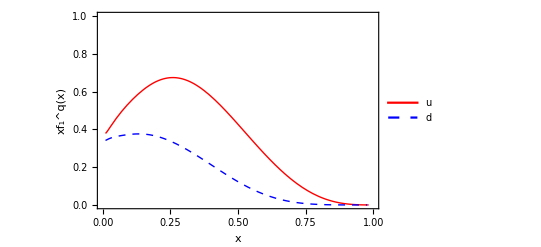

```mathematica
Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
?avp
?avk
?f1u
?D1u
```

```mathematica
(*Eq. 5.1a   *)

avPT[z_]:= avp+avk z^2;

(* Call your functions with "nnpss" such that you can compare with functions available in the package*)

FUUtest[pion_,x_,z_,Q2_,PT_] := x ((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sbar[x,Q2]D1sbar[pion,z,Q2])Exp[(-PT^2/avPT[z])]/(π avPT[z])
```

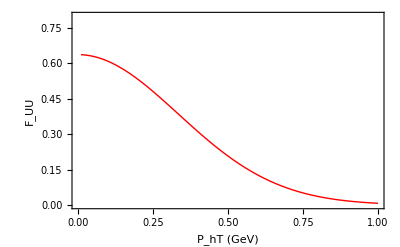

```mathematica
x=0.1;
z=0.3;
Q2=2.;

Plot[{FUUtest["pi+",x,z,Q2,PhT]},{PhT,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,0.8}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT (GeV)","F_UU"},BaseStyle->{FontSize->12,FontFamily->"Arial"}]

Clear[x,z,Q2];
```

Phenomenology of the leading twist double spin asymmetry A_LL

## F_LL analytical result:

```mathematica
Print["Eq(2.17 d) (*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S<P<21_HVX:?3`P;dIYK7AULR0_AVaQM6E4
IF=_I6DP;daUKVMdJ20h=34d83hn2W=dLVEQK@Yh0IfMfk9L]g66knLYUW=@3B_F
J9d?5kj@K</^UibbbeCi8/X5CFf9]2WBh/5BfIEgc1?T<I;KO0fP/H0e?@][MY`Z
KY4KP`Jjnnon6`g<mmG_Znn[n]9<hcaGMCD/oFEYfk6JnnHb;mGKQnZ?eN_ZTino
Jj[WkoS5JJSN?JlnnAGooNdk=gAIUWUR:?nkQ9oehdk?_j/nNlZoO=cE5Oo?i`me
=KIemOBkjY>Wci^ZZIinDieoln]OoZhN_cZgMK=lmJB^YbOEdcmG_gb:L4hl6KP<
UgIB^Di1;SjlHMIjJFCjn7=CMiMaK:^Y7bmC=hGIFSoKOeCWYblNWU@O]l]LWMnm
Oo_QnO/?KanNW?R;YCYoln7eloL_gkanYkoal[GkRGmjn?kMAOofZo>CjSn[YklA
:MVMe^f>R<3fW6j8e@kSINS7`IK[g5kJIk[`/>6WFWKke/M=`fGYjlWn>9KieI>O
9^:NKXUklo<Ge5e?aSJNA6V8njN=^:co][PMVY[ZNB_]bIV0TeKgnAWJ2>[in^7M
lkL_VNOS5VDmO:eo_b[UoJ[;cokli^eOWYcLKdJU_G[igL_g>^bIo`UMlT=CWMe4
o<Ul^S/g=W_^;Uf7l1e^dGDWKkn[AKejn=^CbTglR[VjSQVLR>jWm`m__a=cL_oa
iQ_mjOTKQ6cWdcT<OO?ZPa[NiSNOo_HGLObcek89kQLnomcIHcnbPSlnZNK^90_a
ooKe`onlS_oQmlR=nO3JkHKkFDEno_k=fn86m?edJHJA7NP_Dm?T>g3nGkF46m_G
hhW3X]/G7;9c3WTj_bP=7ZI;GN<fO_=cMckoK1em//2P7nO;f6;5fFPoMgGngCZj
VRk;E7/T2Cof4f8g3:d_mC24=OLNAlh_WRIScIUW?VKIbSf4EGnb?oE@eiMnj7C^
/6Q[KW?EJZo=29k?nIKQK6Y5GGGnl<kKBHmCh4/Wk8NooNK=ZeM__4Wol?;e]lj/
n6]_/e>e/EWmIk5ilH;g3mnnOOKZWO/`?_N[lk/7?`TOlNb_OnGG_I=noO;7eO2f
<7X;UkYQ^Bb=K8eOg<HD?k/dZYLH]_IPJEX^a1Gc/mRXKl@ef19FPMmiZ?RH?mho
NhVWlh<h9WmlmFAMb0dO04jGZAZWjM:f@NHaV=;?EN9K@jM;=eCSdUk6^Pg:W<?H
Wc`inF39f?[B=Ggem7V<Q=^Xf030GX;`:D_l50Via>@Q0[80eLCBOQ5FA]An;^7^
QXa=AdCHb^Pok?a?QODe?G]30Y:95]0e>_R]/=X<kFFX^gb`mk;ZS7g5gK5l]1W[
b`2/SOSZ089jH=NmoNMTm3Dj=>=hJFK6S_eUW=QgUmBXRci;m6;>?<dGm/`F6fn9
HQ/Chme]db1dLiWJ?PSMB?KQ8_>a`E=o6MX^ToYdSQW8;BeSaCGiXMQR?BZ`j7km
bcZcRDY]gI91gU0Eo[Fci[JN;gegJ<gFK[M=MfW6cL`JP?jb?g<3@_@;R^X_OJmZ
K]@lOk8>]]OLSZ@<_JgW`YYaZH693^SIG7<7e21`iUFji_gXdoI3<<j1=J^A75oc
@;KN:mQ]X2H5Pf_KK/DQ1JE/fhHT2=A6@c7G?I6T]I_If`15T[PGAXlGT^Y/daA=
oQk6gX:R5Z57O2XK[:U6`L[VnM;FdL[DY`d[<l6mGBKB/XgHO_3Yo6n59GOheRQ>
kF9CD9N:WAS:jEYM7C5hJ8Q=ANL`aNi`S[YE4mE5jmB9JmVS>k8K/QE3kU<Q/n_j
7Q/1CS:i5K_Ce<idjPhZei6BIS>[[S83g@g9gMQMQTWSGUSnMDP>^4i0aW:C<6bX
HfHnTB_c7UeF2MbkNF2dK8[T:<4>e8R:S]?=2oAFMAU6ZnOl21EE]c=g]2OO7KM>
ZhJ`kcY`h4/_=YP]nV0hU<44QhdQ1:@kWD/Vf3OmA@X9aYKiY71odFd[]I9l]6hI
NIL>]ZP9M6JhbP6>J[[7LhH]bYVJ9]a;c;=CbYjlSHY@]WPEonloM@U@HZhFE_M3
0jgLV9bZOAmjNR;5=<OX60c^Z=XQ4CDd?ORo8XnjL57]T_Y5g=YjBRU0mA?EQ<P5
=YiBM9BiQhb:i5M>:T`;PaXc0;9f?K334BhomiXoj]YoN?4PMI5XNmH7=9PmJD7h
P;02P<]EQTZKalIM9WQa?SY<3nMjjF]_[L]6ZLZeeOV7D5einBg50/L`QD?:_fRm
SVfSbUScZbmN?_No`jojgh6FBWD?;_?]`n/7V:Wn`mL?2AL=/eIWZL/DbT4M]UM;
PY?]X=[]?Uaef<hXDJ_[B:6e>WTHLCYZ4VSOCiaIGZ3eZSPCIS6kbbSFTheG`A>7
/b2W7P1hFK@Co6jOJJ2_@WRbZ@?XX?H;FY4<?iIWnG5FCKejN?HeMHR?ZM^9nWmh
nHjO2TYB:bMoGcI6cWA[iEOh_I@lT/Z_8ob^3UVHXaf`iGJYQ[Vm;<<BmT@al??4
SBRb0kP0jGGDKTMh72Pk4<08PH57QXCebboMQaA`]8E=m^a<T6=S5cl[L=6Fd;gP
coWXXmF9MR4I0Pb7IKid_IH6UA>Fd81diM9PoOWL?PW:hnoeaWFHE;^8g6@0/3^o
LdA5ChCo/Fko[MCEKETfF5Ud_@hfE=Je11n>6<;<jP/jlglUPbglk5XZ>UN;mVIc
>_]4ciMJS4G32TM8]5Q;5m>d6?MRmN^cYcH2`0Y9m3Kk[AJkWgAdU75kF4JHFUN]
FiI<KNO[>4^3SGXk2M[bMW8ZeXPjLA8Z=KVMZ=c5Z8UoS;FhV??CSGnh/3Tm:lK=
]R?5KI21T]>dJ1E?IDRmoEY]KClC<V@/Og;B56cEkmd9@7[na]DB9jZ[KHI]aVN=
0mW;mZ=llYOk34M44`VV>g_c?kHCXF]T9j0`8khCi=159<GhdaiTBD4O/1kjQM:T
eX4doKc2;=<B8fKigMcX9:W[VlHD<B_CaMfHaNU04f]gJX^7<B^C?2M^cWe=f0VH
QAd<_K8/2k</f16j;ISU1flM4;_Aj6l=E/bbISjMDlbj=[V^JCQX1O0bQDODnOBc
MFYCfA7a/Rdc[<hBW8@3d63EY;c;Z:_FQ3GEUR5h78cMTgGVOWL^HUI?3HjIWL>7
`B[e[mLeFe8cYQmTk6>TQQL=8gW5l3RYAj@6Y`g[[U:T]ED5@S@>ZJa59dQ[nVD?
;j4U@;L/:4]eiI7fCfFTQEWf/P8Hl]RZe/;Qa;V<]=:C<11T5a;>C>>EY7j>43Cg
86gnDHYcc_9>?U3_82e5[X7bfVfTU@h<Ua`JN44MmM9c2Sn@aSI`6?lY:/6GGcPK
?9XMn]gLj>@`dVJjl4Qk>YO>[V9ff17gI97^U<C83VeKe>``Vm]0F//1=C]/bD/W
?Kjm5fWmH5EN2=LBXHlPKCkHb0h=QDNTcAA^8ZgYP15Y<fD[IRGagMXb1D_/_H7F
19<=92f[Q^dP[A0^PU@HK6B7eZY9BfNLELal7JaVkZglm^6SU7=[nYD2G0@3ecFG
L9Za`[hN]NJ1LbG1ZDc/Z:`T^]SVcM5Q@oXdV<jAWYBH;8:33_XaKZbj3=@;UDlM
7;BUV_HhoKb<de88YhSALakHaca@=okcQ7MNfd];mK^SP=M;Xa6a;TNf;dXjeo@a
C?e8D</5_a_DZ1k?NRAh;jKUDmn7JCfLNaVEPMb9JF5`kZ2Wlc76^aU/HIYYZgRG
<=ildFXX=9S/`JTk1afMXG1X4cA]>IT=R>hLM3JW?TUk`mkDl1bPC4aDSX]^@iXm
<hBg9/NWe8jI1;WEC8[N3N4MXL_FSYg>INofJEPn>To3_/JmenHABf]]:c:`lnBC
DT3ejeN]5M8`^ZHTSI@6[3ZFQJ;FX;_ITI:13h3ja>UHn03Mo3hDa]:dgdRnh2Vc
f9^[]VX2bBVA;`eY69BCG6=Vm3KfEc?[kZFJ<`JS]aIDgZaK@eU1K<A]jJ/@/JDI
;ARL5o]do/>^/KK4Pi4DJk=Q6X1C<3LRL4^b<T;YPO7;C4SK`76Yfbg2/CNEal9a
IVSg`[5`Sg7BVXHjF[;SMQ2VGGQQde8C?h[63FT7FiJK^69RDWldS:a[>6ee_^Gl
@eF]6FJB>YR3ZD@=>[6>eHU;E9jSEQK/mKa5dhC8fiP6Vi4EYk^UiUV2LL`C1^i/
NfGRjUFYVZjmZ^>l/j?VeG=`AiNj[UQ]^k1K7BLG]>n6`F79jY4UbnhX0CBP^;gV
@_b@ldgZBg9H>@ikH]^VBB?=DX>QYV6W>6BQ]k@Gm99PIBjY45R>82hoc5NMihL?
:JBHe]92@RR0E3dQG0i<]`5T3CoG:VmAN@f?khDJa1YM322`n3B0F8RV0BCo0=Ek
HW3ECP3QZ1coESOAgM<08^f@Q^PJ@?:IeKOCQQaS/0J@O;0Qm/T@F`>8W?0CQK80
DQd=87iVGK<jFJI];EUHZfoaDDXF74QMAUSIdnm>M9JZo5mjOc]H//P=1o=cAla7
BaKij6ean6HKEcS@TYkgPFhJ_hM6>35=GPnd`]aQ4hl655lLgYRlaoGC^AA@O75h
<eReUd2ThB]jX;DIO3BRn>9`D?SFKSi=/QHCYi@K622AG`nhMQJ>KUe]^2OKk06;
H>oFX/fY8MhLo^IfXSiNZ1]`X==bT2Jm=2?g><;<ASPcG:C3]3ZZY3f^d/Lcgh1]
Yg9EV]SMLHST;EA;RfZQBEb`X`[7A`]m>oJZSlB5VMYYK]mQfEAGONV0<lb?bMf?
=<K7655SAH>FmeD99I8AHP@<Rl]:^OY?D^U=HhBQ21YT?LW8?d31BV>4@8D1]TXb
JVT7g6C[EGJaiMYbYGG0T@`olmIn4REJHV^</<@^7P5ZS12ae`hDgO64I1Q04DU6
?[<jg;da0RNP>:j53=gf>f>4=ibPO>gd?A`S/]5IS0RUO@/h]:c=LKRk6GI_S:1m
GXQ3I_:d8GYfZUIgjjj5m3ede9g2l;1`7f9biEnKGDNULQQ9:G?m:M0W8LI@O]Mf
5d0[7jZZC`:<HK4MbD3=;IH`F<eMibeA5Pho@:aP;E/g;g8FFXh6PNY<eF[_@9EF
P:`ULa=F52EIH?C`Pb1?^l32`@m83JWG5AoL;W09L^R7Q_FZMc`]E6dj3PdWkYWJ
bbdA5Vhkd9/XoKRM^VG<^E<EFehQ_Ff4]/[bRP<]7_A5;[C?fg8WLLV<J[fd@=4G
ThoNaRFib/HMZARGmUbl8LPRCRMUMYO6^P]B`DL;LDU^OB1<1g4K>^d;Ro_XhU:g
fYgQ;aZH`RNXbMmGoI9V`NJJ1BQifJmnKFIFVclBV?3DO>5Z^RVb6O4d12HA>ikK
ZY_n8K7jJeSC/;@AFYg]>RbMk5JlUZ8<UH:>RTi7PLG3^TYoGeP:MQ?lG[O_F5SZ
=eIgKbF/Xb>^hOKNcK1T^Y1BUmcRkj4^8SNjRofFMii<Q<5Zk5ikYo>nYbQef@`f
8X^mj<0nlTF[eJV[f3aOfLMVdJ[[e=Z_CCH>7^U5YiLi40QMM8ZeeV1oG]YUPmE@
bbD]jMlV_7QX2bJZJbk`7_;FS[>0cGKk=ANc3li;QE;WHTMLC=I/jh[cdX5jV6gN
:C:IdFVB[:^m/F[jScD=<7Vm=[KTMZ;;mZcWAHHcUPb^:GVY>VWRS7@ef0_TjE?o
O/5kXYC[@GkghDo^VW7Jodb3X>momWg;fQ^_@ehllcgBO`]?8KRoYkmIG`4Pn>ge
?QLJWZDdP]`L1T4Q=JjYhNc7a:KVLA6jAnF^F/^mfHfm^ok7Z85[Rfo8]4OHbVJh
VWcRJdII[:4>:NLY;Nn8L=4hC:ebYdjnDmNBMdEjN^1Jk^X=_CJDZ01GCHnV5CEB
e2@g2a/H93W:FIZnPjf>S9JfBcdbEkQaCBTk2Dd3GJFX^QV]Vo3Ka?j=gJO^?Y<h
bNj?D`0<GOZoje1Z<5b=h?nZ7gPL9[c:DZeB`kGaGYj5THKDkbX^PSCeb2/W[jXo
l=C;[C_7dP/WM/?=UcjN6jSH_mNiKhfVVfeNI<_4H[E<Tm6l_E_]Y37bkT`7i@4_
dg2J@igUjkA[8ORRDhOAASPeJ4L3;oJf?Zf]=1[B4Y9VIHkL/UiPF^i>j5ZHdU@X
`EQc<8T3Yd=Q/7Z:WkWD92Y2MeaRm@hBRlljljN[ZTadidhkYae4U^_=[/ko^Phf
7J^E3QaWg:VNPiF0[3oRi1lgh<NIl9J0g;FYBnKMLUHQ5;n?K`9`UWa=cZg1oZDH
JDoV>[3^WaGD;I=YRHlC1LUP[F6hCYfL6mPK:2lAL5:ESeI?NI_/X24hRLA0GkPC
_5KVYajN8Z@Y=nA;K[9J<iL^=;C4a<Fi2IAckHQFZdW/eEhd[DLMSN`MI]m0VKf?
jYKmGk9XDg3d=<=H?J8Z?>RFkG=U6M=8?T5Lj02X45Gle0Tl[4PXVn]Wfb0QOMdm
Fe10@XUNX440`TgFYYOCKl6XN1F7NIIgWLhO5KJ9iJ6SR::jE:=PINY8RSlcUI3L
?0`T=12YXkh^SJ<K>3^6QAema:gc2>[3:i1JkWS]4]9Eb1=0>[<^FVM>BUH6P7NL
>D_[c0d/;9J/95Kc3X;7`Z1Z;O2G/;2CUW=HK;kMgZQ?ianCPYNeg`21?<HBh4mG
[@jEiUVF@`T1[nW1/>IfSlW/Y7SMC;T2M]3BKPDBQ5EKk<0<0J00MCK9Ke`829:[
>bKPJHk^BDmMMYX>ER18/=?@MEmk1QN`<dal53]kjTbT@B[faZeCi;dfdIhDZX<k
V/Y:8<PlYHj3[EQEYHM@YU?gdUF1Ccd>N>GhJ>B@f0INH[BgTaDke`4Kk<ALZMB/
d7U3F>hjReVJBF@9>gT31OaBk=ahhdLUg/U51Z10mA^/@kda:F_JIQU^[UU67@kK
I[Vi]WIBF5i9ePh6Eo:jBX^YnDRUaUfRKE0VFW]KCPf7AYm8RThYUbUFhWa]XI6f
nN5QJYS4mFGajh9PY6gB9`dJQPR[PZ]_f7E<hI/M]e[UgLD9Bo>3eB^ol?MZKoND
AjKVmb`XGF6`E<J;W6NDQjEdaaF;d^/3U[XlDf?;dl6jjXBX6ESD:55S_fM>V?=E
AjJfn]DZZM26CQk]C=UIhURVOO9jPfMWLTDZ_RNUeWfHWFF6JK0cdjVi`^?HFL]C
V4>TmAXUTdQUBjkd;5?`/J@Td3<iB>M>JS1;C@cnTCSS]D?88eR>W^F3SGCG2<h]
BIbSIgj`ATRM>DU9S<6AWVD>4CciA>eYmF?;:9FNfK^Mi2AbLEB>UNe7@b9Abe@N
S5^86Xm?L?FO220/SN80Wn>me=Q;<[BI5eiKl25F^nmPJU@CF/1iZ;FB5F4]HAfV
lLSYOMLc?5^5nWLYea0/iA<fXmG1mi<=^L0[SlJ8h?5Y;TDeALAK9:3U^D>iAAK4
g^@JnhVQQ4jilm_:oM78MUJkgHm0_=J1fELR?GUeL1U5db9;8b6TNA>a7B1^a?iE
H[R6SL3BJ[4AJ]eDkMAIEEDA9EI4U?CCcnH@LJeGdK4[k`Z_ZHI]6[2d@DYU7Q4g
`YIB3NXW7=UQF0JV7N5Y/7S>:Rfc[=:7`4`lkJB9RYRAScj6R1dmPcB^RfF_CCa7
SglhHemTaba8c;^Q[_D[Sa8@;kN33DPdXZE8CMJ>[]8L8J90TJEadSiCi@W:2Z[F
09A0XVTXG9aWfM4IPfEZj?bad4f=8dfm32i0WjeY8^O<_MYLd`Y0nfD?HFUb@L3S
@5Qcg;8BL7Hl<EhkGJNYZ7YS2CR5Y4V;P2gg?W0:Bi/5/Ql3W4;BIXM0C^b=DjN`
NffQ?HO:3IQgBeD[L>j<mF5:dF]5gOfH;NfLdPXBH3N8OAAfQN6eTT4KNNSYo4^5
gADie`4Ki9A6h29`BROU;9FNA`5W;fmF`RM]g2ac=7`AQV4KET;BC7OB/l5l]6jc
>a^LbiONUJAA;>/k_BjV?WV@Y=4>:jP@<U:]LadVJOU`cBYRS>A=VAfB1Z>WjZEc
Zn2YKn`N[PFfeUhM[7gQ32e91:g/==8e_g]1R[/?e[1h>NKbnjL:M7B]N;1F]MUP
GGm2ejbLG>TJ;F[=eM;gj1X7R@eEQM]dcKCDB=Mh36CQhCfoD9Ge<5g;C=BPJfJl
RgA=ZRVaD^nSIEj[<QF/M2eC/96L664nd3GIhgQMmf1^4^VJ7k`GkZkA>m8eJnK3
YfWaoH/HI0mC=KoC@NRSNDUTJ=U>Na^QO9`j];5TD:0O`64jh:JHKR^BN5MfM<hd
Cj[F716CSaUC>djhDcfF5iI6GP5[TF3Ym2SW<1/TD=;EgQ:[enl<2A^NYj2FLD[n
f0VQbnAFo4Rb6W_Ea5M^`fm6Ze<VFHd182e=;@fm[B;h>>RZMKmCGIUblhQH`dF2
G6iEmGh6BPn7KhL@CLM:DkCA916d5ddR>4];1RZGfd8ii9HIX@@KQMa=>[I?27TV
TU2?ZVW?WN9]dF0W2@j]JHe`EcOI1W:?lT6:[di33W8g/QkRPg8LHh;VAiZ3gNQn
T6i_Mb;l:;/D?SP@97;[<23G/4]QE^hT>lM=YFGk;@`l8lSc1Z:R3;4eWDU<biYI
k^`k`lX6jla9SLb852:f74;SC/4RXd4O8H<;cKI1DgN2[R>3L_jNJDXm/GAV9gel
@ZXlm:WTRSmYoWJ=f1e<dT5GRW`:80UPVc6mhgQRFP5THm`U8RTmS:ch1Wj/_<R2
;SW]LjG@K<<>gj4@9UU;ah8O_Q5l7g=QTV8PP[MQZgFk7=k^I8Y28agkcHAFY4oA
nUY?LUc7JITZ>DQl<;k5`NGhI/d<A8]UIh=ecBDCj@7hFEc:0gf@Fffc1?A2:AL>
D:cTnRAEh^]c@Qf`@N_]>J5Ycb9/8`f>?SoNV4D9[=fg9=4WMP>/RbBDH_8RWDNV
MOaDeg[SILnNfRi_U>B3MI/m1bdoj1?j>a_nY=BiFGj9PhKnC[UU4mocRBWDhOk>
O;QJFHYQ>abDf3j/;l4NLbc]jfbTOb0fc>W4aHN8U7V6?L/BVE?lnYYK5OUho2Ih
5;^OE6f>NO[S3c>9dX?2K;2^nR3ci3bZ6oALEeNm`cc95lUWU/LbchI^PfKBgUFE
mBScc0gcK^K9aCWgWWgb25fBlMe8XQXJe6[P;eN`5FU/7@GRVPloUTD5hXZ:nTJm
lEkRjPM[CW0/Qh[4=Aml;8OBLlKPCoW<d^>nGk><ihaNF@63kRF_nFik<h>lL[Rh
Ab4YZ[BlFMC8mf16JZ0nT@@jDm4]^J=l4iDeMIVlLYXWAGG@SbnF2X/n6=`A6@Z5
LP2`QF[_Y_ZGY/]F9RGTMN5:J2kgHO^Fj_3<iLal^3[fORHUk5F^6h[Tljc;ePe?
lb5CL=S[;>kPXeEH]nZja5kYDi?gX3R]ZjnCoFC?K5dc[9N38bj6B_ik?g^E1mMK
Sm^K<5_8VW79ERXEO6]?3Ld9b_HA8`6ckf?o_C]j9KAL0OOA[U>j^SU`3/2m4KJD
4/WgO_9LLMFJd5_T[ca0EX/GI1XnK9[bJ]12CY@??`JmO4LV?DNRXdN0;ge7E0a4
BFj`:^THn<[S4>;>Vl4/`gfoFhW0@/SLS[UT9Yni>YM9;=T03jD7MMd9__:m679_
:Mm_MLSRRBJE;:V2N@QDbCDEBQ?0Jh[RKVEAALXQD84T@FhcjnlTMNK1]b3ga/@;
oRSOg2E3Kn18RLF28c26O<MdcDWQd9AK[ZE;5hX]mckdm]bf0;XIjj0gK;O^f8^T
QlV2gQine7:TUl_]=EejnJ:7l0mBgGU<[=?1^J8SbdQ`fbP=bB/aDW?<1n^JBeKR
_^k88Jo3o60UZZ/bTLE>Y<iRi>Xg3U?mP2_H?WRH:QNf/4^OKVm<^XCJ?KEdN8g2
@30>Wh?AQE8V/];@0LiV/:gFDBJbn3L5iGbdk[=W/_9fiI[9FAK:e=;Qd=0O<F]k
UdY@8[9L0ZN][i5>:i:CCCYei32EFKO3eLYB7;>9;?TcHZN_<<Ig:i>gFMbShO@N
F]lX8hbF[g3WDaZbbVeJMN`JNjBeKP?39]akW]Z@glGWSEB3BVY__KlEB6dfESEg
S=>:i_RBTV3d^_=kW9HLMZCkoi6WZC`1cE68=X:Z[8LiKFZRV9f;lZEgeOD`]N4[
ofQ]fgQXHVAVh=2[RMhk`V0S;c8Zi9jBDWWUhX4NU=m9BL?PX9iHH=moP5PYZCUc
OYIZ`H5l0n`TT6C/EgJkd4kgbD>5hZBnX6X^e>IKNRXj1d@TI?GF9T/gmNF@R[I9
Ln9O937j>R>Bhe2NR6HXlo8DBHIRfNd>dd9J6Q<JBHUBhk@BKg/d3UQ3I`fiCnOm
_:CU:cViF/i@^LnW5ZHnG:J4]2cQRIWHZZUd/;5Qe6UjNV?=3B/O0L/eV5YDA@=B
OHEiBGIP6aQ5=NX7S4h0DnDfZ]abKLKm_PN^]F_oD9FKal[8>U6^PE^WLbTi44XW
S`3H[YA@>W>U/SobN9G4UoE9d<>FAG4NhXgXLZX@[j<Hd6FTOe;FTHbG[_6TB:bl
J[m]Gf1_PAQ]1W]6ikjbJJn^A3a^n;[9<5R1CfM>6=d=ZNWKI/E/G2bLaX`g<[[_
8n5OmhPdP5j<=JZ9hXYmN:kjaK26ekk6n7;g=W[O:VSc;LJlL807BU4ZaT@DAUPk
7KS6CEU62T:IMJPSY;dWAVQZNDeAXSQOGN58UHLlQHhbe79^;<D2?oDVHhhnJ5jU
T`ZL=>F;S/Ik_cQ3_VfK<HfLnVc_Z1h1JZJT_B0GFkEEHY0]Cbk9Nl[FOYNAFZkn
/6P4knS0c[Lk1E/c8<_9/A@Zc>d^5NmX5QBDOmAf^o_VK5Qa_bdCPne;]gTnn:R9
BN^9G<a]j6mXho6JjRZ94GI@YD5d4_bBPmCh;ZggSM>ie?@B:PDlIYelEJ9>7O?5
5DCLOF/gV`>A=L8LjgZAL2QG9P>81>=@HL/Q1QR@KLiP`0XBIXbAkl1I:3[V`ogT
oRV87K2F>n<l9ZO6YF1m]EDV4<C1VG5incRMBa3T:WnD`6bi4`Pb;5<^OL/c:JI?
E:G_k^48@1ko3fJ]JmKXUUIE;5oV5E5b7_77=:Kk7C_`oO=LAY0KLOUXeEJB;EZ[
iP/MiC;2hc2XhjI?CFhLI]i0oSM9QN4jGN`X<?05JoIn9gEhfdbX5PYmbV4T<Z5T
_jdeTo_ah_1Vl54<T[[O97WZXc18;U6h4c8CPoH[YM;l0R]WiZ<H]<jfaJ13kfG8
]k>;QW`NLbL4BJ5a5_iTi35EEP8c8JQgRaCcB5e2SCXYPIU@7gXiL[]D1?8E/?ca
OJVk`o5^G;VLjF[WViLi;H]?kHH?hl;UObob<PioQWMa]=7nmol?<[YI]PYUKVAc
M79UHFd:IFiTKf9Z2S4P<21_HVX:?3`P;eAiL6DP;e1QIfDP;e1QLVE^M20b830P
DR0_DVEcKgEbHfEc83@P<21B82m3KfidIFidLb0c830PDR0_CFETJF52KgPPFc0P
<20e>CD^<SLf83Pd<Bhh>Ed:;d=bKg12KgPPFc8e<Rhh=cPa83@h<Bhg<c<c83Da
=bhg=34c83D`>2hb=cTiGB0_@VaUIFA2KgPPFc0P<20e>CD^<SLf83Pd<Bhh>Ed:
;eAbJFe2KgPPFc0P<20e>CD^<SLf83Pd<Bhh>EdP;d5bM49_N21K<20`83Di=Bhb
=cHP>3@a;SPiGB0_DVmdHGAU830P;d5^KVmdL`Xb<R0`858P?Sh:IFiTKf9Z2S@P
<21_HVX:?3`P;e1bKf=CIG@PFb0_D4A682mDIGQd85dP;d=_K6mbDg1QHfDP?3`P
;d=c<B0e830PDR0_@g<b83PP<21B83hn82m5N7A7DgAQM6D:?3`P;dMc<B0b=R0`
858P?ShP;dI_KW@P?3`P;eAS<B0f830PDR0_E6<b83LP<21B82mDHc<P>B0`858P
;eAS=20a<20`858P;eAS<C@:<S0P<21B82mDHcDP<C4P<21B82mDHcTP<CDP<21B
82mDHcHP<C8P<21B82mDHc4c834i830PDR0_E6<h834d830PDR0_E6<a<0Xa=R0`
858P;eAS<C4P<CLP<21B82mDHc4b834h830PDR0_E6<a=B0b<B0`858P?ShP?Sh:
IFiTKf9Z2S8b830PKf9Z2U/P<S<P<21B838d830PDR0b=B0`858PG@YUKVA_HVX:
<SHP<21_HVX:?3`P;eAiL6DP;dEhM4MCM65dIB0_Ce1=834P?Sh:IFiTKf9Z2S8g
830PKf9Z2S`l82m>834P;d5/M6EbKV5dIB0_A6EfJF=UAg9QNB0_C6E^IgAX83<c
>3DP;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1YEL7G5=GfclgmfJ`
`Yhb`TJF0FG;R<`0/XOP8RJ1Q15R80R8Re:/H=gR`57AXZQ5ZaF1>U6;E^[6[BoD
DT6YaEYLF7fOVh32fokNko]nGnk_L?oW>N=Ioo?L0d;JFgQBJBh58I@W:IB59g3B
YZFU/nSg4@<I8TgTRSAio08Y9bh^6ZHPBKi4B;k7oUkNA1PY^Ni2kSEfk7o/D@G2
0Sk<>PF]A530cd<8Vh`@`h@_UADRY38=i=Kc2ZDT;P>/Ui>D40ah5LaA7eh;HV@A
;Y@8IF8n:ec6:f65lo;bN2agEgMFW2`oDick3eJCRoho_kaL>FTgnK>0YUj@TaP5
KeN`_d;02b6a;n13O5iX8V1_`?e5hY@H`448DFbTQE<B04L25/QcTSV0W@4gI/[2
TP470;h[TTN@N192^56Y:2TE/0WPj9cl:7:]5N1<bIbHF<2P2on2Ga2L3]P1L9]8
b2EcIP?hRB`oPIcSR13150Q3@P637HBg^92K=8`[2hXBBCWHBM`X5@FCMX8^ZWXf
;c8>/1eP>f5^>:TGmZ56B`_Sb3fQCbfBi<J@^X80WaLF:?b5?XeA:4Z:0;Tkh:A2
FA:i5^bQEFJ:`kR0``3_5LTRB3WhBa^@iRYh1S6Q^o9TXN4PQiS@RfGb138>h2=m
Ue2BC<HC>49oR58`7Q:RO3@7o_:A17DS5RY0HUBT@5V8Qo:P/L02IfSQ<4/2C@Hc
2U0>b;<0mg`L9o_T2W:=2i;2F3k:Q;Vi/794cT82f46iT]`U7a[I8gO^ENc<7mKX
2QZ3cKm6LQPGXGhH5`6JR[XDTV:`<0oj`B2E`ePFh=5Jg859kRQ>HJgB1W:Le=8g
[2DOEPPD^YC[B3nE]PF3cA9D2V>TK@[O2D>2CDb4iTM44oh4Fj5=1S=:T8]2?UTQ
6m7jbG?B]kj?F^N2[J>m7afaTBROQWPE`/jih:5T>3h5H<dk/3]WN?FWJ2Xd[S:A
>dRU=B_R^K?Z`Ek`_5`fFlbo_7:P_NbH4F;MG7kZ0V;]efXi[o27S0b[TfRNLEfm
_NboI?EC=TM/6i_Ef=6lDC19l3ONP2kZ=NXEjT?Z3LB2mboDCVX_X7_Dno3LnFS?
Yab@W1:3G<T99M_h6:jHBK:@0i79EHcV@CC8C0TEN@Z7MCb8K`54C`jl8g?]0P`H
WH^a325g6ce><T:Y?@_fEOHn<Ij_T90<8OFCK?UkO?h_9fCDnLRD[3:ABVOEU`d9
YL[lTKTC;Xei6H?:WMT7fOg/GNcmk1O/QhXX:?;7_/GnSMg9gP4SCo6en17l>=j2
]n8MR0FmE_`dgZ90no5Sl7ckLMgH4j6<lMPC@O:C?g`2B>l;QcThnZb<[PYT?/Qm
b6b@ldMRV3el/TMcUHchJ0jA/OcOFC@jeV<[R3;kRU?:]6Jj<NU<AjH7Tl?4V9K`
^3>305Tc[ISAC4<HSF3J<d>Hhck6HbAS^B0Q6D@bka<GUGD_3J`LHA[YW`Rb;e=D
>Mj`_ooY8f^<Uf@558lnIiP6W6BU9VD=6M4i4UM5Q/MDd6C@94Kc`0hIa9F/3Q:X
?J`aLlSJCEH]H3`fGI73On0XcIMVC`^UfL=JIKERdD9X4K@`a::iTG;J15XTH1mb
5V5>^15LZ7ZaR4E`20lRJ1RCUG0b?6@ME<K8Q@R4d@0RQ?0VJnAXKl4BIFc9J_W?
WXhnQG3G:1@F`gd5XN1lJHU<W2DZI77PIRATLBElEfNF>m/=_XST?H^LPm2;N<Gm
2C?Xh<]UADXI@KjXB1G^H7[869TSJoRZ^h2]G/P?_[>QL6n8ADTX3Ld2jdB@BaW4
]P`]@IFX6Ze2jm5V]1g]@PfX4Ae2Am4aM1[mP2jR:jPCgH<_D0mjRPK@BcB4HAPM
dl1d<F?<0[?5W31gc1/;`4:aJ2`1Bl<b/2a<P/Va<^`c[1YKPfg6MV0=f;MH2gHJ
^h1MaNiPgEPOmPOfUX9Ce2Uj53>:7FD2aI_2XDAATRPc:EVD^IABBPEU1FDSYHjb
Wm94>DfiB>VTM56NDPIaQ:_Q1[PUkX9khl5h;9j>In8bO25NQMOPMGPSE85fo3[N
QOOSK`PJXD^`21O8C@BAC?29^LA2HSVaVMQ3=15WRN]4=c50_:MZD4fYCUAO:YLj
SIY5WDN]Y=I@jjU7Z>NPJ_M@Gm9X=0?PQAO`9HfFCI]?FdkKBS]0>dFkBW]46jCC
jLId9kXo?IK>XaOB:nVKj?_Y9nWGj3gde``eQPG3WA76B6M86>F<6/INaPW6=LIS
aY2:UXZ]RZm:[8Y0YDAUYLX^UEJEbbXm:T>ZfZ[fZ_jZBJ[IZT]D=jXfZYiC_Joj
@Te=cD[=AbeNCJbfF6fSfT6elf[MJVoDMM@MeH?EIjS;eENXkeHoYGi7oHF6QXJM
AY16^TJQaPZ=1Xdc6PleGS=eVJi<;U?0G<B/ICHa[c6OJJYXfVYb=6MYUV[FJ1kF
_:cI[jFRIJLE[<GCFZQEZmFRMD][D5]GfddkES]?NkWfG^d;f[djM1dkWE0MPDj5
cTjM<cZ?M75MJmePGKk^IkZkM<oYm^SAm>ce^7[IN]EjgnQMdQ_@em6OY9nRGjaO
ZgmL_l/0=k0ch1[T6Z`d>6A`dn2]XITQae1X^<b`dO2JhB^SLDI1AT:S:Z<3AYe6
KheIaZ76>LJ[SHlJ?c0QC1a=hTgVVF`c>FOB?di_W=lho[RZLHO6gCFUV3ZJ9YS>
=meYfV4jJ6I^5VhV=M]TM/J/gmc0?<PlfgbMn@Wc?P]MR`0;/LDjRi<FCeSj;0h[
UkFAMIHeH6UZ6F4Y]maQNLUbb<[N:]VZg>Z0e@=[EF]_jdc[MMI]eP<f5SICKLY/
m]WL]EFamKHEfFj`KKMmIFM_UfZge>jXGJnmTCgG_]AnWoem1`f7@8Ni3WD>=lKC
aW^?caVoMO`EAhZSQj?8/MKa/Q?5bM=9k;CEjJXceMW7FN9Ligc;AMf5he;T//nU
fmG0=MZeg?FXjk<9=Q?B9jbNd3kQ?M^3W@_O]g]^>VjAK^E^[Fio^3^jlme[gFm<
e9PH=W7Aa>J9cbLiCA9>fSKY]XN^aeB?YAi]7WmiNWW:?1/mnka/_3:l]WSMl]Kc
S_=NkWgNQnXcaFNAcc6O=kjN_XFnQgaomg?abo7KjmLkfGjbL?:^bHol[OaioS_l
^`9H0AT1G`Ed1EX6lP;[0Wl>/PhB1=D7?NJ<ifAcmW>NCF5?TDdi<^EE/6o`P^1C
8GQ8N4QEb:E@WM3Td<fQ3l>/`[;2mXD=Q7^4c`lo5D6=R8YH7G6;JlKULa^h0i5N
T@/RcdJYAbE6KHkj>MXaFQKM>YDb=G;ZfZWgHfaS9357He4/=gI]k8<hnkRiLMo7
dn;ShV_SOde`BbQ;J4oDCIbM^3OaIM:DY9E9mi8MT^G9KBVJ:C=B6U9NYHJT[TW]
VSIQfX9Y5m=<d/AYcNWdm9Cdn_C1jJ7Cedo_VN4aXg;6cIWf<h]WGYQU<R]ge_7I
V[=i/`mWD3=B<oIV_>?5l^YhPg>hLkK<6N07lcO`W`Z21>/4OD9ohA[Qhdcoc3FI
_EWnFF^cnTB1XQYA_cQH_5Wl?3/RNg_fZicHW=di7g9CL`oT<O8blUXT>Y8LbMUl
locRo:]B9fVU]6^^kmceL`MTDK;j0ZaPIT5cXAklDmXQMi1o;^l^2RRZ;GXm;fGN
hF;]HTUaAhUSbK:BajEQYEo?9nKcikNEFIH]:N]N`5V`Hb6fL<k2]TGFRbXFmB`>
GkaWRNZBW2DoUK?;eiConEWZIjdEIQF;:aim7_ki_TYVYJcbeU:oYM^o8;h@Og5Y
fLAUViJm[a9DoES=[ZjYO[NL_oc7;mfng?SUQaFI:bj]m5biKAE]UFCEcMF1ZoN/
dEiC^^KAfZU[VmJaeUF]ng?mk?DGJRKEK=nP^T6nXF]Sm<KVCCJKEVej]eVd^K=f
B^f1;JIKUVei]EF`mMZfX6f=flffEfmoniGhZm/k`WLdeMWEeNbTkBcJnN^^U5g]
Gg]ogE1_DUmMomM^bNj^?@UkcSIh=CC/=MfkLQmUWgaOgohInjml4o9=Lj=;hhh3
1PNZ3j:3lX=?_/ghm^JQZ4=]Qkd?=giWnmfF8kY7ZYZ`YY:VPJ>RXeg=JLeGFb9K
fU[mFXmlko[mkV>FafZ?jamOND;eA<F93bM;C`jNTYkZ?ieenU7Kk;IkIjJM^G4f
o^bULe7Wc_l@m/>IMTkkbO?nihmMl;g@lZ?gSdL_NUi/j_3X>?:Cadm7;WUNJ[[/
MKWiR/nEeZ^C[ijh5WS]m?F@jcoLh=jhf1WCNOEVl/gK]fKLj[X]^=ek9oO>lk]5
MhO^;HJ;OMD3[@Le3ddOe_e[o;l>M7Uf7Nl>jNkh>O7WNhohSiknD_3;^ij:GcEn
[GU/lKRQekggF5mHgiDWdiod?9Dn7NZ_o4gk]bg?79immg_@kad3d`IjW/^NOoQS
n@_S5k_oW?AWff3Lh<>GNBn7GUFm=WjmihggVoJgZFlO3lekAgnglJoaOkFnSgYo
od?NQ`oo1PT?n68:IFiTLgAbIF5]2VE^I6mRJPXe830PKf9Z2U/P;dU3@d9QLfET
838g830PDR1M2VE^I6mRJPXb>20`86mRJPXl?20_CR0c82m1K7AULViQM6DP;dAU
MVUSIE97@R0_C6E^IgAX838f<C8P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAb
IF5]2WP1WIIgE5?I5XO?_CNmd18R82Gd6WX98=8kB1D4DHU9P502QX@VMT@5AQ@A
:EITE<01AhLRHdDD2h>2H]L9lQ1@a/5AA4GUgHa[2Nn]=O?NV_g7FMoIikOGfFO_
OMNj053lPPC2M5P1P3BQF1C^jl5L4Q?;a?L261013UP1`>5VIPA7n4@2e?bm?IVI
Z4S6/oK^;X1T^m//_e0VLmKoOi4R=d<T1P0:AMDf?7hV5nD2U5>caATbo`C:m9DY
<XHa<QJQ2J:/8^?4[fcfYnH[^lVHUbKTXAYIcQVl=9j<^e3NVRGQXh`4XEbH9N1W
Xg`7IKeDBIX0iOLXdm?hW4`0<1BIGlcW9Z5/RC9551W^RO8200RDa3VlLPj;nCUX
WP1hYVOTRPB9BF:V4MNHJNGXb6KjlK=CnF8a:iC3CN68N4c?m;@<SS0GP:m_UTD1
9EU]VFRAkJdLkNeIe^IXnKoIgainDodmb7[kEO4Vk<nN@HbNFMm/k:`__AH0mRAJ
Vafc_YEE0;A]1T3UhJa?kb00lPD0]=jLlaj6K5jBa>8<9`^;k>a/L`6OJbh[j3Ok
Wh9_b[n6>ONIbnkkES^V5cn18dTE<fE5iJJWYT]4c<`<3YO?I?gg4?oS`3UYcLW3
;9bO`1OaQNQEDNRD2HB9J;^5?85HT2iT2XAoeN5o63HW1aUnWF/DJ7EO07f5>E2h
B@O8Kcd0@b<396hoNP9mje/@<@[8_[aX[I6_LhlbN_kWnQl;G8Y^hDa18U?VmPb?
I78UXR`IXmn4K<424Y07M:0:=84^<08/H0dLP3=`0mhP08B0B103UP<^B09Y@0Bb
@CkH00Y1<MP1MX=ZL03DPG[@14j2=W06G0AG`0e`2`b0Ad0:Q/5;<07NPFT8P_0@
5J91ZY0FY0nI@]H@6eX8ND=1D3PD0lE3RI0@TT3id2JX62Z3ZZ53D3gd8g@J^PQM
PoZP1m0P=0Km0Gf44IP2df4=f02fP=V`>a`8Al;;h4Ah5I`75l3KhDZh5Sh>]l8G
hA_`02b5Gl:C243820?AAUP86o54@Y1H904A8F^A8Z@2ZDFJT0jT6kV=B95ai0<6
Qj5QV1PFaQWSQeV<hF9FHMIRBS3EV6>HET`GiSIV43>1nH:UH]FaYUPW[3mf2CHA
Vhd]a5IPSf1K/9Na0mQQk3/L3/O06N8LL7jh65`bKSF^1;L?ehbkP>_33N4VlGRl
:]hDkh8?`G?`HW`Q_PYo77lNghlOa[lWT0UJ16^23b6F82A/95@@6PSW2?f44L8d
DH6XCg@RQQ1ia5aR:K6>f46lBA`VCY<DBHHT5e8T:IVdPEA9JR9M9SdV_B6CbCYT
Ag8HFD1NCjhTWb1O9@nB?e2D:2HDCdXLAD;ICSU:^D1i@7U3YE8=Z6kDF:ZH^YeJ
Cke4ODYm;dNC<iOcUn?9[I>[TF^EjiMk9DnDeiMgUel^WbMO8Gm:oZKl^09A`D31
Dh6S/5JQA^6d`Sf5BDFJXYERR6:JHXURPn8eaE4U_9:1T[LBCjU0jK3B9JDQ6T;C
YGWB^;A=]3[JIMX`7DLgY?_CTnW5m1oX_O@9IBEUFnDXiAcU6^FcbU86`S1Pn3=B
6JF<ThbkS8oc=>Jicn??fcJ_JEko_2VEnBY^:WbE8YEVU@6ESjY<EFoE5=FMZVfZ
Cm@`JRIZHF[IJ__E;Z^=cjO?Mik?WEldonClQnZ`^XUj^?YZmL?Z?NZC6YXJ_QXI
6UDJUcC6=AVJKY[9V^FJicC7]6QJ2kD4F^EJikEN<9FIk/aDIRFcRcVQ[Jk]YbgA
?ZCMZcf]HjRcF6NSC[?>4efB;U/g@KML]e=g@Tm;;eP_GjmAkj4nDIn]WjBoAkmK
Ol[0d23JH8]1Vl6XXHZQ_f6NHJ?QHb>ZTJ_A:Z=JXc_6>6>fLH[a?^=K9[29WDVB
BHg9CE?He=iDH;[?]<l<JnIX9SB[=K_7X[3LFEV/A]JP>L<lb7bSNI_i:`/mReR;
WAKM5Ul/kBaC;N//7eTYF@EHKKCZ/?[3f/BJJeeSOLN6J^=S/ljVgNJe[JT]ggJo
kGdkVUf`gAJkC[_?mPkf8_/Vnc47?HMhQkd>mmQdMRRkQ7gE4N_XhKS>lHcS1bMk
9k7CBJOOWEW>:Lh=cZ<;31O`5m@]67;ALN6h77:A;V@^S5mhL:7DEM^Ehe[[n/a=
ehgWM/A]a=gH?MWm^?/[3d/?TDN;aiBWTnLJc`]NR9N_Ei5G[kNBmf;_J^nW?SXn
RCj=?Q>nM[j[OBohHOd2oGKjgO?Gl>Ojeo]?13P4[0WX2Z@4APAF1ch;<PTB1GD4
`l41`K^27boBGbALe1H2@_a3MXDl2CD<GAGjLaP^;3B/9^ai^5EhOWQg12eRADA3
a;]8SlSBb4N;SAI;5WM6bDO5AME7CDEkAIM5BiMH;5Vci4J<FX`PYSdF7a/ENbAf
LZWgd]e;Qn?/hP[SkRhcG9Jck=Yb]NFYbln^T5o1FG4Z7Q/O7Ml@ohTC`ZWUC:kd
GkUgi@CGTk^7ni;WaR_WSO5Mn6GlT@BGQ;:4dDBGa5f9HdV^BAE9h`9?@KGPMK9O
lX7TZIB@U:<Y<jWAZLeYQ;Ch]==29F6:/2]M<cdW_Bo3=:<`@k[:JMG^EA>R@=6A
C2QcFFJkV8knC?E8S2BK9H=I2k=Z/]iWAfFObU7<4NKdi9[TK//MbO?9ngheISEg
MFNnM_j6o<4ekV/>[HGF[UcK^DigGL6jhOFnjhm]86e8fO3;A/^=IA_OKX[Ne56P
DK2nH6RcknK6@[U2DN6m;LiK3Vc5K1E/kMeV/jeZfiLRG]7eH/_RR^9?9MbBjmmI
OEOigLcfQ>fmYOJUngOPMPQgg=gY^_=HVF9IG]W@[^1M[NG<lZ;b]k]Gk;iFHE]a
H0mYSfB?]3:X/[e:[fY7eJOZY>Z16XnJi[gZNkO]WM[7fmNogfeod`6=0lD7?QhD
7;aob?M@Jje1KLEQg>6/`lo[X^Zj_fMoGgm4kDSaTLm7QDNUal:?MMDke=LgZ3ND
=/:=T/Jahg77KogPmD=k4j_YD3>S^OP4>24ilN;7n1o_WP`lfGV:OJ[Y9ofOm[K@
FXYJXMKLeXVfY3IYNdakgnV0didMcQd]?i_oO?B<mYVJ/lYWBlnAcQFLVcVOMgkb
@/J5lH^95hLjEg@n^[CTdYf^/:kNbh6G[eka^G:Yfkgko5FGZfN^>EdkOIem_Nf6
oHgF7[^NUUo/OVWY]Nm]_NU`/ofFhjf>_PEmioYMnboNm[YmiHkoWA/3R`KjkRjn
NomNg3gYOMkmd@NY3ehoc7XhoFSmHncSXRL:CbZNZSn]oMGhefJY_OC/X=MPck>8
Ihn6^4<_oiGi[do31LnYcb]6]4KZAje7chciS=ej/OC5l<^<Um?SQKlYo[KgUM6[
WgignkeWH/W4l6_AjiToB]jX_SWje_I]ifCXi==gJNnVYh[NZkhomX7mXO]Sm<NA
jNa?n4nEWhdoMg`9o?9h9VeVi]ogQ??k2VE^I7=dLVEQK@YUKVA_HVX:>20`86mR
JPYK82m9@d=2HG=UI20b>20`858PG@YUKVA_HVX:<R0`86mRJPXl?20_E7U`IB0_
D65WIG<P;deUI6UQ@Vmh85/`830P=S4b83Li<UdP;d=_MFid834P;d]YI7<PFb0a
830PDR1M83hn2VE^I6mRJPXb>B0`86mRJPXl?20_E7U`IB0_@f5dHFa_Ib0_D65W
IG<P<R0`858P?Sh:IFiTKf9Z2S8e830PKf9Z2S`l82mDNG1U82m1KVi_M20_A6Ec
M21K83<`830PDR0_F5UJ83Pc;S<c>20b<CH^=cTg86ieK6`PGB0_@U<P<c4P<21B
82m1D20c<R0`858:;d9_LVAULR1K830P<20`85dP;e9UHg@PFb0c=CP^>C4h83La
<bhb<3DP<cLg;S4b<b0g<SH^<C0f85dP;d<PFb0a830P<21M82m4@@XX;dQUK7IU
M6USHB0a<R1DIR0`86LY82m683@P;d4P<c<P<21B82mCMF9dNG1U82m<JFi[83hn
2VE^I6mRJPXc<b0`86mRJPXl?20_Db0_AfmDKb0_A21K83<`830PDR0_F5UJ83Pc
;S<c>20b<CH^=cTg86ieK6`PGB0n?PYUKVA_HVX:<c8P<21_HVX:?3`P;dhP<c@P
<21B83hn2VE^I6mRJPXc<B0`86mRJPXl?20_Eb0`83hn2VE^I6mRJPXb=20`86mR
JPXl?20_E7U`IB0_@Fi^Kg@P;dAULg@PFb0c=R0`858P;eQIFR0d>3<^=3Db83Hd
<Bhi<c<PKWE/K21M82m2Db0c=b0`858P;d5@2S<h830PDR0_@VmbI6Eb85/P<20`
830PGB0_DVESM21K838h>Bhg<C@P=c@c;S0a<b0c<C4^=c0g83Le=Bhi<CDPGB0_
@b1K834:<20`85dP;dA182P_B6E/MVEdJF=Q834b85AV830PIbTP;dHP=20_@B0c
>B0`858P;e=eHWAiL6DP;daYKV/P?Sh:IFiTKf9Z2S<i830PKf9Z2S`l82mC82m7
KeA_82m485/P<cHP<21B82mHFEXP=3Pc;S@e<R0f=34^>C<c86ieK6`PGB0n?PYU
KVA_HVX:<cPP<21_HVX:?3`P;dhP=30P<21B83hn2VE^I6mRJPXc=b0`86mRJPXl
?20_Eb0`83hn2VE^I6mRJPXb<b0`86mRJPXl?20_E7U`IB0_@Fi^Kg@P;dAULg@P
Fb0d<R0`858P;eQIFR0d>3@^<3Di838d>2hi<C@PKWE/K21M82m2Db0d<b0`858P
;d5@2S@d830PDR0_@VmbI6Eb85/P<20`830PGB0_DVESM21K838e=Bhe=B0g=3<^
<34c838g=Rhi<cHP=cDe;STa=B1M82m385/P<B0`2S0PGB0_A44P:2m8IFafIGAY
Hf4P<C8PE6HP<21W:B0_AR0d82m183@e830PDR0_DgERM7U`IB0_C6U^Jb0n?PYU
KVA_HVX:=3DP<21_HVX:?3`P;e<P;dM_E6lP;d@PFb0d<R0`858P;eQIFR0d>3@^
<3Di838d>2hi<C@PKWE/K21M83hn2VE^I6mRJPXd=20`86mRJPXl?20_CR0d=R0`
858P?Sh:IFiTKf9Z2S@c830PKf9Z2S`l82mG830P?Sh:IFiTKf9Z2S<d830PKf9Z
2S`l82m6JFadIG8P;dI/HGAUA6ESKfAU82mDNG1U82mHCf9ZIF=d82mCMF9dNG1U
82m6Kg9]82m6Kg9]E7U`IB0a82m2@Vmh85/`830P<20`G@X_DVEcKgEbHfEc83<e
830PDR0_C6E^IgAX834a83hn2W=dLVEQK@Yh0B]D20@00NL0h`YUKVAcM79UHFd:
IFiTKf9Z2S<e830PKf9Z2S`l82m@LVmSDfEd85/P;e14AR1M83hn2VE^I6mRJPXd
<20`86mRJPXl?20_AVU/M6Eb82m6K65dIDAUHfmTIB0_E7U`IB0_F4mRJVESM20_
DgERM7U`IB0_AVmbKB0_AVmbKEAiL6DP<B0_@T9_N21K<20`830P<5d:;e9ULfme
LV=ULb0d<B0`858P;daUKVMdJ20a<B0n?PYcM79UHFd:N04[E0P4007W0><:IFiT
LgAbIF5]2VE^I6mRJPXd<B0`86mRJPXl?20_D79_He=UM21K82m@A4HPGB0n?PYU
KVA_HVX:=3HP<21_HVX:?3`P;dIYK7AULR0_AVaQM6E4IF=_I6DP;eAiL6DP;eQ?
HVYUHg@P;e=eHWAiL6DP;dI_LVdP;dI_LVeDNG1U834P;d92KgPPFc0P<20`831M
2RmBIG=_MG9SIG<P=3LP<21B82m<IFiWM6PP<C4P?Sh:LgAbIF5]2WP1:e@81001
i`3S2VE^I7=dLVEQK@YUKVA_HVX:=3LP<21_HVX:?3`P;e1bKf=CIG@PFb0_D4A6
85dP?Sh:IFiTKf9Z2SHP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAi
L6Da82m2HG=UAVm^M20_@D51@D52:diVHViXLT=_MG9YIG8P;dI_KWA4IG=SLVU`
M6mb2S@h830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQ
LR0d<20_C65cM4=XHG8P>30P;eMYI7AXLb1K83H`<0Xf<30P<20`830P<20`830P
=S0`83H`<20f<30P<20`830P=S0`83H`<20`83H`<20`830P<20`830P<20`830P
<20`830P=S0`2S0P<20f<30P<20f<30P<20`830P<20`83H`<21M83hn2VE^I6mR
JPXd>20`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1
@D51@D8[CVIRKVQb@fmeLVUULR0_AVaQIg<P<c<P;dI_KWA2@Vmh2U/]=cTP;C<a
>B0g<CDP>3LbGB0_BGAQK6US@FiWK6DP<20_@G=SIFid83Pd<B0_A6EcHfE^M20]
<SPh82m3HG18IFUWJ7@P=c@g2RmCM6E]ER0e<20_F4QUJFMXM20e=S0P;e=dIFe8
83@g82m=HGQGJFAdJ20g>C@P;dI_KWA6JFaU<b0d>B0`858P?Sh:IFiTKf9Z2S@i
830PKf9Z2S`l82mCMF9dNG1U82mDNG1U<D<P;daUKVMdJ20a<S@h82m6JFadIG8P
;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0HeCODbEEAPo;mcgW2=N2NnkZlkh^94R
LXD16@BI6>0/AB=SR/2U[/JGZ?O^JR4VS_9[m/1:D^ML1Xdk1:d]2iVlhb:8QZGU
`/@nH95cZc7KD:_WYG<g>QOYWmHOoO6NlnhicnoioIkONHi2C<54DAC[fPf[e^D_
]jlYgKR]g9?UN/eCDN897>@I5V8lZQQA@DIT/377545<M?><L6Ga8n7:o;1`iHFI
A[RIe9TE<0L]<0Okc2H`ZhFROGcIn;0JCZ;2e@i;I5SCY@V0ZLg<R:XXAO^PXBG;
iJkfE9BEkk35KUYXNcic]Bg;iG6k?<hM5Ji]]ZBd]<A5LTU:V3ZJ56F[f6icf_8l
cUM;]SXmUCIGZFe7NLVo`@Wo]oADZe?KOkY0b8cHQHU9bBVYJL^OFiTKCLPd4T9V
4P_Ab6`bQl`U<F@Q/I<TXY3@8;VHB0KIBDHDRo:FhPnb1cD7Q`BG1WmUbSJ]`6>Q
N<`nGV?1coZe7R=a?<:jE;124@N2L111?Q4g:4blVcYoO1I]P8/hH?bg6=Tac??Y
?m062LDGkMK_<DC76429_>O4NDnQa]OCmZFgA3B815T]HJVH_bVCG`P0JlhKiliK
<:P7FgZd<N`IEj`R5M`R5l@/VFY]4KVH2Uan;KP6L;KTWNG6G9W3PAFKL3ZL5>W`
68OXJ[54V86;4:S6Yn4?3PoNabDX8l0T3nS6@9D5?o5Y8`n<=V_SbbX^_ZWjSc>A
BH^H4DEe9S:X<L0ZZBQh@Wf8J?9IQ[l^^X0WN`]ekJka3<IHHiUXYOE<n`kWoXUQ
67:VVcNO?MX67E:HJ[lA3o`=B8AWToU:MX7^7akml2c`K[QM0]8aAfeIHB7GkZBW
R@@AoTXYGlN<^AASF=6T4cjY3QdnbkdnK>[E36=G`8]YQ`]fKg^CRnaENd@Ui4Q;
b]6lNPShOKQi1lHhS2go=AYh:SSbMUOa@oEZ6kIRk;/H]hokV1Sbae_??AQiYa7h
3NQJ0ATLTW?cE`7?QbO?k/G8Qmhd_FkdjIKA;]Amf]RXLMlZXUPGoHFQCTFa_dnm
C76MdJOZc1la9M@Ad6ZigH]=OIXaE6?5JO^kC[@NiIQmmCQF`YOBS79QoR8Mn3cY
1LA`R?TVhGOP?d7WaA>=_?j@^UFdR]P38Zj1Kf0hI<AKWHnW7:`2WPD5en4FQc^O
Mel=>?McbG]RBRKXF:GSN]f2dCi<jAcYVYPH[2DC9;6FJ7mM<_Z]AFb4nR]HB^12
Me;<H@ij@4BXXY]R5L<DV/Dj:NK9J2HC:ACG<lf?kOBXC>VT1c57mK/2kDTJ]hk5
TXKjd>_CS4lWB`l6BRnCYK58c/XbRVj6GR[L3f<>6I?SDl5^1@K98M<6YGM<N2TF
belIVkcSGCjSB[M<T8b0kXAJP^NUhnRL9<0=E5aST?ifTPP3GP6>QY9V_ZWi@<^Q
KWk`[UY0ShP]jPMkeEk?mBdo0>n0oY=W>WU;NodE^<Sa6T==d_Q3YU[8e;5>][38
QjOU;0e<<P`5FTP?]70jX6P1aDcFAnDCnKRnjaC_J6jk;2_1UO;no5>l[77ShFci
VZXYEQMI1l2k[gT?KjWiZ0aNhU2hOG=e3BmgiMC96ei;/Hkm5Z0=eD=ldg7D2^I@
SmOXmhYT;mZU0g^>g0IAk6Eo0hE5RfL:IFiTLgAbIF5]2VE^I6mRJPXg830PKf9Z
2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;d51@D51
@b]GLWMVLWA3CE8a<20_AVm^M4AULf=bJG1dKg8:=C0P<21B82m5KV=_I6U^Ib0_
CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b83@`82m<HG=d@fQQLR0b=3LP;eMY
I7AXLb1K83<h>0Xc>3PP<20g=cLP<SLg83<c<b0b=cLP<20`83D`<20e<30P<20`
830P=C0`83D`<20e<30P=C0`830P<20`83Lg=b0`830P<20g=C0:=c0h830P=cHc
830P=SDb830P<20`830P<20`83Ta=R0`830P<20`830P<20g<S8P<20`834`<SLP
<20`830P<20`830P<20`830:=C0`83De=B0d=3@P=CDe83@d=20c<3DP=C0`83De
=B0b=cLP<c0e83Db=b0b=cLP>3<c83De=B0e<30P=CDe83Db=b0c>C4P<cTd2S<h
>20e=CDP=C8g83Lb<R0e<SLP<20`830P<20`830P<20`830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20`830:<20`830P<20`830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P
<0X`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P
=C0`830P<20`830P<20`830P<20`830P<20`2S0P=CDe830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20`830P<20`830P<20e<30P=C0`85dP?Sh:IFiT
Kf9Z2SD`830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP
;d51@D51@b]GLWMVLWA3CE8a<20_AVaQIg<P<c8P;dI_KWA2@Vmh2U/]=c4P;C8h
<B0a<3@`83Lh<EdP;dUdHFaYHd5^IfaU830P;d5cHfE^M20g=C0P;dAULf=UKW@P
;C8e<20_@f5`B6EYIfQd83Hf=PX_DgAUKEHP=STP;eQ8IFUWJ7@P=C0`82mCM6E]
B20c<B0_CF5hEfUTM6PP<C4a<B0_AVm^M4IYK6Dc83Da830PDR0n?PYUKVA_HVX:
=C4P<21_HVX:?3`P;e=eHWAiL6DP;eAiL6Da@b0_C6E^IgAX83Ti=C@P;dIYK7AU
LR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1]G]gO5CEe_H4>7>FU8PIS`eDVU:T
5bV:B544@GZ_8H@4@TRMm=iWe/bT5m8WY349BB09CB0P80YbAFb0E2l8Ee6:hSiQ
AnnkmP@Do:j_mkfono57P9UCeUkeFLmJLM2dJj]aL73@cGmW`Y`5Kkbd`3M`SJoo
a>VcQ``F7dmE^fSD[PiZmcKZLfgE9m]eMASeJ5N7YcYgMHQh33/jH<Lf_C^fgM^a
7GJDG;SUKWacS=AEdjO[balh?MNin=0o4NomeE7Fb0h>X0laF58g3AhlK>3P`D<W
NWT7njieLoO_e/NUKkLQXdN?k=m]j>31Xk^=mgCeGN_R_:7KM6MoMeM?IgojcoY^
LkaLe[[j1gO[ljZk_kogV4630P<31cYknPgdlWEk[FooKX5[oMfkcGKeLoD=L5gM
kDf_3OkMgW7fM>eV?l]0nln9GYkNNWmGgfkC_EJknVjHi;[NggVVnmYoLGB=`j<>
6]1dJ=]IXm<lXNW^l4:kUcZ?eHcCS7oF^D^4@cCY1QdLfV/dWPh>7CBJE8dVG:>9
dVSJJ3B16XffWJISIlec6TdgSJK7<iZe6/e[6Tf4AS?QJHfGAV?@J28eVUR=aT6S
LFi3?m]ZUSTldjI3VloJ9[I[K<NU@M8DZD:kF5h;Zn3`8`<ObGZTYOgRm_[fe_KG
>PAd>=IaHJO^WLb>;XlnlFQBii6M_go/]LOf>3gU]5/gEjLnWZadEPZNN?69:dnF
?bDo5OWde:O[WeWKAM_5_d];e`_?kWl^ioUWWZo^=ZSK[me?m`SYLKjW]^O>WQMk
MNSed@_^;gckX[5gYmhION[kC^VkXmnHO]nn=;SoHof[1k`hh=Q0Uh7G1^dH[1/L
?JC=T8n7iPjK?<`fk=2`2l>738lN7YOXb<kQUlf?1c[]KPk@GECOJGi7RL/aY8@P
Q:0Q8Bh2n3NoS94BH]20A/3HE<a3J9jZcL=Da7A04iXC<^RJiS7B[=4:/kKDBBfe
FUJReTV>K0?JORaAfiGL]STM_<66WfMSK^QnEG^b;PXKU<gJG/>KP3mbkCNlOcHL
U74;K_`FXEY[TmfB1^4ZQ5Dh4=d//5j^eWj;687^<4OV0l:j3L8nP;eHfj6/KaQm
Q6/a_3o2>^ej^MIb5A/@6_0JeRJ1CEjWkHnHPcGdn54U2^mA67`;?`A/bVC]F;lR
J6T[WeOK:Nbid8Y1>0i`AUPgoU8`Z9;/N0I]ZVAS:EJW>lOIV^?G_]JeZ7?EGPZC
BCkNG/]0a/__k]j9H<5Lc8f3b<CP2?@5m<l;;4NXa=`Rg0AHjkiU3/9<G>6JT0PK
j^JTN2?dA`h;T6^0JnEGBNPcFWi:a^EAn1J:/i[fVd/ABW6?XLi8AgP;Xa1g0S/U
/cD?GKS=]=]LPE2?^k5NW3E0>ah=FEP;k0^IEmTD9/UhoEcSA`Qk/2;8Q62D@`b1
4NP566ob;Hn1Y0R<`DSP//cGJQggR@=_GfUS^/^emT=?^c[e^>hL>dn7gXEY4KP:
N<UORZVfUKUCS1AZY3l8^Wd6X`734HC2B9`O;]EoR;0IJj>;o66E8Mh;@`7GUDDD
8YAPBAi^1WaoK^=hQ878>ba4k_1oE]7@N`LAUX/:5;Ic>jhkZn[X4?n6T]EOIKMh
BGLm4HfVA3=hK5a5bXLN9<PLk?UoU/E=Jf_7emT?O^g;GIlSI60iE/A0C69X=?X0
1ZN7iLL37bF;6;b_o:_EM^Fk7FMfoIn?DWol_aYPMI:d>34FUbB2[TWc7aYP6<if
2@h3oa[WXTD80i0olQnI`ndQSoeOG7^XU__KU7_J^_7e]_LA=V5=@[TG[3K4n64P
X3hk]201n1>b8`lDfVYdHVf?jbjb=mAg5=h]BUX_Oh@IlKPH^?Eg;jdb7C1_@ZS1
6/<F4DaC<345]`5iZF>RV/IV>[5Ek1gMO[E3LdLU8bdm2k<12h8;PQ72<2XZTJcC
T@n@lX<UeYliBWC?@I_C2OH;gC51?JQ@8_R5hYOmXQDbgKTEX9H5>Ufj<gVcCVD3
V:^bCEdZHKEgP@n23gX7hc[He[94<XFIH[<A<]6BH/X7U;Oa`@YFnVgJP;01oOa`
0n26CGjE8XM/fXBEM0FmmgWFa6d1K=hMYf[FDFomG?c@oLX6Z9LD?>:gLbF2>`Ik
2jobbON^ABS2SIVYZF0bVd`DnFJT84`4m8RK>6djA4IB<Tl2S4/QID0FW_lBFG]j
3I_oa7o]FNCBLjb<Fm7:;=J_[Dh7?fBcBmTHlE?gcjSVlLe;UM@</`EC0K=R<RS8
XS4Q;Sh>5Tenbg/2`Q/h_GA^4`CU1nAj88c3BB?90`5iYdo7O87`6AjjS:`Mh4KL
7M047jgIVd17oQ;gfE:C`FBDF^Km<TB:RL04=016ILIT2VfKTm>c@;Ddad/]N_jM
4XQCLY2=0FB_O9ACS;0Omhg77_@:cH:92i2dXLiXjOgGEc65CEJ@bC>oW_Bob4TA
GZJgZEe/;<oZe7Qnje7FYI@MZM3mfSb=ME:BGWekgG:4NKQPWlMFf;Foo^=MIf3K
lN:JbbIbfCF6NLIhQ2PLJO8fDggHQJE1X/i49l@ITf1^_nFCElj7R5c^`9iM`F@h
L>CS;o4hh:k@lbCAM1`o5k/3>ZM>[1T:Po]9biOiN><l`>7WY_f0L17OgeiG3BMV
_1oj[U3PdD?VBn2[KIW66QC_[i8>X`g`@WeE3L8Aa9i2Ve?63?LS9i=G_Z9HUnIj
KYl>QEje2n[F`=^cYlMi8Ha2on]h0?3/U]X3CL9eNN03_W_9k[HZFoGOM5]73S`h
h6iHX=<?QbTOG>1a2U[@798?o37Vi<5V8A]0IYj`UDePSk;782LKcFP1C4^dT5jS
LLSTVE`72gVKB=hFA`:>cN:Mg^<B7>6?GYY:[Y>:bAI</ioUoX]HZ7QC8k<XN3Z:
MI[;99S17QgaDCA2?2HVHSaP4QX:Pn7k?XOh<>B^i5OSe_19_3=gPXQkhANOW9PZ
7??:anlc7NaSK@PBh@Ga7UHf?H0M[fO70ieDZEigDag0@QAFYMf8QHQ5P4E1mYYJ
YFGE</E0HB12829m2;aJi]GJL?ZgB9V1QO@]/6X]ODag11F9_43?f4RO2L_`NJeI
IAeU;OH89ABE[C0YN<b_`NF?nB@?/e<cdl5/UTaX<]:Kl6f_MeH/QOQhZ_>DFEYc
BCJN>D?1H=OE>3KS/5<F:m3]IiE/QW9HiPGJFC8[J<fEU2KYRkWkoc;cgC?]@OE9
@ZMC:FfTi0S[gTlKU=JRTj:1on?G2E92Q=0jAGa6C1K2ATc>]6@2nlOM2IBhmMKV
Yja>fljcm?>TciG/<`FoB_S:oG=Hm]gX?6N46CS1ImE0l7PcHBbn0_QjlY26LK1m
c6N1Na0>h9O5>kj5ZQ<YYo4<WHfklLnDeCRc=?PkR3Z2Eo5m`6=h??d05;8>Gf@@
N:_6hl65OB1c3Xk3JO@dW1ce=XCeWne9HBkB>MF_>]^a@2OVoKW^9]_Mo;R2Vm3/
Co7jmS2TQ;MN;/;g/JT<FW9UM4^:78;P@HFVa_8eeP_4mcGF2<CWXAf2BEUH1nYQ
lM1Ck:NOK]ZLm_k4EWcSFd[6e9eBk]bFf63fg943N8=R@3_T:ni8J4c2lH=`:>2L
_JA;b<NJK6`0;0/^LdN85LG122DO7JPkS?0=KQn3X`5OFOCZg>W0io9eDU@DGN47
^YmDFE_19TRnfPC?^1GAHA0G>`Gem?Bg]:C_RY<<F:lBe_kVQjE>SJcMbkOH:eO7
gMIa3M_>OU;>UAonA2Scg;23;b6lR>=V2?bmcQY4MLn6AEIAmoH^aC3jgikS>ICM
6o0m?@h1S3C<lUT1WT_F9_TJ8MKXIhPSTHeaAX`6GD/DAZEQ?/8>kCV/Vham:Nbj
_[UQ1L9:O3gOoGfXBK1ILB^QL^nR3@Qnj16>:`07Gi_272Q>7?6KKo0FT8QhK][Y
W/GgC<FN/JUj/]G^Dl9FK;@bW6aRR2:D6T0fJK0dHB=28nk7QXM@n=Ob3NXDNV_E
9C8FHFXX@PbiIbcQkB<]J`V]/49]:R6N92e;DQnAFQhQ2nX[F9__fC@[No:ldmhO
U]QHd6GMcnXl]X`ZC8OA=dP^F88[@mgLPBf@Rn:[hjY8jTOaTfl`1c0e:HEDHBCK
92A1H<cR@>XVG71If]9RR;DHj6=:MAQ;P9__TC4HHbTcY:7ITY`:FGUe1lhR=67Y
/_APb5]SGXf;@7LGgG66Wc?h[EkS/`aQ0/kN7o8nF8`F8`EG=NJGR_IVDdSY>XA`
M8o3IH0SC_ASk@Seol`0Kgf7U=F4/n/[e1hUiknY9cNh`UIOWGY5el:NHVNECC:b
E=JiMYn0NXgae[F4^E`@U`>^gaAVAJ1f88>`6QiIlNhXlZ[7TGOQ2W8O8AX_HS3Y
6Yfn;Gkk3fA?TFo[QWi7nI^LH3:^FARhQ5k=>_0_U6WXNB@n5h9gheMH07Rjj/HE
lNQMJ9/>1F]`8@56G8:;@]c0LlJb10Y18K8a@;edb^UPjKMG:EUhZgND354cRX4W
JRUn33V9QE@Ueo5EDZWFTYMa=2LKdU9?Dil9c4DK5OXZMm2_Pb6lbc[n?;i0UAZG
kd;HAEdLI/8n6Mnc_4Ni8[UThjDM7`;[`VJ;o5C1oWJ8iI>>m_[_H6Dko?OZ[[>A
jS9UfNK4;DP`lH>?6Tl:i7=/0Dh4W;ejb@agh9foT]R;oIE?joHdRIYoMNRQ`@Rm
LLah74S]QGUihe;8RZcc;@d1gNeI6dK<4Gecme]_oDB2B_S]NObI@R5ZYf/S11F7
I[iMCfO_kJb`AlM:5D6k?O4M`?6_;aR=<08WOXSW0@mG7K^hnii=JjmN:55k2I]>
_LYFGb4oKL]>:QhblXRNbfH9mV2NfG/;k<3dBR6ncBnGDT<XN/KPJ/2g3ZbjB3:@
Fc^b[/PlQ4VIUL/O3dFHRh^3Ebj7EL_mWO5e2^37o]jgeJTn`8K6T/?dN]ki=BDD
Un7jXa1LQg]a3n01g5eL1nEk]nH@E]V5eF_cUd>fAo8dhIFSe_HKISN[`>S<jhhX
?AOIG=Ga;fX??mg^;f0iEM3G1BI_OFR@UO;3GcmFMbfXYJf2GSSfkO6D<TFf_Eln
/o3C[i01H:GQlgUo[<0Yi84V4jBI//cYMSC2b]SCmFaP_M?1iP6jRldCfEM:kT<0
XNFk1i50;X;j3jf9ceLNP16DGe_nX@ek22nXgfTM?D@g`jillc4Qmj_5MjJFGSn_
hbbBVLUTC]M?eYA1NE5a;CJBCkRLhWdY?3DhOC9>1EaK4Uj2D845AEP6^==I81GK
o/>iU2<YbN9THOjIXL71`C1UXWh@nMQbTHgRZB7:@LbP4:fAMKoDlhEoHAa7IT@K
FfACU`DjECF?Yc3]dCa=BLPaY56R3LFTn0@2@bh]gd[12eg2iQVYXYJH]Y^YS]R`
bE0UF/55j5/ZA;BH<TeVf<FNU1QZme>gAidoPCQ0ccU8I8gPU3k1[@SKLINadD0g
1V]WH7QJE3G`mLfB=9lCObCada;GJhUD>TfdedZBk;REKK<i/NO?/l?G9mbPF^b[
]U6HDLIZLmY^DTEWkGF/NAWW4hiJ?5;T;Oj2UTG5:=L;Cac3c`6o7WB>?d76JD<U
IY?f59ZSd0eJ=/VjWdC]NHf:5gfQM]FbYo7:IO`7gC3j2mjF^UMi>SnSl<NdBm6@
Q]G0bV@fDo/3=Pk4]`0W;ASMbah:K8?NeSb0J;WKZTL=HHE[1mVgU5]Mf<]l27^7
i1^9gk?WkKjH:KPOJSl`gQP=/KaW]m6LR^Dkb1M^@KH?M3NA=K45Fcj`foObh2;n
8YS3<HW:BahB^RP65ReCCDjS7RlA4dD1G3ANFU>kL2oEOMde?P?i206AEhZl`[;A
e^a0NW_^TZZkXK]Idca>NOSl3ijnSIJmR^`iePOIC2X0/gTG=XB?/b^=aOcBCKVW
0WG[OJgOd7j89oCk9/7fVATSL2`UUkI1<m`F@j3gk5T_4P[A>[99I;/S=UJmaHUe
_L`FUk:GBRfUe6Qg?Jdln>[?]Hd/Ri2?;aoX?h6oC^IknSN=5lUGb;QI7_PbU6YI
PNb[aA5Ajo/Q3=6b^?^R<4G;1V3ig3cn?5gUaOABbi67C5e<f^Q3`^bf/Ef]`/`]
ICe;RHDldobZd[;[3aLo85b=iCA^4h3YVcm`X>AnUkCOHNJ3TXf<GTMf6:5UZKm9
eU7;nV7YW3cng3g975VegYHE`19]jP]fUgWi/W^=;TbmLUC9dMNk41c882hHLh5=
T75KLPXaS]Bf6^LJ?0D2NKVE`ZgBGT5;55:S:>]f8fo7MC5N25>A;jhAKRBLJ57e
4HBOlI/QAKcg_n537UGc3_@QcI<[_/b78WLVNcZchG`HVdfN5OHIOUFfQI0ijE6T
RPm]K0/i5QVejK9>EI_EF`[FV[=>4OPPV>JN=1iM4E`9Z[/;`_VgT><A<VoB/PSi
gkVHh_<Q>g`^l/IFo:8E[O]YGk_7cnK:[4W;1KCo;IA[;7mb/KZ9>[FNml:RjfFZ
G7Zkj9J/<`QUM]5O5J:_aUMKABoCWQ6:]VL;jQfRGRGbRIbUaW96B;<=ckA:hj=m
EO@>]B1NT:6g7VK]e02KD`?U/;jG:5nmaoXX>6SAW?VRYIf<KXL97fI_5PVceZ^8
;:O7]GK`??kTS</8]o2cCk:n05<j5JT]X<jD/F4S7QEn/<;PJUb:h8c3d5EX]UKk
OB^Egk9D=;X?74c]YHiDf5]/_9BN_WoOFL5mn2AiR1c/Q[=a[KRigYSZSc60XM7A
/G70So<VRIgl[iYVXTa]Ba^9CN75DVY<APCahnRi6ZW35RZd5h8Jg=YJ2>IQ@;;W
3^2Qk1YUoDkTI841j[1F9k]8oIMjQVDY_]ZX5l;iHg`B`^Sk:D;Mo?2`Hk0HMZc6
/Go`_HOMBBfPKR];LU@7gm=I]`YedeV27?7=OIDHJa8BM^ES7dX;BC9YKbUUO9;M
]<ML;G3k7T>=Z7jmT<H6iJ3FbRH]RonUSI@BTB9h/RbdY2MW0C<fMi9<fQIBk^ln
FVOiF2BFKOPg[1>]cVl>CBkd@7R@43j8a[QPh5h]AbC^ZAhRmE0<fS=ke`YeM0E9
7MHlE8W9=YZ2B>[GB>Y:KBhF6G>YlD`ROR48FP[oF_Ql>BG1I4b>1kEobgDY8m9T
C1=m?jIQ8JSDiICSk]_21mf=R`gDYZc3aFIg4bWS=^9Bm8JFLC:oXnJAL6Gj/^JA
IJ8J[[R]^mW/bZhBcUW9Gj9b>9GTVhal01n>O9Dm``cTPmVKE>fV8W^93D=63H_<
;o:o:blQOnK_b3IB</]V;gil7^5[I3dW8LnPn`[h/b<7]MINDF>fU[6SX/iMI[]_
Dk@5/Q<:6j]U7I5YcXYFoO/nOnO?dZ__?6C@Oc>oa<Q9I@ZSHDd[f;R/9C6a^nQd
UQ:oBMDFn7=Djl[ho=/WB]VSE[FbE0cXnU]IkhKK=ga]^WmZf1Mib[`Rg^hcI25d
WQcFkNaEQ>_8^Xi0CW>o/I6lNoNaX3oX/GLV`T9L_i;V@nRM4f@R0TIVPc:E]D4N
R@Ci5f;/;RX=F5ULCKic0:g>FK?XRXHPQKGOOi4mCTZTiom[GBmW;e4f9`_H/2Je
<P=d_dKUm]lhR?ZnFeQ8b8O:ARIV4K28@F</XI?hNLjN:a6FX^lF_f?fc1nV]i:b
me]ITaeD<2>Ca]gn[TagUoVc>`[;U[44/jdFb3AGDY<>EhQECTCn0^2KOV>h:2i]
]L`]@[VnjO@7N1[`>jjm`7_CagokLk?DFTjfA/U9]8lPOh/B:[4d?=CmTTMl@LeJ
f>Z6j`DVVhX^3Jk@h?INo6J4diQo3R^XVLN/E]0EHhb3n4W^`Kh8Rc5fGoPeR?Q:
2Sjf^7Y^XCSP?X9aPb^L3Qik^hcM>CJoC7NIgE:OD_SS=VUjk^X3N1S`T`<OW2I_
O@F]O5CZLS35HcaEK0;K:A@UK=UmK1J7AV=L9;S?US`[EcD<5DO7TL<4McaZohCC
gY2E^2ob4nXSCiG7KHj[F0?5?YW[J:21TaI=72T65n=Bi^n1F@NBSQU[`IPIBe@7
A2368FF1YC:6H1bm=0e=i[@/6QYK;=Gk`KKfV1^E3_H8O_Dm/SJP^h`gYY`KFF@g
78f>eGL2fK`jYmYBUWjIYA?bJAkH?5YYHMXP[ZO6Nb<KTE_=2;`DH1UV6Z0hTFIe
oP8SRgU`3h8NI:<6bbeZmJTS_=g:c[QXNb1aXUBRj3:JTA@T@iJiW;XVX2OU[]_8
Aa3V2B8dAPV;E?]TJc9_]U5oLHJ54T;^dNnEo/;3N?]B@YbP?_IPi_]C5=7BRO[R
kPb8Y>m:[i;ab[ElYPE;4GDlmL0nXdS5WKM5ZW8c;S6/AG379FJg1e8E_b5PS36P
nFFKDf7c4V[g7=Acb/Jjl/Z?AIeLKg0anR1hhRbcSkR[bES/@k[0f:Ah0lf`gVh9
T?PLeBc5KjCjC=aYiB4/]Kl]jDf17HQDJWgKAh8LMPDFeW9GBP]:BB968ao=:BU4
6?^Y5jWf5;F:D73GCgOaKWLBXN3@m/a]hU6NQ_E6`W/Kl>eF4OiV;5Y7JAcSTf:5
2?eJETUl^1XQ6I<=ZIP2^?T`VDdL>6Ub:o9JJEhUA3n4aIS]1]Hg9?ilbgR9Se2S
9>:LdPASofOgO8792MU[P2e]JIH/<IIX4Y/>VYJL0fbdVR:a<BfYOoalSW[Qmj:d
ZGTfTL/_ZTlXk5VfC;9FKJVbSeiF6iLJ:?1LR21bJHDOE[e@JkC141M5hf0nE^8:
VbLI;0WYV0bDBO:g2g>h9dd@IeZ?dde[a<RVD?/N5/HENP6KaVdB7lDCY?10cfGD
LQ0N<SF:`Ub7kkFVRfFVT791E6EHTRUDF0nfAV93NJaTC[@T2ZHPDQnbD[Bc=IK?
19i[_=nE1VTGH41:P0fh6o_dmj>a2iOXJ3n[5iBj3mi?9[j`eEU4Hg_OFAX`;dQ<
2j;R8lC0Lc@Q7cj5_B_5dLa<F:Zh=7UWZjDVh6Z1i9JIW<FY2[@OHgYDWPn`=OaK
RBmh42[l<@Wj4oI=bR@fSlfCfCcf=lWaImbRoT[3e59eNRU5ehkV[TYJ5ZfC4;FA
5bo`E/]LKI@md=>H]?T/6dEa<dCKlW@;Un:Rd8RaP24Yi2^P>V_cFA7eH[7lnJ01
O3YU[U5JmBWe[R@V79Kj^og[WESkNP;>jMbRe<_m]7OkbmNemC9oE_][V<bN9KIJ
ONi>MmJ4A?;f]nYIalo53f[jB]Di2YJ5U;^9nDYhM7`l60gf_@J3B29Tl:ZdChmn
2=Wg1dX9b@VRDaheS]83;I=/F[iMS9h;bPEZ]TmGoe_?N^1T7LC9QSG7:7@L5c[G
[ogYQ2kRF7O3R<UD3`OLJW8RC5]4UeVJYb[l6MiE:Z21=]bBV?b2E50PlJMIEj8P
Xj`Q=^IQ;K/jj<Zk=:Dl]N@Z6gWR/e:MOSnkm:FBk5;^C<A5<Gj`4LoB>Xf_UQI_
I_W6DoEMQhTkbE4HiOU6g>IF1j^g;LYK@WPGgeb:D`Po5hE@Z=nWQ;8CZYNIX;aV
CaIihahl]9X64F]TGLgnQDU_94gcQ=OGnRh@[?bHjki7ZHoCkcn>^nX;Mi<6hmPX
YKN<oBN^GBjZhJXJg0_hG^=i=S[EGP^S[9T1jRP[Fm?XM>L4bc^_2f>_ZidDmXW<
NhWmP4l`?Hi0D</e^EA[<ZE_;=l=^SfioXf;?ROOjX0oDQEB28_Xn_k0]J:378/[
UhH6dj<]?4mQZfA:SZJ/?=Qfl;edfRWHRKDnVebQK9EU]X0nJ``c=Rb7P?F^jnHQ
;4NgCGie45i<10S5/^`h8jZDEEn]:gGJLYh]^1X^QS>?/0d4<TNNJm`_n^NSaQXg
F9DDkhTA=<8_2:bPiPj;l/E6c<OS][e6C_dH3R:BSGNV`@_bagoX@a`k/6N`RS1S
9^6PJ55aJD/[TK;]QX5C8mO@2MCi>6`k/Q6]fVUd]ZX3k=XQ8O9>j?JXWMmCY/R/
MiITTmo0f3@RDZV[oo5QKO7elXKJUFEd:=hNNoA5CR[R^^ok<:6R?LM`iiKB:WXn
:fk7W@FCIhP:0LlUboF4`dP;IGiK`JLQjI0H;mFISeC^Q6;Ke^X38R`J`fc;8H^F
c0PRg==@C22KKgFZ><mRS]_WEneHRY;:nUhXgH9`6c=i5b8?NKCF6226XEKB;K5;
n<>ljj@Kh823NQ5KK5O?<coeXb8[9SXkJD90B2TceTbQBNZ9=lB2NjlQa<W38WCI
k5l7W^oRLFZ3B@BnA>bEf=S`2nUF9mK^n5GJnF8CeHV:f?Gjnk__k_R;GJnj=MGD
;Kn1;llWf4AKEOo_K]Oo][;5]=C<ldLX6o5E9Fcfh@/U34^L:YX2_f0C_ZQYFW5H
mg<DlfF_:l<AKf09H;VY:[LDd[=;:VPVn3ERKe6J_8dNHKh@6nW_AB=LjT]P]H;9
F99O1=^l6Y88iec34bO`55TS]<jg16Zge:HDR?f@5;@H8BXa8DXd_24iTGUR<UfH
9]jC7eU5JCl@El@k[`;WJVL;XOZ1n>JKn1[P2Z][J@14Q0F_XnDlGK<6enNhfP9Q
AXS7BW@1W?S3G;81/?Khhcj1Wf_2mbf/P?TE/i0hAUmLRG4Vl4P>/:7MQG[a4lZ;
n>Hng4o[2e_[MUSPONdU@^B8i<7c9RdRVUU0GS;BdgHgIVe><=LC54Y]_UAnFin[
<NdS@4O1dmBjlG=oOFjJS3nN?7P<hBQVcL?I`<=oga;jhcd;d1N=Vh5AQ[^4]_Fe
49jo[VPF`TQL<B>4h=7]Qd>T9El<dhG_=;9>Mibn^??6LMfeog@_BGLcVDe@/<Zg
V4RFmJRgkoAhFge/8X>F5]/eAIk:WJeiOeOmk2md^M[d4jgZgFE[a2YDOi7ZCV66
?MEeXd?6S7PK8H7X0IlLb4d^fTQ]?hej1HOSQL61HVEX`D6_@`QOh8O7l1]@XhQT
IQ?nJ_IAdQX[?YA[Sn]^gWW00]FdUePY]_cZSOF2;kmWPM_b/ONTDmdKihQh3`Y9
31;XYl;d_YUZN2EF6R_5]F]XP>bj7kR>CIJ<iXADPOZBCajQcH>Sna[=a@9LKDRR
5DK12DdgQ`_0F6S<S199<c0lDW12gKVSY?[oJ`<e>obf=2HZhD=58OmgMoRC=CEJ
3[bgZ=NXYoaPMckQOg]H6gIMhLFo?n2?o_BOn>1oL/mOn6ghen>cZ79>`:D[_JJ3
k^a?<^l^W4FgieiU_1MMd^oWdnglog:h?a?d_VRWOQ=]innR9DJEZX?]iF6cf>7`
H>^XOSkNn`k_I:n>oFP/@NVO2]B?;e5?2DC8gJB:;VK@g8L_EEKRRV;_GN2k0cl@
jGhK7]Rd0lYgkBjVk;T3]n_;ET;IBYb5[X1^>4no0_C;EfaHe9Ybn7`K8D?ejDKO
dW_@hSY1Rhk:lG]nMQ;ChPVcj<jf^?o^1E]<CFK2?NFh[iEb^foAEnD<>BFdLMjG
9><3Z:?O3k`MUMC[Hm5iAJ2NY;K`G8GibIGkmUC^4i?O3fQ:8]7i>[daL[aXBUb;
_1/4a329UB3I/NBNT?e:2LNfE_RcJ^L?53ki;dEB3lUj[N]PFWb=Z5Qem1Ek<NgA
3oTCm;K7[[lXT8K^k2OH/=eJ:NARjaGNGDJ?H2nm7dB4NgPC_c/1gj6E?=[lHAdn
>DmhjR]/72jVFi@I9G]VY92iLoc>9MdYmPZkZ;0f<Won0DbVfoUPo?aiVAa8>lB=
UdUc];Z0IR<T6@<SA@Kc:QHK0`EHVRdBI=GjBX8O^U<Cd>f]L?]PRKN9/ZX_5cYE
UoZnbh9;oMlUXV@eVjmH4ln5RWWj@WNG/B:o^ad:^PQ9>LIT`POgjH^Wk]<G:CAo
;BbT7BPd5aC23^NMATYMQ3=fo@do1Mc_^CTb6mIE[DigCZMgclUj:dO@;cEU3IOX
ZSJH</Bl7T`a6BChOOKUiWgbQAHE<B8BTQ:SHa:C`;ERUEQlXDd3ekM`3Z1kWUNi
W^RA:Yn:n4o3kCX5`Y>_1;0h6i/Fj?CS2OH<dB=/?2d:/ih2AOCD/VV4d8fS?K_e
C@BmO57;:hV1N?AJI2g2BJ`hRLOP45d`EdKjS@f2RVlQCH_bPMVX_TH9X?PdIL[F
l[YCkG966B:cGPo2a236I=kk0@?b=fDL_V@b[Fj>a<CMf0C/h[d;CR<Qdj740<Q4
L0mVa9kXMQk47AFE7mZmUR3k8>8de71ZDhNcBdY6BOkfhb;?na/f68WBm/=UiQ2A
in^<FOj2D8Pa92I6`@/lGN;]F9DDWm=:JIA]@`8ba4<HiaSX=Vmd<GV:;_DX9/OW
[:ME9<jTe71c0W43>IRLTDbKHDoJYkDKFRDXX27bAOFOk;9B/=NFDb<Td9<4Q7Df
h79cT92PeVP=5]^ilOB;4A4`V6M8ODR0a6bS_Dd^gbHHA:Y?aXD6?l75K6PEX0kc
39TAT1:OiITF12>Xmnm?kFZ2j1VC2LCM^n^Nf8Thgn@Va=j;fDWI7/2Ln<mBB[PU
eRjf>IFHV9^/E[[5jjCTZ7^OF^b7NHBMUAaKRk9C]VZRKZnNABZK]fkM/jT<K;D=
^K_5TG`<WZe4dGacQ3QB/B4m@^cPQdI79<C3m;7Bf9/BS@7<HRlg=cNSb7j?LHXQ
U9JML6W[0^XW]02hN`Kl`1EY0>lP;ITeda0PJWVIfFJRO5N9SHI=H/BP]lCU2>KG
FUWm`JO`IFlY?BXWE:a6a/B4N@/:Hk?YX9VR]Qbg6CN;hSn?EUKl:h4o@b<PBVO>
eX8;ZYilh`9Unf5TV;:Sndb4BgmcSF1LJ]J;DmR<NB7fUERS8B4BG^A6RKMUERTa
di0/M5aF9`Pn>S`M9>@1egQG/5fdBmF_aH5f1l?GaDN0OZkGVoO@DU01f9;C[IQ7
3`S:8iL:A7d4NP8^KgCK:f1T`j5=Qh1=D/M9SS>`E7fLN^IBmZ4P<iiAGe0b/UX=
W1=;CA7`chS<646/INZ]`SY:1T1XWeNeM99Ra39M0]12PI2AWBL^H`Ia6C6lOL0:
JVW/_cQQDc]BNljX:D4eTEK?jIn:EFi9e>YU=E7[Z<KI_kXKZ]]o=mCneJnQm=GM
D45/O7Y]nDjWldb@@<>K^b^Q^A8JGIOBAY`on^J6I89gGW0JjL@EPo@;id1NV8BV
[K^YdBW1d[3lJ2P?;HS;5c?<@^^nPb9N4mGS=ia^gkQfPaa/QOY?fU/<;?<DB5:_
5kmHhVGEDnNj6H_:a7HHDCe?H8GNBW3=4`=mJ6T@oHYl=P/TJkD:VU]fK34if]ZO
j:2JU>NVS/`Oe?4Ak>RX]jXClmV6[5B[UZo:UZdI7C^N:>[HjGl0V8K^/0YUKVAc
M79UHFd:IFiTKf9Z2STP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAi
L6Da82m2HG=UAVm^M20_@D51@D54:diSKFYSMd==CDU2<C0P;dI_KWA4IG=SLVU`
M6mb2SDb830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQ
LR0h<20_C65cM4=XHG8P<C0g82mGJFAdJ7<PFb0g<S<:<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`83Hf=b0`830P=S0c85dP?Sh:
IFiTKf9Z2SDb830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQ
KFDP;d51@D51A2]>HfeZHgM3CDe9@S4`82m6K65WLb0c<R0_AVm^M492KgP:Fbdd
=R0]<SPa834b=3LP=cPaGB0_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P=cD`82m4
IG=SIFid82db=C0P;d=QL4QUJFMXM0Xf=SHP;e=dIFeF834a<b0_F4QUJFMXM20e
<30P;e=dIFe883@`82m=HGQGJFAdJ20a<STc82m6KfidAVU/IC<P=C<P<21B83hn
2VE^I6mRJPXe<b0`86mRJPXl?20_DgERM7U`IB0_E7U`IC5382m<IFiWM6PP<c4a
<B0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06]Eg]`DmNMU/1GoT6<
B>`ZVdh8jhBBQ:H50nVbBE/bH18P`Ba?lhY9S2fol5>BKDVFK<VF[LMgmO1K/RcI
UXfaSF>KlTSG@6`N3J7Kd9:DY9]V2LUV=m?]k6bHKG_T_Ik]WV^PWNjSdlj/om2I
>cjjioOkc_Mm_dm:AL9lQE:Ye>cK^>FEPk^NfIiCDYACWIjA/GGSjSCi7jo47eG4
UbSSSln;;idOod[24^Fg5RmA?_7P4^GnQi2TG?[Ybo=38GoB?2@95/Vg965jYUiH
XURnI?7Ei:D?mUki;G1_BDYD92ZEE5g[mGN<Y:F]GIVF]RJm[=bT:l`_<:@nWK<R
MOEccjgkA^ZJ];CWDSNDJ7F5>MVUZAWIQP9]BKJ1?aBWkRk;:M@JC:U?OjO0H2Qo
O]FZj^[ZUMTUnYEU^_ce:kjAFUeX:4SMYME[MEGJg=BGbTX=ZM^cBkBYmmYINFm=
;b/Y[cAXMJTIIKUJGJVa/5ROXb//=ob_42PD3cgbk@fKG]ZbHoO[NOT5Al^=IX]2
2LDRaA>:iHZW52/DZaG?:TG5I/DFaEK5=/E>a@758HEBTCb?Ob@XSbQ?cZ^LokF4
IhDgENi46cfo@5S`ThFa1oZCVQMIe9_DVbF5nRWYl7SlFn?mhbbMOmb^C^koQ6fn
N6LbiKLfIVFOJA[3[PRj2M?37ehlBGdU@nP73N9Sh2;Qm5ha6fB73VE>4TNJHo2B
]aDRO8BNJ]43:P9f`4A`X5idT?A@G/IZ_41hmIQfd4Q?K=:]Q9K`g4mcgZhRUYP[
33BL]K@hZMDIZ4L3`ND^;`DehZ1h^9lLO[OX15WAF8M6P_hCo@G@gn?<niPTW2gY
[fjUf/0gCnSJJ6^OD=2i/`OW26mol5h@9?:B0VhjKcj1@M08oV6^nS<I:08IDHb/
FT8RDk86CDmK125iRllCKRB?AoBhW6BgJF47eJ06mEelicYY@7>l_@oMX1?g=gZL
7PoOV8LjNF<UC26nDBfMTCID/DbFU_`anfk:KEKDZg5]:mVl9h^/MAj?g8JSXjhE
5<:_?`=KB[RAOfTg:0_51GRMT7=Lbg_/AkBm/d=n7@]QTSdc6Ln[CTji?O?EVODJ
id2CG`NZA8?CFTFcSlgnZe1W[3=]m72LC40YXJ75gPTJaQ^n4M04C[[6@BgX0HH8
4A<J@0dX@fD7OL5B1AICaJ@W1J>cf6<1EL<lmh[JSZH>d2Q^nDI1<L@l<GWYMo>U
3M6kKk9`4_0cKK2:E2MjA5LgOC<^2M8RJHGVCNVd85UDK0Lk;JSI;Dc6?im<WXVa
[g94eUgG>6/l7Y>Kc9iZ3S1E`0fWVnXLo<59<4D@1/DOEK5CH<lb6mQ[1;I1B[TY
[@3=;U?M;m8Da12X5e5?[hNTIK?G1GH/oYK6gbF:cB:eRBgP?C2EJPSGGNNdM26K
4m=0N35?FUZnVgI:2iIUBHTPjD6EQEOP48T]Rml@e3oWR<LVFMldAc`nSmg@o4Qe
5Mef515/;Z>[S]`>Ca?L14_@e@j:@V`>A>Pbd`_n8;`@>LSEh;@e`^eX<U;e2lFF
M=1^eK^/A`Qj>l2o`ai@<AG6B[6F/mYI8WM]S28P=b>fNb<DHI/5<B`PHYKaVAeC
EL7SJG:BXlU]PXM3599IOKocafOO4OhXXQjHnd03>>HMT9Dl:?8_3f?H<``J`Y3k
>:PCTK^G>WMPTDX;RmO^YN//:ZSS2cTPgi]TWI<LT?mH=[=HdnLOTj4=LTkiOMCN
8TKT[X?f05N23QE^cP/MM1jnE:12W5_:_AFPNUC?/N/?;^hEZEf@?U;mT;D:ojo_
WB?4W`h;AdOTj1c3<LoL<^SVBc]J4FPQOk<ga7d>4B_:@ED`RUDR_LLV1?JAJX/D
oC?0ok=?HDo6Kg459O8[J3g=cW<A7F2Y:EnbofBG=>a55M/6U/`B`1HBkZbJTQkQ
K=6XS?N<P=>4gnemV/P2nImh^5aDf`P;VPQo@9?oXe:^oN>4J1fhBml3hXN/FKS9
g_m_^_]geFElH<M;Q;[JiGV7Z:[lL=UZ;[K7E3OHR:3na3`i/o1/<]_65<c<52UO
cQbLBM>8?UnG37C@iWF075bE]GFd9d_8?IDIfL:oW84dJAVF4c;k]Od66R_^KkYY
YUSSH>?aA^YfG[<RWG3Xb1?B`b0m]_Zb1VWG6<jQQoQ5QP9APTl<b0N4[:RGgLkS
i0[M;nD:/;Fi^2^g0F976oVl9dO3@KYlh7K3>JkFoOR<[L<M`/G:DhHHiHo[0n^R
m=f8l5Ykn@RnAcSgi^M/4NPF?Rb0971m^Ta`LH<8bF;W1^4=m=0i]T=@BhoFSLll
?9klbgmQnMm?nO8>BmI4_ok>TN^bCklM_355/JPXXXG@G=O;aNCT2=S]Y2gNUId9
fPWganPWS?YSPF5ZJNf=];CBm1AKbmJ2LE0n?=:Kcd5J2BU9nPSBOS9K3^NIJjSf
g^1YjZcTZ^Gm8aBTBi<2BfCOdIaQg`i4^jNXYGN22Fo:;]5JSJ>4?=_VCLm@k]im
Nn]/lR3:TE?3eDVV6dnnaQJa3mRRU7Ql@oaa3E^PR_kN?LblP0CE:=/Zn2;`][MA
/;=3=[H@f]bMCJB_<eFPW53BGl?UMAXShcQ9N6_OD0KXEN`f5^`V@eiS[S6EEW0F
gie5YVii7WbQNV5f_N2^]fe[/Y:kZBK[Z>b`3Cj7S`HjXlMTEPk[`ma[SZ0hGhhH
NjmDC84n`=C=eR2MOCO6DWcMM95M4]B_l5KHln?a1lNCcc<QiL_hH5bYlHOA33oQ
A4EWUL`<Dgf]QJaMALMfl8iNa39Y3JBo84P;?col:FP:YgXR7MBXJm@iM>@XMI@D
U55f@I7/3gZ^_PXo3OEjAnDGmYWkNNHXP[H<FHB]onQl3oA?O?;g3[<TnTel_B2U
B`6=d`XW1c[cd:/b<G=AfXMYcZ]AU]@e@F>OGPUa[kj6_X=`4>N4ffGSll/RZ=m^
68lo</kniU9bO?]_^2glI>HYSImkeI`Of`8fVD8N^?Uhe3@:EXo9Pk:i0L^Yg/4_
;NPVjF^c=`F?dfFAQi0nF/DWJS>nSm1U^/[/@R0:KeL?QO/^o?RFK8kmMQ`Tk7a=
FV0lB;IbU`=Vo_R3XiM0_lH5]TAFF/PR]e370j2cUXi:loOHn@acl3R5GXi6af1c
V:;WoiH]`6G25n_knFb/a7I/c^3CYTm@=of^8oIg;:6?ZE?ROf9GDKCl/JhR66X;
SI2_;OB38DHDMGmFQnebC7Ea<5fe72HkhNE[fWM1ohH9mSAJkkMRP]_MI::6D_eO
kINSW[d=`hAfKk@iA[h>OR[GjndW`nT]O1CfQbm=dlln?=?9kh/GI>?CnX33V0<M
XK9Kcl=D5==1_4NH:QYn7K@MNekK/H^Wb4=IfR[jIOaQ@MdPIDjb_iB_=CUN8]=c
B]9`NWSh7cFjKC:fI]WOnDGJFQ^hX8L`j^>WSO6PmhHLm>k6/nhJT@MH:ll?]B:M
IA^5;^]XiC@g/hgPU[/6k34NZQJ_>_?GX4gHUe]S8Ng5[Cc<DAi:Zj[bBIMC^eLN
2]H^]<V`nQ48T=L;Ko<0mO`le/?Ufh5>Yib:;6j[dd[BPUV]`<aaPfKXSLTAKY_G
4=R;B/:n@VUaCBhEKcbX>`;J0OdT>/PK4]iQOT7me]ae9imTJVhYJZk5dOQbCKkM
E?Qka<H`<HCco?M8i]Qfd2kT_Ei[8]fIgM5MG9W9f2`]UX^hFfLW_`eoT8KnnOgQ
dj2CL]cUGVJdkZW?Yd;Y<L6b?KnT4=@40jZkJ;`mlPH6kT^d07VU<[/cY`_N0Eg1
a=UPQ0Jb;a^_L=BBlF>f6:?g:G6?gJEYjBFl9jfLFDl@NX?CKA?DLRcfRd2H^Zj>
SHc9MQ]3SdEfd<`6=YoMhCUnVSFbGfQ2H]0C4^VDmkc_U4QUiCDeCki0dV5YING;
/QB]g351HHQRBc^=GiQXhAhhR9RibdHSU@>VTkbV1?bDZFGo39TiSKW4K73EDkgA
[]_B@8dNJEm3YHN>3hK3Mgi6k31KfOLSfHo^SShilCKJBEmP=>SUV5HI=XA97m55
lT1[/F/=RWT9HChenDS/P2m8XIHFLMQ;?B[ek:oDYaHbhH7h[cA;GcHM28V[TQJ8
BFYcMga7:j_YDDV7Fa?7oDU9o`DKDU]Z2VE^I7=dLVEQK@YUKVA_HVX:<C0P<21_
HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAiL6Da82m2HG=UAVm^M20_@D51
@D55:eIgMVa`JT==CDTh82m6KfidA6EcHg9YL7A_LPXe=20`858P;dE^HfmTJFiW
82m=HF=BKfeQKTE^HfmTJFiW82m6JG9cM4=XHG8P=cHP;daQLgA3J65b834`=20_
EfUTM6Qc85/P=c8b2S0P>3@c830P<20`830P<20f<CPP=c4h830P<20`830P<20`
830P<20`830P<20e=S@P<20`830P<20`830P=S4b85dP?Sh:IFiTKf9Z2SDd830P
Kf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51@D51AB]F
MgI/L6Y3CDe9>20_AVaQIg<P<c8P;dI_KWA2@Vmh2U/]=CDP;C8h<B0a<C@a83Lh
<EdP;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3
HG18IFUWJ7@:=SHf82mCM6E]ER0g>20_F4QUJFMXM20e<30P;e=dIFe883<b82m=
HGQGJFAdJ20a<CTf82m6KfidAVU/IC<P=CDP<21B83hn2VE^I6mRJPXe=B0`86mR
JPXl?20_DgERM7U`IB0_E7U`IC5382m<IFiWM6PP=cDh>B0_AVU/M6Eb82m6K65d
IDAUHfmTIB0n?PYcM79UHFd:N06]FPMhU6FfWP3oi4R9V^aHF@`PcH:8GL17@56A
gS^441;BbfCBboAbY_M<NYfD2KegjB2XP69OGI7EZjkUNWNo`Co^g_<Ua8[?k_F^
?0ll<Oolligf_^liih^@m>/[RHR8R9TgJnkLNK?^GIBWB<e<WSYciP^?lolm9gbW
93`h8SbZCgQ8go2]o@I7[;]aL<AC=`f>Z;`I1dH<nO?d_QDE]X5mAPg/Nf1P?a`X
i8SFkcjkZQ86BnhI?>Jkj24geAgk9n:eO`I6BPI5A41^XM7Zm5De]KAf71PgkZ6a
hlJ=WiZAFI2m8C597S/jOTc/PdlllMQm/N?7SG/RMW9J@_J6n;Sdf9UalZB4]3Pi
oI0J>clSOT>2_21fm<@T^Cccb@LNb<_;6a^GUS<f8c_aZC7gaNI]T2O5cT_8BLQF
9:b;WIJA;XnM5INF4=]]emS^_jMVY6GVbQ>bHfMV[4_8CXm;cDb:Fi/PSd^<Bd^;
FiN@:Xm;b<cIT9ZAoV3nQ/`=VDTK[^<PBDCdP7jgB6j;629i<V:BI7;OJI;W9C?j
c97<kk>TCmbPc8RL__UmR/V?f4oRUdCHndQ^U4P6BB@gBBC3nTY6BBAS99;kndPN
U4PNkR=iXXmTbR39g0S9P[jBYGdT4A;98oc__Y:m4M_j?=OWL]ohOQ<5Yo@9jNG8
Vb?GA0IQo@fSKcSO?g^0L^3;Pg:SC3LVg7C?cL=_I]4GoS14=Uafo1KM[DoMN^Rf
^]]7glk^f7]WgN2EOa`di?HQ[GMm6o_Nd5?30/>O6Ok^gAdSWQ_if:RKAWdijY/5
DBa66@cO5HcNmAhkLbWVjk2CaLXnoBK4KT4GX5][Db6DXTV_ED36R=VC30Q6a2J/
12=kAYA^NPi178[RGN8ODA`:>?ZebGm3>8m_=;ec0^XW7]ME8ac3d46/0OBE8Gfj
78d6P`J:hSHHM@PUF8Aj5PDHnGBbk9TG7l^NRk0HEkGQ^h0K:omkkb^`kNQ;SM/A
SV3k>_l/23bWW^2HBhm7KALW:mSd8?/Vj0TbHc3jWgeR=cNNSnT:Oa4n9l>oC=km
>9e<Q_N:8c?4?R2>ogj0H=BhM0h45k[@hXAGFIg@/71_hTD4=PCI_Gm5mQ3P^NaM
BkN3`ec]]m_P@>O6HgR:_TeL:ShU:c0D6?>i0OC71SGfFZa1l:37i37@8n`>=UN6
Bg?W92F1CZO8eiXP`ik[C4O8`QTFG0NHM/aBRm2>[MIF;kCU159`:N2L_1OBhf7m
XYW[WdIh0ALOa?>0O[?OjX5c[4JX_o`Q6lGj8Ac4_MWh8SML;BiBQ2nm7Aec>3bF
?B8[HcL^OLmTQ]c>mM]O89=_`LWR24`2E;T<CWhnZmGZP[H[Go[Kb=17d2M>`LL0
5aQD6SWT?Y<Vm/Ed@:<i[a;1Rnj0Z`UJ?gFOLn`6JmeA=^5C=QElmFQ1:j0I_LD8
N]BK30K@6bJ:XiJ:@l1@;d@mFQJl>WY;m:kcoaGjWkMR`Z`Yo9a<_3On:O4f704X
m_]PeTOdiOga2[/KfDS0ceLMg[0ET[Lnnck^1Zb_Z`lQQ;2nY:D86X^[eCh4b[16
[09/;;<^lL8lGcZJ4=KP<`Yl571aL=hVkX_:C=W6>@e;LBKPY5GRl4LAhW5V<gh2
N:R=cF1gKn7n4Z>E@AHOH[6Qj0?_aGc=;[9LFBEF8gmkIBTFT<lVB`=k]gg:KT;X
U5IS9F8eH:24obYN:]j<hYP7DAa?M_Coj6TFPO0ZG]b65N@?DfDImhOAY3M0@OW:
S2D8/g7N=_`;X1f3WYg0YTVS?Z1h/KQPN49NM<b7C<On9[?G^49X1j`[lQ@RK41e
/[h4a;^j3PWj8]BQ4C2kET/n/6>3fMl<EUL[6e3k;UBEMQHMA7POGg[5JX?ZJJlJ
jITmf;35E@FeVbZ>X`g@XGOBTL[@Z=EV@lV2o<G[4>BXZ/4PH9EgYk<EV[lA7<gf
>ULKf>/mFm41f9CWX<lTXCJkO1DX7QMBaI/5IKaPe6HVb?>Q/3@mOcg22TaY`]>0
cJhfAb?/H1>5Z8O4=L7`BUinbXkglZ8KCmCnnN?fd>VHOiJceFbOK7?9IZ`WSn9I
a4f0K@]a0d8NY^:jD/R]D`GiTHi^_O3jAZRG=f<M`QHlI/7>kRNC40Za43?dH7@J
?>P7[;1ED@ZJcFQ3<l6BaZ51b4ELQB[0O7^Qf@QR_oAY4g0Rh=:F3E]b8GKFnY6h
4W3L9lTMIG1DHL7mQM2XfUK/e4>U4T]@2eQ@VYj2X<JeU_Q6D3Y=IT:TLS@XD@mH
m7;:DHAc^?d<kP6/e]BDED1YAJUmORdlg3jmXLP=:EF:AP`1K]oleYlXRb>IW6fG
:He:@b:20_EHiX1:VhLb3E[@J@XH`1Ci_5P_Dm4C59ElE6:A7N[]?_i4:kY<5Ob9
Z2=NAGS0^FSFMHBbIG<h@/HRYHYa1I=a<Z06egPC`AoWDM=7j[6Q1Q^1GVgA^d6a
YgPO_PoHP3/2[`<K9:e4;gYLh?=JoCc8`Fcb9hSOBaFHP<^F@f9RaT[D44Xh3Bj>
4QJ[``Gk;ijP5l1aJO[@AN:PmE=0Djc<haiFE2T97[JPId_Mno0:L`UAKhX_:]R2
e_2`5VK?Rcid<Cc^0V7_fZ^CI>P[ighTc]3ZRf2NF228cj[5hN;]:=h2>>ZSBFb0
3]BYVQAe:YB]D:e7@TlCUPL@o6Rfff^jTh/mjfK3f:g8j2</L^CIhCHh`MC22f:=
k0g]:o4h5_2nJN8XlNU2n2XlC11_jaX^Bk684IG81P7noEgfAoI`04Ig3A>RA3nb
_]6O/;haQmWZ8c;/c:S?A4S1W2`>O1^2^Bd87MSHS:gMJ>7W_;:8?/5V1bT2/`<b
W5hbKnI<0SbS4GF0JYNFL=F7OgX7f@f0;nO/F/f[9bl3<`4cJS8f8cARX8:WJFAD
SURPn:hh;oY4N5c<Qn64Zd]TSXXN<?D[?JD8a7iUNRF8hSlV2]XB=79WU7ZDOXA:
]?U/7V3RMeAZC8<Q]R`DG]B=8C?I0=W::F^ER@I@V/Y<F0QX/9@C6;SAHCg?lJW1
H>O`4D3>^oiB7Pn5FN72N/8eUknVULR_Sl1JY7GR905;2XYG81AS:F8nQL9LBZ7f
h1J;f`aWY5N`RRN8SJ<R_J^RU0PK5Z39KFR2RN5o28IjTi<BZ`2eBRgIlGgGAH55
/a4b5/oN5gJ8k`^RAA[5C7ClDd7F6HZnN_/GQ<6CgY6Y4XcZbK`<b[Zo]/B?E@SQ
B2Uk0]V=k0Kl0_3e6BM6NH51oEM_hVG0Be?>R]6D`mm82jjM]LC7?aC2E/@R85Xb
6DY1_:>[Df3Sf4kI:FH@g9eV:jT7M[Od[eSo8Zh5O7CL>?4?m9H7YM?4SfDZR`7A
2NRb^2`>><oJ1;IJnRVfcl3iP6?^7BL>Y4LWT`F[5:6[Xd;AQcn;nO3ZiZ]?b<`f
Rh=S^5=[9bCBX<6PE/6cC`TZoj8gaA_X@lDXUXXY:59`a2W/]Z7/8CX69GCOMemj
6d;koO]hEOK8:h9[WJ4Lh/@QhYd?lflLPK4WTMd?f>5U4eQOMS=Ln^2K;No@2j;a
d4Rl3k14ChjSE?4C7U;MF6bfJSS9E9@Y[f4Xo3gifG25/WO2KoRIOB5URLSF/eG8
LZS2kQoa?n8H>_Aooa^^c@Zgbg[M>TQ:TG[WNABS09=;a<LN5__1j_V?_2SfYiN=
TOkL^fa8N0lMl0K:QEdQ]W<CYl?Gf5^bKjG_Xjf85j<6UIX/<>U=jQi@:2E@l:7E
HoG3HIH/V2f4IEAF=P<_7O:JbU06NI?T1N<AkY6NHGK1_LU/hN4N9FD3/3<K7b7X
dVGa]2icjRR=ZB[MURZXITl9IS/jN@0[bSS?MgUj;2l0;>i>:RMFH9DAjXaF8bX1
MDCaiB3Ng]DZo29amEIN[GGHJ2FbHd>T=JI=A]:5o??M1E>62Th7JYAK8==Z/::?
2bV7;@2WVHGLLIkLLB;4fT?TSZ_K`Uo:?5/]KR[R1_Ae_l1/lU?5iF>><Ml4<jCg
HYJE4Ti?ILS=X[:QJ_ei1L`F3H9hBGZLUI0o;>kG4FYomk^jZnVj5Q?gF6[<l;;d
LfcV@]?AJg0Y9aX3>KG@0PZ;dHY^DT<FQmU>X=<R/4_BM;7o>W4LbCUEJP7>=U4P
Ni2Wai>ohkg/SW0WNG92CnJC;[h]o0fUZ<Gk2D8@?Me^]1QmY5dEV6IDV62ZM3SV
o2/gG/odJbRE9fe2/mUE0ikPjf`>NZR@eA`6Z;OAJ8XQLN`J/Io8>j>HGiK0h?0F
8BZLd7_BkeKo>^04/EbCbZBIe2jEiT7GX:iGQO7QDh:nbFA9XmoLnF>AGROjHTbG
@bQKVYGk_16dB>a0:JfeZcdL`a^/5a7N`H31cGoZH@MO^HE>WVQ>Ln162YBE4aLK
7=hVV:EOM371FV@^[n25ho@jg11nh:YD<9/4LFSGVN/GPQoK;1Dl;Ck5aWlc;Jj5
Kg^_Djj6`QMT__geSAN]a4<^1iMo3Ye;bF4fgd2L<@5;[MBE5Z6Q7=DL14eTcbTS
IV89EB[ZB7J8OKZV2j8fG2>XZhfH@ejkiDN_nKSJM64K=VQkj>;ojjiKjG_<D]KN
mKWP;38K_Me0Hk=E0K/[O80b/coEN4LK>dF`?9gCgj_/[8a=Uo9Vj9j_T?D7o732
ZmB/PWSUae=N;kJLfeC[SJYW^:X_kdJ0gedeYaP:[k>GO/3b?PC3Ig:hc2cESIno
08Z;UbM`C[Q?nRY[5:;n@PAhCe/dVgj1NBo4O7geXN^@X=5HGPKUYETYm<njHc<Z
Z1lBkd9a016R:0FLfkk1[X5@DZ_jHR5/E5V`E@>]VYN;l770QalI>`aQ>SeLRn`V
@2_FDImQmPQLC^YkAQ0j>J`E7a?daAXZ3A9R3QgQSY<ZdN^7ODN5Q[ASlElC1Xm0
=X0ckD30?LFK<X>@5TYf[O11^W>MFnj0=>OlF]iT_og11mlPG<7C:e2D0>KXBK<C
CkR=m58OVVffBSS8EPYAIbP_okj=]m];>:cd<<bKdVoAUl`Kn6c]6Y<>S>DV5FoL
B]d6VS1hdNJ`eT0;Vb?dl/^OYMVTkS@:V2E>5XS^eKcoD3^eA4YN]=PMEG2<?McZ
HoLQK9FfDF_9<m^Pcc?YPLA]?AFKXG`hUjg:7YF6YJAlF_0e:jWG3jE1?6l8lYc^
ZNV:LZX5b27BbK90RUE_hbET<m]XZ<1^3kMBASi6dH`>AEolP4SWPNibJfRll<]b
df6^HNZo:3N]BFOBPU7c^7QIG`Z9h]eRm<CA2==`iWKNQeMIFlR?GhG_o_m@TEJE
Z<f3g8N4aF:BD;90GlbE]WS39a>9i0V[T?f1AGH`6EaVgi9Y5gYa95`CSYK]fdmm
a<Q6jRXjVZX_fVRbhk9cKkQEMQ;5B]@J9R4lSIUFnZVGE4eH5S21dmARA3V94Wfi
FPd6WF0`X56Y0W42RNHA;4VXJ6bcn/`T/b_<O9I0?BV1TQ8CS8ADF]=jc_]S/H`S
ENn;NmSj0;ZEkWb:Q1PBa3Pa@IPmNdGB<gXX<i4DoP6]WNRe_XU`4M/=9?5j]Kc5
i2df@kjia<UW59DnOb00ECF73VgJ20d=Ahlge0>;5=F2GDT]UHVj>dEQ/Y5P/kBK
1WZUoFJ;Qb?d9eSaDb8PgR66G8QJWbH0hUQfBHPjfN_:ZcN6ClZL;[O;iH;=WJ6V
XcI`VggMIS/eC^:?<[@HY_01U]bZiOHFMfNYbZUgVj3=J2kWfIjOVT9W4PeRYB16
/of2dJKgl9U5kEhTo?ILd`mf_I^V4BFHK2`f`DcY0eSbDj`W3a8K_HCfLQMiL9Ch
YK1:O54XFFPb?6DR@^SY9GXQ/L5BBe`F8`fH>XfTdAbmeM6]D4`DWb8;i5Y=5TkP
;]mn6Xkhm[U3WQePmI/]KZXE;n^PQ7XL=hFo8gUfn6[QeM]U;YO3bCFLEhgiY1_W
B[?@I=;V`gaaVV3B6kFlACBJbnRDE=LfAbg/Hh?OkVAAU:VCYEf_MXD5]DY;a0aH
k^JMOgR]]9TPc553gDN6H2<]cbD^ZKhBbR9Z:d`V<=9o9R?@^hgZG5PUgSUg[TRB
EgaA6ShKoY/@iNhIh>ilVe[<`N6KIJZZm9fcj?L3D;bEhnmX`>6_c7h;hFDlL[2j
m_N<S]bMSRI`=0E>DYmAnjIPKoC^h>:i8Mm5B[`H/iFjE6YgWa>KID^W;EK@D6DU
bWOP8L2m;Gn_g`F]YoK_f8=`5V^VL<_efF>dFE2jP^YY3NnBAgHK`19fAnmoUAWO
YP6RhNYm/Ujigi<ANT`eb8d`GboT6YGMjEaB@K8FmR5ZnHQ2ZhcGb^5QlF]1_H7B
SmZ^^lo<8I_ISA`OQR6S@NBG;ijMP30OebCVi/=[[5eHl?dM/TA<3>;[P2ff9]ln
L;HjPjiF/5NSaAN0cQfkfgLP7<2JIKP:L7e^K=XLb5ZhO?D:i>NnSbJ;CIndMlo>
2cn;2HO_3lO8e^Y:Dc4?<;eICDUWah<f?T8nmD;CK0[9<:@VK`R:/CBo>3^9mJGc
SLLoOMf=B4XWU@h?^Dh;4lN:oKP<G8Q[@_PVh:kJ_ndm3K^>7ZSNb]UYSjVIfZG8
:=D?SZ?POagNn7ogVSYIU`O;a<G2OciYJZ`dNn8Bj;0P9WLMoUfI<H<l_3k87Pa6
kgn7=FfSc5S9lVGeN<Ul^0HnJ[>Na01=4AMeC2OO2RPn<Qk5I`57W7jLmB7GS/<?
_^:3F_N_G4/]bQC<?He7JMcXgTe:kJAdLE3F`J;n/_4P`SKLTXOaP?N8Sf<LiK8d
JQG=>P>G`bTQ=^ab81Qmi7?fk^Lao`S7Q8O9?YGf]UN4X?CNlM;::iiSW]ePZk9j
0ck`NedFDX@1[3CheJ0cJPdj0aBZbPYhT/R[Bn[im:nURJ___L/KUo>1l8bRU0M0
9DMS9RG:dm:lWle8;TRWM]dVi8l/OW@Akk<DV>n3?EkL`F6SXJ0R5b4CdnFH01Rg
<n<02F?LlK:o2CJMJf0gFca`W9dEXYJB>NbIH5PFS7jC9hhV;<Q/0GAd_j>kY^EH
D:1GP3Z@]Y?W;D79;Gb2=i:8Eg9QhA]ll;bm:M@:^@l:iG6Jm7G949NHP=T8fIQS
cZ6iY/mCecfo;o0C3fISJ[M3ikf]?dUa6HHGgPbL0QHAOUh@kaBE<Te6KYhR7eBJ
Q;BeO8RO7/:CP3^JF4C;@NPh]SNd3N4E[9i<QFhX4EJ:<hBXHcnT?__f=O]5bXcM
onO/9d;G5E1AMYdSDDT`@XaIF552gG/UEWQLOZ2IJ8Nm5QXn5Z`1caI[00;7dE;O
0Igkmnij1F4CeRU`1NeBhTAYoS8XCJIGU0;>fi^a4n6_^9g5l[[fZ7VWBM<:SD49
>Do@UY6g;]B@=E2lG?FN9PQ/fLDRNBYNF[b9m=IlG9BcLQ6l`@kCl79ASiVbCj8_
_aHjCeHN_=Y?Q_E5UG:nF4[?`CC0g<ZR1P@JH3IR6j62>;:[[fbQ>4C@5N_:>10^
fi9h6>6;jai8?V7]fWQn_38k]]2jaEW]K`M?RjO5f`;]k`W^1Ulk3n>1n8e;J<R2
LF8/=i68WH@[3F<L92V3WneYJN<]SdN76H1:DhTb3C:WdN6SnHKPcd56YbonS<TY
B>47nO5[RV^X9D_3[0c<8Ud@b6m4J<?V83KchbMlojR/N=JbjDAQAEQ/<iZQ?F1[
hF>4a^iTB/O<K4`6C=RLOHbW=n^cYHg4oQGfWF3eFDP30aiI_GD^`U2LnM?SN]5/
M@JPkKF31jT/j]178X<V:0Kj0oMgmANRS0@f>jl4PYb8f;4gSghNdoFOC:Y>M7GH
:/2cXoU_gQe`A?]:?/k[kUN=BS2D6T^hLYRcJleaQ1gHg>j_PLK=UBOiU?273=;Z
2hPe/ihWm/U2KCd?V=o//cL0keK@2oSngME;W;2i_[?CihLS;ngN_8m7bFM`:F6Q
1UO`1<n]:RK4JL6fN]`>f9VcJBW2G5blN]hlV3/_^ka80en6Qe?/R5Z^3]`M_O/R
CNT2_jZ/TFYQ_D5m7AZnEU8gMFWh<Z^HOn?<PbWTkigHd>V]QnY@h0AG3Pj3TiB3
2PdjN/AXd1G@N:ehKWiL8^mK=0el/O4CoXP:oj6k3Z:_?/U[oF^fPSd^^eJCEXnS
TG3=HPnMgAF2c^J@RcZQcERKbkLo>EXi;KDdFHG?Jc>QN;JP:mBTLCo;JcPiEf?0
ioCa<^ndeofTc2]N@W=3R:Jd_bccb?cUX<`bd1cRGiCihg49oj[<Yn6la5Dc@Og^
RmF;^EjJEKAP:VQ>;PmBM9<`Fe6h0G9F:9Oa[_:7L[<iVl6g_oX4JI9VM6AS;^f`
M?WZI32ZRnO@4W6mN0lQVCJKMk:oHF;DacfN3<OlbY>oJOIo4]fNa<G;dQ=0LfAe
1b5:8VK;Re:iXD_ohhHZa4DQMVoggHK`;6:i@n8PVC[5Z2Jh:kW6Z2ZgSQHUe8EH
RM4^HQfOF?D>aR[h@k0LRAD9NYcE5mYXgN>G]bNnM3eA>A^G[de?0lF5ijU3kcE;
_ZYl2ImDo2anoX?EakKc1KMCSSAkEnYcS6YJGWK=5MR<l6BI_@X]PF[H/W]W`jKO
D9k?HM7KO6UQ/GS=E^X_iPYACoiXJkLBc0b?XaF5^G]5hM2kE1cQejh[bX3bn[CM
<joG6ac0kJe]cF0bY8[AnT:ZACC=n74ffc=1m6>3aFn6`m9g/KYW:gA]g_0cEiWA
C]=]MRL=ILGAhWHIDJ^Q<1lFceZ]9RU`gLKP5JbJa;NANZ>6QRT[a3U2e8_:h:i?
f=e_K@U6/l6Wf4>WJKdh:Sa@9]L[2S2Kl]iGBSPF`7H__d9`NWXC]nX>S;/?Ui1C
<G5c1S@DE1T>:F6SiYPB5`=ViBMWi<?jW6FV8PhbcmVb]l51Rg<kknKJ<_WN_0SG
U^42@^7C2ImBT:OPI^XNMP1N6E>cgPW;gN^Lo:OZZW=Ol6GXe_80/AMM<7RJ:^ZV
4:?Ug0F>CETT2_lZ[KTfLnlAQN>TVmP`PBBFWD^/g/Fo9Y?0:EF<4^jEi_N^];[g
H5NT/dF=X<eF9O6Ai^cm6hRoohjWf=3^cU=UXDJQW>kTd:`iKoWBIhPX5DPMIjPG
<emW>jUikjUceYl@?3b0ALQdnB^V?Xn`30/gLINMf7RUoRQhVZcDQW;6K5^9<1[G
dVdNj]1nb5Q>l<dOk`Y]i;if:oU0A:jBUbI1g53E6TbT9MTKFBL@;^6NTcHkE:kH
GD1I^aLK]Q7Co^YBPXigOD/;iY76nn5B`RljBdN;Knn?Ua9:<5NUbH6YhPhQ:^6J
?@<^/[R_BK=Z`a8I_[f:5^dDc8`/[RB:G1Zg6Q[b:S8`1G3U2f::6<U_SB@eh1Tb
/NfMaY?Pjk2j^<4_[FkoKH<of[VAc223EKa4bF1U=SE9dOYTC2D17?5a7PT?mRBN
H`MiLaHI]E<I35aQ<dTkA7M@Jo0IiJXa?5bf^]bhST=a3nOFHfLEkP@l=Z=b?Km@
TI0/G`NiQaOGT3_429a5=de8?_EhgTLc@J/?6Uho^Nl@C@Ba9X?k>Zm/YCX5=>Vi
hgGiD;8`<FhEWkETXJ;R=cZ0UO^cZ9diS9^gEGM0oK8mL]83M8?U9;^Igkkh@EM`
II[go;b5Y9VB<JNN9gV]Xj7R:3SKjRoCA[kRd<JM^gT_BoLd:1lSXm98f8DnfMj=
[JLo3ke6mPK2Pf@f_]/VH>ZiDJ93^JTd2h`jEJ9>0CbQCHHeCdki<@>?MgkLL?cO
bl0O0]:MP@ZeG5<0JhLF;^7b^bL3mf9WGF<3U<aG[T]H3/U[hk?8>HFHH<e[Pl<f
ffjNE3gj<ANC2W4Ih8ZMlAL@_Z7k1NngdJf1cl9A@]@/[n92T;EMh[_94Ao9=Vgf
NRno3UkgnN<]cG3Vm=HSG6Fi^aDmSMR<bV98GIV[YTJMe[6^_5[8J/Z[Y^W715cj
81mBd[f6B/h_]9oeP[meYhMd<VTKKJ<6M]3hYh4:=cLShjTI49LD]b4c2bI?BEW6
ehdog/Z`>j6f[Kem2onLAeFC3afYeFF]2=oR6KZ_e<k7SSIemnI9BoL8lYL^b2@m
UhnimS@Ga7VEO:A7@diDThZ8S>Xj5=GAond1hD>b8M<OZgYPh0g>POg=0`OP`2Q5
GGRZan]UVGEBLHdW<VPK>?1o0C?0j`h:IFiTLgAbIF5]2VE^I6mRJPXb<20`86mR
JPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m1@D51
@Dl[EWMfK71Z@de=BCPP;dI_KWA4IG=SLVU`M6mb2SDf830PDR0_AFiSKfAYKVLP
?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K83<c82m`J6TPGB0n?R0_
E6mEKVUSKfAU2SDg830PDR0_AVUbLgA3J65b83<c82m<HG=d@fQQLR0c<b0_EfUT
M6Qc85/P=S<a85dP?Sh:IFiTKf9Z2SDg830PKf9Z2S`l82m<IFiWM6PP<S0g82m6
JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Ef@`F[3<114koZ:?JJ78:MW
HbPY0AnBUS[m04DJ6d6l4V_ih;n_Y9@DN]11/gXc/m;7o[eWWdQoB[034XfNWF09
ZeS@3I=WMGPUifgj_EG=cRHZWN5QFa;VW/M0KJ^8m5M6UR@KkMiL^>6UJ1oR89hW
fWdOQjX<Jhagc>14SNXjLQRcgMW4RiU1^Z;kg^FiCm/nDgl_[U/4iDJI>3`ZfN2`
A6<QQRNX]VVjmWCZ5=Sm6aFU=7lVfEDTQmCeJWkamHcW3l@@Rdlm?onjHlL:IFiT
LgAbIF5]2VE^I6mRJPXe=R0`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P
;dI_KWA>HFeU82m1@D51@Dl[EWMfK71Z@de=BCPP;dI/HFMc83@P;dI_KWA2@Vmh
2U/]=CDP;C8h<B0a<C@a83Lh<EdP;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Le
<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@:=SHf82mCM6E]ER0g>20_F4QUJFMX
M20e<30P;e=dIFe883<b82m=HGQGJFAdJ20a<CTf82m6KfidAVU/IC<P=CPP<21B
83hn2VE^I6mRJPXe>20`86mRJPXl?20_DgERM7U`IB0_E7U`IC5382m<IFiWM6PP
=cDh>B0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06]FPMhU6FfWP3o
i4R9V^aHF@`PcH:8GL17@56AgS^441;BbfCBboAbY_M<NYfD2KegjB2XP69OGI7E
ZjkUNWNo`Co^g_<Ua8[?k_F^?0ll<Oolligf_^liih^@m>/[RHR8R9TgJnkLNK?^
GIBWB<e<WSYciP^?lolm9gbW93`h8SbZCgQ8go2]o@I7[;]aL<AC=`f>Z;`I1dH<
nO?d_QDE]X5mAPg/Nf1P?a`Xi8SFkcjkZQ86BnhI?>Jkj24geAgk9n:eO`I6BPI5
A41^XM7Zm5De]KAf71PgkZ6ahlJ=WiZAFI2m8C597S/jOTc/PdlllMQm/N?7SG/R
MW9J@_J6n;Sdf9UalZB4]3PioI0J>clSOT>2_21fm<@T^Cccb@LNb<_;6a^GUS<f
8c_aZC7gaNI]T2O5cT_8BLQF9:b;WIJA;XnM5INF4=]]emS^_jMVY6GVbQ>bHfMV
[4_8CXm;cDb:Fi/PSd^<Bd^;FiN@:Xm;b<cIT9ZAoV3nQ/`=VDTK[^<PBDCdP7jg
B6j;629i<V:BI7;OJI;W9C?jc97<kk>TCmbPc8RL__UmR/V?f4oRUdCHndQ^U4P6
BB@gBBC3nTY6BBAS99;kndPNU4PNkR=iXXmTbR39g0S9P[jBYGdT4A;98oc__Y:m
4M_j?=OWL]ohOQ<5Yo@9jNG8Vb?GA0IQo@fSKcSO?g^0L^3;Pg:SC3LVg7C?cL=_
I]4GoS14=Uafo1KM[DoMN^Rf^]]7glk^f7]WgN2EOa`di?HQ[GMm6o_Nd5?30/>O
6Ok^gAdSWQ_if:RKAWdijY/5DBa66@cO5HcNmAhkLbWVjk2CaLXnoBK4KT4GX5][
Db6DXTV_ED36R=VC30Q6a2J/12=kAYA^NPi178[RGN8ODA`:>?ZebGm3>8m_=;ec
0^XW7]ME8ac3d46/0OBE8Gfj78d6P`J:hSHHM@PUF8Aj5PDHnGBbk9TG7l^NRk0H
EkGQ^h0K:omkkb^`kNQ;SM/ASV3k>_l/23bWW^2HBhm7KALW:mSd8?/Vj0TbHc3j
WgeR=cNNSnT:Oa4n9l>oC=km>9e<Q_N:8c?4?R2>ogj0H=BhM0h45k[@hXAGFIg@
/71_hTD4=PCI_Gm5mQ3P^NaMBkN3`ec]]m_P@>O6HgR:_TeL:ShU:c0D6?>i0OC7
1SGfFZa1l:37i37@8n`>=UN6Bg?W92F1CZO8eiXP`ik[C4O8`QTFG0NHM/aBRm2>
[MIF;kCU159`:N2L_1OBhf7mXYW[WdIh0ALOa?>0O[?OjX5c[4JX_o`Q6lGj8Ac4
_MWh8SML;BiBQ2nm7Aec>3bF?B8[HcL^OLmTQ]c>mM]O89=_`LWR24`2E;T<CWhn
ZmGZP[H[Go[Kb=17d2M>`LL05aQD6SWT?Y<Vm/Ed@:<i[a;1Rnj0Z`UJ?gFOLn`6
JmeA=^5C=QElmFQ1:j0I_LD8N]BK30K@6bJ:XiJ:@l1@;d@mFQJl>WY;m:kcoaGj
WkMR`Z`Yo9a<_3On:O4f704Xm_]PeTOdiOga2[/KfDS0ceLMg[0ET[Lnnck^1Zb_
Z`lQQ;2nY:D86X^[eCh4b[16[09/;;<^lL8lGcZJ4=KP<`Yl571aL=hVkX_:C=W6
>@e;LBKPY5GRl4LAhW5V<gh2N:R=cF1gKn7n4Z>E@AHOH[6Qj0?_aGc=;[9LFBEF
8gmkIBTFT<lVB`=k]gg:KT;XU5IS9F8eH:24obYN:]j<hYP7DAa?M_Coj6TFPO0Z
G]b65N@?DfDImhOAY3M0@OW:S2D8/g7N=_`;X1f3WYg0YTVS?Z1h/KQPN49NM<b7
C<On9[?G^49X1j`[lQ@RK41e/[h4a;^j3PWj8]BQ4C2kET/n/6>3fMl<EUL[6e3k
;UBEMQHMA7POGg[5JX?ZJJlJjITmf;35E@FeVbZ>X`g@XGOBTL[@Z=EV@lV2o<G[
4>BXZ/4PH9EgYk<EV[lA7<gf>ULKf>/mFm41f9CWX<lTXCJkO1DX7QMBaI/5IKaP
e6HVb?>Q/3@mOcg22TaY`]>0cJhfAb?/H1>5Z8O4=L7`BUinbXkglZ8KCmCnnN?f
d>VHOiJceFbOK7?9IZ`WSn9Ia4f0K@]a0d8NY^:jD/R]D`GiTHi^_O3jAZRG=f<M
`QHlI/7>kRNC40Za43?dH7@J?>P7[;1ED@ZJcFQ3<l6BaZ51b4ELQB[0O7^Qf@QR
_oAY4g0Rh=:F3E]b8GKFnY6h4W3L9lTMIG1DHL7mQM2XfUK/e4>U4T]@2eQ@VYj2
X<JeU_Q6D3Y=IT:TLS@XD@mHm7;:DHAc^?d<kP6/e]BDED1YAJUmORdlg3jmXLP=
:EF:AP`1K]oleYlXRb>IW6fG:He:@b:20_EHiX1:VhLb3E[@J@XH`1Ci_5P_Dm4C
59ElE6:A7N[]?_i4:kY<5Ob9Z2=NAGS0^FSFMHBbIG<h@/HRYHYa1I=a<Z06egPC
`AoWDM=7j[6Q1Q^1GVgA^d6aYgPO_PoHP3/2[`<K9:e4;gYLh?=JoCc8`Fcb9hSO
BaFHP<^F@f9RaT[D44Xh3Bj>4QJ[``Gk;ijP5l1aJO[@AN:PmE=0Djc<haiFE2T9
7[JPId_Mno0:L`UAKhX_:]R2e_2`5VK?Rcid<Cc^0V7_fZ^CI>P[ighTc]3ZRf2N
F228cj[5hN;]:=h2>>ZSBFb03]BYVQAe:YB]D:e7@TlCUPL@o6Rfff^jTh/mjfK3
f:g8j2</L^CIhCHh`MC22f:=k0g]:o4h5_2nJN8XlNU2n2XlC11_jaX^Bk684IG8
1P7noEgfAoI`04Ig3A>RA3nb_]6O/;haQmWZ8c;/c:S?A4S1W2`>O1^2^Bd87MSH
S:gMJ>7W_;:8?/5V1bT2/`<bW5hbKnI<0SbS4GF0JYNFL=F7OgX7f@f0;nO/F/f[
9bl3<`4cJS8f8cARX8:WJFADSURPn:hh;oY4N5c<Qn64Zd]TSXXN<?D[?JD8a7iU
NRF8hSlV2]XB=79WU7ZDOXA:]?U/7V3RMeAZC8<Q]R`DG]B=8C?I0=W::F^ER@I@
V/Y<F0QX/9@C6;SAHCg?lJW1H>O`4D3>^oiB7Pn5FN72N/8eUknVULR_Sl1JY7GR
905;2XYG81AS:F8nQL9LBZ7fh1J;f`aWY5N`RRN8SJ<R_J^RU0PK5Z39KFR2RN5o
28IjTi<BZ`2eBRgIlGgGAH55/a4b5/oN5gJ8k`^RAA[5C7ClDd7F6HZnN_/GQ<6C
gY6Y4XcZbK`<b[Zo]/B?E@SQB2Uk0]V=k0Kl0_3e6BM6NH51oEM_hVG0Be?>R]6D
`mm82jjM]LC7?aC2E/@R85Xb6DY1_:>[Df3Sf4kI:FH@g9eV:jT7M[Od[eSo8Zh5
O7CL>?4?m9H7YM?4SfDZR`7A2NRb^2`>><oJ1;IJnRVfcl3iP6?^7BL>Y4LWT`F[
5:6[Xd;AQcn;nO3ZiZ]?b<`fRh=S^5=[9bCBX<6PE/6cC`TZoj8gaA_X@lDXUXXY
:59`a2W/]Z7/8CX69GCOMemj6d;koO]hEOK8:h9[WJ4Lh/@QhYd?lflLPK4WTMd?
f>5U4eQOMS=Ln^2K;No@2j;ad4Rl3k14ChjSE?4C7U;MF6bfJSS9E9@Y[f4Xo3gi
fG25/WO2KoRIOB5URLSF/eG8LZS2kQoa?n8H>_Aooa^^c@Zgbg[M>TQ:TG[WNABS
09=;a<LN5__1j_V?_2SfYiN=TOkL^fa8N0lMl0K:QEdQ]W<CYl?Gf5^bKjG_Xjf8
5j<6UIX/<>U=jQi@:2E@l:7EHoG3HIH/V2f4IEAF=P<_7O:JbU06NI?T1N<AkY6N
HGK1_LU/hN4N9FD3/3<K7b7XdVGa]2icjRR=ZB[MURZXITl9IS/jN@0[bSS?MgUj
;2l0;>i>:RMFH9DAjXaF8bX1MDCaiB3Ng]DZo29amEIN[GGHJ2FbHd>T=JI=A]:5
o??M1E>62Th7JYAK8==Z/::?2bV7;@2WVHGLLIkLLB;4fT?TSZ_K`Uo:?5/]KR[R
1_Ae_l1/lU?5iF>><Ml4<jCgHYJE4Ti?ILS=X[:QJ_ei1L`F3H9hBGZLUI0o;>kG
4FYomk^jZnVj5Q?gF6[<l;;dLfcV@]?AJg0Y9aX3>KG@0PZ;dHY^DT<FQmU>X=<R
/4_BM;7o>W4LbCUEJP7>=U4PNi2Wai>ohkg/SW0WNG92CnJC;[h]o0fUZ<Gk2D8@
?Me^]1QmY5dEV6IDV62ZM3SVo2/gG/odJbRE9fe2/mUE0ikPjf`>NZR@eA`6Z;OA
J8XQLN`J/Io8>j>HGiK0h?0F8BZLd7_BkeKo>^04/EbCbZBIe2jEiT7GX:iGQO7Q
Dh:nbFA9XmoLnF>AGROjHTbG@bQKVYGk_16dB>a0:JfeZcdL`a^/5a7N`H31cGoZ
H@MO^HE>WVQ>Ln162YBE4aLK7=hVV:EOM371FV@^[n25ho@jg11nh:YD<9/4LFSG
VN/GPQoK;1Dl;Ck5aWlc;Jj5Kg^_Djj6`QMT__geSAN]a4<^1iMo3Ye;bF4fgd2L
<@5;[MBE5Z6Q7=DL14eTcbTSIV89EB[ZB7J8OKZV2j8fG2>XZhfH@ejkiDN_nKSJ
M64K=VQkj>;ojjiKjG_<D]KNmKWP;38K_Me0Hk=E0K/[O80b/coEN4LK>dF`?9gC
gj_/[8a=Uo9Vj9j_T?D7o732ZmB/PWSUae=N;kJLfeC[SJYW^:X_kdJ0gedeYaP:
[k>GO/3b?PC3Ig:hc2cESIno08Z;UbM`C[Q?nRY[5:;n@PAhCe/dVgj1NBo4O7ge
XN^@X=5HGPKUYETYm<njHc<ZZ1lBkd9a016R:0FLfkk1[X5@DZ_jHR5/E5V`E@>]
VYN;l770QalI>`aQ>SeLRn`V@2_FDImQmPQLC^YkAQ0j>J`E7a?daAXZ3A9R3QgQ
SY<ZdN^7ODN5Q[ASlElC1Xm0=X0ckD30?LFK<X>@5TYf[O11^W>MFnj0=>OlF]iT
_og11mlPG<7C:e2D0>KXBK<CCkR=m58OVVffBSS8EPYAIbP_okj=]m];>:cd<<bK
dVoAUl`Kn6c]6Y<>S>DV5FoLB]d6VS1hdNJ`eT0;Vb?dl/^OYMVTkS@:V2E>5XS^
eKcoD3^eA4YN]=PMEG2<?McZHoLQK9FfDF_9<m^Pcc?YPLA]?AFKXG`hUjg:7YF6
YJAlF_0e:jWG3jE1?6l8lYc^ZNV:LZX5b27BbK90RUE_hbET<m]XZ<1^3kMBASi6
dH`>AEolP4SWPNibJfRll<]bdf6^HNZo:3N]BFOBPU7c^7QIG`Z9h]eRm<CA2==`
iWKNQeMIFlR?GhG_o_m@TEJEZ<f3g8N4aF:BD;90GlbE]WS39a>9i0V[T?f1AGH`
6EaVgi9Y5gYa95`CSYK]fdmma<Q6jRXjVZX_fVRbhk9cKkQEMQ;5B]@J9R4lSIUF
nZVGE4eH5S21dmARA3V94WfiFPd6WF0`X56Y0W42RNHA;4VXJ6bcn/`T/b_<O9I0
?BV1TQ8CS8ADF]=jc_]S/H`SENn;NmSj0;ZEkWb:Q1PBa3Pa@IPmNdGB<gXX<i4D
oP6]WNRe_XU`4M/=9?5j]Kc5i2df@kjia<UW59DnOb00ECF73VgJ20d=Ahlge0>;
5=F2GDT]UHVj>dEQ/Y5P/kBK1WZUoFJ;Qb?d9eSaDb8PgR66G8QJWbH0hUQfBHPj
fN_:ZcN6ClZL;[O;iH;=WJ6VXcI`VggMIS/eC^:?<[@HY_01U]bZiOHFMfNYbZUg
Vj3=J2kWfIjOVT9W4PeRYB16/of2dJKgl9U5kEhTo?ILd`mf_I^V4BFHK2`f`DcY
0eSbDj`W3a8K_HCfLQMiL9ChYK1:O54XFFPb?6DR@^SY9GXQ/L5BBe`F8`fH>XfT
dAbmeM6]D4`DWb8;i5Y=5TkP;]mn6Xkhm[U3WQePmI/]KZXE;n^PQ7XL=hFo8gUf
n6[QeM]U;YO3bCFLEhgiY1_WB[?@I=;V`gaaVV3B6kFlACBJbnRDE=LfAbg/Hh?O
kVAAU:VCYEf_MXD5]DY;a0aHk^JMOgR]]9TPc553gDN6H2<]cbD^ZKhBbR9Z:d`V
<=9o9R?@^hgZG5PUgSUg[TRBEgaA6ShKoY/@iNhIh>ilVe[<`N6KIJZZm9fcj?L3
D;bEhnmX`>6_c7h;hFDlL[2jm_N<S]bMSRI`=0E>DYmAnjIPKoC^h>:i8Mm5B[`H
/iFjE6YgWa>KID^W;EK@D6DUbWOP8L2m;Gn_g`F]YoK_f8=`5V^VL<_efF>dFE2j
P^YY3NnBAgHK`19fAnmoUAWOYP6RhNYm/Ujigi<ANT`eb8d`GboT6YGMjEaB@K8F
mR5ZnHQ2ZhcGb^5QlF]1_H7BSmZ^^lo<8I_ISA`OQR6S@NBG;ijMP30OebCVi/=[
[5eHl?dM/TA<3>;[P2ff9]lnL;HjPjiF/5NSaAN0cQfkfgLP7<2JIKP:L7e^K=XL
b5ZhO?D:i>NnSbJ;CIndMlo>2cn;2HO_3lO8e^Y:Dc4?<;eICDUWah<f?T8nmD;C
K0[9<:@VK`R:/CBo>3^9mJGcSLLoOMf=B4XWU@h?^Dh;4lN:oKP<G8Q[@_PVh:kJ
_ndm3K^>7ZSNb]UYSjVIfZG8:=D?SZ?POagNn7ogVSYIU`O;a<G2OciYJZ`dNn8B
j;0P9WLMoUfI<H<l_3k87Pa6kgn7=FfSc5S9lVGeN<Ul^0HnJ[>Na01=4AMeC2OO
2RPn<Qk5I`57W7jLmB7GS/<?_^:3F_N_G4/]bQC<?He7JMcXgTe:kJAdLE3F`J;n
/_4P`SKLTXOaP?N8Sf<LiK8dJQG=>P>G`bTQ=^ab81Qmi7?fk^Lao`S7Q8O9?YGf
]UN4X?CNlM;::iiSW]ePZk9j0ck`NedFDX@1[3CheJ0cJPdj0aBZbPYhT/R[Bn[i
m:nURJ___L/KUo>1l8bRU0M09DMS9RG:dm:lWle8;TRWM]dVi8l/OW@Akk<DV>n3
?EkL`F6SXJ0R5b4CdnFH01Rg<n<02F?LlK:o2CJMJf0gFca`W9dEXYJB>NbIH5PF
S7jC9hhV;<Q/0GAd_j>kY^EHD:1GP3Z@]Y?W;D79;Gb2=i:8Eg9QhA]ll;bm:M@:
^@l:iG6Jm7G949NHP=T8fIQScZ6iY/mCecfo;o0C3fISJ[M3ikf]?dUa6HHGgPbL
0QHAOUh@kaBE<Te6KYhR7eBJQ;BeO8RO7/:CP3^JF4C;@NPh]SNd3N4E[9i<QFhX
4EJ:<hBXHcnT?__f=O]5bXcMonO/9d;G5E1AMYdSDDT`@XaIF552gG/UEWQLOZ2I
J8Nm5QXn5Z`1caI[00;7dE;O0Igkmnij1F4CeRU`1NeBhTAYoS8XCJIGU0;>fi^a
4n6_^9g5l[[fZ7VWBM<:SD49>Do@UY6g;]B@=E2lG?FN9PQ/fLDRNBYNF[b9m=Il
G9BcLQ6l`@kCl79ASiVbCj8__aHjCeHN_=Y?Q_E5UG:nF4[?`CC0g<ZR1P@JH3IR
6j62>;:[[fbQ>4C@5N_:>10^fi9h6>6;jai8?V7]fWQn_38k]]2jaEW]K`M?RjO5
f`;]k`W^1Ulk3n>1n8e;J<R2LF8/=i68WH@[3F<L92V3WneYJN<]SdN76H1:DhTb
3C:WdN6SnHKPcd56YbonS<TYB>47nO5[RV^X9D_3[0c<8Ud@b6m4J<?V83KchbMl
ojR/N=JbjDAQAEQ/<iZQ?F1[hF>4a^iTB/O<K4`6C=RLOHbW=n^cYHg4oQGfWF3e
FDP30aiI_GD^`U2LnM?SN]5/M@JPkKF31jT/j]178X<V:0Kj0oMgmANRS0@f>jl4
PYb8f;4gSghNdoFOC:Y>M7GH:/2cXoU_gQe`A?]:?/k[kUN=BS2D6T^hLYRcJlea
Q1gHg>j_PLK=UBOiU?273=;Z2hPe/ihWm/U2KCd?V=o//cL0keK@2oSngME;W;2i
_[?CihLS;ngN_8m7bFM`:F6Q1UO`1<n]:RK4JL6fN]`>f9VcJBW2G5blN]hlV3/_
^ka80en6Qe?/R5Z^3]`M_O/RCNT2_jZ/TFYQ_D5m7AZnEU8gMFWh<Z^HOn?<PbWT
kigHd>V]QnY@h0AG3Pj3TiB32PdjN/AXd1G@N:ehKWiL8^mK=0el/O4CoXP:oj6k
3Z:_?/U[oF^fPSd^^eJCEXnSTG3=HPnMgAF2c^J@RcZQcERKbkLo>EXi;KDdFHG?
Jc>QN;JP:mBTLCo;JcPiEf?0ioCa<^ndeofTc2]N@W=3R:Jd_bccb?cUX<`bd1cR
GiCihg49oj[<Yn6la5Dc@Og^RmF;^EjJEKAP:VQ>;PmBM9<`Fe6h0G9F:9Oa[_:7
L[<iVl6g_oX4JI9VM6AS;^f`M?WZI32ZRnO@4W6mN0lQVCJKMk:oHF;DacfN3<Ol
bY>oJOIo4]fNa<G;dQ=0LfAe1b5:8VK;Re:iXD_ohhHZa4DQMVoggHK`;6:i@n8P
VC[5Z2Jh:kW6Z2ZgSQHUe8EHRM4^HQfOF?D>aR[h@k0LRAD9NYcE5mYXgN>G]bNn
M3eA>A^G[de?0lF5ijU3kcE;_ZYl2ImDo2anoX?EakKc1KMCSSAkEnYcS6YJGWK=
5MR<l6BI_@X]PF[H/W]W`jKOD9k?HM7KO6UQ/GS=E^X_iPYACoiXJkLBc0b?XaF5
^G]5hM2kE1cQejh[bX3bn[CM<joG6ac0kJe]cF0bY8[AnT:ZACC=n74ffc=1m6>3
aFn6`m9g/KYW:gA]g_0cEiWAC]=]MRL=ILGAhWHIDJ^Q<1lFceZ]9RU`gLKP5JbJ
a;NANZ>6QRT[a3U2e8_:h:i?f=e_K@U6/l6Wf4>WJKdh:Sa@9]L[2S2Kl]iGBSPF
`7H__d9`NWXC]nX>S;/?Ui1C<G5c1S@DE1T>:F6SiYPB5`=ViBMWi<?jW6FV8Phb
cmVb]l51Rg<kknKJ<_WN_0SGU^42@^7C2ImBT:OPI^XNMP1N6E>cgPW;gN^Lo:OZ
ZW=Ol6GXe_80/AMM<7RJ:^ZV4:?Ug0F>CETT2_lZ[KTfLnlAQN>TVmP`PBBFWD^/
g/Fo9Y?0:EF<4^jEi_N^];[gH5NT/dF=X<eF9O6Ai^cm6hRoohjWf=3^cU=UXDJQ
W>kTd:`iKoWBIhPX5DPMIjPG<emW>jUikjUceYl@?3b0ALQdnB^V?Xn`30/gLINM
f7RUoRQhVZcDQW;6K5^9<1[GdVdNj]1nb5Q>l<dOk`Y]i;if:oU0A:jBUbI1g53E
6TbT9MTKFBL@;^6NTcHkE:kHGD1I^aLK]Q7Co^YBPXigOD/;iY76nn5B`RljBdN;
Knn?Ua9:<5NUbH6YhPhQ:^6J?@<^/[R_BK=Z`a8I_[f:5^dDc8`/[RB:G1Zg6Q[b
:S8`1G3U2f::6<U_SB@eh1Tb/NfMaY?Pjk2j^<4_[FkoKH<of[VAc223EKa4bF1U
=SE9dOYTC2D17?5a7PT?mRBNH`MiLaHI]E<I35aQ<dTkA7M@Jo0IiJXa?5bf^]bh
ST=a3nOFHfLEkP@l=Z=b?Km@TI0/G`NiQaOGT3_429a5=de8?_EhgTLc@J/?6Uho
^Nl@C@Ba9X?k>Zm/YCX5=>VihgGiD;8`<FhEWkETXJ;R=cZ0UO^cZ9diS9^gEGM0
oK8mL]83M8?U9;^Igkkh@EM`II[go;b5Y9VB<JNN9gV]Xj7R:3SKjRoCA[kRd<JM
^gT_BoLd:1lSXm98f8DnfMj=[JLo3ke6mPK2Pf@f_]/VH>ZiDJ93^JTd2h`jEJ9>
0CbQCHHeCdki<@>?MgkLL?cObl0O0]:MP@ZeG5<0JhLF;^7b^bL3mf9WGF<3U<aG
[T]H3/U[hk?8>HFHH<e[Pl<fffjNE3gj<ANC2W4Ih8ZMlAL@_Z7k1NngdJf1cl9A
@]@/[n92T;EMh[_94Ao9=VgfNRno3UkgnN<]cG3Vm=HSG6Fi^aDmSMR<bV98GIV[
YTJMe[6^_5[8J/Z[Y^W715cj81mBd[f6B/h_]9oeP[meYhMd<VTKKJ<6M]3hYh4:
=cLShjTI49LD]b4c2bI?BEW6ehdog/Z`>j6f[Kem2onLAeFC3afYeFF]2=oR6KZ_
e<k7SSIemnI9BoL8lYL^b2@mUhnimS@Ga7VEO:A7@diDThZ8S>Xj5=GAond1hD>b
8M<OZgYPh0g>POg=0`OP`2Q5GGRZan]UVGEBLHdW<VPK>?1o0C?0j`h:IFiTLgAb
IF5]2VE^I6mRJPXa<B0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`
IC4P;d9QLfE6Kfid82m1@D51@DH[CFeTMW1^@de=BC4`82m6KfidA6EcHg9YL7A_
LPXe>B0`858P;dE^HfmTJFiW82m=HF=BKfeQKTE^HfmTJFiW82m6JG9cM4=XHG8P
=3@P;daQLgA3J65b834b<R0_EfUTM6Qc85/P<SLg2S0P<SLg83D`<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P>38g83Lc>20f=3<P=cPf
83Pc<B0`830:<20`83Tg<20`830P=S@b83Li<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20e<S0P=3He83@h>B0d=cHP=CLf2S0P<20`830P<20`
830P<20`83@e<B0`830P<20`830P=CLa830P=3He85dP?Sh:IFiTKf9Z2SDi830P
Kf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51@D51AR]=
KFAfL6i3CDe9<C0P;dI/HFMc83<b82m6Kfid@T9_N0YK;CHc82db>34P<C0g>B0g
>35M82m9M65/JF=1KVM/IB0]<C@P;d5cHfE^M20g=C0P;dAULf=UKW@P;C8e<20_
@f5`B6EYIfQd2SHf=R0_DgAUKEHP=c8P;eQ8IFUWJ7@P=C0`82mCM6E]B20c<B0_
CF5hEfUTM6PP<C4d<R0_AVm^M4IYK6Dc83H`830PDR0n?PYUKVA_HVX:=S0P<21_
HVX:?3`P;e=eHWAiL6DP;eAiL6Da@b0_C6E^IgAX834`<CLi82m6JFadIG8P;dI/
HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Jek1gRDIMIf0[c34C1XL5`;^P4K:0S8RP]B
19@ZdY_DT1kBNlmTn/bIVVWYHM8c8HdJVXCNAJ@XjeX@EfGGMG7EOBJnLOLocbB0
^^anggkkGaMGLP7_?>mcfWg^DlKO[emO?gmoo`MNGKid`OCIcbf83De;R9^iH<7L
LF?i_bob?^[W7N[_7M?7ngQOkjoj3ODg3QkZWgcOD?mmmn<PolN_cN]KG6`Ne>NI
@Gd?3>Z7PhC=X^V7[EebHJSO/d=OLPLnO]nFXom0k?deZ;nOe=lOdW;@HRn^Z6]Z
gkjchd3WTI?W[m`H>gKllf?7_S0c?R4c:BXR<REXA<S8X74C9khd:^R5/F<W1Tf?
3D^:2PV>2eX@W18I5Q^L@Wn92EXJ7a8EUY8I=69bI4Y:`Z@aHm;Cdil?STen?ShY
H^[8DD7YDBVA@D_2T/>Bd/92PfK5ajD4_A4L6aKD8n3c?KmVa/LVY:J49@D]R0l=
BhX;STV83=hDUQ8L4A`K6a`J5Y<B79J@71DC7cM^Lg12@W1<L>bVd>2<Z8BXY<Sh
i:R8f>24b2Qj83hf;>;FTc798DUA2BUgDjZOoj21oAkXle3Oaof2nTcZ=kgojgdF
3MPXCNnK@oY6REnAWgmQOko1OWkgn_Tmi^MgWioO[oglQ_Og6mg7Km`0oa8o_aT?
n:dRVoWicNi3?o_jkOM_kC>cclMmeoEkYMmn`B;i]3o2He1bcm81K`c/=o3l@77@
bT6k1_ehkmZ0a`:n6VbiKn[m2`?G35Wf@;EdcH>a_e[`d8<?mggTjDL7??ZgXILO
Tcn^nOGAX9?3ePioJ?R7CjRO_?O9jdm5?cgVjKlmLf64JNCDInLoNoJi7dMm>7[^
la>NmhjY6S][k7_SFUmX6VojCNZ;RemLUQc0n/_Lg]7^`1fGfMjgQmcd9S:I5=Vh
ioM?Aa0O@o4Ql@TDQ`4nOf;J=`RWlF;ENbNQJ<GFV0j4C_@LaU;0@YE9QJ14[EJ[
Q<`g8e2748=h5J/1]j3AhH8KK<0F1VP0=>Y]<X@2A:dj4c9OSijfMQ6LjSm7O4`j
O^YDF@S2@Xc]`3>0nf^IGm=K/?OBXHXFQ:lAaEoQ5<1`G6c<0^`O/4>LW/KV^MTo
g<E^IW47oZ??h8ljCPoYmUkdWY?RUFFW9R4/a_S/b4AH5[;/fHaY88koLK2PeeQD
=P@KVX`64eaP3D;5`]gQUa0^hIFFS]f`KdoC6K`<N37lH4@=7=]jm1ANY=N9LlA9
dSbeC9N<T8_YnP8;61f]>RO25[ASTIXNHONaaE9l;FcVbQQ8L:@KHa7BL:T1Xd4O
Om1DS]269HI65kA7F68<jl2h>?VEn508GChWHPW2=0`kQ^l2>[34DP5WV5E`Gk_8
a[=12<N`9@HGLY6EhXXdkhLG0mWOJhIl/X<EB[Nao/cO@9MPcj5CW8VC0Mm@IbWC
8GE6[0RH22Rc:4WJ8[BiWNe@mK7SZ=T3aR9STKT8V[hn`dI^oadD^Ua^==>[2kSM
]:Q2/^;:DB7?Q3`=NXon_M2_8?UTb?iIi0oghf_R:8`1;;3CCL5/4@9NcWMgSF/:
g7WZ;gEoNFN8UiEiid[5nf>O5Am4lEk0ilk<_47G^`LoH^>@?@khNLR1Z0j8j5Qd
1GL3^R^[bKR=F9Vg9ALZlb_cBQ1Z/:BJNiDkfaAQPiG>G<a6V88A6kTBUSL/mKa1
^W2UBV_F=Bk7VH1c`lBGWdMHQY]fhW^0Ym_H8_IX:mNG>53VIY/mk0U?h=h[@fjb
]eRJ]1C;4L/0Ro<aRbBJ8:Wni<Raca4lTS8/kOVO??hoTA8^`B??X3PJD>acIO;g
26Oak7Id0Y[dCSV2S]@UEd5<NWQF>7NeeC_a>V2;[MgT0SIA4W2@G_kaIh7/jo>f
;hKL?;i=Z/VUCbP1<h_U96HSFZ]]CN1XEFG/HY?QHnfWFCP?D8UZG@5X/_DbE00^
fQib4:49Jl/[Vj5VYn/H6/U@L]Cb4=9[];V@<B]UfG[^JK8RK04/<ENKbl1X=aGa
Rmh@7bmLJXB]iDeeMEF`Ie]3mOHbd:VenDP>VenHh^5W^a^`1]2^ZHe0N0<G[Mh@
3[<G9nM4i8?9jCYP:@=[[F/_FP3;lQfT62g6Xc`2aWCg5@:>fm:jEZH7MW[U@ciQ
GJa3^V?h?W5dJ@ZDYSZ`3/4]LAP<ESBAbWA6[AT:W:XBIBF86kgWQ;ASbh_F8ZPa
3e46Z;3Y30QKEHFZV]W`UEPSR0eRWI2O[e9Q7V1FLGhY@RWJWCH7<1E[4`:^RR_C
F;3K>c<mT5jNcKjEF[HhfWmfCkdl4/@W^mlCB62b5V2><kn<Ajb[g6P2/kgXH3]k
7YXB>SBE21M`FdMe?MSG]lG_AVS1ZZ[B9RQ[;C[iCb[?VYNiJ1=20VY[/I;le;GG
eP;ec4l`UCSJcBEPZJ9kF07;LndiG<14_B8:eXX;QOcE/V1]0NSEJlI>@UR=bE_a
4613HGeQ?NaTThF0ghPTD0`7]6SjLCDm/?Z]nPlnKJ`n?>@OWNaiMU`Zn/m<7HdA
P6_ZhXeJJ8ZfJjk40k]g[D1jEF8LH4YVK0c21Xb^U]U0IMHK=0P:e2UA@aK_S3R2
L0Yg7/?mP?_2bfDFb;E45NEI8=fFKT/[Q8GE`_[bf0KL2KQSfjLOkhBf_4J2L7;F
dhPN`9Z=aU24C8c3l7a8[=E/a@[08jg_GfV3l]@Z[>;ANlKgI>d60cfIQlVHZ0J]
GEOX2cX;Y@=0VmZRi:OP>]@2YU]c31X8RYgm<ThUO2l?gY/0N@D2Vl2fBD_Y0`A_
cFSFUj]1XBe@Kd38`7bDfBW0YhRedRZ[6egLGSe?J0Xdja1BD8jI=Ph1NaaYgPN>
1K;?mY>CU7__TC914Rf>T6o4>N@>V62;0/L6lTZ4B]aBc/eYAJ>Z6>8^hUV/1n`/
?>@l24`R:L9Fa6K0jSC<8=bh;TW5<=b`5R934mOaJ=:SW:iQ@j?IJX?mkam3LZVS
T/gR_L_5Nh?7PR:W9oHcBQE5G9ffNULK5>m1Hm41><8B1L;f7WNVE>bMLG78cJgR
M>UMgMIRKf:?e34oZ0aYB]S[`eHVIL>@S@ClO^kA6@S?h_1WH/D06=WmV<2Bf>_B
ec3k0bB5VBfEYR;be7j>E_Mff7GYP9/0X0fKhW0Fh;8h/Eo2Va3mnY[=HLQE]iO`
jno70]]?/OXcA0a:B7ToDD8V:B538Sj7HUma8XX30LLOOhe`U0e0mS2k5bV`/0cg
aN`6eTLRORSnGOXVQ[CbG=[Xn[3U>>alidAa<l;7J9_;4l[Jm8UAZb1ddO94lQYj
nK_RjfU/LiYgMCZ[B@oLOmKkn5U:kG>kGY2RdNCTA<:0mW`O2VXeFK1Hc1K4lF[a
6O5Q58L2S[X`V@DX@A6Sg:b8PObe1F7Ld`X:mAH42e;V=h7AJ:df5D<k6bV`5bg/
:OHX/TL0OkOR2o7G3[99^R0^oG64M:5YIP_n1I0=^/J2f<PRN;9kS<2TgS7BmcA7
en5hBPh3GQBO49o=Qkmja`P1K0Ron@[>ZIPU?I3e>fLi`Mjj<NC_g[B^/E:3fFSU
4>E@6]Bnbn/dVB1>nW6T<<dNeXKWP=bVmQ0;0[>[/8akHlOV]]D8Xc1LO0[U9843
S@P>=1P]YE3gand=Y48KjATgDkH_B<Z;Q3ER82HR<JAAEcOmB@D:8V>i:d0[Bio4
=M3SYDHT7IS1I;CFm6ZP3JoSSKo1SSeKMS/K`EkSoYAWib<9aET8BIRDR:V0NEJE
G@5>FDdR[P6L_g9RI0B<Of4nD]YP4k^N4P;n;;_X3D`?;6YRBNn`EklLh_Enh`DY
MVCFY28THT8bYY045YU33VDii@TH31RB/BAV7LA^38nRE;04He[UQl1IFgF6Qii;
kLSSf2GC:G90UYhoSg0_NVg8n]LAiV;JLCa2A[WoVnn`2=2Yh:@b3iEi:SV/VQhV
3/BaP;>ZYWn8l2k^?M1j6>b;]jdmQG0Emie/_@;Enm_ID3c5?FeajQjfV4?^d3f1
MKDe=D>jfC2F;]fJfh3E2;Ehf0MWeI4VRXXdS=B5Id6::j/2j`1?o[We3c`[]N;f
N70ZS0AbA;F:j@mPaA_]/bU4nZ?X=`NW0Fi/CC9[HE7diZFh3W3NdCN8Ck27l<Qe
;27<DI^9@:]AZm5Y8CLU>E`La7?aQ19>2I_[>dlfdTfg5TV[K5/<U<1ZN/0^AjWC
djEB2@hcb:N8kb1n7gS]nb6MK5VW51^BZn<@hS0iVNN5^>[T1PBBZAXKNYhEGdUS
bkl?I7?M18dK358lUkB=PRlJdi<`7S2Q<W4[PP^;c0hk^H[1H40`X46?^H3C8aM6
Ah=<AYQ6CZFdJ2R/W?S1nlS^hFLcJfJJmdYjh4MN=^BC[YNlJZW;FVSQQ<@Y]i>Q
]?Bi?2Ed_bDF2c:e@XgiU9]/JZLJ_?bORYA6=?43kGKOIiBFO2]d^iU1l?8O0LUR
I]X?>NV1Akbo6_:9MgkGFZVU2<dL4gZ>Ej9BZeF1n9No;a3DNJQ1?O5P^icbB16J
2ZeU`?kh`eB:e9oOTVE8WAJK1EgTN@X;ILK^]eRaT5M88R;8D2kW;4E^DAD[`N/F
3D8goi6[E:]hG?HLKj;P;2XT8NR30B`=?FbMQa2<li?I[;ldI4iXkPH]i>_UR1V0
:X^JZ7TMNTceA7b`AM^4H<DRi2WE:CM@QT`a9]/h=g=IWKIRN8lm832ca9QF;0k5
0/3HUMYdGXa@;IE>=g1aI=R1^d`k^8>Le]K`dec8@LAI@2@;5R0FJQ_PSBi1d5FR
VB8k6cE:E@68=k]o;k11k1TYFldn4Y[4S`@aDa;0lTR0LfjfcA?XoNi;X/no^BX]
2=DY9R=TgGZYWMPd/2h9N`7I08;n?e?Q]?SH/dkh]^:kboQ7`<]ccg1O5SnCI=ci
C0F24B^`C0OU>[^Nlc^=GZ_=1o6AkVJ1?LMfB4nAWNd]A]<^>UdZ^HiK5^46bS0_
SQ83j;2W9N_5je;>YUD6:31X3DRiWYA_:HMgF9?05T_nQ1GCLB?PR1NN5@O@9hJB
>4]B?EfS?H5_ODhnJNRJ;bE>FTPdGX]j_D`6[ddEi<G[[XQmjNUT55?5A1Ac2=`W
/P6R?a^=l2Vn]kec3gciHMWWW=3fE4/ZH^/j1LSSDUjM]AQV;GdmJbG2>1af41T1
d=4]K<9O:2A>_W_S`6L8gn3aZBP2XIiFc`eHh2B_9IodGO`d/i7?745?UklW/6_S
Yn@chgnRKiW?IO;]Y3IP7d]H:9:]8Y1AX;9Q4ePolMUN9MmnT?Q74IK[GGXXeEVe
g7UoZ^@HkeIY[h;o9_TcO[B2:Wg0=m?5gdh@nd1Ln>AYhV0jDI3LEL_/<NlN^Vdd
>LP93m_JC1kN]H[UBXdFDb4WN0IdD6jFXdjUDl4lLDCh774JWOKdgDlkcfZ5[bFO
8:IQ4Rn0lYFaE:CX]AaK21S]_V[M@/Cj:</C22/iNNAWTlNTCL]<6H<`FW:2ZLQQ
3>KMY9iQ4QJ0SG4h4HQmjS@956Yj:Z_X<9>B3R?fH3EF@2FK;YSZe9R4d6fDY?o<
>m^`7S6C=8HjjU:83gGG2[LmokJ2bA;NDTTE6Pb5YO05Rb6532B5k?F`?E`Qk0Rk
:_e:LPE]fAaoKh]5Ie:eHmEHNAi74oW/HAH[4:LQd:?fR<iNh2<6JTdfY4e9bIb0
<5IbQQGNU^hQ2A^<EM6L:jNPAY/0^[`N6?jGd^Gmim:i>00gh6DCiHb]n96F<X6M
P`U1TdeU9:SE6WCdN/XmY40Sa9VdIYj7SFPU<ieRA]95BJZ7iGZlCoTRk^Io477S
FEna?b>iMf>7_KD43UAFK2V_17]BKKS3ami<m7jSdM5^f@8Ek`_V<T/IUKc>3X?a
Z878WM?0KeVX=R]h7K18BkN<`BVV6>hcnCe@JD<gcfD=F:F3FZe5ba58;U]O40ka
HQoa@ETT`W<ho2RbdH0N1i_h7G/@3Ygoj^CGoj/H?T5>L<[3VSdl:/cN_d[][DK7
9DhUK3eX;><I9AiWJ^=iNWkE5>MS>CeGl`Gh?h6SCY/72dF]81jC76OiP[gEi;Sh
Gaeh6fekgCZC2ZHkFJ@NgnDiJ@^jmECk^M6]XenfFlU4cP^PL>X2H3Ta5j?5H8Gc
[4iPabC1hZBDDIXL:=RLXEn0T??O7LXNmE:IclKf@>:@C^l0kcNTBi>C6TYD@?VL
dBDS1bC:<U4KSA2;<dba_0oIJnJkjo:GX_llUgU39=D4Gd@BOTLAKNIABKc2[>FI
@Xij]C8KX/I/42DR]DM7gag>N^k]GG;[gSnld>/3Ea2ZZ5WHVi4YohX?BA:9T^MW
@;Momm_25>mY@E^U8oY>WEO:UkNAiUm2nI1^Ze0@T[EiTYKgDO@L/^AF;K6:9V`a
DL`fHb/?G@]W5I`7b0R6H8U1EXUE5286RlT9K:QgYf2@G?_ACc3V6hQ543iJWAIR
<B>jkZGo49oX__1?h>N3QgXlckf4:8MfAbmchNohVG^HOKV=?Na]94/fgM98UmIk
AN[HG^ki`4AgLoT2UU86LIAXS>BFS<984oeBgK:TPl`=AoG>=5j7J7DiNRf8oKXG
2f:R]d9@U>/=5>CR8`Ac_Ek//kb5mbcT?JBREdTZU>TimB;6nRnEi90KR:8^=R[L
G6FmBW[8Fb<@AMMI2X0I^jl9QETVWIf[bPOP;<QkR>@K@87OG/]>DohN`OWB4OJ>
U4fE/>78O_d]/Wj0klnmC5e/4=ooGeVG/j5OYYeNcMlU?P]_6OUW1^R9ce?<95aT
Kmg:n7nBO8BM2KcX3deo<C@2EZmOZ=Q0eaXV>LmZB90:LLEGEf[HH;NgXBK``?G_
g=h7[e<1>llZIF>>/fOH;6C;RGNl>8ciRB?YLc4X9XSY:59U84iRoIiVCg8:fVcN
iPC=0/ke0COSU8lX=@o4OF`n9oF5BY?6eiQB4d=8OWEa4V7^>/bY:j0>KWma/Ddj
aA=e5Ol0n4h]6ohNMC/^OG=S3h7XGo3B56[;0SjcB/`C9hl6MD_19NYi[<0gEn=:
gTbBLK[OoiB<n>5Va5f0ffUXQK0C:i;a3N[ij?D56TRDaBX9OGV]TYoZ9[]e^]U1
h[T=7cAoBGf6PMhOY=@ML5BH`6iXhZfLMi7eAA`169Dm:c@D4Q=GK1i7T_NCW2F^
cihDjj@ggFcP1K`9N6gL6InAfgoQSon4j[m4XUn2l0DNGXC5F_[ekm3g72/Gf439
ieRn52=9@TF<:PFDlO9`S^RR7ld@Z>Gd2KKLi7DY8JKNAinD>RDTCMnHAJ4CSDXg
KZ=LIgg;g0C6HV<5Oo;m>Ih41eOAIdBLamH7/]TGF<j58CNk7[i3W]E4W_=cHLdB
8G7_bYYiY94Q:0kRENnmP9<jekfE0gn;5m[TQg<h6a/gLCBibgaZ6KVAgDNm=4/e
9@n3VDY;8Xdm?A4ejZPF08eVZIS12J3:`YVBQERFZaSf7aEf;CjONh`lJBP_>1kf
7O=>E7=><JADiIQOZ89DJhA3KX@4Ne@3MP;noX=?oXS`4IkLR285h6I=9ZY^]D6X
SF8RiW28a@/1U;BmHU/PIIUYgVnUQOEVZh]/Kmc:Vilg/D?3AdliVU1=8^Pe^WcO
aG[9Y=5V;84j=T<P>AbL`U6eAMSNOE2BC<YAIU3ROUG@jmA4Y7de7oD8j<DFJbVm
N4a]>A^1/4e2M5?3nog4JCVf?M;]4NCQFUT@@PC=HcQTiA</lfZagTQmmGY/<?Ql
Xei?Of_0AQgmcG4[@B]h1TVRTRnA<c>5R@mC3<P9=05a?LGg2fC@GgT2ckm?16D`
Qn8MiHegQN8X3/GQoa<DSa>kQ2Sa4K7oKii1V8g;Mn<eCPFKW;_Q:no3a5Kn>oZS
TPFC?jN>5nBQJlC5VPabKN[Ll]X/h??G_R=G22@_H<9FmQ1laQP=9OAYGA>8O7Ef
0Dd2meoMJFXcP/]0SA?:i3HO;dc4>6d2mo/XdfJNIVP4@BZFfOETW3YMA@6VTKEc
DPU9a1?M>L9/Kjf0IEE5Na2:ZAg=lh9MHJB>C@Q^e6kRWN`<0oE3jINA;>oS7maR
MQXX`A4db4e9l;_^7`EC^UU;TEQ:OEQK4K1^k`DQ`?_KW]]jlMZ@CghHjCdS[MUM
gG[J@[Q3e@4AFK>VT8Q/</I[ZE2iKHcK5bJOZ=Jg:32F[ZmF:791[>[N;8AkUH:n
DUMkb@1U=:SS5gK8n2@P18>e8CiNK::hm`W>N`L>;>Id^e1Uc03[E46dMRl@`[aV
PCbZjSd3NEJ?d4hnA_6M@D97HXB9o<<g_kT]k@6BeQP?7Me<<6@J57@Z9Bb[WCa_
[kM@J>/f2/HdXiY8AQ5J7AHk/=mkgbJ7?7Z;6GPcZK7j4U/SJ6djGdO7FUJad``>
Pl?0i`L^RSb4CJCeH>kQ2dbTTin@15;^2K@Ff5>Y2bdf2F:4V2kTbH@gEjc=GZF5
_=jn2mGNm60SKSEiN?MkVkKeCZO4DD1e3LP=<DKNPB`]:GDE`CLdfOW3WhFKXT8`
bjSoaL^gS:a@3LSdLSg_]59XVWU<n_2j1TobeT]QKkGT:T0bgab3cYBe7D:oW<?6
YYb0laNnH`>KjZ6Q^[gjQ0V:34@:bM@m52PFXkED[8ASV2WRSXVD5VfQ7^ajShkg
iW9UN@YR=Q?46D90Kl^0T>/6^G]a/M3H^;Gi_0FLo5ARj;o`n<RONKb3=l@;/D77
?Ch[9E6S1S57[1C4?^b0X2[^HKoEnoV`]kSGTLP9O>G;Jkal^Fd3L/PNAo;I`2bg
9`4K;7hX6;@V:WN8]8F8;e8YWKM<[geICa<LaLo:SMi<Mi5W>YoVKQ=97ADKFDI8
<e;EjB;JH6nQZZn53A</5@JCSAc8`=XiXV6cmnnnV0o]NXIgfBel06MGHcXQlB@O
4Z/bH9ThAj36PY:KT;b0g=2>aT8J1KJc0@O?DJD1k2E9mi4O1H5VZkWlf_92g^3b
c^I5PL5J0NoBZ<IPYRJ76I0BDdmAX56V`@Iaj9ZIhUA:P=<TgR?DHP/@oFPboZ8k
l<^c;:Ijb<gB[jDjfXoPHcReEN5;JBICOCgH2R/[K3I`C6jHC_AV>kIDKBV1H/ON
KDRiejBedb]hQdZ^P?V_QnM@ZKPN/`oREEiikC7A4P:e_BX[hONoIl?I56ASn=3U
i2:4gn9dLF912Xd3o6?4NoQlI^X<PIh9TQZM^eSBDNY:eAgJ/YeJS/e87Oa/@]>G
aLWRc3F[NLHgmnb4K7nGnZ_gN0>TVFeaMN]9=S[X?Y56hTl3SShlmbXOVQd`WgPG
K<4]dO_n/j6YdDKY`KWCj;2g@b/;4P[[bMU8Zce3iVC<BMDBenloCgA9eIVXblV2
3L/fII?;[LKL`ib/76QRPj_fP>MhAm]f?YX_W/Pc>cFLm6YH;JhB0TKiQ63Q>`?g
WV2bRkBKX>RJ9^f=/QBLXDSDPD9?1D6V3j];4?JQDLTKLdYiU3X=9XZoXhV]9Y]c
ZU6M2bjCMm1/Jc0KRNa9fV=HlLk;W;9^RX^=PL_/T32j>d1:/dRSg@WkcgJDe2:d
HUd/cZLQO[CH?c<<X^N/R`SU61iMaaM<:[2Rm3Bh_a02a]2P[OWjM]l>CQ`OV`Ai
ki=VHbkViT9fSRj;k``TUl/ZN:J_ZlK]]1^c]^eE</NS:3kL^ihck]STKnV2Cn37
go<h/M8LWF>cCZMB`>@AXSmED_0j9^c74cCI[ObZnAAhSQkNMIRK_cf_V5YTo@<d
]oE5M[oY;KZS[1`L9LoRbU8Af_m2FMYdHJ5H8?comi1ZHb6A<oJTmhXPQWJOo;mj
`B9BKX:K_N`>g7>AUFdU;eS8/ZGDfS8Nf08G6Rg7>MGM7KIS5^Vc;h[??H_RC<2W
STonlonTcRTXoaRK:2TI?2DWXE>beTgk>:?nbRfo5n_R<0[`2O4gB:UbTb@PTRKk
5MNm2Akfe6OUk/3>;mSi;jRTj^]mDWY=DWT;FWg<lKNB;D`RV;LD_f]ePKfR[8@X
Z1U[/B8C=VP:8SWcBBW?9fnXa@Hg]P?^FEM5;hW2ec=SAh0ZCE^@;0K2[9nFV?C`
>LT[gKlF<Yo=6[/B@D=Mchabf6>b]o;aDeFV:h=?j>9XYPfhOWOb3XC3^?ehNC/d
WJiRmaX:h@@S/[:6Q71mL/g]7Nh>_4@1iMg/_EM:cE@;5]h:g09<D6XR8;<]/YIh
QRSQP1648PG<R9>;;R8Lakek7Dh`j8Fd5o8g4A1[i54SQ_6IO[@QgPj=MVL]CoBU
/P[RIjVh>A=303NeYOn9[74oG[aJLP9HGnlR@Ga@=4YERBU9ZAV@UQVCBL2h6W<>
l^3Hel06e;d5MO]glK[_71I?l_En2APd18M;1KjH`jNc10c/fXVB<n@Bfnohn[l3
1_9elJW^Bh9_THO09ZEBKNMl[]AU:HJ:m`Cg7`B[fnZfE87AJ]]:YHg9kSWBG0O^
DTl5CC9fXC>:kfh/3a?mTml0AHXjWbO=]BfANa5^H1]kV/laKVggd89L3^B/f?cZ
<Si_DCYhbjK6GVeg@nV^3RZTS`6N3MWi2Po[=C7Qjn0ZNiNBcY`NfAkl;?234k]>
T6Q]GH8D:g=;DoS2BP9=H@4cR[>ZNB^ZTOi@h4o[7RAe=M2JGQgH:Rg5W8WdC9e7
HmSMY/hg]SLfgiTjYbWC=0FPB5`_@_I6:4S<RnIDHVec9>D3;]=CO?7PIc;Ad]lK
ZghRTkFhjRA/nhh^;i1o>CkeV]b<kYog1H_Sjgc3^00E^FG9W;K6dQlZlX^cZgP]
E5O;Yk3maGDo_RC=V;IVbE;>Ug8`TobXT<:@B4B?7bEQG1YGO<SfE;[E1Obb/nI[
n<;KAk1D4_6UT^eXL<]ZQ:M`bDoU]E?:]eE0cLTm9`TWRk5L`bOF:EXIkA^<k[i7
h839C_c1eN=9^mhnAYf3oljCR[34CS5_/GN`1MHJJ=InV8ecnNQ0@e]3^WbZ>fV:
dk<BeXQeYNhfZ=W]??a?ndWY<e9FDC/W0o>Lf4Z1JJhbUh:iS4PZDHZc[cM<L8:W
_:VYZQ[fMNkI]IncGb[0mN3BdB1=1DHmjXdjF:>EQo;1K;HcPfY<7mI@eVe<fDY4
81kG:FJn355QXB5Q>O2]Ma8I;dgVkY;^3=acVTHOc[_74jnaJ<6A9eZ3W<YM7Tn1
gEY1:m<Y>@EI/Y]7`UJ/ZBa[QO;f^fbkILg;F4Bh4X_Ha76kfV2QKDUOSPQPOo>i
OV3GH1kC=jlOUfYcE2Tlm7_fkEaHCU`;34KGG];]WE0eUmTJ36HXlGAnCYf23[B7
dlHV9RWS5K4d3P0QOIZPBIM7gCW8PmHJFa<D7j60]Fl3De4WcDkmkhCgTV1AT[h2
i<TJfOlY_2/>kZANdm5KhOd:[]X@_P;dAM[Vn6Y8f[;I@TG?>7acOUH:Z8l6=i8i
eV56Z9bfJB?c5W7BNW]9a61e@mVkUO^X`2W54PD7mcB];6nUKedVh;dNOK4OoWoX
Jl6KhP<Doo8D_Lm9oafVYLn>G_[VCn;OQfTEWC]I7bkdfa^gck`Sgi5=7U[Wh_8E
I49fE>hRcYo_9UlU>_>hgGhRGdR?O;CHg7b9n4`DZiGR]jnM7DMYjA5Z8H[3DAa>
JNW]ekjTg4:MY4OIhlR8fOHG:lDBjDKLh>4d^gL=nL3kAd^X>3V6SF_h6VYXn_2`
NA2iN5TDGHnhDiZh`/=6nAJY_A=XNj]3390ZXWA:2T?BQjnkX?3eW>^`PGOe]V8c
7oOOK/`G4=^S18J572eM>mU;QCE@55LOnAIMSJniD6YPcm0nii9cdoQcJb:R@j7P
d<H]hGN<7iFgl5lI_`b;OLK_`BiOiibmjYdU;Jb[Zbl_PAI?0bdKDNeA7HV;K]?E
Z=OFA=?aLc7_8ei;6FW_bPGk6A7[:GN4mC75EMjIDSA[[DZn9a4BTQD7ZHM2BcNC
WPNP>5PLPN9CP2>?;kS4HfAKMF/[b2>SaDNeLU34:cA;mKBhdk?3d5>Ioh_IA@5O
0ekCZj92XmE8aMoSgTi1K>cn[G@QJ]kW_85b_goIC_1L?[QcQjlXV<C9/fZI6:oE
@4kld_VD8/QL<aaYk<??R]b1k4oDZ?mGD64d=k>QiW:`KBfoH:d3Le7mgVXg5F`=
]IC<Jk4Tgd18Y4jU3LMK:4W]^BX>^BfK6bW3cL<=KfK4Pj8SXVW]OfBWWcSaDYVk
lcXKLFT_gOGQXfcTDLZ8SgX7B>?ejJUl648[YVhnXZ/^hcEAalHMi1oR@aSn5=nG
V78iYd451`/>bW0IkHNU_<AG<G9a:ZId@[^jYY7g>:ZbGFVLnlFVhGY2h:<QelSU
9^0fF^7[06c=Z<Ug@D9mW6F37B9/8HGl7a^ZCekW3Oh3bY9@[Tga9HZdQcf<=X7?
W:JiabHR]CMnBVXc4LI;F]U`B[OTBKOGR?UjKZPhGQSM<ioVCB@KkkEOUl`DfcAI
_2iKgQifR0mMSoIb8`FeBOTLCZ^F`LHWERAC0bZ=]g>fDRk`e@^GfChQH5l_/_VM
LIjPnoceR=BiZBFAS?K_]WYcUfK<3[icg?m^ZcMSaPIaISjQ/bKTiAT8:k6P0m]X
LJknMkG_P:_aYfcZkS]l=Inf]kGc?TBY7SMCVBN;DnE0n8Rd1OPVEIg_997dik2e
Xlc=5Lg86oQg=ISoFO^9Klj`ACO86cJa;j@F]j?]c/Ia?VHZj3/0F^EJLJTb4IBa
^Tb^Bm[F<ZPQIDE/35FQ;b=NiP7CI=VfU`d6Ij>eV?>US^PfP^JkGkG^bffNUS]G
CI;5:jTX5`OT[n>9INcKTEN@^XekLO/5Z9goSZXAPEKlCmNNP>J[];6:n`0?9iAT
lIkAgOH9Xn969Zj2a1FATGB1]IS@b9=1OJ77G=bc6TgKZ4FO/F0N]0eO/;No8:ke
:C//]MIFOG610fTeK/V3N3G][RGORTHg=YGcP^3PXV;bTlDH^B8o1I;>;GM@/O04
LCdYGcOYBBKljb04:<gOWj/QKU^1;G9L31RC=BML38;/1I711>@ZFWQ8:h8JRg/;
3ibjE5/>Ib8T31U^gH7dgCiCGC1I`AGN6WX2hJoT]U:n_mE3OfUUAD<cUnRPfLV4
SJ6HgLCgRJUNX4I8<g]<28PRn[_cn/hN4o]l]m^KiKeOJ^Im^<9KnnB4PbYi3Rg8
:69XMeBIZ4a@9L1jjVaYLSJn=QMQ5LYfLaoLDgJZnCZDkZ0I=SO/_m/SoCVSCbY8
Y:U5b;3<9KPFl8GC/LMY@X7=IMB/bU^IofK82TR<2X^S_9N;jdeIfhQJd<:S2aaf
Aa6_7C`9iP9>eJ>c^@^_gQenRV_R[ioG<`7ni0dD0QK9g[JiVL]]Nc^@P_?QSjB7
SSGD]7ZXogVZTg;37kmdko=m7HGdiO]BTDh]QmPeJMUD02ASOTU>6FADIEE68kb2
jikWaHKJa7N4Z9EW<EZQH/laPhg_;U@XZaB`?LM9UC=4K7aYITHfS7]9V3dWLPU?
2KO<CU_0CZQZJJbSK5a5QZZ9Pk:dl^`6oXfSHf`8[bmX^e7QViRYj7/a:O?VIm2[
dc7CB^_bDDDiIT9?7JDV>A6_oP7MF`8l0bh>m6jA?Sk_YK8aPnhY73C0<6PP3PY8
YFlZ>9e5;=H]4H>MoF^/P`Km?n@HXkL:IFiTLgAbIF5]2VE^I6mRJPXa=B0`86mR
JPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m1@D51
@DX[CFeTMW1^@de=BC4`82m6KfidA6EcHg9YL7A_LPXf<B0`858P;dE^HfmTJFiW
83`l82mDNG1U82m5KV=_I6U^Ib0_A6UVIVEbIFiSIG<PFb0c<b0_KfeUIf4P;fAU
K7AQ85dP?ShP;eA_EFiYHfmTI@Xf<R0`858P;dIYLW=d@fQQLR0c<b0_C65cM4=X
HG8P<c@P;eMYI7AXLb1K83Hb<R0d=3@PGB0n?PYUKVA_HVX:=S8P<21_HVX:?3`P
;daUKVMdJ20b<3LP;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1GI31
J/<`44C_nXXmYXLPYfMS:2T17i:F>_d0AAXK@K`BJoWP_jnTU1Ajd46cNS>cd/On
_FNOB7m:/0<BSIjMH0V[F=0=TfMeN2GWKOZmELg>9RZMhF5K4^JNad1]ZhSdEdJF
91_]gUbhhJEX7n8PWROJOAn7ZPa[S7O<h4B=jSYb6;?MfLB;VD6jX__NiKU?fciC
Obn^F`CUAYTh?2[Ih;14Hb669jRfJK[fM>XDf?dK5JDdObKIEBB7e?EZO_7eS>L?
a12;CcdookYSa`YUKVAcM79UHFd:IFiTKf9Z2SHa830PKf9Z2S`l82mDNG1U82m6
KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51@D51BR]=KFAfL6i3CDe9<C0P;dI/
HFMc83@P;dI_KWA2@Vmh2U/]=S<P;C8h<B0a<3Li83Lh<EdP;dUdHFaYHd5^IfaU
82da=20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@:=SHf82mC
M6E]ER0g<R0_F4QUJFMXM20e<30P;e=dIFe883<a82m=HGQGJFAdJ20a<C@b82m6
KfidAVU/IC<P=S<P<21B83hn2VE^I6mRJPXf<b0`86mRJPXl?20_DgERM7U`IB0_
E7U`IC5382m<IFiWM6PP<C0a=cTP;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAb
IF5]2WP1[G/7N9AUeWH2_<<A<6Q`G0^j0A/X2<R:2e84U2[BVmB@7]9kcfCjc9VJ
JNUQdS<QSAZJQ=i5Y2S[FQ1GIMMeLMEm9[iamco?982jk7kOO_]O5eMb0Nllkg?J
ONiCa]n_GeloOgoo1eiM_WC1m=W?;HP=CD^8VkUP`MaaHoVo;o8nj^LMj^lMdlOk
N5o_[oX=mCL>7^ZOO=m@oggghb3oajo=je]LK1kDiiU1O@l<jXN3Q<fRjHN]GG9Q
Z=nc@emb1cingiJSod3/oCFX_ioDgaoBL]1R;jjXJf[O_[?S@>NATnN_g1PkM_cc
HlNn<3<n8C<Y:R8b9FQ4b<RPLA<W_S@Zj8FaHbL6CHl=BhX:2Hh;FQ2L4QTF6ia2
OhT9FQXO4QFFTQTdHW9TBT[2Y35Sd]?CW`n>CGhn?RURj/QA@NUA:I51Bl:B`i;B
`T:3I/G7Y@Bm4A`K5]@Sh?<m_fK6abJTYX@U1Bf83`e;RP^>BHP<gQBF4Q`A71/K
71XFTa8LUY0L5A<O=ficL492L4a`k:K@h8bXQ:RTb?STZ8SHh8C8:7XP?SH/h]JC
<LTQBE49:GMCZYooX87m7^ScD=o7oH;jC>Xg_Oo[OAH=f2Q=ki]3nTJ9Gi6OOf5o
_l5nO_OjnCgVigNOWmn_oOb6moLKgLM_g03o4Sno6@oh[B:KnOW=kT<ono[]mfo]
<k??aggGmG^Uggk18_Vd?l9SD7;?dP5_3>`gl?a0LM3:@K/6oGS_fX370[hJK;U_
j_d;0mL<FOI0]GC=Pk6oF_3@P`ogONCYA`Lln[NQUanC?jkimM6PTl?F3WmXn8M?
Z9nlmlW[CdDo?NKY_cecHHAYi=AWicmkm[TOAgdhN^kc4ikgSZTJ>f_/Nn=JGfPJ
KoY=jX^;GebF7<3jbmcNdNk07IOIg[N7g?@V<YTDfKSWmdm741m3lB7a2AB70Cio
H]Xg2:OaH]Ek9j5XaMJH3XA>m1c6D/12UDV5X4B]EZ^4c3LSD8L@PgPEZ`6gX=7Q
PQ]/`1H6J00djVdbQ094[CXC<Un?W[If4IcZ?dMlC3YnjUAI2<92S>g0<h3kJiUO
de^`mm:QRQJ4[a75Gn4D`71LK<`2k1n`@ibNa^JifCoLaFiVL@OnXloPScY>3nWf
G_BNTn:EIJLV8Bc6n>c8A5PF/^cIS6TPS_ma/:3GF5@f11^JS0HCG60=@/G2gN6G
42kQUIJ>gK1_Cm<I_0ah<OaPA0dLfg[d55jTehUca4WB?;E<Uhb@RnWj0P/H7Jdj
9l8F]6>AVQiQmk75DW`]K>K:64Q`Y1]S4M9`Z@6S@Amod5B>d8HUQTHG]4MHHPc[
`;PhnIGhD0QM?RMR2L8d33^6k`8j/<AB0FNHEG1O^lS6/d48ak0U1QMbTIGRRSC_
QaL3fMm[QWbbPaE:]k7nc=m0Uf3?XE>LRI<1ge1W:M<QMDJ/29P8:;<XBMXR];VM
kE3e/N>Xf@?68V>A^@RJ_Sk3AVko7ABjG6hddj/;^=fdZ4:bh/YA8Ln4?0ejSojm
d:lPnFC8oUWT3oOSJn8XS04//===`F`A0Uk>MgN=J`[LNNX_MGmiIhRGUGWWB/Gk
HilE7dCaG/3Wc/bl@MNk1cmRhi0m3_Qib86X3XSXF7@5M`>j:j_9^8eHVKLU5b[c
:o=:46Z`Y9YkUC_K5663ULiLc4JHPQ4K^A:F=bce_46jL:E:JmHe;/NIP7?3a9NO
AeR6VgKRNh2WfmPRmVP[eiLhD>IVVcg/2DoPgR]3K[:gF9Zd5</Ab`2;lc6;99XP
ZOkTb;7?4CbB<Rc]nIlloSnA4Rk18lnP>1Y@k7=Ul_L8Io7/MW@2V_A>>H:>e2EG
@DajN5HhMkGE>o4jH8^]gN@2=U4BL91No_5WPNc[lkH_Q]`l_TfZbJE?:04cRnDT
IR=JZfe=h6QEINaRTn5SkJMI>0m@RFYM0FRbmC9D02kJ7W8@X@U[bb^KXFJWjaPJ
bE1be?8@dV^d^I0a:fGIN^iY/R9/0B`aEi_;`6Pg5O6;gQ0O;eaZQ:gUCGEeEK1W
Fd?emS;@ZKGiB0jKGiSRhFNk6k06d:jYSD1h0aN]gQ0>/aLWidCTPlWY>V0Y0f^]
JbmJ0<_b7J@H;LJS?0;6M?LE0XkKd[YFYPMfN^E3?V5M[4>jHoPnLGAY2YBV>[0>
`Bea60aF=97:M4J]6@ZLZQ9U9HPK_NN4]6?;RmHRZ34?D@JX/>T<25]EQJZJfO2E
F2>83F:MT9n_DV4NH5IaORU2:MZM=PL`5F/C0Zj::m=H/=/k<cf@GYk=_YEJ]SSJ
OgI?_C`Ba2Nkga=8H;8FH8hc_ha7[:_LJ0:c_NQP>g/NVQ8j=9D85g1KAgDmf=Ng
aNm6J<6ZZ]8V:6/]>_U?:/nJUkUX4d82JV^aT_cD]MOF0_G<Cc2E>=[=9F2YXW]H
0L]ckCUL`4Bm8P[FRP^5o=FbH6d1j=E[aTi2F8g9Fo4@H4=QOF4mk6BCQH3OR2A@
30NdJ?Ya=Cf`nZgj3ci][3hli1nMk7UfG2[jcd`MSA60Jn[RSEYXR[I[[/@3^gN]
@7YEHQaPBVI/3<86S:jFfD1UeQ/d20[D:E535^n<>89`2WLN`of0nl;;IAK8]D@E
iETPgII^Bb^4QMG2n_;H1]`9^6?KYao_Q;JlAX9`L]KCR1k0VXg6D8A<S<?`O4R/
eFc52/0S[NmOJH?be2Z/h]5ka_MTk@H3?IV7bIRX1ZeMEnP;>P^U0d2KfZ;TYn0j
e0:VFg<<6PR:WOdbCREl;`oNV`1i1@:K`;I9BnT316o=J=JGZd6Q;E1_@<S0O9CI
:L2WR;GB:Z/KGMaN?DmX2SC[459@SYTf3P5k76WN1hh5//ofTi>DNnnA<T4B;Hj@
Kl@ii0jHH8/2a`KbBXA:g5;>cFU5XjXHhRkRFJ`7k2`li3`8C28Y`UK4I/3Z=<`P
g;P^BLD`g;0F8T<Ceo5XdZ>L[V53XmUZPog_7d=bZJ>BcN:mblEkPlN28ZLWmS=:
5DELWKIjEa/Dkd5Sd@4h`Q85`_HNMjIDk9eaLLS=[N9djEgMeV9_HXoD<CnX36U:
f>_3ERIU`i2=1?ank]4I2<oRl6MRa@0HfOfH`9;Hjm;G<?/398FI;IFV8_;DOXiF
mgKHMNV0V`2P3I_RL1KP/SRaGl:K4?gjV/eQb5FgUo3[klL2fdnanS=434Y8NCmA
@RHY8D<R?XMRGg4RRP<1aamoSG2D3D3f<;/G:K2`3?O5k0KFAb9n:?iMnRJ6]?9L
f^Sj/>Dhk7cWA74c`/MXVl/Cb][dRE6[87CAlTCb6W[i^n;[JFacVWMe>Z]93mao
e__hFD[]Lk]NT:;Ai>A4`X3fO1l:JSEI/5S<5/CaJ_4IlF4DQ`:>^S2I1BQ14J?L
[8R1o;D5HMcC2P[e5P@;D^HgPM5X[CHE@c/K:K0G;N`YmRRbA`1o]n8;lML>/TVj
82kmLHAdXFUV2oh5T0fjaX;Hb29h/W^<`:CN<M;g=4OGhGQ:3P=N59l@Wlf7_g[7
205/2;oi2/jYV2DmT?DkIcW1g[Xai>oN]:jaDX?IJ>D@iE0Je;k;jcBI84kjLJ@`
cAkFQ^N0g:Kf40/2/j^`S7]SanJfe@RS<5al2^DTP@>=20hd62fUD?O7k@fT@Q_Y
6CMC]Rm8bX^4=F8P9R8aY55G=oe91@XRHkT[@2];Wl@ed>>UAR@MV<5T]=KdJZ0=
[n>=_l6>?E]f>a_1G^?nU6OW8`W5F@Q9V9B8ZH1iEYEM0DiICB:^0IboLV9T18ao
HCiBfV0C^ihB0_h/^nP=C0l/JV99kk1G_acRmGkS1BUfI=JT8RAR@S:VT0@FVD<>
ICWU2AP<69:a96HMa6h<Sj9D/0ASF^F7`5UKMHJ7WT_]b>?H9M<YLT2FWSn?L2mj
KLSjea7VH]Ya?496^OnKkk08d:WPY38?UGTZ>JbJ7RH>a;60/jZVOhS`;^hmd7XH
k8^g[Cf5L1GgWFbm0]GkfmU@?<DmKG7Z7[JH@nk@?H5e]CDe@k[I<9H^gI[KP=D8
]GSH1fOETBJ:RSB<e8EW@HX[Z`;[04on^OD??2^eh_IhL2Z<1794]H[Y3f356nfc
:DCjXnPg1jL1KVa=<V]QDOCVYKP>L=kA=hQ?/8O`b7D/8LaAVhU0Ze6[dFTQ=bDi
G1c4Lo644Th9Vn/kCcKBCKLFBJ]/F`bD`6Yj`2i7ZM?CYE893S?8YhS_87hON>gk
8Ie/FJLD6i:[ha3R<3VIihFhj^@619:Y6Q]jWQEOBF?;_`mTLmd4SA/<DSbG]8f2
;a[CTc0N<:4bLB^22h_<3S^iR/5P@32P@HniP=<S5dI7Pda6V4I>YKAX::bLn<7k
b>kQIc=[IY[gBW[PAehfi9>^UkaZZL]JJ>64a2VgTj6dm;Tl9GBo9AH;<[E2SOVD
VfaZYaZlo9n:U4Hdl@?]M]mWU9Il:gBkVD7`lQl1bF9VfPlijH57_;lJlXUgO]MJ
ZJD8cA`CNXiGXU:[EH7hUkl_4=AiZ44mlF2kW?984IX:[FG0o_S3E8[DWmnBIDRM
5Y/5GNAi2P]Ua^jgF;6@EdPR8/Q@;^L/AFiA5B_1jaH=@SOoTJ]DZgQLmQa_X^0/
:R@Qj8<1;0dmK9f748ccTmV/_cATCVS^1RgTjnF86H0ZRiZXNAejC?E4O;15fhAP
aB;T:MDY=e26C34VfcPgLeVM]V9hScdP<;?4V5H/3/D2`=REfWANS50]UDhgL75T
f86kC3^hPicFe_3CG<Q1a5U090/F81IZ6n2=;T7@EJ:I8S/K=DYE0HPg^gl_/47/
6BUKcChBV/B?135C4/3bB81cK[K=4nSmkT^Rckni:Rd8eBTV8fCMNZVMf3B`;PUk
0MT0P_hoDn6dn=RcC_Rfh[_;n4O0bg??L5lF?i=Tg?U<1H8A:k1<1nDj^ikc>heN
Zld7lI7^IX4magI8Ci6MkBe6dbhjGBZiSU/Fh@K:<2n>4P?X/:LUjlG[D/jVE@HX
<6P=B;VNU6lYQgMHTl0FBoj45M=a8n285ihE1m0WQY8hBe8mGJ<mPFmmCSiYj9X_
9DiJB3ANRgZmC0J_CAGTaN^^R7gYjF@DDlE457<8g2Nb0J8o6hg`:Kjg_G<?O?UQ
fNNLd?IDBbYRjcX5b>=BGYfe66H]OCe[9L8h77H@6@7@dBe/`UlX94jnNn?0I`SO
h?6Y:0:QWUK?3ESP9:lUWoAMo3BcTLlL@DnG_bN`Jn>Wi3?SOj9_VLmUl^fT=V0O
BePXTZdRT56P/V4CF3oafEhUggj@n4LAU^]MNRSEFKGLNGnZi1S_EVV_P_lVnC=n
]88ZOL0gdlGOCQ3k@5chi6WRH3YAT=aEbn`akajjKC@ib0T?fmY<7]jeR^E:SAIC
8BMh1WA@KYJSCZEC`CaaA?PLLAZMm_CMCc_?JXF_9IlPYV4B;h3bUK5DY>Re75/8
6>fnJ]e2a?XXba<8:cUii6NCajA=bd`IPc1JLX:Yb64<i]fTWV4B5X2=LCPAR7gZ
=0TDJWXZZnP`Ti8>8oIP=EI09I/^V>[DV8C@KIBTol`kfk0N<I<dQS[ZDXP?MML:
]cgo]X;94]iBBADJ38FUl0F;8HD<98G/mK0mG27/2;/ZoDYb1FgI77m_RdEWD[ES
eEQi7TLCnNaQ5R/@Yb7@XoJ8cUkP8`IZCCJTCDW9W80`EW:65MjFkR496haEdI`[
Yj16V`2j_1hHoYOBiOgWd[Th03OPIA?US:ghTIHbPIf32D6CCFDTZ=DJM?AjbSfT
@2?4VKAVWXN=J2DcWF96dTE9ZXOUN[a?nB;^iWl@LN=IGk4o8kUgHhNm]@@>E5I/
:Jl4Ne9]^<?7gTcdOZ?AdFkI0QG_2nHbBaVE_<h>Po6XPLRMdl1_FJPf:gPM/4Q;
]hc1:JHHkS?i?E1Y@cO?I@eHYH=J[DG;4DP^Fel@3_5R7o51FBC2LcSl:;;AP1h7
VoPMNa0>WOoZi=OoZaPn@Di`b/>J?C`Zc=joB^f]A/LUCRE/?FP/haTU7VMZhgUj
O]DDif<i?EOc1OPoPJ=>V`L;AJdP7Y<LIoV2_MGT^?QO7GPKKG_M>Y<:YS]IY1kO
iCUY2k[eE?^idJfSGkIKbDC>2j1`jP9P>C4GXlEPQO>/CV379<7RY9AAVQ`Xf9bQ
Gh2@lmlMbQkeDYW?a_I0hY1>k`3_=jA;Ti<JBUA0nIcA9B<79<XbDA^=48/cC;6l
3mU[i[_[lYNRocbGND<Te@AOA19nAa5]iU59_<:/iIU2SWZe<Q^RaV`@9B:eAdOO
7Lijk^eML^_N?kc@j`=G4:ZXFMRKTBWoRPm94XVBifM0]gogfl8DkfU1FjDSnTjM
ElZG]i7VGd;iT6j[D12B]GVBU_MAm1bbi5H]/HXVK35Ac3IS:`mM2fLEW0O828IP
RD5FREDD8PJ;b@U/Z7NWH91Lnm5?<>HKR4D@?UZM5V8a8k[^YOl@WnRnl4oPih>7
NSc?_H@XQgI7;g?QkoRINiQm^Hdmk6dTBcKMdTRGeW]5j]QNk_W0A7Mcn@:FDPIa
U6R<i9J<`TPCoE;M/ZB3c0e7mLhdGXMXMCUj;HSm^QL;HZ:g@U2Dj`dDi>8S17>m
G^bc_8Gg;>@mY:9GBBZDjCWe8/Kj;iGTT1^8XRhf:]aLIKe:N/QK8a15eeT:P1Vk
[`V5FBJMWJ_:1n0/b7^8i1]0PMmNbdiCoQk1nM8AmXjDCIF`hLQnoBfbOX3_cke<
GF`@gomOFINcXEnVWEk=gbDn2flInFL6j8W?Dl`TG6A_gL[hOi9lQ9d9_>P?CGla
=09F[enXf43G6RHicfY8T0YaaEMGJ]QP]kNQ9_30mNoLgPN_D`4kcbYUHhjcImP/
I<^9Mk`hS?V98nUc<BPVR>TXDVDPCV;mWVI?LP[JK=kV1<d2c_D1=n>DSbPe3lAm
K3hWmHE:TlKGV58C@dQnMG4BHNhjc:T[X0i^Og6aCC[54gDEo`3hCRdKoQie>bim
Lf<?PNQOl=8DJ//2?[=:c1<WS`IeBl4UjWV/`3MGhd[NC99a^]ooU8chhFK4GH3K
JFR5/1<[T_4=j_WXm@DJB9C5:PUmNJfBWnXV^gFjfD7R^@dO=7m9OHJ1gQnTe1e`
E9S0KVSR[IagTOE5704HUCd[=1@B4eM/7TNBmi>L9Jk?WQC[Y3OMK>05_0UhKM`I
Wi7KOn6?ohCZ_dBRGh;`1AiNQ<EJn_G_d?LL:aOH@<WWF;hD8dU2AH`Z1ICalW2>
j:8OcA2XiO@9]]cTMBTQY]i7Wi@j9BA=giQ5XA>=BSM^XeaWOL_L1<IRH`Eol_di
WP@7Em5WA9c7ePNbfAMHcXDQ=k/N_T>NeDBNlg=QcA8QLNo:VWVTTB4X3^9Ekkf0
Tc[G_ID3Oh/Gf^B7LcPK6cMa=;W;O6XI^I7MAkddBcDU3h>IBT/RSCdm4CGZZ1H0
SFJYV<49X<[2VI:5F9J[6?HO5GH]?YmkS3aY:2lh7_HMldiDLdhaY5CUV5nXPUA[
Q4=^Q0AkE0=f0_knPdonR?0AW]b88PGPITdVZVje@JR=HR;VL8S52`6D];eRFb1U
VFWNKjF5mFJ[Rfa_g<ZKWcNa@l=7CcVJD4dRj3FjO=o5N/VTdFH/PCXf@b0i79c2
DKE5f=imD99<bU5VD>9nEM3[e4BTOCDOm@SXaAI[:KehC6di6h6`CD9dDl?koLAY
>KHmd^dAi>5JFA121<eS>6CU4bccJ[7NB7geNV``n7bSGTmoJl167Og=LB]1:gP6
BJ:B;i4c<hF93e<<b0Td0G4maOL;I=1ON@;?_dl4IC27hQgUSGN5hRP>aN7o4aB?
4k^4:?4A/Om_WT6HSL]ghcE>1I^L^n4[kl?4E_hknZ>B1I<oYhhGi:5[a<FJ379]
j]cbfRcPlmNn8eL892mP`UKf47c660dUm6UM4hQlMGH1C@;gGmeYJS>2bd2=4l[T
=Ql_C<@hK@;gnbSCIYiVJ0A1:YKImFBL>Ue50JJA]G=B2DW44mdi`Va_[H1UEDEk
48ZY7LgcPUeQY8i=26kDK^:Mk0`3mD?YUi4/kn<Og69f6RS14CC8CDW`^nhO1E>j
FD^AF4YmF5/A/6k_1B70nm^Nfg[afY1?OQSY?B>]fEgMN]Y2^4?E0A5I/jJ@R6`b
aV^YD;U]S=/G9YnXe[LX<9J^[eHXLT6/j]h/Q7^EP[iBEg_906DdZ><GM/Sh9204
PkDQ?Ui/X[Sg2Lik1`h/iWBkD6G<0>]D@KAf;a32_6J1?:[Z?@=iEXo@CSi6lIe1
@TMRQ8Wl`cNo^Bg]0I;F60lMgD``I1XDM2XU;:^M?6n_]e1XjcH:aSBSVTQ64EXM
5S^`gg_O9XLlNX/IN3>Y/OXBFb=XKCYOAlMJE[7C30j3`l3W1bj:?8A=Y?EPk^4;
C:BCWi04D^h9]1KHDjT;;CH9HXBH;^C9Q3MG[<eNYHFlg[h;eMkdH2=^=GUhmg^K
]_E>YlAA@7D=b0daA]j1;2dYMAG1=cCInL>OQI^R@S3;Z?o5bkN<[50=b?Ab?Nnd
DVRJNDcjl;X6Co;FBf5_]N@Z@3;O78?>U;DM@[nL`lJVW83c5kiS0i_ZXJ6j_OZ4
2HX<A0[9e3dD:1JS]EB/Q6>H:N:>RI@FKJ4Nk7Z?S_OVLVEi2V8f4l@I@T1_bh2@
j`JiNg6ad=Rh]OVl1IclE6;X_o3hb9mi_8<ga0^a@LLm?R/UDJ<6<DN/5<@nk82P
:^iQ_mGknK2g^=NAb0UliL][_7biK@=bb1i7l]W0;;LW0A//ORPH]2HZMhRdQHP_
DRVM]db_OEU?4ac5clZ=gTagTFLjWnI^4dTM5A]IATPcD]GY8]YPKj6Z[hD=4b`E
1Y>=7<S0fSVRHK?gkkjH3nejQWOI;G`0IeMS>R7a91lBZc9PVCQ7X<J2TY^@_83L
d8k6@QX5][<11lmAY@7/9DWgTAl5PFJ[^OcJlT;Nh?;>iTF1`EX1km:XaV2V9XLI
T19CCe6PDJK11W7XVYWRE4Z0dbCN8mAR2a3mJ3;nXS_`bk</YW[8cM:_YC[JSn1S
>;EEhD]Y9U=m?MP::b]/=W1<KYQ>m6Hk]UA]:H5Rami]B;WGY;GC:gR7BZj0nJn7
ie2Y^1jc3n9EGWW]<M4B0[Fm:R_QmkmW`mTDI6?hd>GT8XCOhWAaHT4:S@?lHlAk
n7aVjPb1WPVB6YfkF=9AjT[E7MZbWEZ>cDPMo6a2diO5bN;<=J]iaSOgk8A/OiOj
ZoMh0jBIKG5ejdTf>^PnTDKRC`>>?Scg:QnJ7C2ON1M/`BgAnojcXJWAA^W1^M?X
/;M3:`/B2^_9fDR[?D?VI<a9eA;Gkcm?M4WEVJS;bH8=bcIUTl^]a]c3W:`LJ6:3
ZoJ0igQ7fgHnVRnNb3<k=IcdJUP][Q82A_V4H>4k0oNNH;:;]9^Pj9XVkHfb59bQ
B=B1@Tl5@JH?Zd/@mZ5AbA]cBWVD>PdVR[nSRJdVVg>ZDId;;Y=gd6a[<1^9k4WJ
HeSac/^L/Vj:Rhf1bnb@<;Xk@4ZcB:?M2O_?MYCD8[ARGBc>Yb5n]=Po<`bRijb;
2>DH7Ug75d`Z/:;d=;Ro40;6d:2]nOYfg`i>71nK17W_TfIS;^KV@WJ>;X__32BG
bbYhYZn[a^fd6k>fkEDbaj<X?]bkWS?^f>A_jH9?h<OOlcRadQbMHk=>Ye;0i16R
?eEBl3XVk<LC==V]o:[i57R>7]ieV9^o?JnHFVCm0cBgmDEf_nT]^Z>/71`Ucn;:
DQ7Jod9IfWAQXEPPo?ogT6YS8I4cmZCgRR26MYol_g[18U9^PY^mk0kLLi6EKBD_
F<RbYMCJ<QkH0QLJ;LLieMdM]V<FjK<_R/lmRn9<`:N>CokcojC>:BSo69/X:ATl
9BNQDk;FCO/hXok:;KlGjn8`2_09lCM8ZG:C922B9_/Eekd97_KDInG^`<h_f?T_
Z:CZjgeBNTeBN@]JOLca]i8]C2:H]aBoJgF1_J:/Q2RX6F^a8Q<fJ0XR>O=9:LlW
KjS51SNf0niIEdD_RL;G<f=7P2Y=Fi0/1/:/WiJHm?0ibB_M_aHbWldJ^a91@eg?
S7;HHk:gl_5CEJH[PdoXhVRV3KQnMo8>Q<>hoGQi>cBM[V;g6P[Q12>b/XJ4L7eb
cNdMkPjlA07UgNbmEd[=E0/FgP[L0Ta@JR8P/bfbUWR6:>604H@R1Lb8Th/^8Qc7
_G/MCS3XQK@GlSLA46_TDB>6lIUn]27N3XefIbe?m:Fb2^9WZKPi4d<0=kFUohV/
LCmN_5Yb0UQOkb91O50dBUF9:DVY6I2F6I=9`;PJL`kbh=SG`0KD_@EengOa^^lL
5TobmGh963@4Qd/5_YS3Yk<43>cJRI8ci1;KkoSj_`<6lWGaZNi;PVnAQl0VYE9]
igb^e6DYQX[g1?LO1:_Kj[IDPM5ZfdZUSLW^>M9L1niBC`E=<WJQ<h[_KR`?4ofC
g`15RSZO9lfe;I5k4FiP6g^Jcc5^KOO@PU`>i:cHo>Xb?VmA>WS;Y/INKGM3jJh>
:ZB?0Ih=fOT:3n/e<N7[h2YkUi;>W1kI7_`/l8<C^dj@J6eMPQ@[Ld]Cn<9:0TeQ
0C>:/jYi:jZAoU3PCn/N97Ded9YN7MPZ;LFLROA<WDMSf=fVcSNf=cKOVCZW:M<d
1J18G2m2mTHXB<b;iUARKG<Ti@<^de=llN1W<]7Bga^[OR:C]KSZ96ckSRh_T7li
?_FJg8c^WoL5Rn?[O<>h01FiILVL]/KB7b[bRk>[N2eDEl^W/?g5MCnn9<fH]VK9
D/jGLS2Co:R@`Y18A8lO9F5L6UMlb?ID^]D5o;:ciV_h`]]7/5@BlJFBkFQ`bfZ4
Yg39CnFeDlZgED3=bCdW2BN;/Ec39mHYFQW]6hc^_TOPP<U>o<7EhdVkgSi6WH?o
cY>:/<A><FnaMk05eQYXeWjHSG?ij413Fd>jO:XkJH[C/a;FR7FUkSJXfNdlo4ok
BNTcDUIA>bL3licHBX5Y[S:GP[V<B2YAR[>_=da`PZNlZJVZ6_Iek]VeWk=O:/3e
h=;A84d5ASgZSCYHXiF7l/5/]S>3JT`OeU3FKDcIBT@P7]LYI[h<DF6Q8F4il:eg
4QT_CNK^T^h<g7>JAQo>^lLC[k5X`I4WFX>LbUdNCh7MFT4[dbTi1EVbVdO2EZbY
;6^5l_JkK;]UcL]HA;PBRmS4LK_JH:5]BEn>261olkUnH=MP7]<g[anGJW=D:Ccd
NoK]G5Q>G0/<A]MNd^fMD3FGfAX<IRSaM7i>WH8>]8OCaRHV:N<E/C@>025mVZ19
UdOM>LR3eQYK4a@OXH2eK`=CDBO=C_g_Q?NBH56B_P;TbA[IobVl:`k^Y5kCdE_Q
o@Z^fQ2n0_A5f^KhJTSJ/]U2ALlhO7=nEPZXS`HgTSWFHDJXW;IY8o<FLM9jNdW4
H7E3fK^EnjS0:LDB1@Og=:d/KjE_GBKP_Aim/AonOnQ[`I_R0aColQBmcdWo7JJU
chiNn^I?h]n7JAFM>eTO;_CK6kO?_2?OTDdNF^ORlQET@WIDkR;>WnlVGbDjlkSM
OR9OB8ml]=SLO8WhC1B[UN:g[idMAfWY4FXQR/=A74iYjNgG_ZCL@YfTAmWSb8SI
mQL[aA;YA]cPhCBkM`gi`?]7BjPh>HJ=JoPJJVSjl;1i4;UhFAAMSkQCV[S2`dKi
5ZVm4fQkZd<<T2ZRM4X:@m:7[k^Pl?FLjk21MoFfHS<Ommm^c1L@fj<4QXDL;Edk
fD^5=E0DEaoi5Uf=[kU@JV3?d3kWTW?Cn7=[8Z93XN3@aRgQMh`OUKO`GaVo38]m
a^o1;UoWW;gZWBD][:^[;bn15Tl3;A]AkE4MRH]^dmFXemI4do5c<NlSGT/IJNo:
1O/I4N/YMhCe<LEEgYUB=6^]B[hW4A:B5@NYQd9;=i>N1j0hF1b1hU>08hl_^<AS
I5]eJb_88j?5AkEbD<@[=4_e];SC/l?@DiWoRmU50El3G]>[XT:SeDS5gn?NCT5/
k?j]M25Zg^NlPG:oOmU>l5`n^7>7[bRHa<VcJYTH[mE0C_cBnI@Rb5`c76W/`ln:
g87/CmBXoeM@HC@g/j7VL[1];KmP[@=cDOgNJSLEK0feU<a[/BCO@4RTCZD=ae/X
BNfi:Pji;I/K:L?=``e_I/B3XR>RJNeoI:NO>?5BVK_c>Q]aJBoMmN6SK>AAbXR?
NPM8hoGYZG`H@R^VKSjRZbkS=E77aQgT7n936?hDgiNHLSVW@@D72`k:L1W]QjFl
a5LaLW4ZYWA2^kZVTOLhZ[9MJIckaJKQNT;PXb7Gb>DVh3IJhN/0K<fXbGM1@WfL
IH<M8V`QQO`O6jY?G^L=oP?:TU2^CO4UR[B7?H`fPLnLY[W79R:e=gi:JS<AaT]J
fG1:]nA9]mN8nGY^Z3QN6=dcWnI=91__]EnGc1CK=5Vl;U_N7WJ83ef?mW8S1KE9
nAa>ZiK1aRMF95<3:XfgLkIB;_3E2iOI?R5PGbnbnIeaWZ3ko?F8e;VY9I6<m^nf
NW>GI/`>_W?Lofj[=f?61W5V?Z6c9^CU6@P[/J03ffQa[_ig]Nn0Zo6WK>[^>g`e
WkJg]O<nA:TN=e>I9h]CiD3hR;@5n2IEWNlTTOCW/;FSc<dEcLPKn7LeV?mInhU_
c[15=lPK=[4_Y1JgXng>aW4nIR[X>`1JiEYaZC8AU;6jC:i;f]HbZ25UAF`<EJ4_
8ekV0M=TfKJG3@IWXkFHljF>j3J2i[]O]Nk;KIjF>eM=T/D[ZBPG1nB_hhUUk=^A
Ei2jSG]an`FXWOn>ZQ61E_a?eij0iZ^d/H[k00lWU6CaW]7MmPVShTHV[X;45I6A
M86eV=38Td5mXLMLg;<JCM^XAInaH1jd3En`]klP[_DY>bbeeUImLH43JCE^bH=h
=Nf^9Mn:ASLfUO>2h>2RH_:CaARi8Sl5T/h]Me2al0Aa?BUO=nU99_c[80@XcMnO
Zb5^Fh4]LU`<69<e9e`<P^`5TL44i2YJN4P[PQZ;N`/?W;YDF`iW8R@<6FkMPOCM
?U=M<5W15MhJNP;Q[nBfD[joeD=oJFE5@c>Gj:3IbHB=XISMa?N9ZEjPATPcNd`8
R2;j^o?jcQhCngbgfi_U_EmZiWfh`U_ki8B3:WT>;LPXHVQgE9VXC50U`7[ZK6Ub
=[hf5f4EbWIc7maCMZ[i>YC^X1Tf=nbofb?m>J=?:TRTZDG8/<`U^1K`QM>aafU2
PLeUe:c:FiWoI/P:B8`:Rj>lUh_[CEWKR5[@`Z<;77I74JlM?0WV0TkEXk>i2joN
7Gj:Jn:_WmLc0OkT3A@25/WN][VIbfek>i22ln6?Y8N>=MBdNZSoNJZCL/<O_gC_
lgdMQOCUne:ACRf7f3EYfE@096=nBDhII5AUEDHS_8;[W^O5Q][4MhBXUFLaFZ5R
cc63SNl^E2R[5;0madVE<dA/O6UVASJ<NdVH?BMb2Dl9]la>Fl1>Z6YY[:=/G4F6
ZXV3/[Cbk0KnSJ=SK0R_;fRkDN6KV:WXNc4YlnIWd:_C<M=:jo9AACUV@TlMYBHi
4Jon0MeK0S`3;PkdKY4n?^nU/S63kRTL=<0`J20>2TRUKbXhWDD/eRdAPigmJjb3
1_doi1RS]`YUKVAcM79UHFd:IFiTKf9Z2S4b830PKf9Z2S`l82mDNG1U82m6Kfid
82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;d51@D51Ab]DI6]TI6i3CE=I<C0P
;dI_KWA4IG=SLVU`M6mb2SHd830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAY
KVLP;dIYLW=d@fQQLR0f=b0_C65cM4=XHG8P=SLP;eMYI7AXLb1K83Db=PYM83hn
2VE^I6mRJPXf=20`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>
HFeU82m1@D51@DL[E6A[I6A^@deCFC4`82m6K65WLb0c<R0_AVm^M492KgP:Fbdf
<20]>CTa834a=3LP>30fGB0_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P=cLe82m4
IG=SIFid82di=S0P;d=QL4QUJFMXM0Xf>3PP;e=dIFeF83@`82mHB6EYIfQd83Da
=R0_DgAUKDPP=30P;deQN5MYI7AX834b<3LP;dI_KWA6JFaU<b0f=B0`858P?Sh:
IFiTKf9Z2SHe830PKf9Z2S`l82mCMF9dNG1U82mDNG1U<D<P;daUKVMdJ20c<3Pa
82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0JeGNgADiKDoTnA<]RA6
C1PECFV/3g`P1?3:@i@Ra3MLAB06238T@c9VlW0Vc93WC3;_fO=><Y<QSb54HXC;
A@P5ZB0Q4D]K_KFeF2n]6]]EZMO[GBa__MlI_XWLO@HYE_]7ef[GbSUWc/Ugm[Og
KoofKnnS43;B1HE2<NgI5DE[7RfiNdeiEGUicO:EciC<;IBO?bGM94Si2VUfVS@S
GKXn8eoaif_b5Nm?cDo;_aJc5C<nOS`m5P]TYlg<CSnNWH7IH/eGJbjLCoB8nL:M
nMN<iljH^_>=RhQOGk8cQFUYPT80`BPd2bQ4Q;R`EcPX71M>2Nl8IhE?Q<n52hYd
aKF:0/E<aN;2`_Vc2`_W;Jn]Jm1[:b[[2nhX^k=PkZ952fHEc2//G5B`[5ZSeiJY
J`YFZ^/[=MGZN[[A5CaCFjKEe3LDg;6T/[jnK_6L>BJCJKJjfS2kEUoah9fc2TcJ
n/Z2eAZ3AVoDU1LlG5]CGk1:GJdY^1Cdk4^GiKGEMM_Z=OZ2UKGU6Wf=iXE]FZ=J
YjTYdnPd1P?MZWDENXfJEZAn6kCEFYeJ[jj[dmM^CcfAUeE_:j_lNYGlDjgGeiYB
PM2Z^UYm_KJfQVcZ==FJV_XJC@GiGe]Sd:T=UM]Z]4J=gZ3FZF/Z]^SEIEFJNYeV
JofE^i@E_KYL3_Q_IDh@KQ@DJLY[YjU^V9ko_I_Wc;]_hO97E_e[LJGfnCZm@QPB
1;dP30]2[j30;>5F@KQ34>HXQ8F28ZX@BPE5C:0/2CO9^DXGkQ?:QH^:I/G5=5Oj
]NVFS::<lj9?NIGb9iT?IF;VAHQOeCIUmABFaK<gIQo;o^;Zijn^OSZ7eK;6TM`?
9IHgVYS96UFmf8LH1h`gH2=2lX2b4A/@CH2V?^a5T0hXLoPnE_9Uk/MOiXfb=Lb_
`V73H0e23AX<F0=H<fPHAQS6`D4L1/bT3EhfBTIC;Y/YVO8VY>U/ShY_I1]4LmC]
/b:dHE/kFP1]?WO40V`S;aFiO;9Hg6jd0EZjf[/@>]3WRdJ1KJ0GFAT_4gfN/2>4
4<F>CX`0nS3P2X;7anNc^BF_0g^2?B46@c^jPb7`nP8130=6[9eV12/jWAH;l?El
_DR^h@SK?L;N=^E:hTSNNNTNm[J:kE7n=@IlSi8=If8?kS@QV93PJ0:n=i?_oAHd
K:nBkok^HnWC_f5_]hc;oQ4fFok;7DoLTgLnlI2dQ=3_obKjWekI8Th>P7A>jDgN
L2E7fe<i>ZM/@_;[BXhnEK9e6GlMA?8KYRhUlU<U^L2o=l:F6jGOV58<>9mH87fR
RP@kPQRm39P3fie>=bB?liSHJ7GId0[H7[;5k20MimeR]lf7OX@8MZKbd>T<=GI0
</hlXSC0_6;CI>dEKhgHC8cJ[fa6hcNm9DImei7kf?^ZF2PDaTk0;VNX:@c9eeRg
f19fXQ_1S=HDJL`MSXP3Y06>HS9>9e>kahYf8TeWN`C1CkCX3Y>Om69cD_gg>L:V
Sk>LlEA:9Q9KfNmE>63_8Yhjd6[cK0OWgHn]:D9h4SLLGWlHWSeJO?@A1:k0YgPJ
5P9FMJ=GA/<OAcl4F=YkAdhSo0aOfga/<kaNNZ;d5`Q<PFnb=?cTDVf<Sgl`OY2>
e8IBHZ_d[0YgfSY]24h2gU<?cXN;]Sb>l3BFk2WnMeRkOnen^Y^=beKP7<1]7EHZ
PRh<m6<0PQmml?89Q5=hG7NR4TiFW:ah2n5?N>IGN8kfhZdI>6cf4GQTf>7ImXlJ
oRmlm`cn@@i2F[G9V<PfiNJ=BQNUWJYX^2<PUfC<4VY7/:4]AIm1OTPdff`^=0>J
`jjX3JAMO4B<f_`H@>S6L1MfbI@;V2WC7SHTB_:9WK[^WfW^6jhV1;JMG0gkIJJC
5o:fPnb@j?CI0P@n/L^>;DBT3ZO/ZXL?RDWiI;IIWK9JVOXaC>FhWoghTXoo13_T
W:c4haNVT1:oAdZlAUfgaMX:Vajf?XTN@Xfd3Z4GBLojH=OWKgk4a:<@3OQm/[R5
kGjg5ik[iELOek0Uh8Yjo:CNESBS3;RkllTO?@[aj^7:`eD`fJA/^2;YO@R99[T0
;L=BgZ7Ll@7fiDWBXZekEDi/L[/@U^2jomBNP;KN^T>FGQPlnAm/:/]2X<;4R0]`
]lO[mX7=enbUI?<lG<Ic32E@M[YUH>/NF3Fj9ZRWanWh1<m0WPW8<gk:ULAnH7Uh
Q^D<7XNAEK5][nSPm;Xaah^bW_Oh>We`<9<OH@]EQ[F?lZVLM[/;BknD:nIoaWoo
8L9I77ePGc5d=@i]RCBVbTPX6b7/DXg/4<WhZmo]Hd^DDGHSbob<gDak5giKTNLY
nE;TnO`ji?NBToLbn/VFd/YigeiIZ>@gDbBOVMV=82eAiRC7N;7a`T9ZKmnGW7TC
RBV9AJZ>60V?Gdi:Mh^/EBjk[@FBJbLWAF/;ZANQIPfK^nEPoJ5`3:BeRDTaanDa
BTDSc6W:AFVDHWP]LJ/Z6253@A90JaNe[UJdVidFF<S[A?j6LR6[4adaAfM[ZXEB
5jDdXc_D0/`gNH/HK0Vfd`ha34@2GL02RM_4i3gL[F8_:RU<BNCiC19cZPaSd/Fa
g>P4no<4KFUSLeDHLWPM28eXJ?I@]f]ef/b=X=_hW9IDIbh^OP_IGH1og<nbA/o2
TInO??45`P4LK<6]P9EKEiQ=H;O8OU0o3b99DaaO6HSfP2m`jW=l7G1/DdL5lN4f
i5VcBYl1W/E_=O<iF4bHggiV<@=2o5n@CFN5n::LeodlJhcM<2H=S^DNVI2^WlRC
Y4OIO5EMh@^UKDe@oXSA[IEMGN5oJP@f^B/[iLY/olFF?b6lRfc:POOH0]Pmg_^6
?`[aMgKnUR@B@fholK@M6ag65ZQ_mSQ/NVSC?/G_h5=UUZdnRd`4O7o?5jMn2D=k
Shdb4J4OQed_FR529j`2e1HohKB3dnUbX_=bV<?hKd=3[d17I6@Lm`4NdWFI0k0e
ZTG:?cLROhj_Adj5N?^[]c8E`W_hoX6gAe?<gE5b;Z4jAm[9gYAnYNX[7_SQZo`J
n1Uol:FEYfM1c>SeM<YYg1V=M42/fn^=78>O/9kO/:7hDIY/hPOH=Cj8No]7L@2`
Qb@;HBI^DY]KXKK2l50Y_alZnK@ZOYf>Zf3=QkZc6iP:e[4OE?e_gAo17_O8AN^V
fJ7606g]WWJ?1FYiocflYfh3F9_=3CC_]65il8E1L0CLB7aX@V<96P1eYdd_8O`L
GfLgmab5]mQSNmRMoOnG2ZQmfiPd>IKkaXCdHn9DXTlbZY3U?O<Icd6h1NL_/=WQ
oRGELfF:f8>NX0a_CmN>2?AeNofAGM0IggG/UAo1h51la`S2On=?kdMn?M5S<kn=
Kn8[2LhOh0>D5GH;8<_o9K^;gOhaM8ENk/=^:SR[?1aD8So6ib<WP7W1[oTd]YQX
EHc/87/FfFWIBFVI`IS@DLf^?Y?@7LTkcna<YN[nX?<SW00LAYJQOAO:cjj=?8nP
aLYJ^A4@WK/mL=Qif3Rd67HnjEn:VlWlgIGl8G/m^5Xme5@1WMCJ48;XmOKd0d]W
=m0aRbWHJSShc^hCPC2l?7/OWm7?5d1XGG2EMafmhBgeTQhhoDhJXU8_mP49k?OI
ln`8/VF0_mflFhM@Qlf[/1V`9NP9Nb3V?V[3afQk9GOadmB]?8QNcbj`/:ZWFL<F
UPJ^/2O@Q[0M=n^aPL`7fWd>F<Dcio87n6:^0@l=l@ob1^>5IP8QSNWc9]S_4Q_o
XSNAmTj;G2DfQjd1n?;TLj;Kk[;;PiD;gD4c<?UA`19/SEfIo6SHLTB05dWU8R^B
]XQG=QQ?fMo=FUC1j2EQU=M6bK2dFKCgfT>dU`GKD`>MK9nn0XZBiB8_BVhA7K:J
>2h?M=dHj9;U[4PZ8o_k;PN@=D;ncdm/D]6WBmoU6Kd1_[XgToYL@eaF8OToL>5N
V[YOnVYY:^aO9gK:Gb>CWjWh2VVjJ>]aD724Y0<]EYReG6a]Xg]:SL=_Yib6/3M6
5AP:kXS@QIDTRlA`Di1j8>chF/CGGoRQ62JmAMmU_KHBO]HVB2jJo4ZT?Y4c<VDT
BaYCcGQl@NnLk:_2fE>lfEVHWF<HC2`MD?:K8YTS?MWIM5cmoi:9PSL:IFiTLgAb
IF5]2VE^I6mRJPXa>B0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`
IC4P;d9QLfE6Kfid82m1@D51@Dh[E6A[I6A^@deCFC4`82m6KfidA6EcHg9YL7A_
LPXf=R0`858P;dE^HfmTJFiW83`l82mDNG1U82m5KV=_I6U^Ib0_A6UVIVEbIFiS
IG<PFb0c<b0_KFU^MG<PGB0n?R0_E6mEKVUSKfAU2SHg830PDR0_AVUbLgA3J65b
83<c82m<HG=d@fQQLR0c<b0_EfUTM6Qc85/P=cLg85dP?Sh:IFiTKf9Z2SHg830P
Kf9Z2S`l82m<IFiWM6PP<S0g82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQ
K@Yh0Ef@`F[3<114koZ:?JJ78:MWHbPY0AnBUS[m04DJ6d6l4V_ih;n_Y9@DN]11
/gXc/m;7o[eWWdQoB[034XfNWF09ZeS@3I=WMGPUifgj_EG=cRHZWN5QFa;VW/M0
KJ^8m5M6UR@KkMiL^>6UJ1oR89hWfWdOQjX<Jhagc>14SNXjLQRcgMW4RiU1^Z;k
g^FiCm/nDgl_[U/4iDJI>3`ZfN2`A6<QQRNX]VVjmWCZ5=Sm6aFU=7lVfEDTQmCe
JWkamHcW3l@@Rdlm?onjHlL:IFiTLgAbIF5]2VE^I6mRJPXf=R0`86mRJPXl?20_
E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1@D51@Dh[E6A[I6A^@deC
FC4`82m6K65WLb0d82m6Kfid@T9_N0YK;CH`82di>C4P<C4d=b0h<3IM82m9M65/
JF=1KVM/IB0]<C@P;d5cHfE^M20g=cDP;dAULf=UKW@P;CTf<20_@f5`B6EYIfQd
2SHh>20_DgAUKEHP=30P;eQ8IFUWJ7@P=C4f82mCM6E]B20d<20_CF5hEfUTM6PP
<C8`=b0_AVm^M4IYK6Dc83Hh830PDR0n?PYUKVA_HVX:=SPP<21_HVX:?3`P;e=e
HWAiL6DP;eAiL6Da@b0_C6E^IgAX83<`>34P;dIYK7AULR0_AVaQM6E4IF=_I6DP
?Sh:LgAbIF5]2WP1[EMkM5CU]CnCi4bf94I<61E=JJ`?O204l<Y3U2;4=ea580H8
<RA3<VKbL2K<T>M<<^oIldhbTb6?8DARQ<]520FY824ABe^m]KEH;jdJfeFYen]M
;6nmgaVnRMam1RUFndOGJ]O:>FO>bGOf]oM_ooI_kj<@<]85QD8akMTEAF/N;KUk
CGUENGW=lYG?U<`]U9lo9MdTB?T:JGJJ=2=M^ShSGo7WJo8Ekdo=Cl^o5[<E<cin
?3dF2fBWcLa>?ijMPMURcEM[;Ya?m8Si`YgiehcWcYRjlhf;R5mO/S>5JFV2@P31
:3@;:4B4^;1G>2PL5dh9k`QWQDn4chD;RWC5]HX2aDc5h/;2nK<;2nL][je[d6/[
:^/;kRRk/f3^XTD;IQG<:baLE;2/FZ?GUZU[2UJZjb/eeNYj^]4E?5=KY]GD=aCL
/JBb_[i^lI`i9Y=Y][[J<;]FGo7PWK<:C=[jbX;E6X=6KmBD5caLFe=O/4YM[BVh
5?C/BiOU]MEefnXenX:E]NDJOHgVQFeJXeZWZBWCj3@60mfZMAEjSIYFY7hK]=EJ
WEZ_[Z_Cefi??I6GEFl[ZoajUOaC[MOGVU:1d:ZjFWfm][J6K>XdeIZJnQY=1OUO
Ff?@Z@fEffZdAXgNX=JYJbZfj=EUEIYjWFI[oIFkU1Fm^U`>n6mUCQ1^51AYbV^W
ZFjHW_nmVnO<^foQlTMFoF]aYOKi>[e26184_B0<2d:_X<0/hEI1^4<@iRR4QH8R
ZQ1:1DE<X2`9=lViBQO^4lZ5RhYVaLDdEoZejIJ<XXccXTmiUO8WV@mUH^I5R5oE
=VGe59K5/cMV7l_nh^[W[jin>XOE//JAg0lUUSNJV<TJEKgHQaP7S3MP8d;bP;8A
6a1=P:Hnk4F@3RQcn3iFlVG^aeoVSK8ec:o2HL=P3D8=6PaH0ePcJ1Q66<K1@A`6
c:@=GSI:AU<^VbVIlRJTjFb?RVmT6dAce>fc8[AQFc]J06dnMl@2K2<_5KUl/USL
K[@1F[[J^a0jd>N;AX5]X1MI6BlCOIj`8h@@aHi>S03j<>0:P/O7ik>i9Jl3Nh8m
8@I3>kZ38O3j0P4<0dJ/WFH4:cZM5P_`mGbmB:kQ2=/m`]hfiD[RB=iijAkf]X[]
DOhe1Wb?TPeWHPo^=26HT>1X0[hgTnom5SA/[i;_o^iSjM>oHFngS<_n4CIKo//M
CmbCMckaT;B4d>oo9_ZOG]TRCPj0M4kYCMi`9DOKDcTjYfa2l^]:SSiE/WDIOae4
lQ^V;RGbDbFi`;lg`YHKYMnHDP`hWePPOJ::13^26;d<V0?KWDhg98ocV=QXMMW@
2]PN//G/81gWgF:gcHMnQ0QfY_;@j@`eMT0bcSbR=<2lH]=TkAE_SMQ<S=Z_K4KS
=kdUAWgGTO_HnjYH:1C6C/0^IjPY3<WGF;OH4WJR6l6<eQAYc1f>R0>T0HiR<ThW
Dk_7RWHRCFMk1<5?]>P>TiodHW=BoOLi`ZJ?/icaE4XV4U_IkeDhH>lRWS[@J_=/
1nOMSjdY@WPB=aaNOaRN?EYlm144[/2WN1XF0UIeXeM6`am7?`AHfW]7CR?l35oK
O6`c_5ijX_@G24b1Kk8do>ABKHb?Oc1nT8kDQU9RZoB/2WOJ>Vd8CP;ND`o>Qh^f
?8k`=9K/:OigF;]okGjjVhg;E^0L`6dMERZ2;PcdH`227gg`lPV4DgQLMj8BCUJL
[7P;hDmhiUMhS_KR[AThK?HAN6CHhMWfSa[n;gcg3?i13T9J]LVHb3KUiXe:5jFM
ZVRh8b2GI<`BJTN`XBe5Wd5nB3CKK2hd0i[3[ZP=Y5elA8cJo1Q0j<I`5gK9U0^H
:M<N=RA:lXVM^^jOJNhK[RH4]YeL3O]UYY<Gl[J3k93Xm=T213jabhh]A:@>YnbZ
Q`n9BOUT]UVM/UZInS5<iKROoORBSol4>nBL[<CS5jJ@4[m7B[a6GKO5fPZK7[Hn
RAi2SK@>XAM9coYPenM_O/C4Xa0=n7fb^8G]O[LGW^_UEaoG/2GPRW[lY=iF=:<<
^;_cbAlm2_7ZhL[3EC3IY6bh8^Um28TV^@0]`e;NXMca0OKUBM:R[G]ECVab^a2F
h;[oe9j0]]jj@iIN63ci7f`Zbd:P`/B82g2gan_fPLgGk:ETlcaLaW<<9E1f^VEP
jaiH=KXVZ:O7jOP4cd2N2LPcO/ZEa7iPNGR6i@`NQi5E/Ff_j>3d^S77Rk:NmoPj
OG0`TamQ2eF6]HobZIaf^`];_i@[iWo6OolQ`UTLOF1O<G@e3Vf9=:K:B2PK8NaB
SN`@bOR[gneSBiAAMR?;o8cMC7/GOU^AibWiD^Cio3[Tmi:Cmc;jbIKBbWWOGUVX
i3MC99nIfHdP;E7V9<Mh/O72@VY_giNLNA>9:HU5ZXhH2HmOCTYgRjaE;[^]1I9[
9bM5J`^Y5j5V3I^kiF3mXG0<Y;F9BC77iC5:AB?<JLY5JIARN2eaZbXH8D=14T1[
5kF^E[BKWAIHb>]4oXIb8J/C7C57If^ZQE8GYCBS>m@2c3MiRaQ/2KKC3S4<A09M
`0:9flCT?Mb]HRlZ:Da9i?U<4W>Z36?BaK7Lj0Ckl`A]JF=cEAQbN1d8SFQXmU2g
JgGJc8fPfoRLUUAW;Rin2mUMP7oLck96cl:AWilll@G20Aa/`Jf0UE]GV4eP]lQn
D3l?8TUC75lIR?J0;g3ZLg`ML6aCA`GahCKTFK=:W`6NaFlelcUHC9SOOVHa0d;l
Gi1=IhGhXYcGoCa[S=d`9Pf>iAjIT:jOb9>TAmUlEEgQ2jE]CE3nR=6]UEeMhGmZ
13Ji:b_UbVcoaIHo8Kb;K<Z1mmP2f3gNnhHo2_5gM_jF9193KSoa]1dK7LHFZ6of
>6ajJ=<naNoPDfFF[Cj;C0AlOllGYgh9@g^?SC8AXAn7GBmJ8D8W[0;D5SoQ]8?C
jG:Rlg:H`oQ_@d>_@4MTI1cg0AkBMIT3/3FZALXo=b9oSZm7CXEhnj^g<QG2NoSn
PKM7DlcMDG8^XCY7f/WNU7jUjR/Nn>6[o1[h6Go`YIFWId7<j?EdbVWL6Hed@:cK
jhdLPin`W]n`XOQAVVcR1mPe?XQkndMa0;2790]Q9ViBVe^Q]/;`D2Vo7b[i]2Yn
WHj[H<f7^[<KV0[F/AmDoFoM7l4NmlQ5jjKIXLH0KNfNMXl5JWWo?KbWKP=HVld=
=>ndHGW`QD5`1=a8O6Q2H`TJ07FWCBlQo1aOIcOg78Fgf6=kf9gmoiL:Z7gKV3@i
U__6Q?AShUBRCc:ZT>DmlaW?@KP5ibn`fN7n9MEcIH[HPijP36m?ehh8m7EkoI5M
d1WOMNbE7l7PD7c72<9ohdo_AghmdF<c_he_hR/9cQoP0i@EMP/PbolU^h_MoS5d
QEk^`fhZ>:/l75@R?lKW8bN0NL6_nCBfV6QES>`PNaKIJMU9JIW1V=1AcJhnTm0M
bC_?k4bUj_jPlb>L01a6UZ5m5l[?[XdlSj35bUZi4A2M^ce`f7WH>;@HMSkYGhZK
bOcMUO`QNcfhFSgDE06Me=X@P^Sem_@3BfLgd36;:MQZ>?S>kQ>1<;`lNanOdLlG
@6QML9Eg7KgQ;OFB7SSmCQZRDRof0@W/mmWck0RbIH2ogKaKQe27cJ^`6K0Uj0Uk
8>HnJ/?7J7/UMo7Ce:dlR5k?;[2`ZZMI`aJF1Zj`9m26/1dgjk61c0OJO@iHaC?W
lPOhHZh13`ga3o86hhEV0R6=jO<Vf>lB6onR=i7fCX]L9CJ7[@7hl^AcX]_^//^3
U@_M@C<`nE704Vb=GIWlJ=QbA80GBNDR:i:fR5Lf64oIgleJE<7X9F6DedK9/;AI
]?OJ@kBG1M]C0ie/Wkh2RY;U8Rm:KQ4M/YXh;PmdgASXT^F/B2XSno/^1i0e@_k?
CfaBdJM;gnDI_@6n^SNCnUa3G5HQnCm`hEjJ^UojJVTZk5lWM/YO8i>OZOP:JKYX
jg5@L8BT0beFV;ELK6fSNdZ=`fnWW8J`=dHE60[^R=25UBB;a71CT7XPk?QJa=MO
n:4H9[e5gfFm]Q9neRI8;Y[lBZ@nTC<bIBA;6U?=N7a1kic/Zl;IDkcIFIRMHaQ<
;1e@lY/RVB<mfMUdG?goTXV2=`YUKVAcM79UHFd:IFiTKf9Z2S4d830PKf9Z2S`l
82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;d51@D51BB]C
LWAgJgQ3CDEH<C0P;dI_KWA4IG=SLVU`M6mb2SHi830PDR0_AFiSKfAYKVLP?3`P
;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K83<c82mRLV5SJfEdK6EVM69Y
IfLP;f9bHF=[IGAbJFMXM69YIfL:;g=eKFeQM6U_KVAYLg1/HGTP;fU^M6EWLV5/
I6UcL6aQNB0_L65bIFi/IFIdHVUWIb0_L65bIFibJFMXM69YIfLPGB0n?R0_E6mE
KVUSKfAU2SL`830PDR0_AVUbLgA3J65b83<c82m<HG=d@fQQLR0c>20_EfUTM6Qc
85/P=C8g83Db=b0a=3@d83De=B0g<cHP=c<f85dP?Sh:IFiTKf9Z2SL`830PKf9Z
2S`l82m<IFiWM6PP<S0g82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh
0Ef@`F[3<114koZ:?JJ78:MWHbPY0AnBUS[m04DJ6d6l4V_ih;n_Y9@DN]11/gXc
/m;7o[eWWdQoB[034XfNWF09ZeS@3I=WMGPUifgj_EG=cRHZWN5QFa;VW/M0KJ^8
m5M6UR@KkMiL^>6UJ1oR89hWfWdOQjX<Jhagc>14SNXjLQRcgMW4RiU1^Z;kg^Fi
Cm/nDgl_[U/4iDJI>3`ZfN2`A6<QQRNX]VVjmWCZ5=Sm6aFU=7lVfEDTQmCeJWka
mHcW3l@@Rdlm?onjHlL:IFiTLgAbIF5]2VE^I6mRJPXf>B0`86mRJPXl?20_E7U`
IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1@D51@DT[Dg9dMf]h@de5F34`
82m6K65WLb0d82m6Kfid@T9_N0YK;CDe82db>CTa834d>3DP>30cGB0_BGAQK6US
@FiWK6DP<20_@G=SIFid83Lg<R0_A6EcHfE^M20]<STf<20_@f5`B6EYIfQd2SHh
=R0_DgAUKEHP=3LP;eQ8IFUWJ7@P=C4d82mCM6E]B20d=b0_CF5hEfUTM6PP<CDd
<20_AVm^M4IYK6Dc83La830PDR0n?PYUKVA_HVX:=c4P<21_HVX:?3`P;e=eHWAi
L6DP;eAiL6Da@b0_C6E^IgAX838g=c<P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:
LgAbIF5]2WP1KEIkF5CG4KmghNh>^904/R5][kXa/M6F:YZHR8nHH6:8kbQlJWb2
[0/ZR</n@13T8Nc^k2k8[P74ea8dRHV?R9ElX[7JV6Sd<loFJ]0_SElNeGca/e;>
QK?HcTD`f_J?_G_VW9Ti<koiWCU75<;3154D7ikjf]aY;donoEb;eK4ZOo:<UnJ?
BU3WYb^o4AAIE18ebZ0`9BiLeUah@=Jd?BQ[[Sb4NQ7eVROeHLOdhJRGl^B>G5WJ
eeD_bL;SL]CAV44?k_c`ghQmOgZM<5PSR088MZ58@:5>J1H>2RN4ll8Uh@NQ@mB8
3hV?RB?5ilBIhT8aBkB;IF:]61CO4@n;7h/GaAm5AC<P8N6Y4@T9XbN_bBf`I9Tc
[LIQbhLKAbDV?Q]_79f@T6Ql8M]TbEZNUV>LTFK==6FWFDUHKIbkIWVFbEYP73HQ
df[=7CMbY<?Q696FWCMRSLGlg?1hXb?;VVVLHlXcFNbV3>>D=CUFhlbdK9?a3P`S
k_a=GY>MJk>J;<HIJc9<UYcL=8/YIkEYQCDmbm`kkXf7Q7A;f_9E9V_ODYoD_fPg
iE]=>AUiFCWVeJJk;Y;^MM4_m3VhgoUoNNlGnmgOXda^nUMECoN8_L[m/^WNAL:>
<5FGlVcI:WR410FLAEnc9Ffe>[jkT96EUk/j[J1o[DndY6FXR:MWTGkoZ3L<DjHe
:cMSSN<>I0CAgHTk/OO?f79kloi5k5gnOn@Da2PQC2ll:3fV6BK>5^H8lhGGQ5c1
8Z`;:b7VhZn8Jh:/<RjL67MMO5AlBBcDj3FeHG5QFl?>QWF7ehEo5?h_jK3FX[f^
:hM7hGA4G8@]hUSTP<QiTC/RVkPSVPMUk[?;hO/M<Bcn/mQ_U54b;cMP]L_[l/7R
XbngYk5W`OYmfCoaAd3Fn0VKc_C/4@P4d8]N`<gUF8E@Q:VcRX]P:8nJbY>Ai`7b
8Lel<H_S4f5cbKU9fa2ZdHnh6E1gghhKJ4Mf:_BQ0MT@2e_<hmQ4::fKNZ40XA8[
G5P>F>EeES^QKMjiLHOhDm2D47P2A`3n]VcXf^5Ph/KIhnO?QK8bM:4;/;cFEH>`
1DnN[V^0VbcZ74]6A]7@YVMUG]3BOJ/UQReYXCfGT6QP:MXF7HoGM]oB/GQeV::E
nJ_g:BNYbR]EIH98EER^Z]jnYI[A<4DK7AXD^V1GOR;hQQhVgJ6QMP<FXWdW@Q1a
1fh5iI`>6g6W7L66j<1e43Y7Fc`RMceSUgDj/T^n@;3GbEga1ZlkD>XQ@jd?oAh<
@5lIc?]CCliP6^02BeW>45T5X3:KaK06=YVm13hOnWY[DH4U2<D4AETia2LJnN0Y
g0c;n:=F?PKi>2Y:jF6nThgRAK0khd0j^ZTf3HGn2SQXU^h;j4LeX:MkKU1EFY;I
:Kj0fF1mhhZ3NC^QHY<;Ra5:/@baU8YCGNEe`Mk<4bUW^0JH`5=J>2:Wn49C^9i_
hlUl6[QL;RLj0D/3^1VQWXPCl<>ebie/l6O<3:e/H90mPfb<FZJ0g7W5;TL/9E@b
[/AndcEKk_bbWh`[3RBOCfH2l37/mBAf4AD34C:hWmePRN`3^<B6G;kLfZZ2hDDO
4K<2eb>/9c2:RX1OiJN6Q9IP:9426oQMb<QZnG7HHGd_oI0IjTZlf83@P;Em1?dU
26Df1J6l8O=l0bX3AbU6G/^>Pj?9M2Qm?iCD^M@]B^j3HYoiO?9i;P0K`eooRUo4
40G9PfInPbOb3f027c9fK5XJ^9ag4JUCMoKRURg0[[9C7LXBE2Q88/PR^O?<BAU^
WXaQ_Y=4;1o91]JX?JWS6EZJek4<MMbXUC^3mj]KE7F;c0@3JJKXb8H@ECEYC:K/
0EgdFKVSdRh?J7G4:4]nXQB?bmgC:LG8ADX<OiYMPaMIO3`K>>`FU?WMWWDZS^Em
mJkd>^4jQjoi`aoa`D0Wo:?S_1]3B@C/Ljn58_T`gPj_l]Q9?78d`N1f>J]jBnmG
8MjRmP`_N3aW?[i8M6I9c7fE7GVOZ_L66n=WHi5JSI[j4g;7fS?bP?5WH]RKIbRG
=dTf/:?J<cYN[:Ei7B]FadNeL/L[mj^kE7FGg;7O@9XcM6A3BJZJ=2KCSU>jj8]g
DfNMJ^[cI>Db4EdcRDgTBEN9`jNHPDGD/EWPfBAe_J;3bkS=oai/nk[]IaKkEo3G
N3bh3C3Xm]P@2XQO^HG0[CbfV<o4C>QIZ<?9>6kNB5RLV9Zn;0OFUkWMM>Ja`>?f
El8gLklO7NC?P/m6QRG@4m3Q^6=l0T/M2Tg5GVXCe3C8Oa1`Vm]CiHEU^gWLYEbF
15Fk2;]jj?;oC`:/DnhLI/14;2Pg@L7hQL<9O2R_Y5d;0:dNK4;HB[Jk6h5IFF`m
VhWkX8^Ro1;KSol0[ALon6?K>m0@^9=E?MIDnF3AfobA:f_I0W06bK8>^RS<mPE/
0Tnm2MIj>U48EW@SFX4jWK>f2]PL;]GclIP1?GhML/d5?Y4U?DGmjUE^h14UO1Jh
=dXmE2_FO[_XI?O0UYSH?bV9XCd6cT;CY?9B]`^[03L4T2j:[/neOfMNbJ:e?9ll
liTL::bLT/NOA0Q=e;8KbP]BKL3[`fYZSFk?aP3`RlXLBC5ZVAKI^X[?JJMVkAQF
;?El[/e5`V0e:6;8CNg=Oo]j/:VmjdIkDc3VceND^2^a8MIl>ma@c<NJUlaAffJf
ckh=gZ[f=f43h5^fnW`41mYX7W3Q/Lb?4JiQfkO1kj3nn7kFjVMQ/9g2K63CmcJo
Sk0ImkR2nI1CEFk5mH0i`N;]23/`F8m_0kH]f3L;8AhcO[M^4YBTV?Vn<Qh5nM`[
AGNUbMg>KnG`Vfd4RAcnCi8<;8YmAOUW??kHbebG3OK:hF]i2P5`@j]/D_hQeOX9
P1ZPb_PZ=T=XAMM3T_:nU_dJ_elOL<69lVoGGEX0cHFO;]TkS/3PDFb_9?=d;EG<
kM`8KROVh`I@M_ETBZ4]XE]BJ@UFdUG@QkhL_UdKcInGfIcP[V^b[^KJ;X;[YjiG
OXX=gI9IRN4MkmHP=P>nJfVd8^BQYHQ8So>?YIe6H?7h8B_nPQf6_k7?c[4_Ck2o
`06FMH0]f//<D7ND_PLAmV1cOWDE[7B]/j45L6Ec8C7d3FcN@[c44jT7:M=9>9N;
:G`I>3M`>NCVVYhQ/9Ko8HN?GdTmYb1Y<Ilm3/6<NDe^E1/6fbEc;keQ3SQDGTe@
foDN>TJK]h?B:XOKYE[ecZ4khOGb@>l5FEEF^@52mKM?Bca;ZI3hH:>dYE3jhXC4
lT=_BZZkc/]d2bg[MKM2ISj3Fl]GMaM;?8jWBaGZHh<0Zj[Oh773YidB:kamBWZG
k^1=^d0i8TL<U;begX1JXS/KdQTYMZj7D41VYLC4]gVZWJeTnYPl9HOjck8O3;PK
?O@l68[L]Y3;g0V5>[Ahg8C;MTZSYQH^/cPfj0^f]1[ZT:jYWG2Ff]iM?mS[9hLo
Kn0bLg7KTJ48MZ@3VP_CM6S5BVZmYmdoUgngU;YKjZ7YcAWPZmb4m@Q=J[=YQTKE
6m:kKZGSWZ2J/8J^]iVNHOiA[GBDCjAoHST8cYZ=j_f_TXVZEjQS<WLafj:K23/A
?KSkCVAm__X2HjL=f>cf45obbJbb0Q89ad4_lZEEM7UR1M[E<>VddY?Y9S9K6i>I
DhfYIeGdTLPS0kYF6@I=;ES@h1VYSd1m]6<7?M8:M^QJJ_EjnTGm1eKSGLH:IFiT
LgAbIF5]2VE^I6mRJPXa=R0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_
E7U`IC4P;d9QLfE6Kfid82m1@D51@D/[DFMVHWMX@deB>20_AVm^M4AULf=bJG1d
Kg8:=c8P<21B82m5KV=_I6U^Ib0_CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b
83@`82m<HG=d@fQQLR0a<CDP;eMYI7AXLb1K83@a<`Xd<C<P<20h<SHP<20`830P
<20e<c4P=C<a83Dc<B0e<c4P<20`830P<20`830P<20`830P<20`830P<20g>CDP
=cDb830P<20`2S0P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20d=c8P<20`830P<20`838i=@X`830P<20`83Di
<20e<c4P<20`830P=34i85dP?Sh:IFiTKf9Z2SLb830PKf9Z2S`l82mDNG1U82m6
KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51@D51Bb]AIfIRMfQ3CE8h82m6K65W
Lb0c<R0_AVm^M492KgP:Fbdf=b0]<SPa834a<34P=cPaGB0_BGAQK6US@FiWK6DP
<20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@P=SHf2RmCM6E]
ER0g=R0_F4QUJFMXM20e<30P;e=dIFe883<c82m=HGQGJFAdJ20a<CHh82m6Kfid
AVU/IC<P=c<P<21B83hn2VE^I6mRJPXg<b0`86mRJPXl?20_DgERM7U`IB0_E7U`
IC5382m<IFiWM6PP=CLe<b0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:
N06]FGULUMGF?XSW_4/UTT>WKVJ:GLdQLRY;cC@e2nO<N@15@D5V>828<PS2P@L>
R808:?=l@9a5W:OD_6YUSUWJ]N]WPdgZO[VKk_gF2gK[O_OGmogcoL41G_Inme[?
F^]Icm[HjC[Jjnc/k8`;9/`J?g?ZBc=F;5lJjC=nj__3]JNCe>MdJWLk]FL7]HNm
nTc7kWJ^CgJgjmbe^ifk4ac/h=2Q[h?m@HN>L=2_T=Jo7f]IYnn^jmNm^mWHXf_a
RGl2Skli:3ZmWAfIEbGW3Aklb/31PhN>3`Z>2_EMhF=fjKN/_l^@4B=NMgDI>WS`
29Na0MjQ_//l0efVNYYm_0<lcOb;_l_<X6Fng^HXUgjSO<cVh9631TE6APkd30PK
61BjHWAoEiM8Gk>?bo_NHMjQ4MiN;^l41IYMYWT6N;]XSPcD?/H71@B7Vke3GJH6
NGV71_jW]cZk[To[N^WjfKeT?kSCVkXa^[7fknXVjVKZi^XlbElGf2EJIjN;dnTj
j7BMk7@>mSZWC[XN>Yf;C_N2_JjOCSM0Yg]EYa^^dhdSgEBMKWXGGZik]@=of^^N
elGZK]]=/V^dnfN7KQgL>UbfOlUnKdNOSYOdIHIiQS?::WZ1HSYekkBSloC>]kX/
MNSQ4?_4A4LGak=?;WSbLUNO[WNMo8dQc_K>`LikWW[kZL>V1JJ_WoIjI/PcN>K1
Wl:NOJeKafkEgNYl79?EXm^=WjY6ib?Z8_FXJK_BJSAh:j[Ah2PC8NaoR52;8heg
QKgc3f9ab`0CjP>gQX024A`1?h8U?@[9e=SjQYioB<X7KDKJQ[@2fZ7>e[Ong17e
`BE1X9D`1b>8h5lNFP^Z@GTIJPV:XgBDDA5oGa=Yo>VLlbeaFeY=6k49f4C8B4f;
bB?i_33iRVT@P`QRUnPRWS_DA9_cd]:@BLQ<cXX7AF?n_8Ae9;]9Ub3Y1^U0T>Ik
dTedOnWOCQ0FkHPc`V[2em72<5EdYPEg1glF1HZ79A59Q6BTK8XUhB:O[I>C8@Ob
RgK:;[;k?7N:RDU=eIHTFA=c@0DhN6QS=XU^`ZE:^47`THZSf3/l@WcA9;j8=:[M
VYaoD=e4Y4W/=fa62E1::0g7FY3LKa3=2_RQ6F@6n279ITDf6mKbcc0Cc2GlEa;=
1Wk<>l9;@JGPMfcVI`aHXQ`K8NH8Nj>HG/GnC<lg8@0Sa[a=5X/U1N/9jk;GIh;b
l?Ve=/>>AAiNZ>4O7X90@T1aB0>8GkK9JVe3Ij:HO<jhBC@h7a7kaFCC>DDf62HY
X^5al=_ROT@/?/IQK`^T;l;K0^UK6Eh5ZTM99JZd5bE7E;Ed[S;^^R=:kk3_JlDW
9Sb:>kOb@e[lei4U/mQa8maOGQ]4:lJUm<=L`TC[Rle_D=?HCeLM0CGSM_k1nmCh
ROD>c_7[Y5VN<oWRWH:81aAg0_M`V70A7nDNXn8O[nFDJ`MOG5ddV3K=`U]hUo0N
Q/C>Y8PGgUVk4VgF`:KFfCj<=8[Hjibfie^LC:Q<B@/6;Edf9lbElE0ZLA@W:jTe
Al5bBb`olS6/E7IIKf<OJ1nna2h;fA@OPb//Vm18jV5f4CO5m`nn/aV??13V[ieE
dB2FV0[bMm/:=]>I4jN>hFnLXegjGYE>k:d3APg6D<:27HTLcF;DiV<khO1la8:Z
;id_?`3j;cB?`^^4?hlK8c_;9aPQnK@n=PhY22FeYj5J_:_g=ePR4nK7[Z;e2F<@
cJmmab2N4hijQ[_VT[0GfgljFF7lm4Nam6OWE[51O6VjSX<cl08W[]?KbnN069hR
Wb>d3NFU/17Zc:En88kOJR`S^?hhEAPhdik5Omg5mhC?9ekYDd;GZdiM`0g2SB4W
oPab`LPI64=HGQiM0JY5D@VZ2HenVl?CJ?NaZmH]X0YLBD1_`XA0ckGA5>1_CYVF
C:]B4e8A@eRKSD;@@@>3Ia??f=A@3/TWUcU1N[@lId8A=TJ0HY2J6/mEl4W[<_e:
;OF6Jb696lge`B6iIDg72M09Y>>F5Q:cHC@/^AbBciF71Y_Bbj3>DMhJJF[E:c;;
8;9DOA/h3nj;MjZ4jEIMY?6ACJCLMOj7L55?VO:BMlK_IYNML>F_b2OT9UZC@2T<
nKXTlU[S7S/Km1hFi?]_X_S<5:AZaR4>DBBK54@Q]P2d4MJ<c8fd:GokXE^PhjQd
cei5QB_BgN75<:G>3UY<Z`:FnC?hTc1iUoTLFE<g80eDQI8]6^Le1^I5PZ;P5hlU
Q27G1P^UcJ27gd9di@BRegnBWD7c/BSJfiO4K:fdJ]AWZcjk^k?2^?MKTG6?@me3
O672ieVG]YfVVX>7MYd55J79D^Y37RW9_XSS>RmMG@KJP^YL;Ndnl3P`Q9>W9f@_
nBM8Olj?<V5dneH[_<=inoK@cQge^o4UWoi<_k_B7S@NBmc=2kRBQ4UN=/g1b/He
EFCNUg91Nm_mXimNiIRR9VB[3aD_Q`OV4NIQLN@:2W7gRE[l^08Se1/g6Ghahaj7
fjXn=6GWLPa;R<<D2_ndd7BJVi6JKBTPOh>_G:6_=JCWiekL_95b<bn3fhS`<OBF
?OCB85g3i52<8/C3OCmX?kQ2=a5cXnQM9SXO>4MRP5S@5_BFcXc@2G7b89Ol;O6;
jGSUQH>hA_Qj`=61X5hH=Ph_LhcbO</3ZC0R8nF<5lV^/h;7HBH3dT7HCa5fO>jC
^?li7Q;>n^j>;ZCE1JUY`hiZU3CXWRV`<:`J3ObWRc/o1Ug3Qg<`PC33Hl5kPBBM
;^/?b>M=6BW2<:4`SP[F7OK3M<;XT@]7P8IRc6WL95`nO^YRGA]3AMCDOW^cB^g>
9]lCVMlh]j[MAK<9dR;9L`HX0W>]`KFd=l=Z@`jQaU`HYVE=H1bl2NlNGgZG;GdN
hVWA7F8U1bi?:UMjLh`kXmLPb6OH8M>g;`/mj6?/fEMfR28EfFfQbAf1aN6=I6i4
<`hACV5giBhZgeIGa<2NAoE4Ja8E;dQk4i64DD]LQkI5D^`ECcB9TDg6DbecWFne
18WKYWb^g;JF5XHeX5lj6MHP[;eg5FVQJg4b94/OGUGF_RZbKIDC[hY/GeGF]ZZC
`M6gCEn8cnnM[S:N^WNnm/LkG:PI0RIlMo;RYH=DT;^g1VL9aiOMT:naMhA9KYQ8
l=RFU:^eaK82[JAbTn/mdZVhhF055`;kW3h5B`UcETF^FD>^[/T3<Hd2U;Be6i45
bPLfX8QZU9ebeZlmkHo4RLQSdYYWDnM56Ye_ZFnd^9VBlRcIZkDhF1:BV;72FVo[
hh<SUW20EbYeeR=P>Za33@iXA;Dh;JA88l//Y6M^X_g2BBo:3LMU?geV[:Hd^4KW
@U=6K@agC:>B;CRYKEa]V8;hk=PjTS7Z?oBcNY_4To:6G/8P^XXKNTLA`5JM[Q;e
=Z?XOd]llJfcf]`ba[AB:C5LAGXLUU?[5RK@58e0`iU0EEN3j87_oXZ_2In=_RjM
F4SHUIkm2bh@k_Bm8K^1F[/Ja3AigR@B5MBWIcDaRSd=mk5_==kSI9/nFW:KT4<<
cO8>Ie1:5^Y952UR/N5KW7QCZlbAKQ?jl0XGPj=H4f5[jF/cW_YIcJYgoZ5UK/]8
4`Z@4`=:I9YO5d?ca^YGk9Qhh2ENk`hiBPj3M>M/mA1_b662^D><P^S0?DTh4W:@
cDd_3YJTe7Q:T0=Ueo6m@:m1_WlHPP<_BXCK1en3kS5]^UG8]bP]8De[]hEPe;NB
R6EEE/eBh1N6Z^lMMNP?cSldoJm@<@i^47g408RYo?[IlTDaB;kK3]2jGg[lj[eJ
mbnL5<<eW??K>iln70<G<6G>@olYHlUWjF@_;QnY<2B78V`RfZKfK4=UoUeW]FFN
F632cXc<Sl3QWVL9`_^P9AP9;b^W@h?QJeQS>HbC5JjGYG<2JGk@C4dfm85d>`=A
c8JERLTWV@6nQnPh[Ub>X;Ch]?Goi_MoH;jTJN9^[@L/PWccEl`GR^5b^?02GLG]
dYfWJ4]@oDYF]jboLkTiR[MHKKkl6;dnMeU[aZ_gCMQ^cKT>:^?Fn`K[c@VP2M`m
gm0<;c=LQcFNnDW;?fm;o2Q@6>OO3FkPk>Q7C?hg]?@><hb29HLKRKY5LCc6jC:P
aWSZ[?S^;;?fFWFHJG;nXT<hCCQol^bGW0iSDBYOboBVm;Rda3a=N[N7MYkbf<D4
Y5PBhlQWYWkn/LWiV]3/PUN6X0mQc1k?[J]Xf`YKP]25d^g8O8_=Qg;RbWfe<;dc
Imc;_;H3Y>78N]6CDP^@aO8l6TS0:Y9c5IIKlGcNAZBUInE@aXJ<k:[MM7KVYc4O
/55>n>8n7Q6nO?m>Wc:B?N[dS^XAA;BlH^<Yj^lNjWGCi]fEiJOBf5doRbol@Okl
<E]3jBRZ@a3<T`ABTV98_]:jE2m7ZJ_eBGT<46_bf/>Xe];R=DIg7/PKW_3@mQe1
@DY^=6G7K7T?ZHCDi7Sn9_^g_Ze]SfkOW/kKSkA_7oHo]Yo4E^AiTeSNnTRO^CIS
7B^IcMR@WI57hVeeXejlgIZUchS;d1A>0C:b<iTT5ZUG^Jg6EhW@B]_MRR[SgY/R
l<ZUF^MoZ<?58FIXeh>3@L<aeTmSi83RZ0Y=i6`]@RFQK4eQN2HeUQoE:?LhSW]Q
1?T[<ba^UPV1m8[gjQUHBASf@lQ5d2G/feFbTc:m:kcgPW9`:h=em375gc1;`M8e
dJ`?U`==b2GQYHbA@d`H<29T6FP^5SNPVO2G<aO4h4cZajTDGjGf[1;NNhg2oY:X
_l<2OD[;99?/7lNZlP8f9W;HFonVe1ZfWM6GnNkg_/1aM6J^n@kR:BhYHnokdQ4d
2P^F[8hRLEja]SZJ6;Cdo2eDgKRoN1oX<7Kh5`E@HO1V7hcS@@e_[eQ4:c`FaJ`4
;LBblY0M5;^E]Ahccec5LDYl[MSneMIJHl<MhG??FEDkZ[e<@N^BcHPU16n=[=:T
Lo4Fe13>_5^S9F=?_<cRBgIQ>WCn^Il`/X6md20jJn?`YQQH=0i=B[G4Df94d:Rn
X:THfPcAShg_oNWABj1/7453U:H^O/>23jnoa53LK>>mac385H[?mTE5LoU<9dSk
0B`Fn<`W_nnSWGT:1jY/3CA54JhiNY_b;Q:bL83D7aD=bD^]add/Q9?GA5;@<_N`
AB1g;2/;JjCP7DT7/9m`<W]GJ@>E=Nj[>ZBYbnJ`V[TTOM_AF5HQQULIJnj8[0/<
aa2abUC2cEPC4WLF?9C<k;8[1_B6I1T/CD;G]`d1IaalY2g9/6Q=Q:NSa9Ce]6;0
<4/Db0?^a@5=5=243aU6W[EUDhDYFkSL:V]Tk3XQ@oI:<i?L`<?/2RHb>ih4ZXbR
ljE__V94IZX_V8@3liQldR3d2[hl/8lC/03IbAVY5;D^JKDf_hA/GLEYGHT]Fe51
f>=IcK[n;@bM3ANB7IDAC6lg3O:B0XmHC=Ijn@k[<EHmS64jcVUT5fTHQiALK2?a
<@]ijET]g<iMZaIaeLJJDb;QN_dYeS]S;i[l[J6E_0QU6k:c/VUgj8hTO/UmG;ZX
bMO]Zn_2:VSc9U_aPCA:]R@U8IX@UAO3HV<c2[<eL0YSj[Ue[/K2I7M?2]gRELR1
jHMakn1=`Z8:Wn982Pm=l4<HHFVAOlUZV[]fZANhkHkoJJKhDa^OR@j7L9e`e6og
bT9j[gH1nX=V6/hn<Pd4_V7ES/K<R_`R:Rb]fUBYSJih2N6/YI=2>1?2Po`B>AY@
m/^gC9DlA01_46J?M^l7jX/aCF3mG5a`jRKX6h?S<@i4eoHbkGA515cQC5P]>:Vn
l3kj0^PE^<n<lZ=DPkSGUVnoEFkNKb3_/Nh56e6=gMRSPCbI^b?fTIRXh<6=0jM1
Yi6o15=8A_gONl:e:aDfBKMG>6RG:Yd_LA^JZkJJD6f^i;X>A8PIOPBOjPQ>Q0HD
Ef^9X<P1LQY;[PnA_IiYAAKnM]0>jg5=gNKQ0cAXaTe2LRIfT:YCi8]an_K3OV6>
hX=^RIWo@E2oLe=kDj4ffAg5S]niZKIbOKN1J1C]2?k`N`Ck`F=lK1PSn8dRnob>
nVC1KcKn?`>H75n[mVX[k7gJgHm5n9XPW7X;7@nKa5nmYHh_9;RXWAke5dma^YW`
T5VGWbPbUVGhK7QFQ3M@j2k;0AcTO<L7]G^XXV6g=YDLaYi@WV/[?M=VJgLFkRVc
PS`YN9W7hc7cV9aS4boa65G;[7m5e6Z/Gb1IA3a>RA7:oWV74^[hc=mA_M>;gl/W
@5jH4Cm_;YeiW6PO8g<m?:WEnhma6Z>^<iG^?=S8HlIEW6<MJ/M>:N>7SnCK8kSW
nafTf<9foVO6:oo==2KQ>RgA`mBYYR33lUOe:hl/[9oBc[hM7[>_ddmmNOBTCm2d
/jb6i=]oK<ESgmBSbSQif<@jIOfJ45XnKLhJGm0KV787@/L]`O3YIjcC?T?cB<cR
872J?m6FiVgMdIkS9:H`0N=b[M1mTdk[Tn<C]<]7ok:eAJc^^5bedJG1[hYYIA8F
;hRHbAWe@94_o456oC7_LFNFa:fiKkVahJQ8?<X7Zn[`GhN29>iZdM6DT[Y^7KNg
E9JBjc<X>SL`eh?ALH7o62`Tc6l<]5YXId1Yl_UHf[o^jU[]b/l[a7d@j4D4GX/i
@/UiZCaEoD^mMOeE_O7=BmZF[IBIVI^GVDWkU^i?hB;VE=Qk2GlQ=0Mn9;^DD4;j
c9aTEVQIRhZaTdO]T]dlDXR>b1bA7/@CAIJ5=LaSfGV?WG7TK7o29ZK`eDJ7:j9k
;FOL=:fEm=MJBGn3V<;J9GG`D]N15PYB_S;82PFbdeMACMZ4_O<3G:KS_62fPWOl
Ug^3g83K:21AeMjdWfAVN5cDhT]e75?<[bekW89QLjNl1AZ6i3eL9^9cAKYZdKP2
aW0Xb@4:aV>PN5DKQkImTYU=JHJAR^So^ah^>82laK4l=d9eeIBZ>UelIRXkGYoG
Z2UE7iJ<Bd7[/0SnKH=8BWHhE_>mBdYB<]n_jfBVGWHFIO[eNMbeFFZFKm?XbJH/
/Bc2:^g6HR7l]7fW^I3bnNYZP;b_ceZc@A_8=R=[8`o1hWWa<@n`Jghm_jFOn=bD
GEZh]ddY[nCcUh3l4=cnW[dY^B5lmHIHboZDA7:EjO[NXT8C^UIT42[Zd[Q7fQ@_
babn6J9`=SfPoOCdY:ecJ924_YoHY4o=B<kEUUM^ehIccEP?cMPXe]J1f_:3b4W>
3N:[O?U0_f6=EM?5QLS8cLbSQj9Noe3Fjc=S<^;HCeK5>AV/@Yl@Wc22G4Yf6X;R
]8PaECEDemOHb=K@D75F0m:;7N7lCN9[jCHP]jITa6YR8RHY=WH]CAV[7gE?7l^@
J21VKLP_eoH//lcTRlHf^m[L^82de<?Cj2OYY1o/XPl=F[idC0ZKffS=hZi7jCR=
>ZdWa:C7IF4;HL^VcMI<:ZnY[:VXYY_mmDEV;ZE4@T;Rf[1Dg[O7^Xne;5l87T:=
]VlZhS=3JWUb4B?H6kVTB_gHIRbncMLLdcTTiBLJLfboYX@W:1Ucf]6ZC]TL[M74
n]C4Y5QbTDUjBB9OWiS?NXM1;Z]=:m50m[0/hGmVo9HAQk4iYI27Sj7bkgZ?GP4C
9X124Lec9VFUUnIZC5<ETLlK8V6>0Mm>;]jco2SX3YXOINB@V:8>dc^feSWJ>UoY
X]JINTaj_G2@@bLh>4HDZn?cAE3>aV:3m<aEZS8M7:hD>3cagamGHDd:IFiTLgAb
IF5]2VE^I6mRJPXa=b0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`
IC4P;d9QLfE6Kfid82m1@D51@D`[FF9[HVYi@deCFCPP;dI_KWA4IG=SLVU`M6mb
2SLd830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQLR0a
<S<P;daQLgA3J65b834b=B0_EfUTM6Qc85/:=C<a830P=C<a85dP?Sh:IFiTKf9Z
2SLd830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d51
@D51C2]IHV]RJWU3CE=I>20_AVaQIg<P<c8P;dI_KWA2@Vmh2U/]=S4P;CTh=R0a
<S4f83Pa<5dP;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Lg>B0_A6EcHfE^M20]
>CDe82m3HG18IFUWJ7@:=STb82mCM6E]ER0d=R0_F4QUJFMXM20e<CTP;e=dIFe8
83@f82m=HGQGJFAdJ20a<SLg82m6KfidAVU/IC<P=cDP<21B83hn2VE^I6mRJPXg
=B0`86mRJPXl?20_DgERM7U`IB0_E7U`IC5382m<IFiWM6PP<CDh<b0_AVU/M6Eb
82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N05]E7m@ToLIOf<8NIBHfW1IKf^>Bnnl
o]8QJ6lEKmDaIT_`1kKfEUd]424Q4I;@48PP1<:_43h@936H:5k5H@;8X]b:6_]c
Eho>MS]G]kWndjZCkYMMioE^O]odYMfn@E^g]WO_nkcgOKk?lgTncjmG9VC81IU<
U_e<jLnNNf[cRYfkJgK_JB[J/WgWf[CjJO5n@MC9a0LGRCUblKh<WJcn7Yg<]4`W
lml;UBcWFXTl6QeD;GY89Gm=U@6E`_I5ZBiS=?FB@RN/d2VgJg:F7Cgo7n3>AjDD
E38I=CCk@i6Shc=_GI[;be^CViNg^/QAenBdEU]LnXL[7m7W5a@l_U:o>Rn_@5mX
<cV]UDJkOX_AIC7IS2inZ=E_MeAJCJhVoL<o];QLMN]F[G:kgKU6Fgf^`eVmoY6E
N[OEIM4oHjXg>A]=EOXW7GJGOZ_AI]8_i9Fk88/L][X6UlVYgn:X<SW]AZOChEiP
D>NdfTaF^mUZ]kZJ36JW/M;Eh:`clLMNIJe/Z3DjSOKZgEaMHg;EV/b^^jL5mfnY
Xb2XQ<`7l_:Of62^]UQ[I49<44H46C:4GH9@9/Sfb`BI82aMa:ELn87`BeVn[6eA
[]`P3fN/coRK`Z2HD4b]DS<?LbLeLjWk/mm<UC:gmS16PF>4H`gH1iYo;g<O6P0G
`CF:`b3a_Dc^dY9TddUfaJdA_iO<_RTF/h]JMSKcoefU/iW/]9;kS;U0;Z0AndPj
YiBBGd=TbDaYnY_ZE=Jgh4d[eN:NSa[IjRAKkMITGdemcQUKWKDemMEDDM:n2Ci2
Ba@7@<=L129dW<WO_L:F_TbQPE00HD:h8n3[9nVkIionNn=ejWT90CNX0je02l4O
=Y`ad;PaDC^fUchOnA[Ae4RVFSYoXE4li=I<<UofEGI4]6_gA`J3JN0YfjP3E8Uf
RjnEY>ci8XF_3KgX8g@<nL>mM:Ac00>P08H@725V41mCl5bldf;F]6HfoYTZc^]h
R/FdfbieQRc7jHG4eYP19:Wa^1iB5T5Jo:4T/2c@1kQanT>fS6Io4^Y<_4Q9bjo[
OP]RJUbi1LH=fN:eC92hH@5FE:bEUQ6D4fK]m3/OO<ZFP6kQkDNACgRdl4M[@6^`
k@l[V8ZK?56Q=Fd^F2ia4ce:?lI7Q8ooN?Tjj3YVOga3BY^XFI4gaQj8<e_lC9`E
aSFcDn9mLmUO/;OI=Bg2GH=MW>n3`FOoS4^4CokiVdm0Yg3:lnHf^_3T[dZ_POj4
de>H9QcbPY]jhN_eMi2o]KO=jJG6S]Zn?]1Nn8;=<E[?kY6FW?Tnam=0_`jBW>Oo
7JKKo1O@0A`4XYb>i90Nd^j55fPUN0hPe4M_n4hdoGhKgGX/Q_M1[n4LGYnP/o7H
35hQ99[779=D=N>=hPCW<73Y76P0Ug6PV?Xk1WXRJNQ@?`hAc^aj]A2d4HKW/I5P
?O;RLC^M[8Xf`dK8emLfPZY@O;iZRP[O<Ain5VA<[`BB:Mg]OKPZ5ZNFJoWPSmhN
o0HddoboUG`OV^n^dPSXVa>Nc1A_:MEKYD1L;8^95C4=fg/inbIkBoaDRc4LCdaB
L?ohf8E1>]PO0R:4Z9M?;TT2E^k/fd1BB>UoK^Oc1CgDe]L9N;h/bcnjCn`8>RS@
1So<95DXDH?bMledfWVQ<`6:8[a@dDP7>_/YMfS?^Ji9jPgcJDd@<b/A`nlTB]3U
Ho6ChE<D>8PP9]<GJJ9YUV9Io2^R=kDHala?Ci8aKQP^1gW@oSomnF]gXSaTYX5d
ooVBL>abU32bd?KV2TO[3^Y]haNe91D[DHb>?EKZmC_/6g_8dmNeT4k[<7RKV80K
[oJoCn`59BkRf4BLY/I?QWhAX4QoL:4Z]a>Ai47WAD`@Je>ZYJNTY/K?F]`J]YRe
llGmEfZ7MRS2<a`TA;aQ3jP5?NfnMY8fcIL[^SflD?a?hX=ob<=GMGjG8]Ple<U3
Aa0>Yn/nR87^24TUHYV2YLGM0;<;n3=/geOhMf`=hRi5edQgR<Ob`>]=MnL>O/Ul
VD9:RboSN/9N7^/@mPl?3Q?K99H[e?=cj^BBI9HhYleI=k`lf[m:]CRXF]:_bX9:
GOoce8JSVE;>@FGbR4[5gjGo1L@6G9L:IFiTLgAbIF5]2VE^I6mRJPXa>20`86mR
JPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m1@D51
@Dd[FF9[HVYi@deCFCPP;dI_KWA4IG=SLVU`M6mb2SLf830PDR0_AFiSKfAYKVLP
?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K83<c82m`IG9`IFiTJF=e
K65b82m]JFieL`YM83hn82mDKeE^JF=_I6DP=cLP<21B82m6JG9cM4=XHG8P<c<P
;daQLgA3J65b83<d82mGJFAdJ7<PFb0h<SHP>38f85dP?Sh:IFiTKf9Z2SLg830P
Kf9Z2S`l82m<IFiWM6PP<S0g82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQ
K@Yh0Ef@`F[3<114koZ:?JJ78:MWHbPY0AnBUS[m04DJ6d6l4V_ih;n_Y9@DN]11
/gXc/m;7o[eWWdQoB[034XfNWF09ZeS@3I=WMGPUifgj_EG=cRHZWN5QFa;VW/M0
KJ^8m5M6UR@KkMiL^>6UJ1oR89hWfWdOQjX<Jhagc>14SNXjLQRcgMW4RiU1^Z;k
g^FiCm/nDgl_[U/4iDJI>3`ZfN2`A6<QQRNX]VVjmWCZ5=Sm6aFU=7lVfEDTQmCe
JWkamHcW3l@@Rdlm?onjHlL:IFiTLgAbIF5]2VE^I6mRJPXg=R0`86mRJPXl?20_
E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1@D51@Dd[FF9[HVYi@deC
FCPP;dI/HFMc83@P;dI_KWA2@Vmh2U/]=S4P;CTh=R0a<S4f83Pa<5dP;dUdHFaY
Hd5^IfaU82da=20_@G=SIFid83Lg>B0_A6EcHfE^M20]>CDe82m3HG18IFUWJ7@:
=STb82mCM6E]ER0d=R0_F4QUJFMXM20e<CTP;e=dIFe883@f82m=HGQGJFAdJ20a
<SLg82m6KfidAVU/IC<P=cPP<21B83hn2VE^I6mRJPXg>20`86mRJPXl?20_DgER
M7U`IB0_E7U`IC5382m<IFiWM6PP<CDh<b0_AVU/M6Eb82m6K65dIDAUHfmTIB0n
?PYcM79UHFd:N05]E7m@ToLIOf<8NIBHfW1IKf^>Bnnlo]8QJ6lEKmDaIT_`1kKf
EUd]424Q4I;@48PP1<:_43h@936H:5k5H@;8X]b:6_]cEho>MS]G]kWndjZCkYMM
ioE^O]odYMfn@E^g]WO_nkcgOKk?lgTncjmG9VC81IU<U_e<jLnNNf[cRYfkJgK_
JB[J/WgWf[CjJO5n@MC9a0LGRCUblKh<WJcn7Yg<]4`Wlml;UBcWFXTl6QeD;GY8
9Gm=U@6E`_I5ZBiS=?FB@RN/d2VgJg:F7Cgo7n3>AjDDE38I=CCk@i6Shc=_GI[;
be^CViNg^/QAenBdEU]LnXL[7m7W5a@l_U:o>Rn_@5mX<cV]UDJkOX_AIC7IS2in
Z=E_MeAJCJhVoL<o];QLMN]F[G:kgKU6Fgf^`eVmoY6EN[OEIM4oHjXg>A]=EOXW
7GJGOZ_AI]8_i9Fk88/L][X6UlVYgn:X<SW]AZOChEiPD>NdfTaF^mUZ]kZJ36JW
/M;Eh:`clLMNIJe/Z3DjSOKZgEaMHg;EV/b^^jL5mfnYXb2XQ<`7l_:Of62^]UQ[
I49<44H46C:4GH9@9/Sfb`BI82aMa:ELn87`BeVn[6eA[]`P3fN/coRK`Z2HD4b]
DS<?LbLeLjWk/mm<UC:gmS16PF>4H`gH1iYo;g<O6P0G`CF:`b3a_Dc^dY9TddUf
aJdA_iO<_RTF/h]JMSKcoefU/iW/]9;kS;U0;Z0AndPjYiBBGd=TbDaYnY_ZE=Jg
h4d[eN:NSa[IjRAKkMITGdemcQUKWKDemMEDDM:n2Ci2Ba@7@<=L129dW<WO_L:F
_TbQPE00HD:h8n3[9nVkIionNn=ejWT90CNX0je02l4O=Y`ad;PaDC^fUchOnA[A
e4RVFSYoXE4li=I<<UofEGI4]6_gA`J3JN0YfjP3E8UfRjnEY>ci8XF_3KgX8g@<
nL>mM:Ac00>P08H@725V41mCl5bldf;F]6HfoYTZc^]hR/FdfbieQRc7jHG4eYP1
9:Wa^1iB5T5Jo:4T/2c@1kQanT>fS6Io4^Y<_4Q9bjo[OP]RJUbi1LH=fN:eC92h
H@5FE:bEUQ6D4fK]m3/OO<ZFP6kQkDNACgRdl4M[@6^`k@l[V8ZK?56Q=Fd^F2ia
4ce:?lI7Q8ooN?Tjj3YVOga3BY^XFI4gaQj8<e_lC9`EaSFcDn9mLmUO/;OI=Bg2
GH=MW>n3`FOoS4^4CokiVdm0Yg3:lnHf^_3T[dZ_POj4de>H9QcbPY]jhN_eMi2o
]KO=jJG6S]Zn?]1Nn8;=<E[?kY6FW?Tnam=0_`jBW>Oo7JKKo1O@0A`4XYb>i90N
d^j55fPUN0hPe4M_n4hdoGhKgGX/Q_M1[n4LGYnP/o7H35hQ99[779=D=N>=hPCW
<73Y76P0Ug6PV?Xk1WXRJNQ@?`hAc^aj]A2d4HKW/I5P?O;RLC^M[8Xf`dK8emLf
PZY@O;iZRP[O<Ain5VA<[`BB:Mg]OKPZ5ZNFJoWPSmhNo0HddoboUG`OV^n^dPSX
Va>Nc1A_:MEKYD1L;8^95C4=fg/inbIkBoaDRc4LCdaBL?ohf8E1>]PO0R:4Z9M?
;TT2E^k/fd1BB>UoK^Oc1CgDe]L9N;h/bcnjCn`8>RS@1So<95DXDH?bMledfWVQ
<`6:8[a@dDP7>_/YMfS?^Ji9jPgcJDd@<b/A`nlTB]3UHo6ChE<D>8PP9]<GJJ9Y
UV9Io2^R=kDHala?Ci8aKQP^1gW@oSomnF]gXSaTYX5dooVBL>abU32bd?KV2TO[
3^Y]haNe91D[DHb>?EKZmC_/6g_8dmNeT4k[<7RKV80K[oJoCn`59BkRf4BLY/I?
QWhAX4QoL:4Z]a>Ai47WAD`@Je>ZYJNTY/K?F]`J]YRellGmEfZ7MRS2<a`TA;aQ
3jP5?NfnMY8fcIL[^SflD?a?hX=ob<=GMGjG8]Ple<U3Aa0>Yn/nR87^24TUHYV2
YLGM0;<;n3=/geOhMf`=hRi5edQgR<Ob`>]=MnL>O/UlVD9:RboSN/9N7^/@mPl?
3Q?K99H[e?=cj^BBI9HhYleI=k`lf[m:]CRXF]:_bX9:GOoce8JSVE;>@FGbR4[5
gjGo1L@6G9L:IFiTLgAbIF5]2VE^I6mRJPXb<B0`86mRJPXl?20_E7U`IB0_AVm^
M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m1@D51@E0[C7MZKFaX@de=BCHP
;dI_KWA4IG=SLVU`M6mb2SLi830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAY
KVLP;dIYLW=d@fQQLR0h<b0_C65cM4=XHG8P<C0d82mGJFAdJ7<PFb0g=CH:<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`83Lb=B1M83hn2VE^
I6mRJPXg>B0`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU
82m1@D51@E0[C7MZKFaX@de=BCHP;dI/HFMc83<b82m6Kfid@T9_N0YK;C8`82db
>34P<C8g<R0g>35M82m9M65/JF=1KVM/IB0]<C@P;d5cHfE^M20g=C0P;dAULf=U
KW@P;C8e<20_@f5`B6EYIfQd2SHf=R0_DgAUKEHP>3DP;eQ8IFUWJ7@P=C0`82mC
M6E]B20c=B0_CF5hEfUTM6PP<C8i<R0_AVm^M4IYK6Dc83P`830PDR0n?PYUKVA_
HVX:>30P<21_HVX:?3`P;e=eHWAiL6DP;eAiL6Da@b0_C6E^IgAX83<a<3<P;dIY
K7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1]EMkM9CUWIi0__47a14CXkBT
jKBW:ZhX4Jb21aFUUL/2Qo]e^@@8BB3gC2K999W997=oiY9<;Y=9</UTT/66DHSQ
[X:8;>fRbk[f]8Ff]W5gFiDS26MKgRmnJGMoGbQjCV^kNoJholaggSWOmkjobo=k
W^M=dRA?e2@U9JF]Gk[VnDG[7UiF^KN`86oQl^E;WU3oGRE?elPIBK9nPY`iDKh_
>B?YTK/bTZI=cDQJNcMBTS8oF3Xa70jTC7P`IN:YU6BTB>f:?b?ilVR3U:7i^hbY
YJVIDj?WoP_hdb?U3Xdf:HTZC6i4/[;V?9ZE=G]QLDUeFGi^WT4oHmM3n/OVcG]b
YWifE]HloG>5>FGi^k:;m<^c3GTiQMT6GQCXeaC_b/laE>]Wc<lc64ZNVSF[/[;b
dNc2lTN;bg:ONFRV_S;OT:MOWE>NDfK<fJeoXKS8X5nAGIRS7loXdO7OQLF59AF6
W3;ml^;M>FE59OUOT[Y6ToJeYaMnKo6b5F_F[/_N_BLgKemYAJDV2IZYV^mXk]Ll
Y7U4<d_c^>JkVRLdcf^n[eVTFJaIXUVVFJeI[dWBg3>1Oi8eLLdWBFdCWYSh`fBS
]4jknXjWj7kjeJCG9[M?fI8boljWMI=eeg@gU1CMkm^=/_JmE?VilfTShR<aURk^
dQ[WV9MR:F5Sn85G@G74n]57J7Fd^9]XccoKglIY@QN>Mob8a3A]2<N08hC1HYQ0
HmoFEV8KeVfRPZ;L;K0Bj/88P=[Ql`EKZK]on<CkX7NdnL[DALYdLbTee9S;e=N<
GNINd4643[HWZ?L2O>4gjCFaC=95U6[SIkFEZAo96m=6i8>SZm>3GO0Q@0QK@WDP
4a`FNaf=COoSK<UF0cNLO6K84PIeXbWD72IinVNc9IgX<Pj?CQm>7OUMf/QWMhhn
VNi[m@KP8oPljRj=l7R/mKCPJFWMaNMS2d5:48YKf@^UW:0/47Z5a0[@On:galjO
Y6/okoX?=17J6P8=80^LCYNE]RQIbV=;U8VPij0l>@RaVW2hEFB:2N9>>W?niTEa
=dRThn8/O9]PLUG3CJS]A1>X0dgNYRRM5`fBC]IQF;haW3[j`CG^B<j_dQ]bgKH5
X0Xe=ALiW4hck>B_J`GGBdkA2R>4@Fb2:268>@[ME>Ib6m:h3GE0fOP94E040hSJ
25KHWCFTg3LFTHAASZFg9>0kaV7Y]F8BKZb1TTWHJeHNOoQK]65EePIU4UMRQ[J:
ckKhnBgi0PMh5hK5ZF7A=ic:YI`RGd]_NLWGlP_eS33@ceFa=E]1AYBk:]B`3Ain
663`6]AEVImGMXK:Gh]]UE8]:CNeidBUm9G^>ikcUmKBjoAJ^d1Am?_k@37dNLLO
<Dl<e8L15jnJ4D@PB3io8<C8LhDK`<UHD>^]me:ec`Jd4`;NP;n=gQ6MT[RYGJcd
BHeE;_/c7PHX=li9C[Ea3_Y:3a?Ci3Q3fgP;<FUWi1OTZfXgFVn0nQ421PQnMjPF
E8iBEcVX14FNT/nkHD2YWo>`XnIF=c[@ljE8nE?E333OOXlA9NoGa^7e1W^XKN2b
n0LdLn<KVn]1I[Q/3P]]DjA=<iG5S9nk?/M?YWbF`ogdM[RO9L_oV]in]7OPIgj^
L9LG<Mk3[X:W72^M7>iJ[e@=XimiQJOL30^S^@/]X5Lm?FJD4Y`N^lM>bXBa_iND
^1bF[=dN;gnVO8M?[;dEJaSLaFJlS7h7:M?6nRE[CVgQG1M7fF13eGPk>]ERW@od
PlijY0RR[VhE3=hXCkP[K8D5]=EKfH4hXIUKg4kR7[U54QO7?YB2MCkG>=7hVP8A
4YWbZiaN1Q==iZ5DDOR^>?m^f_EA2i>=?lBDiOf2K=c^NP]IjR[:CMFdllbRKZHF
I@JDNiAT:5[2U]SNKQ<=iAb`oKRFnQbGZX<N>UUo=0m<:G=WIBVC@N^Qc6b3^9OP
AK@YA]j0e`/oXL?ZJ`CaV7/LEKA1fB_1kEG9/9Uk5NhP[oOTJInOcZcla7ZJaoha
R5BA1S6IL;KTT;FM/XnE=cgOCO^2Vm]:VfUMaijGlC[QdXNo4<VPOlOkNj1<HO9b
6n5RV^f47m@9Ke=CQ5hG6cWiRMcK:bMC6H[M:S4TO;hSX0ne=m5IP5GlQK_4FD0N
Uk]NoMkJHVl7<I^gnCYY_eP[XK/NUJ0oI6Y;NFQ/AUZZ;9FL5[SP8KRl5Vi<65io
Jia>2=f1HdbVm5]]3iLfi29Un]QabEK/J2QfD[5S5C`PMI=KU5W7T`N?cl`Kk<NP
OcoX<>9NOPaRd3<8nP4B[Qn0F_i/c6dXD3W;j:g`T/5WlJ:Ca7AiV?</hRI[Qe=5
dTMY8j<=lTF6LON;_o@cTkNdX>/_HFcjFc1f`NjfdFa5UPZDZL[D>DX:J2GVm4=<
92JUF7><[/Rj[hP>?EFBbmZ`afjPRSWBJRIKNaW?=HnF<^Gj??5e1TD6a8>O_R8N
9SH4T^i=Jd:n;i7jda5FgbkaToBVF=/[21;jC>gE81KmDUL]eLGbQiHcQ^mQ0E6n
3^E1gTkc/nDSX8/hMg9PP7ZFGFaT7Sf4N6o?0AXh7?i7ECmINgV?F[Q];4Xe:h`K
Mh?bhC[4MDI7fn5PW8j:nI9b[k8jgL5bFEM;JiM_[2l3kL;^oGR?L2Aj=G6>1]ll
?O@Jj:OXV@lK^NZTkL[g9EgON>1RnfTem^_bSM6IjMj0[eTm]j_BHo6@T]`PVCaV
3`b4VPh`3@`Rj>i`T8LSLYW9n=fJaID;oembPilWQ^GdS:@DS0gn7i:[E7HT@[nA
M`j;KohVU4Sm]j_RmeOCoRP_U:NWgm3fZT;<e=mY1YOg8NfPV0/O4eACWjne<dBQ
e]H09m^5;WOHAYF=eAEPTf?/=S43aW6P3l?<1//Sfd7K/<QHn20eU[TZKKWT:7:K
kDDdk`][d@4FP/_JgHZQkQUW=ADX2acF1Q?EUI/Z^DUfE?QZP]CK4^UCKD7De<gL
G8Z22^`V[;UP>/b4Rn4CTChjOShZY_QJjIo4ai;>c:V91@WicTBZT3kPc[d]9jD7
^]PW<KgM@Yd9iAIk<MEgiamM`ZQS`4eC_P4UPc3SgALn1[f1En<__DPESdWe>fg5
>`]XJmh^58:f`nb[2U1O>=27=T:R=<SFKam:Rk6G/>`:gVCdghL[Yf8OdTgiFDWi
YV9<Mk1nemE@K_JVXVfP?MPA`dl8af>O7SQ5@nM?3@b[`8/nYgYHQi]IUgHXCd^j
ggd>?]Ud>Nfjn>1oSchF7;OZdOASKdW>6SQDVeSFfl0MJd<Td=53oV3[Bn`FVg[J
CcH?D33N567n3g@fAEhl@Rnmm/KIBj0;`0ID4eIVOj]Z:mU=K8a=k>M?iYh5GLLY
<Ddem;NV[`hNQkf:JSK/G;TAE8G6CT@9_L7^eRQe3Yl@4]hRo7ced5>PnERoHmLf
^RcNUWB7[@VAn3RLD>M;:>mO^9Xf9TKnNY8</=X>_S@`d`IM7FcAojLTPaf7aE?1
15edo;P6:kVfL;SZbED;>aX9Bmk:>@Oj10O50fSi8Q>ggF4RJfka/ia93_QR`[J/
RnFYUeFbZALQE[;7nil9DWmW]>_`@CYeo8eSG90>UXmF:nGIJX]Q9>b;feP_ng2X
2jL8aoHU=X>FHNFF[K]X`kJ2dSeeM4gFBkY=b_YQLOm]K[`^7iFOCHO?5F:kH<6>
?EF5I8kU7EOmcke@_Z5<Qo80Tf;BYAFo1[f>Tk5G4^Aa<]ocg9Pg`[?D`cahbk4g
1>f]ZRGiXFY98XQhaUeIe<FcaRkYmVCGS9/jZ4Wih5?Y94<n;_4Mi?Ea>S5EdNk]
VlZHD3NSH0PoDR5kOO0d3KemISm3mQ8RlkV@heci?MJcBKMHG/bkc3AO;G[B2iBk
FDfM=K]bZ=jj[gB7NZ_1>hS`?Z4CalD4JQmP;^GUFa/?L87^afKUJf[e7846[UhH
oVIo:kehiHd1U]EN1<dZbA[=nODUU3O7/QFiQ9W_iEd6o@^>78W7ZG_C6M>@N_n;
mo@<D_cXUnW3<^?VfoX@i]^O_jgUIF8]l[D>dK1hA?:7^<E<kZ66:5]L4dce]SYb
fV`5K8B<LbGM7cBjPi=7YXaZdS>G?]Tm:fEB<6Fb=fD:DWC6Z;b`[KeMU4BebXjf
>`h6DU;n6oQ0^=h:IFiTLgAbIF5]2VE^I6mRJPXh<B0`86mRJPXl?20_D79_I7ES
IG8P:6eQHdmC85IULW=YKfhP<C8^<B1L:49eJFaT838a@cDbG2TPDGEQLWAj8514
AT=_KWAUN7@Y82m3LVEQM6U_KTAQM6D::4@j<S0b<S0a<S4a>C<h<SUJ<30W<30W
:B0_CFmTA65dIB0XA3Xb<38b<34b<C4i<cPb>EX`<2L`<2LY83hn2VE^I6mRJPYh
LVEV2S0P>38:<30`<30`<30`<20f=CDc=B1V80X`<30`<30h=C0i830`<30`86hP
2S0`<30`<CDd<cPP<30`<30PKR0:<30`<30`<30b<R0`<30`<21^80X`<30`<30h
=cPb830`<30`86hP2S0`<30`<C8f=C<P<30`<30PKR0:<30`<30a=c8d=B0`<30`
<21^80X`<30`<34i<3Tg830`<30`86hP2S0`<30`<CDd<38P<30`<30PKR0:<30`
<30c<30f<B0`<30`<21^80X`<30`<3<c=c<h830`<30`86hP2S0`<30`=C0c<CDP
<30`<30PKR0:<30`<30g<S8a=b0`<30`<21^80X`<30`<30`<30`830`<30`86hP
2S0`<30`=cTg<CLP<30`<30PKR0:<30`<30f<C4i<b0`<30`<21^80X`<30`<3Pc
=3<h830`<30`86hP2S0`<30`>3Th=SLP<30`<30PKR0:<30`<30i<CTf<B0`<30`
<21^80X`<30`<3Le>30c830`<30`86hP2S0`<30`=34h>CLP<30`<30PKR0:<30`
<30i=3<i=20`<30`<21^80X`<30`<30i<3Li830`<30`86hP2S0`<30`<CHb>3TP
<30`<30PKR0:<30`<30a=CTb>B0`<30`<21^80X`<30`<34e=CLa830`<30`86hP
2S0`<30`<3Ta<S0P<30`<30PKR0:<30`<30`>C4f=R0`<30`<21^80X`<30`<34b
=SPi830`<30`86hP2S0`<30`<CDe<S4P<30`<30PKR0:<30`<30`<30`<20`<30`
<21^80X`<30`<34e>C0b830`<30`86hP2S0`<30`<CDh=c0P<30`<30PKR0:<30`
<30a=CP`<20`<30`<21^80X`<30`<34f=S@h830`<30`86hP2S0`<30`<CHh<3LP
<30`<30PKR0:<30`<30`<30`<20`<30`<21^80X`<30`<34f<SHb830`<30`86hP
2S0`<30`<CHb<c0P<30`<30PKR0:<30`<30a=S4e>B0`<30`<21^80X`<30`<34f
>3@g830`<30`86hP2S0`<30`<CL`<3HP<30`<30PKR0:<30`<30`<30`<20`<30`
<21^80X`<30`<34f=S8a830`<30`86hP2S0`<30`<CHe>3TP<30`<30PKR0:<30`
<30a=SDa>20`<30`<21^80X`<30`<34g<3@f830`<30`86hP2S0`<30`<CLb<3DP
<30`<30PKR0:<30`<30a=cDb<R0`<30`<21^80X`<30`<34g=cDh830`<30`86hP
2S0`<30`<CTg>30P<30`<30PKR0:<30`<30b<30a=R0`<30`<21^80X`<30`<3<`
<STe830`<30`86hP2S0`<30`<c0e<cHP<30`<30PKR0:<30`<30c<cTg>B0`<30`
<21^80X`<30`<3<d<S4g830`<30`86hP2S0`<30`=38c>CPP<30`<30PKR0:<30`
<30d<S4a>20`<30`<21^80X`<30`<3@b=S<e830`<30`86hP2S0`<30`=C0f>3<P
<30`<30PKR0:<30`<30e<3Tb<R0`<30`<21^80X`<30`<3Ha=c0h830`<30`86hP
2S0`<30`=S4d<SPP<30`<30PKR0:<30`<30f<CTd=R0`<30`<21^80X`<30`<3Lb
<cTb830`<30`86hP2S0`<30`=c8f<c4P<30`<30PKR0:<30`<30g=S<`=b0`<30`
<21^80X`<30`<3Lf<38g830`<30`86hP2S0`<30`=cHe=3DP<30`<30PKR0:<30`
<30h<3<c=R0`<30`<21^80X`<30`<3P`<3Df830`<30`86hP2S0`<30`>30e=c@P
<30`<30PKR0:<30`<30h<cLh>20`<30`<21^80X`<30`<3Pd<38c830`<30`86hP
2S0`<30`>C0`=3TP<30`<30PKR0:<30`<30i<38h=b0`<30`<21^80X`<30`<3Tb
=3Pc830`<30`86hP2S0`<30`>C8b<3<P<30`<30PKR0:<30`<30i<SLb<20`<30`
<21^80X`<30`<3Td=S4c830`<30`86hP2S0`<30`>C@h=C4P<30`<30PKR0:<30`
<30i>30d=B0`<30`<21^80YdLV5YK6Eb2S`l82mCJGYU83Pb82mBKfmd838i830P
DR0_BFiVKb0h<B0`858P;dU485/P?6DhHSET=VDcI3@`=F@d=C5R<F=QI6<h<f@c
<3UVIS9S?PXlICQR=F@fIC=T=30eI3@e<F8aHf5THcPcI3<`>FIV<V<n85dP?Sh:
LgAQLWAhLVEV2STh<S0g2RDUADm62P\>"], "Graphics",
ImageSize->{264.8632, 26.546599999999955`},

   ImageMargins->0,
ImageRegion->{{0., 1.}, {0., 1.}},
   ExpressionUUID->"70ee3c5c-84cf-484e-88c8-d0c77911fba8"])  C[g1 D1]"]
Print["WRITE YOUR EXPRESSION HERE, Use:"]
?g1
?D1
(* WRITE YOUR EXPRESSION HERE *)
ConvolutionTMD[omega0,g1,D1]
```

Eq(2.17 d) …  C[g1 D1]

WRITE YOUR EXPRESSION HERE, Use:

FormatType::ftype: Value of option FormatType -> FormatType is not valid.

(D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1^2 z^2)) g_1)/(π p_TA^2+k_Tg1^2 π z^2)

## F_LL numerics:

```mathematica
avLLPT[z_]:= avp+avkg z^2;
(*Eq. 5.5a   *)
FLLtest[pion_,x_,z_,Q2_,PT_] := x((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2] ) Exp[(-PT^2/avLLPT[z])]/(π avLLPT[z])
```

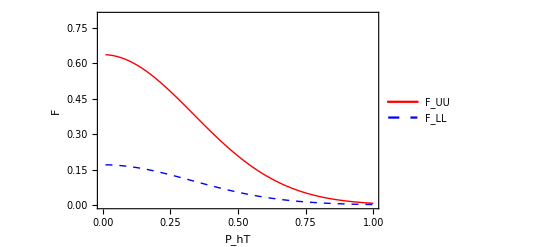

```mathematica
x=0.1;
z=0.3;
Q2=2.;

Plot[{FUUtest["pi+",x,z,Q2,PhT],FLLtest["pi+",x,z,Q2,PhT]},{PhT,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,0.8}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT","F"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"F_UU","F_LL"},{0.7,0.7}]]

Clear[x,z,Q2];
```

## A_LL numerics:

```mathematica
ALLtest[pion_,x_,z_,Q2_,PT_] := FLLtest[pion,x,z,Q2,PT]/FUUtest[pion,x,z,Q2,PT]  ;
```

```mathematica
?ALL
```

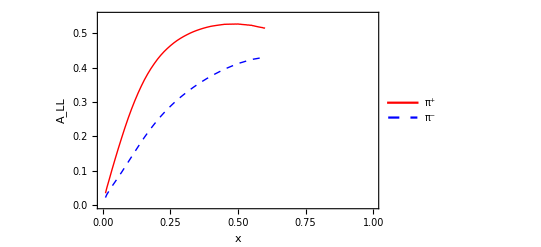

```mathematica
(*This plot is done with functions from the wwsidis package*)
Plot[{ALL["pi+",x,0.34,2.4, 0.5],ALL["pi-",x,0.34,2.4, 0.5]},{x,0.01,0.6},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0.,0.55}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","A_LL"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.8,0.15}]]
```

```mathematica
Plot[{ALLtest["pi+",x,0.34,2.4, 0.5],ALLtest["pi-",x,0.34,2.4, 0.5]},{x,0.01,0.6},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0.,0.55}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","A_LL"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.8,0.15}]]
```

-Graphics-